```mathematica
Clear["`*"]
```

#### 1 Define the basis vectors, where (ϕ,θ,z) corresponds to (θ,s,z) in the paper

```mathematica
eϕ={1,0,0};(*corresponds to eθ in Eq (6.2)*)
eθ={0,1,0};(*corresponds to es in Eq (6.2)*)
n={0,0,1};
er=eθ Cos[θ]+n Sin[θ];
ez=eθ Sin[θ]-n Cos[θ];
mu[Z_]=(1+Z)^2;
```

#### 2. Deformation gradient F and growth tensor, (1,2,3) correspond to (ϕ,θ,z)

```mathematica
F=({{1/(1+Z)r[θ,Z]/Sin[θ], 0, 0}, {0, 1/(1+Z)(Derivative[1,0][r][θ,Z] Cos[θ]+Derivative[1,0][z][θ,Z] Sin[θ]), Derivative[0,1][r][θ,Z] Cos[θ]+Derivative[0,1][z][θ,Z] Sin[θ]}, {0, 1/(1+Z)(Derivative[1,0][r][θ,Z] Sin[θ]-Derivative[1,0][z][θ,Z] Cos[θ]), Derivative[0,1][r][θ,Z] Sin[θ]-Derivative[0,1][z][θ,Z]Cos[θ]}});
F/.{r->Function[{θ,Z},Sin[θ]+Z Sin[θ]],z->Function[{θ,Z},1-Cos[θ]-Z Cos[θ]]}//Simplify //MatrixForm(*a simple check*)
G=({{γ1[θ,Z], 0, 0}, {0, γ2[θ,Z], 0}, {0, 0, 1}});(*growth tensor*)
JG=Det[G];
A=F.Inverse[G];
```

(1 | 0 | 0
0 | 1 | 0
0 | 0 | 1)

#### 3 Strain energy function and first PK stress

```mathematica
CC=Transpose[A].A;
I1=Tr[CC];
J=Det[A];
W=μ/2(I1-2 Log[J])+λ/2(J-1)^2;
```

#### 4 Series expansions and membrane energy functional

```mathematica
r[θ_,Z_]=r0[θ]+Z r1[θ]+1/2(Z^2-1/12 H^2)r2[θ];
z[θ_,Z_]=z0[θ]+Z z1[θ]+1/2(Z^2-1/12 H^2)z2[θ];
γ1[θ_,Z_]=γ1a[θ]+γ1b [θ] Z;
γ2[θ_,Z_]=γ2a[θ]+γ2b [θ] Z;
Φasy=Series[JG W mu[Z],{Z,0,2}]//Normal;
Φ0=Φasy/.{Z->0};
Φ2=Coefficient[Φasy,Z^2];
Vol=Series[r[θ,H/2]^2 Derivative[1,0][z][θ,H/2],{H,0,2}]//Normal;
V=Vol-1/12 H^2 D[r0[θ]^2 z2[θ],θ]//Simplify;
Lfull=(Φ0+1/12 H^2 Φ2)Sin[θ]+1/2 P  V;(*integration of ∫ Φ μ[Z], P is the actual pressure scaled by H*)
L=Series[Lfull,{H,0,2}]//Normal;
L0=L/.{H->0};
L1=Coefficient[L,H];
Lmem=L0+H L1//Simplify;
L2temp=Coefficient[L,H^2];
L2=L2temp/.{r2'[θ]->0,z2'[θ]->0};
L2-L2temp//Simplify
```

0

#### 4.1 First PK stress

```mathematica
AinvT=Transpose[Inverse[A]];
GinvT=Transpose[Inverse[G]];
PK=JG*(μ(A-AinvT)+λ(J-1) J AinvT).GinvT;
PK0=PK/.{Z->0,H->0};
```

#### 5 Find Optimal r2[θ] and z2[θ]

```mathematica
DateList[]
b11=Coefficient[L2,r2[θ]^2];
b12=1/2 Coefficient[L2,r2[θ]z2[θ]];
b22=Coefficient[L2,z2[θ]^2];
L2re=L2-(b11 r2[θ]^2 +2 b12 r2[θ] z2[θ]+b22 z2[θ]^2);
c1=Coefficient[L2re,r2[θ]];
c2=Coefficient[L2re,z2[θ]];
L2remain=L2/.{r2[θ]->0,z2[θ]->0};
b11 r2[θ]^2 +2 b12 r2[θ] z2[θ]+b22 z2[θ]^2+c1 r2[θ]+c2 z2[θ]+L2remain-L2//Simplify
L2simp=(b22 c1^2-2 b12 c1 c2+b11 c2^2)/(4 b12^2-4 b11 b22)+L2remain//Simplify;
DateList[]
```

{2024,1,23,22,58,41.47463}

0

{2024,1,23,23,1,33.083713}

#### 6 Discrete Energy

```mathematica
Lcon=Lmem+H^2 L2simp-H^2(q1[θ]D[Lmem,r1[θ]]+q2[θ]D[Lmem,z1[θ]]);
int=Lcon /.{r0[θ]->𝓇0,r0'[θ]->𝓇0p,z0'[θ]->𝓏0p,r1[θ]->𝓇1,z1[θ]->𝓏1,r1'[θ]->𝓇1p,z1'[θ]->𝓏1p,q1[θ]->𝓆1,q2[θ]->𝓆2};
PK0dis=PK0/.{r0[θ]->𝓇0,r0'[θ]->𝓇0p,z0'[θ]->𝓏0p,r1[θ]->𝓇1,z1[θ]->𝓏1};
```

#### 7 Shape functions by linear interpolation

```mathematica
subtotal={𝓇0->N[(1-ξ)] r0[j]+N[ξ] r0[1+j],𝓇0p->1/h(-r0[j]+r0[1+j]),𝓏0p->N[(1-ξ)] z0p[j]+N[ξ] z0p[1+j],𝓇1->N[(1-ξ)] r1[j]+N[ξ]r1[1+j],𝓇1p->1/h(-r1[j]+r1[1+j]),𝓏1->N[(1-ξ)] z1[j]+N[ξ]z1[1+j],𝓏1p->1/h(-z1[j]+z1[1+j]),𝓆1->N[(1-ξ)] q1[j]+N[ξ] q1[1+j],𝓆2->N[(1-ξ)] q2[j]+N[ξ] q2[1+j],θ-> j h +ξ h};
{ξ1,ξ2}={1/2(1-1/(√3)),1/2(1+1/(√3))}//N;
{ω1,ω2}={1/2,1/2}//N;
sub1=subtotal/.{ξ->ξ1};
sub2=subtotal/.{ξ->ξ2};
```

#### 8 Partition the domain and specify the growth functions

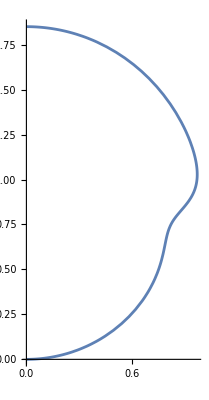

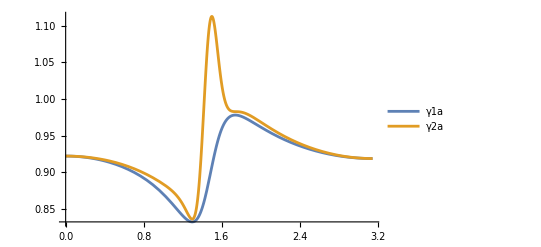

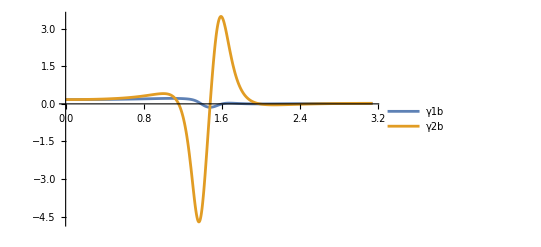

```mathematica
n=100;(*we set n=100 to get the results sooner*)
h=N[π/n];
H=0.2;(*thickness of the shell*)
kr=1.02;
kz=1.025;
r0ex[θ_]=kr*((0.03655050592897829 (1.7170911170632295-6.410124854400475 Cos[θ]+24.632408131813687 Cos[θ]^2+1. Cos[θ]^3) Sin[θ])/(0.0674511719516303-0.22103896755925656 Cos[θ]+1. Cos[θ]^2));
z0ex[θ_]=kz*(0.06099084887910621-0.26262889643457416 Cos[θ]+1.138515532951315 Cos[θ]^2-0.9003269794668691 Cos[θ]^3-0.03655050592897829 Cos[θ]^4)/(0.0674511719516303-0.22103896755925656 Cos[θ]+1. Cos[θ]^2);
γ1a[θ_]=r0ex[θ]/Sin[θ]//Simplify;
γ2a[θ_]=√(r0ex'[θ]^2+z0ex'[θ]^2);
γ1b[θ_]=Simplify[z0ex'[θ]/Sin[θ]]/(√(r0ex'[θ]^2+z0ex'[θ]^2))-Simplify[r0ex[θ]/Sin[θ]];
γ2b[θ_]=-(((r0ex'[θ]^2+z0ex'[θ]^2)^(3/2)+z0ex'[θ] r0ex''[θ]-r0ex'[θ] z0ex''[θ])/(r0ex'[θ]^2+z0ex'[θ]^2));
ParametricPlot[{r0ex[θ],z0ex[θ]},{θ,0,π}]
Plot[{γ1a[θ],γ2a[θ]},{θ,0,π},PlotRange->Full,PlotLegends->{"γ1a","γ2a"}]
Plot[{γ1b[θ],γ2b[θ]},{θ,0,π},PlotRange->Full,PlotLegends->{"γ1b","γ2b"}]
```

#### 9 Discrete equations

```mathematica
DateList[]
ℰdis=Sum[ω1(int/.sub1)+ω2(int/.sub2),{j,0,n-1}];
r0[0]=0;
eqsr0=Table[D[ℰdis,r0[j]],{j,1,n-1}];
r0[n]=0;
eqsz0p=Table[D[ℰdis,z0p[j]],{j,0,n}];
r1[0]=0;
eqsr1=Table[D[ℰdis,r1[j]],{j,1,n-1}];
r1[n]=0;
eqsz1=Table[D[ℰdis,z1[j]],{j,0,n}];
eqsq1=Table[D[ℰdis,q1[j]],{j,0,n}];
eqsq2=Table[D[ℰdis,q2[j]],{j,0,n}];
eqs=Join[Table[eqsr0[[j]]==0,{j,1,Length[eqsr0]}],Table[eqsz0p[[j]]==0,{j,1,Length[eqsz0p]}],Table[eqsr1[[j]]==0,{j,1,Length[eqsr1]}],Table[eqsz1[[j]]==0,{j,1,Length[eqsz1]}],Table[eqsq1[[j]]==0,{j,1,Length[eqsq1]}],Table[eqsq2[[j]]==0,{j,1,Length[eqsq2]}]];
DateList[]
eqs//Length
```

{2024,1,23,23,2,19.318652}

{2024,1,23,23,3,17.94024}

602

#### 9.1 Initial guess for q1 and q2

```mathematica
m11=(λ Csc[θ] r0g[θ]^2 z0g'[θ]^2)/(γ1a[θ] γ2a[θ])+(μ Sin[θ] γ1a[θ] γ2a[θ] (z1g[θ]^2 r0g'[θ]^2-2 r1g[θ] z1g[θ] r0g'[θ] z0g'[θ]+(1+r1g[θ]^2) z0g'[θ]^2))/(z1g[θ] r0g'[θ]-r1g[θ] z0g'[θ])^2;
m12=-((Csc[θ] r0g'[θ] z0g'[θ] (μ Sin[θ]^2 γ1a[θ]^2 γ2a[θ]^2+λ r0g[θ]^2 (z1g[θ] r0g'[θ]-r1g[θ] z0g'[θ])^2))/(γ1a[θ] γ2a[θ] (z1g[θ] r0g'[θ]-r1g[θ] z0g'[θ])^2));
m22=(λ Csc[θ] r0g[θ]^2 r0g'[θ]^2)/(γ1a[θ] γ2a[θ])+(μ Sin[θ] γ1a[θ] γ2a[θ] ((1+z1g[θ]^2) r0g'[θ]^2-2 r1g[θ] z1g[θ] r0g'[θ] z0g'[θ]+r1g[θ]^2 z0g'[θ]^2))/(z1g[θ] r0g'[θ]-r1g[θ] z0g'[θ])^2;
l1=-1/(24 γ1a[θ]^5 γ2a[θ]^5)Cos[θ] (γ1a[θ]^2 γ2a[θ]^2 (-((2 (γ1b[θ] γ2a[θ]+γ1a[θ] (2 γ2a[θ]+γ2b[θ])) (-λ Csc[θ]^2 r0g[θ]^2 z1g[θ] γ1a[θ] γ2a[θ] (z1g[θ] r0g'[θ]-r1g[θ] z0g'[θ]) (Sin[θ] γ1a[θ] γ2a[θ]+r0g[θ] (z1g[θ] r0g'[θ]-r1g[θ] z0g'[θ]))+μ (r0g[θ] z1g[θ] γ1a[θ]^3 γ2a[θ]^3-r0g[θ] Sin[θ] γ1a[θ]^3 γ2a[θ] (Sin[θ] r0g'[θ]-Cos[θ] z0g'[θ]) (z1g[θ] r0g'[θ]-r1g[θ] z0g'[θ])-Cos[θ] r0g[θ] γ1a[θ]^3 γ2a[θ] (z1g[θ] r0g'[θ]-r1g[θ] z0g'[θ]) (Cos[θ] r0g'[θ]+Sin[θ] z0g'[θ]))))/(r0g[θ] (z1g[θ] r0g'[θ]-r1g[θ] z0g'[θ])))+λ Csc[θ]^2 (2 (r1g[θ] z1g[θ] γ1a[θ]^2 γ2a[θ]^2+r0g[θ] z1g[θ] (-γ1a[θ] γ1b[θ] γ2a[θ]^2+γ1a[θ]^2 (-2 γ2a[θ]^2-γ2a[θ] γ2b[θ]))) (Sin[θ] γ1a[θ] γ2a[θ]+r0g[θ] (z1g[θ] r0g'[θ]-r1g[θ] z0g'[θ]))-2 r0g[θ] z1g[θ] γ1a[θ] γ2a[θ] (r1g[θ] γ1a[θ] γ2a[θ] (-z1g[θ] r0g'[θ]+r1g[θ] z0g'[θ])+r0g[θ] (z1g[θ] (γ1b[θ] γ2a[θ] r0g'[θ]+γ1a[θ] (2 γ2a[θ] r0g'[θ]+γ2b[θ] r0g'[θ]-γ2a[θ] r1g'[θ]))-r1g[θ] (γ1b[θ] γ2a[θ] z0g'[θ]+γ1a[θ] (2 γ2a[θ] z0g'[θ]+γ2b[θ] z0g'[θ]-γ2a[θ] z1g'[θ])))))+μ (-4 Sin[θ] γ1a[θ]^4 γ2a[θ] (γ2a[θ]+γ2b[θ]) (Sin[θ] r0g'[θ]-Cos[θ] z0g'[θ])-(2 γ1a[θ]^2 γ2a[θ]^2 (r1g[θ] z1g[θ] γ1a[θ]^2 γ2a[θ]^2+r0g[θ] z1g[θ] (-γ1a[θ] γ1b[θ] γ2a[θ]^2+γ1a[θ]^2 (-2 γ2a[θ]^2-γ2a[θ] γ2b[θ]))))/(r0g[θ] (z1g[θ] r0g'[θ]-r1g[θ] z0g'[θ]))-4 Cos[θ] γ1a[θ]^4 γ2a[θ] (γ2a[θ]+γ2b[θ]) (Cos[θ] r0g'[θ]+Sin[θ] z0g'[θ])+2 Sin[θ] γ1a[θ]^4 γ2a[θ]^2 (Sin[θ] r1g'[θ]-Cos[θ] z1g'[θ])+2 Cos[θ] γ1a[θ]^4 γ2a[θ]^2 (Cos[θ] r1g'[θ]+Sin[θ] z1g'[θ])-(2 z1g[θ] γ1a[θ]^3 γ2a[θ]^3 (r1g[θ] γ1a[θ] γ2a[θ] (-z1g[θ] r0g'[θ]+r1g[θ] z0g'[θ])+r0g[θ] (z1g[θ] (γ1b[θ] γ2a[θ] r0g'[θ]+γ1a[θ] (2 γ2a[θ] r0g'[θ]+γ2b[θ] r0g'[θ]-γ2a[θ] r1g'[θ]))-r1g[θ] (γ1b[θ] γ2a[θ] z0g'[θ]+γ1a[θ] (2 γ2a[θ] z0g'[θ]+γ2b[θ] z0g'[θ]-γ2a[θ] z1g'[θ])))))/(r0g[θ] (z1g[θ] r0g'[θ]-r1g[θ] z0g'[θ])^2)))-(Csc[θ]^4 (2 r0g'[θ] z0g'[θ] (μ Sin[θ]^2 γ1a[θ]^2 γ2a[θ]^2+λ r0g[θ]^2 (z1g[θ] r0g'[θ]-r1g[θ] z0g'[θ])^2) (2 λ r0g[θ]^2 r1g[θ] z1g[θ]^2 γ1a[θ] γ2a[θ] r0g'[θ] z0g'[θ]^2-λ r0g[θ]^2 r1g[θ]^2 z1g[θ] γ1a[θ] γ2a[θ] z0g'[θ]^3+z1g[θ] (-μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^3 z0g'[θ]-λ r0g[θ]^2 z1g[θ]^2 γ1a[θ] γ2a[θ] r0g'[θ]^2 z0g'[θ])) (z1g[θ]^3 r0g'[θ]^2 (μ Sin[θ]^2 γ1a[θ]^2 γ1b[θ] γ2a[θ]^3+μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^2 (2 γ2a[θ]+γ2b[θ])-λ r0g[θ]^2 γ1b[θ] γ2a[θ] r0g'[θ]^2+λ r0g[θ] γ1a[θ] r0g'[θ] (2 r1g[θ] γ2a[θ] r0g'[θ]-r0g[θ] (γ2b[θ] r0g'[θ]+2 γ2a[θ] (r0g'[θ]-r1g'[θ]))))-z1g[θ] (3 λ r0g[θ]^2 r1g[θ]^2 γ1b[θ] γ2a[θ] r0g'[θ]^2 z0g'[θ]^2+μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^2 (2 γ2a[θ]+γ2b[θ]) (r0g'[θ]^2-r1g[θ]^2 z0g'[θ]^2)+Sin[θ] γ1a[θ]^2 γ2a[θ]^2 (2 λ r1g[θ] r0g'[θ] (r1g[θ] r0g'[θ]+r0g[θ] r1g'[θ]) z0g'[θ]+μ Sin[θ] γ1b[θ] γ2a[θ] (r0g'[θ]^2-r1g[θ]^2 z0g'[θ]^2))+λ r0g[θ] r1g[θ]^2 γ1a[θ] r0g'[θ] z0g'[θ] (-6 r1g[θ] γ2a[θ] r0g'[θ] z0g'[θ]+r0g[θ] (3 γ2b[θ] r0g'[θ] z0g'[θ]+γ2a[θ] (-4 r1g'[θ] z0g'[θ]+r0g'[θ] (6 z0g'[θ]-2 z1g'[θ])))))+z1g[θ]^2 r0g'[θ] (λ r0g[θ] Sin[θ] γ1a[θ]^2 γ2a[θ]^2 r0g'[θ] r1g'[θ]-6 λ r0g[θ] r1g[θ]^2 γ1a[θ] γ2a[θ] r0g'[θ]^2 z0g'[θ]+r1g[θ] (-2 μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^2 (2 γ2a[θ]+γ2b[θ]) z0g'[θ]+3 λ r0g[θ]^2 γ1b[θ] γ2a[θ] r0g'[θ]^2 z0g'[θ]-Sin[θ] γ1a[θ]^2 γ2a[θ]^2 (-λ r0g'[θ]^2+2 μ Sin[θ] γ1b[θ] γ2a[θ] z0g'[θ])+λ r0g[θ]^2 γ1a[θ] r0g'[θ] (3 γ2b[θ] r0g'[θ] z0g'[θ]+γ2a[θ] (-5 r1g'[θ] z0g'[θ]+r0g'[θ] (6 z0g'[θ]-z1g'[θ])))))+r1g[θ] (λ r0g[θ]^2 r1g[θ]^2 γ1b[θ] γ2a[θ] r0g'[θ] z0g'[θ]^3+Sin[θ] γ1a[θ]^2 γ2a[θ]^2 z0g'[θ] (μ Sin[θ] γ1b[θ] γ2a[θ] r0g'[θ]+λ r1g[θ] (r1g[θ] r0g'[θ]+r0g[θ] r1g'[θ]) z0g'[θ])+λ r0g[θ] r1g[θ]^2 γ1a[θ] z0g'[θ]^2 (-2 r1g[θ] γ2a[θ] r0g'[θ] z0g'[θ]+r0g[θ] (γ2b[θ] r0g'[θ] z0g'[θ]+γ2a[θ] (-r1g'[θ] z0g'[θ]+r0g'[θ] (2 z0g'[θ]-z1g'[θ]))))+μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^2 (γ2b[θ] r0g'[θ] z0g'[θ]+γ2a[θ] (r1g'[θ] z0g'[θ]+r0g'[θ] (2 z0g'[θ]-z1g'[θ])))))+2 (μ (1+r1g[θ]^2) Sin[θ]^2 γ1a[θ]^2 γ2a[θ]^2 z0g'[θ]^2+λ r0g[θ]^2 r1g[θ]^2 z0g'[θ]^4+z1g[θ]^2 r0g'[θ]^2 (μ Sin[θ]^2 γ1a[θ]^2 γ2a[θ]^2+λ r0g[θ]^2 z0g'[θ]^2)-2 r1g[θ] z1g[θ] r0g'[θ] z0g'[θ] (μ Sin[θ]^2 γ1a[θ]^2 γ2a[θ]^2+λ r0g[θ]^2 z0g'[θ]^2)) (2 λ r0g[θ]^2 z1g[θ]^3 γ1a[θ] γ2a[θ] r0g'[θ]^3+z1g[θ]^2 r0g'[θ] (λ r0g[θ] Sin[θ] γ1a[θ]^2 γ2a[θ]^2 r0g'[θ]-5 λ r0g[θ]^2 r1g[θ] γ1a[θ] γ2a[θ] r0g'[θ] z0g'[θ])-z1g[θ] (2 λ r0g[θ] r1g[θ] Sin[θ] γ1a[θ]^2 γ2a[θ]^2 r0g'[θ] z0g'[θ]-4 λ r0g[θ]^2 r1g[θ]^2 γ1a[θ] γ2a[θ] r0g'[θ] z0g'[θ]^2)+r1g[θ] (μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^3 z0g'[θ]+λ r0g[θ] r1g[θ] Sin[θ] γ1a[θ]^2 γ2a[θ]^2 z0g'[θ]^2-λ r0g[θ]^2 r1g[θ]^2 γ1a[θ] γ2a[θ] z0g'[θ]^3)) (z1g[θ]^3 r0g'[θ]^2 (μ Sin[θ]^2 γ1a[θ]^2 γ1b[θ] γ2a[θ]^3+μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^2 (2 γ2a[θ]+γ2b[θ])-λ r0g[θ]^2 γ1b[θ] γ2a[θ] r0g'[θ]^2+λ r0g[θ] γ1a[θ] r0g'[θ] (2 r1g[θ] γ2a[θ] r0g'[θ]-r0g[θ] (γ2b[θ] r0g'[θ]+2 γ2a[θ] (r0g'[θ]-r1g'[θ]))))-z1g[θ] (3 λ r0g[θ]^2 r1g[θ]^2 γ1b[θ] γ2a[θ] r0g'[θ]^2 z0g'[θ]^2+μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^2 (2 γ2a[θ]+γ2b[θ]) (r0g'[θ]^2-r1g[θ]^2 z0g'[θ]^2)+Sin[θ] γ1a[θ]^2 γ2a[θ]^2 (2 λ r1g[θ] r0g'[θ] (r1g[θ] r0g'[θ]+r0g[θ] r1g'[θ]) z0g'[θ]+μ Sin[θ] γ1b[θ] γ2a[θ] (r0g'[θ]^2-r1g[θ]^2 z0g'[θ]^2))+λ r0g[θ] r1g[θ]^2 γ1a[θ] r0g'[θ] z0g'[θ] (-6 r1g[θ] γ2a[θ] r0g'[θ] z0g'[θ]+r0g[θ] (3 γ2b[θ] r0g'[θ] z0g'[θ]+γ2a[θ] (-4 r1g'[θ] z0g'[θ]+r0g'[θ] (6 z0g'[θ]-2 z1g'[θ])))))+z1g[θ]^2 r0g'[θ] (λ r0g[θ] Sin[θ] γ1a[θ]^2 γ2a[θ]^2 r0g'[θ] r1g'[θ]-6 λ r0g[θ] r1g[θ]^2 γ1a[θ] γ2a[θ] r0g'[θ]^2 z0g'[θ]+r1g[θ] (-2 μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^2 (2 γ2a[θ]+γ2b[θ]) z0g'[θ]+3 λ r0g[θ]^2 γ1b[θ] γ2a[θ] r0g'[θ]^2 z0g'[θ]-Sin[θ] γ1a[θ]^2 γ2a[θ]^2 (-λ r0g'[θ]^2+2 μ Sin[θ] γ1b[θ] γ2a[θ] z0g'[θ])+λ r0g[θ]^2 γ1a[θ] r0g'[θ] (3 γ2b[θ] r0g'[θ] z0g'[θ]+γ2a[θ] (-5 r1g'[θ] z0g'[θ]+r0g'[θ] (6 z0g'[θ]-z1g'[θ])))))+r1g[θ] (λ r0g[θ]^2 r1g[θ]^2 γ1b[θ] γ2a[θ] r0g'[θ] z0g'[θ]^3+Sin[θ] γ1a[θ]^2 γ2a[θ]^2 z0g'[θ] (μ Sin[θ] γ1b[θ] γ2a[θ] r0g'[θ]+λ r1g[θ] (r1g[θ] r0g'[θ]+r0g[θ] r1g'[θ]) z0g'[θ])+λ r0g[θ] r1g[θ]^2 γ1a[θ] z0g'[θ]^2 (-2 r1g[θ] γ2a[θ] r0g'[θ] z0g'[θ]+r0g[θ] (γ2b[θ] r0g'[θ] z0g'[θ]+γ2a[θ] (-r1g'[θ] z0g'[θ]+r0g'[θ] (2 z0g'[θ]-z1g'[θ]))))+μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^2 (γ2b[θ] r0g'[θ] z0g'[θ]+γ2a[θ] (r1g'[θ] z0g'[θ]+r0g'[θ] (2 z0g'[θ]-z1g'[θ])))))+2 (2 λ r0g[θ]^2 r1g[θ] z1g[θ]^2 γ1a[θ] γ2a[θ] r0g'[θ] z0g'[θ]^2-λ r0g[θ]^2 r1g[θ]^2 z1g[θ] γ1a[θ] γ2a[θ] z0g'[θ]^3+z1g[θ] (-μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^3 z0g'[θ]-λ r0g[θ]^2 z1g[θ]^2 γ1a[θ] γ2a[θ] r0g'[θ]^2 z0g'[θ])) (λ r0g[θ]^2 r0g'[θ]^2 (z1g[θ] r0g'[θ]-r1g[θ] z0g'[θ])^2+μ Sin[θ]^2 γ1a[θ]^2 γ2a[θ]^2 ((1+z1g[θ]^2) r0g'[θ]^2-2 r1g[θ] z1g[θ] r0g'[θ] z0g'[θ]+r1g[θ]^2 z0g'[θ]^2)) (2 λ r0g[θ] r1g[θ]^4 γ1a[θ] γ2a[θ] z0g'[θ]^4-r1g[θ]^3 z0g'[θ]^2 (-μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^2 (2 γ2a[θ]+γ2b[θ])+λ r0g[θ]^2 γ1b[θ] γ2a[θ] z0g'[θ]^2-Sin[θ] γ1a[θ]^2 γ2a[θ]^2 (μ Sin[θ] γ1b[θ] γ2a[θ]-λ z0g'[θ])+λ r0g[θ] γ1a[θ] z0g'[θ] (6 z1g[θ] γ2a[θ] r0g'[θ]+r0g[θ] (γ2b[θ] z0g'[θ]+2 γ2a[θ] (z0g'[θ]-z1g'[θ]))))+z1g[θ] (λ r0g[θ]^2 z1g[θ]^2 γ1b[θ] γ2a[θ] r0g'[θ]^3 z0g'[θ]+λ r0g[θ]^2 z1g[θ]^2 γ1a[θ] r0g'[θ]^2 (γ2b[θ] r0g'[θ] z0g'[θ]+γ2a[θ] (-r1g'[θ] z0g'[θ]+r0g'[θ] (2 z0g'[θ]-z1g'[θ])))+Sin[θ] γ1a[θ]^2 γ2a[θ]^2 r0g'[θ] (μ Sin[θ] γ1b[θ] γ2a[θ] z0g'[θ]-λ r0g[θ] z1g[θ] r0g'[θ] z1g'[θ])+μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^2 (γ2b[θ] r0g'[θ] z0g'[θ]+γ2a[θ] (-r1g'[θ] z0g'[θ]+r0g'[θ] (2 z0g'[θ]+z1g'[θ]))))+r1g[θ] (-2 λ r0g[θ] z1g[θ]^3 γ1a[θ] γ2a[θ] r0g'[θ]^3 z0g'[θ]-μ Sin[θ]^2 γ1a[θ]^2 γ2a[θ]^2 (γ1b[θ] γ2a[θ]+γ1a[θ] (2 γ2a[θ]+γ2b[θ])) z0g'[θ]^2+2 λ r0g[θ] Sin[θ] z1g[θ] γ1a[θ]^2 γ2a[θ]^2 r0g'[θ] z0g'[θ] z1g'[θ]+z1g[θ]^2 r0g'[θ] (μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^2 (2 γ2a[θ]+γ2b[θ]) r0g'[θ]-3 λ r0g[θ]^2 γ1b[θ] γ2a[θ] r0g'[θ] z0g'[θ]^2+Sin[θ] γ1a[θ]^2 γ2a[θ]^2 r0g'[θ] (μ Sin[θ] γ1b[θ] γ2a[θ]-λ z0g'[θ])+λ r0g[θ]^2 γ1a[θ] z0g'[θ] (-3 γ2b[θ] r0g'[θ] z0g'[θ]+γ2a[θ] (2 r1g'[θ] z0g'[θ]+r0g'[θ] (-6 z0g'[θ]+4 z1g'[θ])))))-r1g[θ]^2 z0g'[θ] (-6 λ r0g[θ] z1g[θ]^2 γ1a[θ] γ2a[θ] r0g'[θ]^2 z0g'[θ]+λ r0g[θ] Sin[θ] γ1a[θ]^2 γ2a[θ]^2 z0g'[θ] z1g'[θ]+z1g[θ] (2 μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^2 (2 γ2a[θ]+γ2b[θ]) r0g'[θ]-3 λ r0g[θ]^2 γ1b[θ] γ2a[θ] r0g'[θ] z0g'[θ]^2+2 Sin[θ] γ1a[θ]^2 γ2a[θ]^2 r0g'[θ] (μ Sin[θ] γ1b[θ] γ2a[θ]-λ z0g'[θ])+λ r0g[θ]^2 γ1a[θ] z0g'[θ] (-3 γ2b[θ] r0g'[θ] z0g'[θ]+γ2a[θ] (r1g'[θ] z0g'[θ]+r0g'[θ] (-6 z0g'[θ]+5 z1g'[θ]))))))+2 r0g'[θ] z0g'[θ] (μ Sin[θ]^2 γ1a[θ]^2 γ2a[θ]^2+λ r0g[θ]^2 (z1g[θ] r0g'[θ]-r1g[θ] z0g'[θ])^2) (2 λ r0g[θ]^2 z1g[θ]^3 γ1a[θ] γ2a[θ] r0g'[θ]^3+z1g[θ]^2 r0g'[θ] (λ r0g[θ] Sin[θ] γ1a[θ]^2 γ2a[θ]^2 r0g'[θ]-5 λ r0g[θ]^2 r1g[θ] γ1a[θ] γ2a[θ] r0g'[θ] z0g'[θ])-z1g[θ] (2 λ r0g[θ] r1g[θ] Sin[θ] γ1a[θ]^2 γ2a[θ]^2 r0g'[θ] z0g'[θ]-4 λ r0g[θ]^2 r1g[θ]^2 γ1a[θ] γ2a[θ] r0g'[θ] z0g'[θ]^2)+r1g[θ] (μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^3 z0g'[θ]+λ r0g[θ] r1g[θ] Sin[θ] γ1a[θ]^2 γ2a[θ]^2 z0g'[θ]^2-λ r0g[θ]^2 r1g[θ]^2 γ1a[θ] γ2a[θ] z0g'[θ]^3)) (2 λ r0g[θ] r1g[θ]^4 γ1a[θ] γ2a[θ] z0g'[θ]^4-r1g[θ]^3 z0g'[θ]^2 (-μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^2 (2 γ2a[θ]+γ2b[θ])+λ r0g[θ]^2 γ1b[θ] γ2a[θ] z0g'[θ]^2-Sin[θ] γ1a[θ]^2 γ2a[θ]^2 (μ Sin[θ] γ1b[θ] γ2a[θ]-λ z0g'[θ])+λ r0g[θ] γ1a[θ] z0g'[θ] (6 z1g[θ] γ2a[θ] r0g'[θ]+r0g[θ] (γ2b[θ] z0g'[θ]+2 γ2a[θ] (z0g'[θ]-z1g'[θ]))))+z1g[θ] (λ r0g[θ]^2 z1g[θ]^2 γ1b[θ] γ2a[θ] r0g'[θ]^3 z0g'[θ]+λ r0g[θ]^2 z1g[θ]^2 γ1a[θ] r0g'[θ]^2 (γ2b[θ] r0g'[θ] z0g'[θ]+γ2a[θ] (-r1g'[θ] z0g'[θ]+r0g'[θ] (2 z0g'[θ]-z1g'[θ])))+Sin[θ] γ1a[θ]^2 γ2a[θ]^2 r0g'[θ] (μ Sin[θ] γ1b[θ] γ2a[θ] z0g'[θ]-λ r0g[θ] z1g[θ] r0g'[θ] z1g'[θ])+μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^2 (γ2b[θ] r0g'[θ] z0g'[θ]+γ2a[θ] (-r1g'[θ] z0g'[θ]+r0g'[θ] (2 z0g'[θ]+z1g'[θ]))))+r1g[θ] (-2 λ r0g[θ] z1g[θ]^3 γ1a[θ] γ2a[θ] r0g'[θ]^3 z0g'[θ]-μ Sin[θ]^2 γ1a[θ]^2 γ2a[θ]^2 (γ1b[θ] γ2a[θ]+γ1a[θ] (2 γ2a[θ]+γ2b[θ])) z0g'[θ]^2+2 λ r0g[θ] Sin[θ] z1g[θ] γ1a[θ]^2 γ2a[θ]^2 r0g'[θ] z0g'[θ] z1g'[θ]+z1g[θ]^2 r0g'[θ] (μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^2 (2 γ2a[θ]+γ2b[θ]) r0g'[θ]-3 λ r0g[θ]^2 γ1b[θ] γ2a[θ] r0g'[θ] z0g'[θ]^2+Sin[θ] γ1a[θ]^2 γ2a[θ]^2 r0g'[θ] (μ Sin[θ] γ1b[θ] γ2a[θ]-λ z0g'[θ])+λ r0g[θ]^2 γ1a[θ] z0g'[θ] (-3 γ2b[θ] r0g'[θ] z0g'[θ]+γ2a[θ] (2 r1g'[θ] z0g'[θ]+r0g'[θ] (-6 z0g'[θ]+4 z1g'[θ])))))-r1g[θ]^2 z0g'[θ] (-6 λ r0g[θ] z1g[θ]^2 γ1a[θ] γ2a[θ] r0g'[θ]^2 z0g'[θ]+λ r0g[θ] Sin[θ] γ1a[θ]^2 γ2a[θ]^2 z0g'[θ] z1g'[θ]+z1g[θ] (2 μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^2 (2 γ2a[θ]+γ2b[θ]) r0g'[θ]-3 λ r0g[θ]^2 γ1b[θ] γ2a[θ] r0g'[θ] z0g'[θ]^2+2 Sin[θ] γ1a[θ]^2 γ2a[θ]^2 r0g'[θ] (μ Sin[θ] γ1b[θ] γ2a[θ]-λ z0g'[θ])+λ r0g[θ]^2 γ1a[θ] z0g'[θ] (-3 γ2b[θ] r0g'[θ] z0g'[θ]+γ2a[θ] (r1g'[θ] z0g'[θ]+r0g'[θ] (-6 z0g'[θ]+5 z1g'[θ]))))))))/(μ (z1g[θ] r0g'[θ]-r1g[θ] z0g'[θ])^6 (λ r0g[θ]^2 (r0g'[θ]^2+z0g'[θ]^2)+(μ Sin[θ]^2 γ1a[θ]^2 γ2a[θ]^2 ((1+z1g[θ]^2) r0g'[θ]^2-2 r1g[θ] z1g[θ] r0g'[θ] z0g'[θ]+(1+r1g[θ]^2) z0g'[θ]^2))/(z1g[θ] r0g'[θ]-r1g[θ] z0g'[θ])^2)))+1/(24 γ1a[θ]^5 γ2a[θ]^5)Sin[θ] (-((Csc[θ]^4 ((2 μ r1g[θ] Sin[θ]^2 γ1a[θ]^2 γ2a[θ]^2 z0g'[θ]^2+2 λ r0g[θ]^2 r1g[θ] z0g'[θ]^4-2 z1g[θ] r0g'[θ] z0g'[θ] (μ Sin[θ]^2 γ1a[θ]^2 γ2a[θ]^2+λ r0g[θ]^2 z0g'[θ]^2)) (z1g[θ]^3 r0g'[θ]^2 (μ Sin[θ]^2 γ1a[θ]^2 γ1b[θ] γ2a[θ]^3+μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^2 (2 γ2a[θ]+γ2b[θ])-λ r0g[θ]^2 γ1b[θ] γ2a[θ] r0g'[θ]^2+λ r0g[θ] γ1a[θ] r0g'[θ] (2 r1g[θ] γ2a[θ] r0g'[θ]-r0g[θ] (γ2b[θ] r0g'[θ]+2 γ2a[θ] (r0g'[θ]-r1g'[θ]))))-z1g[θ] (3 λ r0g[θ]^2 r1g[θ]^2 γ1b[θ] γ2a[θ] r0g'[θ]^2 z0g'[θ]^2+μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^2 (2 γ2a[θ]+γ2b[θ]) (r0g'[θ]^2-r1g[θ]^2 z0g'[θ]^2)+Sin[θ] γ1a[θ]^2 γ2a[θ]^2 (2 λ r1g[θ] r0g'[θ] (r1g[θ] r0g'[θ]+r0g[θ] r1g'[θ]) z0g'[θ]+μ Sin[θ] γ1b[θ] γ2a[θ] (r0g'[θ]^2-r1g[θ]^2 z0g'[θ]^2))+λ r0g[θ] r1g[θ]^2 γ1a[θ] r0g'[θ] z0g'[θ] (-6 r1g[θ] γ2a[θ] r0g'[θ] z0g'[θ]+r0g[θ] (3 γ2b[θ] r0g'[θ] z0g'[θ]+γ2a[θ] (-4 r1g'[θ] z0g'[θ]+r0g'[θ] (6 z0g'[θ]-2 z1g'[θ])))))+z1g[θ]^2 r0g'[θ] (λ r0g[θ] Sin[θ] γ1a[θ]^2 γ2a[θ]^2 r0g'[θ] r1g'[θ]-6 λ r0g[θ] r1g[θ]^2 γ1a[θ] γ2a[θ] r0g'[θ]^2 z0g'[θ]+r1g[θ] (-2 μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^2 (2 γ2a[θ]+γ2b[θ]) z0g'[θ]+3 λ r0g[θ]^2 γ1b[θ] γ2a[θ] r0g'[θ]^2 z0g'[θ]-Sin[θ] γ1a[θ]^2 γ2a[θ]^2 (-λ r0g'[θ]^2+2 μ Sin[θ] γ1b[θ] γ2a[θ] z0g'[θ])+λ r0g[θ]^2 γ1a[θ] r0g'[θ] (3 γ2b[θ] r0g'[θ] z0g'[θ]+γ2a[θ] (-5 r1g'[θ] z0g'[θ]+r0g'[θ] (6 z0g'[θ]-z1g'[θ])))))+r1g[θ] (λ r0g[θ]^2 r1g[θ]^2 γ1b[θ] γ2a[θ] r0g'[θ] z0g'[θ]^3+Sin[θ] γ1a[θ]^2 γ2a[θ]^2 z0g'[θ] (μ Sin[θ] γ1b[θ] γ2a[θ] r0g'[θ]+λ r1g[θ] (r1g[θ] r0g'[θ]+r0g[θ] r1g'[θ]) z0g'[θ])+λ r0g[θ] r1g[θ]^2 γ1a[θ] z0g'[θ]^2 (-2 r1g[θ] γ2a[θ] r0g'[θ] z0g'[θ]+r0g[θ] (γ2b[θ] r0g'[θ] z0g'[θ]+γ2a[θ] (-r1g'[θ] z0g'[θ]+r0g'[θ] (2 z0g'[θ]-z1g'[θ]))))+μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^2 (γ2b[θ] r0g'[θ] z0g'[θ]+γ2a[θ] (r1g'[θ] z0g'[θ]+r0g'[θ] (2 z0g'[θ]-z1g'[θ])))))^2+2 (μ (1+r1g[θ]^2) Sin[θ]^2 γ1a[θ]^2 γ2a[θ]^2 z0g'[θ]^2+λ r0g[θ]^2 r1g[θ]^2 z0g'[θ]^4+z1g[θ]^2 r0g'[θ]^2 (μ Sin[θ]^2 γ1a[θ]^2 γ2a[θ]^2+λ r0g[θ]^2 z0g'[θ]^2)-2 r1g[θ] z1g[θ] r0g'[θ] z0g'[θ] (μ Sin[θ]^2 γ1a[θ]^2 γ2a[θ]^2+λ r0g[θ]^2 z0g'[θ]^2)) (z1g[θ]^3 r0g'[θ]^2 (μ Sin[θ]^2 γ1a[θ]^2 γ1b[θ] γ2a[θ]^3+μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^2 (2 γ2a[θ]+γ2b[θ])-λ r0g[θ]^2 γ1b[θ] γ2a[θ] r0g'[θ]^2+λ r0g[θ] γ1a[θ] r0g'[θ] (2 r1g[θ] γ2a[θ] r0g'[θ]-r0g[θ] (γ2b[θ] r0g'[θ]+2 γ2a[θ] (r0g'[θ]-r1g'[θ]))))-z1g[θ] (3 λ r0g[θ]^2 r1g[θ]^2 γ1b[θ] γ2a[θ] r0g'[θ]^2 z0g'[θ]^2+μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^2 (2 γ2a[θ]+γ2b[θ]) (r0g'[θ]^2-r1g[θ]^2 z0g'[θ]^2)+Sin[θ] γ1a[θ]^2 γ2a[θ]^2 (2 λ r1g[θ] r0g'[θ] (r1g[θ] r0g'[θ]+r0g[θ] r1g'[θ]) z0g'[θ]+μ Sin[θ] γ1b[θ] γ2a[θ] (r0g'[θ]^2-r1g[θ]^2 z0g'[θ]^2))+λ r0g[θ] r1g[θ]^2 γ1a[θ] r0g'[θ] z0g'[θ] (-6 r1g[θ] γ2a[θ] r0g'[θ] z0g'[θ]+r0g[θ] (3 γ2b[θ] r0g'[θ] z0g'[θ]+γ2a[θ] (-4 r1g'[θ] z0g'[θ]+r0g'[θ] (6 z0g'[θ]-2 z1g'[θ])))))+z1g[θ]^2 r0g'[θ] (λ r0g[θ] Sin[θ] γ1a[θ]^2 γ2a[θ]^2 r0g'[θ] r1g'[θ]-6 λ r0g[θ] r1g[θ]^2 γ1a[θ] γ2a[θ] r0g'[θ]^2 z0g'[θ]+r1g[θ] (-2 μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^2 (2 γ2a[θ]+γ2b[θ]) z0g'[θ]+3 λ r0g[θ]^2 γ1b[θ] γ2a[θ] r0g'[θ]^2 z0g'[θ]-Sin[θ] γ1a[θ]^2 γ2a[θ]^2 (-λ r0g'[θ]^2+2 μ Sin[θ] γ1b[θ] γ2a[θ] z0g'[θ])+λ r0g[θ]^2 γ1a[θ] r0g'[θ] (3 γ2b[θ] r0g'[θ] z0g'[θ]+γ2a[θ] (-5 r1g'[θ] z0g'[θ]+r0g'[θ] (6 z0g'[θ]-z1g'[θ])))))+r1g[θ] (λ r0g[θ]^2 r1g[θ]^2 γ1b[θ] γ2a[θ] r0g'[θ] z0g'[θ]^3+Sin[θ] γ1a[θ]^2 γ2a[θ]^2 z0g'[θ] (μ Sin[θ] γ1b[θ] γ2a[θ] r0g'[θ]+λ r1g[θ] (r1g[θ] r0g'[θ]+r0g[θ] r1g'[θ]) z0g'[θ])+λ r0g[θ] r1g[θ]^2 γ1a[θ] z0g'[θ]^2 (-2 r1g[θ] γ2a[θ] r0g'[θ] z0g'[θ]+r0g[θ] (γ2b[θ] r0g'[θ] z0g'[θ]+γ2a[θ] (-r1g'[θ] z0g'[θ]+r0g'[θ] (2 z0g'[θ]-z1g'[θ]))))+μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^2 (γ2b[θ] r0g'[θ] z0g'[θ]+γ2a[θ] (r1g'[θ] z0g'[θ]+r0g'[θ] (2 z0g'[θ]-z1g'[θ]))))) (2 λ r0g[θ] z1g[θ]^3 γ1a[θ] γ2a[θ] r0g'[θ]^4+λ r0g[θ]^2 r1g[θ]^2 γ1b[θ] γ2a[θ] r0g'[θ] z0g'[θ]^3+Sin[θ] γ1a[θ]^2 γ2a[θ]^2 z0g'[θ] (μ Sin[θ] γ1b[θ] γ2a[θ] r0g'[θ]+λ r1g[θ] (r1g[θ] r0g'[θ]+r0g[θ] r1g'[θ]) z0g'[θ])-z1g[θ] (-2 μ r1g[θ] Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^2 (2 γ2a[θ]+γ2b[θ]) z0g'[θ]^2-6 λ r0g[θ] r1g[θ]^2 γ1a[θ] γ2a[θ] r0g'[θ]^2 z0g'[θ]^2+6 λ r0g[θ]^2 r1g[θ] γ1b[θ] γ2a[θ] r0g'[θ]^2 z0g'[θ]^2+Sin[θ] γ1a[θ]^2 γ2a[θ]^2 (2 λ r1g[θ] r0g'[θ]^2 z0g'[θ]+2 λ r0g'[θ] (r1g[θ] r0g'[θ]+r0g[θ] r1g'[θ]) z0g'[θ]-2 μ r1g[θ] Sin[θ] γ1b[θ] γ2a[θ] z0g'[θ]^2)+2 λ r0g[θ] r1g[θ] γ1a[θ] r0g'[θ] z0g'[θ] (-6 r1g[θ] γ2a[θ] r0g'[θ] z0g'[θ]+r0g[θ] (3 γ2b[θ] r0g'[θ] z0g'[θ]+γ2a[θ] (-4 r1g'[θ] z0g'[θ]+r0g'[θ] (6 z0g'[θ]-2 z1g'[θ])))))+r1g[θ] (-2 λ r0g[θ] r1g[θ]^2 γ1a[θ] γ2a[θ] r0g'[θ] z0g'[θ]^3+2 λ r0g[θ]^2 r1g[θ] γ1b[θ] γ2a[θ] r0g'[θ] z0g'[θ]^3+Sin[θ] γ1a[θ]^2 γ2a[θ]^2 z0g'[θ] (λ r1g[θ] r0g'[θ] z0g'[θ]+λ (r1g[θ] r0g'[θ]+r0g[θ] r1g'[θ]) z0g'[θ])+2 λ r0g[θ] r1g[θ] γ1a[θ] z0g'[θ]^2 (-2 r1g[θ] γ2a[θ] r0g'[θ] z0g'[θ]+r0g[θ] (γ2b[θ] r0g'[θ] z0g'[θ]+γ2a[θ] (-r1g'[θ] z0g'[θ]+r0g'[θ] (2 z0g'[θ]-z1g'[θ])))))+λ r0g[θ] r1g[θ]^2 γ1a[θ] z0g'[θ]^2 (-2 r1g[θ] γ2a[θ] r0g'[θ] z0g'[θ]+r0g[θ] (γ2b[θ] r0g'[θ] z0g'[θ]+γ2a[θ] (-r1g'[θ] z0g'[θ]+r0g'[θ] (2 z0g'[θ]-z1g'[θ]))))+z1g[θ]^2 r0g'[θ] (-2 μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^2 (2 γ2a[θ]+γ2b[θ]) z0g'[θ]-12 λ r0g[θ] r1g[θ] γ1a[θ] γ2a[θ] r0g'[θ]^2 z0g'[θ]+3 λ r0g[θ]^2 γ1b[θ] γ2a[θ] r0g'[θ]^2 z0g'[θ]-Sin[θ] γ1a[θ]^2 γ2a[θ]^2 (-λ r0g'[θ]^2+2 μ Sin[θ] γ1b[θ] γ2a[θ] z0g'[θ])+λ r0g[θ]^2 γ1a[θ] r0g'[θ] (3 γ2b[θ] r0g'[θ] z0g'[θ]+γ2a[θ] (-5 r1g'[θ] z0g'[θ]+r0g'[θ] (6 z0g'[θ]-z1g'[θ]))))+μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^2 (γ2b[θ] r0g'[θ] z0g'[θ]+γ2a[θ] (r1g'[θ] z0g'[θ]+r0g'[θ] (2 z0g'[θ]-z1g'[θ]))))+2 r0g'[θ] z0g'[θ] (μ Sin[θ]^2 γ1a[θ]^2 γ2a[θ]^2+λ r0g[θ]^2 (z1g[θ] r0g'[θ]-r1g[θ] z0g'[θ])^2) (z1g[θ]^3 r0g'[θ]^2 (μ Sin[θ]^2 γ1a[θ]^2 γ1b[θ] γ2a[θ]^3+μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^2 (2 γ2a[θ]+γ2b[θ])-λ r0g[θ]^2 γ1b[θ] γ2a[θ] r0g'[θ]^2+λ r0g[θ] γ1a[θ] r0g'[θ] (2 r1g[θ] γ2a[θ] r0g'[θ]-r0g[θ] (γ2b[θ] r0g'[θ]+2 γ2a[θ] (r0g'[θ]-r1g'[θ]))))-z1g[θ] (3 λ r0g[θ]^2 r1g[θ]^2 γ1b[θ] γ2a[θ] r0g'[θ]^2 z0g'[θ]^2+μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^2 (2 γ2a[θ]+γ2b[θ]) (r0g'[θ]^2-r1g[θ]^2 z0g'[θ]^2)+Sin[θ] γ1a[θ]^2 γ2a[θ]^2 (2 λ r1g[θ] r0g'[θ] (r1g[θ] r0g'[θ]+r0g[θ] r1g'[θ]) z0g'[θ]+μ Sin[θ] γ1b[θ] γ2a[θ] (r0g'[θ]^2-r1g[θ]^2 z0g'[θ]^2))+λ r0g[θ] r1g[θ]^2 γ1a[θ] r0g'[θ] z0g'[θ] (-6 r1g[θ] γ2a[θ] r0g'[θ] z0g'[θ]+r0g[θ] (3 γ2b[θ] r0g'[θ] z0g'[θ]+γ2a[θ] (-4 r1g'[θ] z0g'[θ]+r0g'[θ] (6 z0g'[θ]-2 z1g'[θ])))))+z1g[θ]^2 r0g'[θ] (λ r0g[θ] Sin[θ] γ1a[θ]^2 γ2a[θ]^2 r0g'[θ] r1g'[θ]-6 λ r0g[θ] r1g[θ]^2 γ1a[θ] γ2a[θ] r0g'[θ]^2 z0g'[θ]+r1g[θ] (-2 μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^2 (2 γ2a[θ]+γ2b[θ]) z0g'[θ]+3 λ r0g[θ]^2 γ1b[θ] γ2a[θ] r0g'[θ]^2 z0g'[θ]-Sin[θ] γ1a[θ]^2 γ2a[θ]^2 (-λ r0g'[θ]^2+2 μ Sin[θ] γ1b[θ] γ2a[θ] z0g'[θ])+λ r0g[θ]^2 γ1a[θ] r0g'[θ] (3 γ2b[θ] r0g'[θ] z0g'[θ]+γ2a[θ] (-5 r1g'[θ] z0g'[θ]+r0g'[θ] (6 z0g'[θ]-z1g'[θ])))))+r1g[θ] (λ r0g[θ]^2 r1g[θ]^2 γ1b[θ] γ2a[θ] r0g'[θ] z0g'[θ]^3+Sin[θ] γ1a[θ]^2 γ2a[θ]^2 z0g'[θ] (μ Sin[θ] γ1b[θ] γ2a[θ] r0g'[θ]+λ r1g[θ] (r1g[θ] r0g'[θ]+r0g[θ] r1g'[θ]) z0g'[θ])+λ r0g[θ] r1g[θ]^2 γ1a[θ] z0g'[θ]^2 (-2 r1g[θ] γ2a[θ] r0g'[θ] z0g'[θ]+r0g[θ] (γ2b[θ] r0g'[θ] z0g'[θ]+γ2a[θ] (-r1g'[θ] z0g'[θ]+r0g'[θ] (2 z0g'[θ]-z1g'[θ]))))+μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^2 (γ2b[θ] r0g'[θ] z0g'[θ]+γ2a[θ] (r1g'[θ] z0g'[θ]+r0g'[θ] (2 z0g'[θ]-z1g'[θ]))))) (-2 λ r0g[θ] z1g[θ]^3 γ1a[θ] γ2a[θ] r0g'[θ]^3 z0g'[θ]-μ Sin[θ]^2 γ1a[θ]^2 γ2a[θ]^2 (γ1b[θ] γ2a[θ]+γ1a[θ] (2 γ2a[θ]+γ2b[θ])) z0g'[θ]^2+8 λ r0g[θ] r1g[θ]^3 γ1a[θ] γ2a[θ] z0g'[θ]^4-3 r1g[θ]^2 z0g'[θ]^2 (-μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^2 (2 γ2a[θ]+γ2b[θ])+λ r0g[θ]^2 γ1b[θ] γ2a[θ] z0g'[θ]^2-Sin[θ] γ1a[θ]^2 γ2a[θ]^2 (μ Sin[θ] γ1b[θ] γ2a[θ]-λ z0g'[θ])+λ r0g[θ] γ1a[θ] z0g'[θ] (6 z1g[θ] γ2a[θ] r0g'[θ]+r0g[θ] (γ2b[θ] z0g'[θ]+2 γ2a[θ] (z0g'[θ]-z1g'[θ]))))+2 λ r0g[θ] Sin[θ] z1g[θ] γ1a[θ]^2 γ2a[θ]^2 r0g'[θ] z0g'[θ] z1g'[θ]+z1g[θ]^2 r0g'[θ] (μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^2 (2 γ2a[θ]+γ2b[θ]) r0g'[θ]-3 λ r0g[θ]^2 γ1b[θ] γ2a[θ] r0g'[θ] z0g'[θ]^2+Sin[θ] γ1a[θ]^2 γ2a[θ]^2 r0g'[θ] (μ Sin[θ] γ1b[θ] γ2a[θ]-λ z0g'[θ])+λ r0g[θ]^2 γ1a[θ] z0g'[θ] (-3 γ2b[θ] r0g'[θ] z0g'[θ]+γ2a[θ] (2 r1g'[θ] z0g'[θ]+r0g'[θ] (-6 z0g'[θ]+4 z1g'[θ]))))-2 r1g[θ] z0g'[θ] (-6 λ r0g[θ] z1g[θ]^2 γ1a[θ] γ2a[θ] r0g'[θ]^2 z0g'[θ]+λ r0g[θ] Sin[θ] γ1a[θ]^2 γ2a[θ]^2 z0g'[θ] z1g'[θ]+z1g[θ] (2 μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^2 (2 γ2a[θ]+γ2b[θ]) r0g'[θ]-3 λ r0g[θ]^2 γ1b[θ] γ2a[θ] r0g'[θ] z0g'[θ]^2+2 Sin[θ] γ1a[θ]^2 γ2a[θ]^2 r0g'[θ] (μ Sin[θ] γ1b[θ] γ2a[θ]-λ z0g'[θ])+λ r0g[θ]^2 γ1a[θ] z0g'[θ] (-3 γ2b[θ] r0g'[θ] z0g'[θ]+γ2a[θ] (r1g'[θ] z0g'[θ]+r0g'[θ] (-6 z0g'[θ]+5 z1g'[θ]))))))-4 λ r0g[θ]^2 r0g'[θ] z0g'[θ]^2 (z1g[θ] r0g'[θ]-r1g[θ] z0g'[θ]) (z1g[θ]^3 r0g'[θ]^2 (μ Sin[θ]^2 γ1a[θ]^2 γ1b[θ] γ2a[θ]^3+μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^2 (2 γ2a[θ]+γ2b[θ])-λ r0g[θ]^2 γ1b[θ] γ2a[θ] r0g'[θ]^2+λ r0g[θ] γ1a[θ] r0g'[θ] (2 r1g[θ] γ2a[θ] r0g'[θ]-r0g[θ] (γ2b[θ] r0g'[θ]+2 γ2a[θ] (r0g'[θ]-r1g'[θ]))))-z1g[θ] (3 λ r0g[θ]^2 r1g[θ]^2 γ1b[θ] γ2a[θ] r0g'[θ]^2 z0g'[θ]^2+μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^2 (2 γ2a[θ]+γ2b[θ]) (r0g'[θ]^2-r1g[θ]^2 z0g'[θ]^2)+Sin[θ] γ1a[θ]^2 γ2a[θ]^2 (2 λ r1g[θ] r0g'[θ] (r1g[θ] r0g'[θ]+r0g[θ] r1g'[θ]) z0g'[θ]+μ Sin[θ] γ1b[θ] γ2a[θ] (r0g'[θ]^2-r1g[θ]^2 z0g'[θ]^2))+λ r0g[θ] r1g[θ]^2 γ1a[θ] r0g'[θ] z0g'[θ] (-6 r1g[θ] γ2a[θ] r0g'[θ] z0g'[θ]+r0g[θ] (3 γ2b[θ] r0g'[θ] z0g'[θ]+γ2a[θ] (-4 r1g'[θ] z0g'[θ]+r0g'[θ] (6 z0g'[θ]-2 z1g'[θ])))))+z1g[θ]^2 r0g'[θ] (λ r0g[θ] Sin[θ] γ1a[θ]^2 γ2a[θ]^2 r0g'[θ] r1g'[θ]-6 λ r0g[θ] r1g[θ]^2 γ1a[θ] γ2a[θ] r0g'[θ]^2 z0g'[θ]+r1g[θ] (-2 μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^2 (2 γ2a[θ]+γ2b[θ]) z0g'[θ]+3 λ r0g[θ]^2 γ1b[θ] γ2a[θ] r0g'[θ]^2 z0g'[θ]-Sin[θ] γ1a[θ]^2 γ2a[θ]^2 (-λ r0g'[θ]^2+2 μ Sin[θ] γ1b[θ] γ2a[θ] z0g'[θ])+λ r0g[θ]^2 γ1a[θ] r0g'[θ] (3 γ2b[θ] r0g'[θ] z0g'[θ]+γ2a[θ] (-5 r1g'[θ] z0g'[θ]+r0g'[θ] (6 z0g'[θ]-z1g'[θ])))))+r1g[θ] (λ r0g[θ]^2 r1g[θ]^2 γ1b[θ] γ2a[θ] r0g'[θ] z0g'[θ]^3+Sin[θ] γ1a[θ]^2 γ2a[θ]^2 z0g'[θ] (μ Sin[θ] γ1b[θ] γ2a[θ] r0g'[θ]+λ r1g[θ] (r1g[θ] r0g'[θ]+r0g[θ] r1g'[θ]) z0g'[θ])+λ r0g[θ] r1g[θ]^2 γ1a[θ] z0g'[θ]^2 (-2 r1g[θ] γ2a[θ] r0g'[θ] z0g'[θ]+r0g[θ] (γ2b[θ] r0g'[θ] z0g'[θ]+γ2a[θ] (-r1g'[θ] z0g'[θ]+r0g'[θ] (2 z0g'[θ]-z1g'[θ]))))+μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^2 (γ2b[θ] r0g'[θ] z0g'[θ]+γ2a[θ] (r1g'[θ] z0g'[θ]+r0g'[θ] (2 z0g'[θ]-z1g'[θ]))))) (2 λ r0g[θ] r1g[θ]^4 γ1a[θ] γ2a[θ] z0g'[θ]^4-r1g[θ]^3 z0g'[θ]^2 (-μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^2 (2 γ2a[θ]+γ2b[θ])+λ r0g[θ]^2 γ1b[θ] γ2a[θ] z0g'[θ]^2-Sin[θ] γ1a[θ]^2 γ2a[θ]^2 (μ Sin[θ] γ1b[θ] γ2a[θ]-λ z0g'[θ])+λ r0g[θ] γ1a[θ] z0g'[θ] (6 z1g[θ] γ2a[θ] r0g'[θ]+r0g[θ] (γ2b[θ] z0g'[θ]+2 γ2a[θ] (z0g'[θ]-z1g'[θ]))))+z1g[θ] (λ r0g[θ]^2 z1g[θ]^2 γ1b[θ] γ2a[θ] r0g'[θ]^3 z0g'[θ]+λ r0g[θ]^2 z1g[θ]^2 γ1a[θ] r0g'[θ]^2 (γ2b[θ] r0g'[θ] z0g'[θ]+γ2a[θ] (-r1g'[θ] z0g'[θ]+r0g'[θ] (2 z0g'[θ]-z1g'[θ])))+Sin[θ] γ1a[θ]^2 γ2a[θ]^2 r0g'[θ] (μ Sin[θ] γ1b[θ] γ2a[θ] z0g'[θ]-λ r0g[θ] z1g[θ] r0g'[θ] z1g'[θ])+μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^2 (γ2b[θ] r0g'[θ] z0g'[θ]+γ2a[θ] (-r1g'[θ] z0g'[θ]+r0g'[θ] (2 z0g'[θ]+z1g'[θ]))))+r1g[θ] (-2 λ r0g[θ] z1g[θ]^3 γ1a[θ] γ2a[θ] r0g'[θ]^3 z0g'[θ]-μ Sin[θ]^2 γ1a[θ]^2 γ2a[θ]^2 (γ1b[θ] γ2a[θ]+γ1a[θ] (2 γ2a[θ]+γ2b[θ])) z0g'[θ]^2+2 λ r0g[θ] Sin[θ] z1g[θ] γ1a[θ]^2 γ2a[θ]^2 r0g'[θ] z0g'[θ] z1g'[θ]+z1g[θ]^2 r0g'[θ] (μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^2 (2 γ2a[θ]+γ2b[θ]) r0g'[θ]-3 λ r0g[θ]^2 γ1b[θ] γ2a[θ] r0g'[θ] z0g'[θ]^2+Sin[θ] γ1a[θ]^2 γ2a[θ]^2 r0g'[θ] (μ Sin[θ] γ1b[θ] γ2a[θ]-λ z0g'[θ])+λ r0g[θ]^2 γ1a[θ] z0g'[θ] (-3 γ2b[θ] r0g'[θ] z0g'[θ]+γ2a[θ] (2 r1g'[θ] z0g'[θ]+r0g'[θ] (-6 z0g'[θ]+4 z1g'[θ])))))-r1g[θ]^2 z0g'[θ] (-6 λ r0g[θ] z1g[θ]^2 γ1a[θ] γ2a[θ] r0g'[θ]^2 z0g'[θ]+λ r0g[θ] Sin[θ] γ1a[θ]^2 γ2a[θ]^2 z0g'[θ] z1g'[θ]+z1g[θ] (2 μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^2 (2 γ2a[θ]+γ2b[θ]) r0g'[θ]-3 λ r0g[θ]^2 γ1b[θ] γ2a[θ] r0g'[θ] z0g'[θ]^2+2 Sin[θ] γ1a[θ]^2 γ2a[θ]^2 r0g'[θ] (μ Sin[θ] γ1b[θ] γ2a[θ]-λ z0g'[θ])+λ r0g[θ]^2 γ1a[θ] z0g'[θ] (-3 γ2b[θ] r0g'[θ] z0g'[θ]+γ2a[θ] (r1g'[θ] z0g'[θ]+r0g'[θ] (-6 z0g'[θ]+5 z1g'[θ]))))))+2 r0g'[θ] z0g'[θ] (μ Sin[θ]^2 γ1a[θ]^2 γ2a[θ]^2+λ r0g[θ]^2 (z1g[θ] r0g'[θ]-r1g[θ] z0g'[θ])^2) (2 λ r0g[θ] z1g[θ]^3 γ1a[θ] γ2a[θ] r0g'[θ]^4+λ r0g[θ]^2 r1g[θ]^2 γ1b[θ] γ2a[θ] r0g'[θ] z0g'[θ]^3+Sin[θ] γ1a[θ]^2 γ2a[θ]^2 z0g'[θ] (μ Sin[θ] γ1b[θ] γ2a[θ] r0g'[θ]+λ r1g[θ] (r1g[θ] r0g'[θ]+r0g[θ] r1g'[θ]) z0g'[θ])-z1g[θ] (-2 μ r1g[θ] Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^2 (2 γ2a[θ]+γ2b[θ]) z0g'[θ]^2-6 λ r0g[θ] r1g[θ]^2 γ1a[θ] γ2a[θ] r0g'[θ]^2 z0g'[θ]^2+6 λ r0g[θ]^2 r1g[θ] γ1b[θ] γ2a[θ] r0g'[θ]^2 z0g'[θ]^2+Sin[θ] γ1a[θ]^2 γ2a[θ]^2 (2 λ r1g[θ] r0g'[θ]^2 z0g'[θ]+2 λ r0g'[θ] (r1g[θ] r0g'[θ]+r0g[θ] r1g'[θ]) z0g'[θ]-2 μ r1g[θ] Sin[θ] γ1b[θ] γ2a[θ] z0g'[θ]^2)+2 λ r0g[θ] r1g[θ] γ1a[θ] r0g'[θ] z0g'[θ] (-6 r1g[θ] γ2a[θ] r0g'[θ] z0g'[θ]+r0g[θ] (3 γ2b[θ] r0g'[θ] z0g'[θ]+γ2a[θ] (-4 r1g'[θ] z0g'[θ]+r0g'[θ] (6 z0g'[θ]-2 z1g'[θ])))))+r1g[θ] (-2 λ r0g[θ] r1g[θ]^2 γ1a[θ] γ2a[θ] r0g'[θ] z0g'[θ]^3+2 λ r0g[θ]^2 r1g[θ] γ1b[θ] γ2a[θ] r0g'[θ] z0g'[θ]^3+Sin[θ] γ1a[θ]^2 γ2a[θ]^2 z0g'[θ] (λ r1g[θ] r0g'[θ] z0g'[θ]+λ (r1g[θ] r0g'[θ]+r0g[θ] r1g'[θ]) z0g'[θ])+2 λ r0g[θ] r1g[θ] γ1a[θ] z0g'[θ]^2 (-2 r1g[θ] γ2a[θ] r0g'[θ] z0g'[θ]+r0g[θ] (γ2b[θ] r0g'[θ] z0g'[θ]+γ2a[θ] (-r1g'[θ] z0g'[θ]+r0g'[θ] (2 z0g'[θ]-z1g'[θ])))))+λ r0g[θ] r1g[θ]^2 γ1a[θ] z0g'[θ]^2 (-2 r1g[θ] γ2a[θ] r0g'[θ] z0g'[θ]+r0g[θ] (γ2b[θ] r0g'[θ] z0g'[θ]+γ2a[θ] (-r1g'[θ] z0g'[θ]+r0g'[θ] (2 z0g'[θ]-z1g'[θ]))))+z1g[θ]^2 r0g'[θ] (-2 μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^2 (2 γ2a[θ]+γ2b[θ]) z0g'[θ]-12 λ r0g[θ] r1g[θ] γ1a[θ] γ2a[θ] r0g'[θ]^2 z0g'[θ]+3 λ r0g[θ]^2 γ1b[θ] γ2a[θ] r0g'[θ]^2 z0g'[θ]-Sin[θ] γ1a[θ]^2 γ2a[θ]^2 (-λ r0g'[θ]^2+2 μ Sin[θ] γ1b[θ] γ2a[θ] z0g'[θ])+λ r0g[θ]^2 γ1a[θ] r0g'[θ] (3 γ2b[θ] r0g'[θ] z0g'[θ]+γ2a[θ] (-5 r1g'[θ] z0g'[θ]+r0g'[θ] (6 z0g'[θ]-z1g'[θ]))))+μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^2 (γ2b[θ] r0g'[θ] z0g'[θ]+γ2a[θ] (r1g'[θ] z0g'[θ]+r0g'[θ] (2 z0g'[θ]-z1g'[θ])))) (2 λ r0g[θ] r1g[θ]^4 γ1a[θ] γ2a[θ] z0g'[θ]^4-r1g[θ]^3 z0g'[θ]^2 (-μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^2 (2 γ2a[θ]+γ2b[θ])+λ r0g[θ]^2 γ1b[θ] γ2a[θ] z0g'[θ]^2-Sin[θ] γ1a[θ]^2 γ2a[θ]^2 (μ Sin[θ] γ1b[θ] γ2a[θ]-λ z0g'[θ])+λ r0g[θ] γ1a[θ] z0g'[θ] (6 z1g[θ] γ2a[θ] r0g'[θ]+r0g[θ] (γ2b[θ] z0g'[θ]+2 γ2a[θ] (z0g'[θ]-z1g'[θ]))))+z1g[θ] (λ r0g[θ]^2 z1g[θ]^2 γ1b[θ] γ2a[θ] r0g'[θ]^3 z0g'[θ]+λ r0g[θ]^2 z1g[θ]^2 γ1a[θ] r0g'[θ]^2 (γ2b[θ] r0g'[θ] z0g'[θ]+γ2a[θ] (-r1g'[θ] z0g'[θ]+r0g'[θ] (2 z0g'[θ]-z1g'[θ])))+Sin[θ] γ1a[θ]^2 γ2a[θ]^2 r0g'[θ] (μ Sin[θ] γ1b[θ] γ2a[θ] z0g'[θ]-λ r0g[θ] z1g[θ] r0g'[θ] z1g'[θ])+μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^2 (γ2b[θ] r0g'[θ] z0g'[θ]+γ2a[θ] (-r1g'[θ] z0g'[θ]+r0g'[θ] (2 z0g'[θ]+z1g'[θ]))))+r1g[θ] (-2 λ r0g[θ] z1g[θ]^3 γ1a[θ] γ2a[θ] r0g'[θ]^3 z0g'[θ]-μ Sin[θ]^2 γ1a[θ]^2 γ2a[θ]^2 (γ1b[θ] γ2a[θ]+γ1a[θ] (2 γ2a[θ]+γ2b[θ])) z0g'[θ]^2+2 λ r0g[θ] Sin[θ] z1g[θ] γ1a[θ]^2 γ2a[θ]^2 r0g'[θ] z0g'[θ] z1g'[θ]+z1g[θ]^2 r0g'[θ] (μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^2 (2 γ2a[θ]+γ2b[θ]) r0g'[θ]-3 λ r0g[θ]^2 γ1b[θ] γ2a[θ] r0g'[θ] z0g'[θ]^2+Sin[θ] γ1a[θ]^2 γ2a[θ]^2 r0g'[θ] (μ Sin[θ] γ1b[θ] γ2a[θ]-λ z0g'[θ])+λ r0g[θ]^2 γ1a[θ] z0g'[θ] (-3 γ2b[θ] r0g'[θ] z0g'[θ]+γ2a[θ] (2 r1g'[θ] z0g'[θ]+r0g'[θ] (-6 z0g'[θ]+4 z1g'[θ])))))-r1g[θ]^2 z0g'[θ] (-6 λ r0g[θ] z1g[θ]^2 γ1a[θ] γ2a[θ] r0g'[θ]^2 z0g'[θ]+λ r0g[θ] Sin[θ] γ1a[θ]^2 γ2a[θ]^2 z0g'[θ] z1g'[θ]+z1g[θ] (2 μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^2 (2 γ2a[θ]+γ2b[θ]) r0g'[θ]-3 λ r0g[θ]^2 γ1b[θ] γ2a[θ] r0g'[θ] z0g'[θ]^2+2 Sin[θ] γ1a[θ]^2 γ2a[θ]^2 r0g'[θ] (μ Sin[θ] γ1b[θ] γ2a[θ]-λ z0g'[θ])+λ r0g[θ]^2 γ1a[θ] z0g'[θ] (-3 γ2b[θ] r0g'[θ] z0g'[θ]+γ2a[θ] (r1g'[θ] z0g'[θ]+r0g'[θ] (-6 z0g'[θ]+5 z1g'[θ]))))))+2 (λ r0g[θ]^2 r0g'[θ]^2 (z1g[θ] r0g'[θ]-r1g[θ] z0g'[θ])^2+μ Sin[θ]^2 γ1a[θ]^2 γ2a[θ]^2 ((1+z1g[θ]^2) r0g'[θ]^2-2 r1g[θ] z1g[θ] r0g'[θ] z0g'[θ]+r1g[θ]^2 z0g'[θ]^2)) (-2 λ r0g[θ] z1g[θ]^3 γ1a[θ] γ2a[θ] r0g'[θ]^3 z0g'[θ]-μ Sin[θ]^2 γ1a[θ]^2 γ2a[θ]^2 (γ1b[θ] γ2a[θ]+γ1a[θ] (2 γ2a[θ]+γ2b[θ])) z0g'[θ]^2+8 λ r0g[θ] r1g[θ]^3 γ1a[θ] γ2a[θ] z0g'[θ]^4-3 r1g[θ]^2 z0g'[θ]^2 (-μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^2 (2 γ2a[θ]+γ2b[θ])+λ r0g[θ]^2 γ1b[θ] γ2a[θ] z0g'[θ]^2-Sin[θ] γ1a[θ]^2 γ2a[θ]^2 (μ Sin[θ] γ1b[θ] γ2a[θ]-λ z0g'[θ])+λ r0g[θ] γ1a[θ] z0g'[θ] (6 z1g[θ] γ2a[θ] r0g'[θ]+r0g[θ] (γ2b[θ] z0g'[θ]+2 γ2a[θ] (z0g'[θ]-z1g'[θ]))))+2 λ r0g[θ] Sin[θ] z1g[θ] γ1a[θ]^2 γ2a[θ]^2 r0g'[θ] z0g'[θ] z1g'[θ]+z1g[θ]^2 r0g'[θ] (μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^2 (2 γ2a[θ]+γ2b[θ]) r0g'[θ]-3 λ r0g[θ]^2 γ1b[θ] γ2a[θ] r0g'[θ] z0g'[θ]^2+Sin[θ] γ1a[θ]^2 γ2a[θ]^2 r0g'[θ] (μ Sin[θ] γ1b[θ] γ2a[θ]-λ z0g'[θ])+λ r0g[θ]^2 γ1a[θ] z0g'[θ] (-3 γ2b[θ] r0g'[θ] z0g'[θ]+γ2a[θ] (2 r1g'[θ] z0g'[θ]+r0g'[θ] (-6 z0g'[θ]+4 z1g'[θ]))))-2 r1g[θ] z0g'[θ] (-6 λ r0g[θ] z1g[θ]^2 γ1a[θ] γ2a[θ] r0g'[θ]^2 z0g'[θ]+λ r0g[θ] Sin[θ] γ1a[θ]^2 γ2a[θ]^2 z0g'[θ] z1g'[θ]+z1g[θ] (2 μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^2 (2 γ2a[θ]+γ2b[θ]) r0g'[θ]-3 λ r0g[θ]^2 γ1b[θ] γ2a[θ] r0g'[θ] z0g'[θ]^2+2 Sin[θ] γ1a[θ]^2 γ2a[θ]^2 r0g'[θ] (μ Sin[θ] γ1b[θ] γ2a[θ]-λ z0g'[θ])+λ r0g[θ]^2 γ1a[θ] z0g'[θ] (-3 γ2b[θ] r0g'[θ] z0g'[θ]+γ2a[θ] (r1g'[θ] z0g'[θ]+r0g'[θ] (-6 z0g'[θ]+5 z1g'[θ])))))) (2 λ r0g[θ] r1g[θ]^4 γ1a[θ] γ2a[θ] z0g'[θ]^4-r1g[θ]^3 z0g'[θ]^2 (-μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^2 (2 γ2a[θ]+γ2b[θ])+λ r0g[θ]^2 γ1b[θ] γ2a[θ] z0g'[θ]^2-Sin[θ] γ1a[θ]^2 γ2a[θ]^2 (μ Sin[θ] γ1b[θ] γ2a[θ]-λ z0g'[θ])+λ r0g[θ] γ1a[θ] z0g'[θ] (6 z1g[θ] γ2a[θ] r0g'[θ]+r0g[θ] (γ2b[θ] z0g'[θ]+2 γ2a[θ] (z0g'[θ]-z1g'[θ]))))+z1g[θ] (λ r0g[θ]^2 z1g[θ]^2 γ1b[θ] γ2a[θ] r0g'[θ]^3 z0g'[θ]+λ r0g[θ]^2 z1g[θ]^2 γ1a[θ] r0g'[θ]^2 (γ2b[θ] r0g'[θ] z0g'[θ]+γ2a[θ] (-r1g'[θ] z0g'[θ]+r0g'[θ] (2 z0g'[θ]-z1g'[θ])))+Sin[θ] γ1a[θ]^2 γ2a[θ]^2 r0g'[θ] (μ Sin[θ] γ1b[θ] γ2a[θ] z0g'[θ]-λ r0g[θ] z1g[θ] r0g'[θ] z1g'[θ])+μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^2 (γ2b[θ] r0g'[θ] z0g'[θ]+γ2a[θ] (-r1g'[θ] z0g'[θ]+r0g'[θ] (2 z0g'[θ]+z1g'[θ]))))+r1g[θ] (-2 λ r0g[θ] z1g[θ]^3 γ1a[θ] γ2a[θ] r0g'[θ]^3 z0g'[θ]-μ Sin[θ]^2 γ1a[θ]^2 γ2a[θ]^2 (γ1b[θ] γ2a[θ]+γ1a[θ] (2 γ2a[θ]+γ2b[θ])) z0g'[θ]^2+2 λ r0g[θ] Sin[θ] z1g[θ] γ1a[θ]^2 γ2a[θ]^2 r0g'[θ] z0g'[θ] z1g'[θ]+z1g[θ]^2 r0g'[θ] (μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^2 (2 γ2a[θ]+γ2b[θ]) r0g'[θ]-3 λ r0g[θ]^2 γ1b[θ] γ2a[θ] r0g'[θ] z0g'[θ]^2+Sin[θ] γ1a[θ]^2 γ2a[θ]^2 r0g'[θ] (μ Sin[θ] γ1b[θ] γ2a[θ]-λ z0g'[θ])+λ r0g[θ]^2 γ1a[θ] z0g'[θ] (-3 γ2b[θ] r0g'[θ] z0g'[θ]+γ2a[θ] (2 r1g'[θ] z0g'[θ]+r0g'[θ] (-6 z0g'[θ]+4 z1g'[θ])))))-r1g[θ]^2 z0g'[θ] (-6 λ r0g[θ] z1g[θ]^2 γ1a[θ] γ2a[θ] r0g'[θ]^2 z0g'[θ]+λ r0g[θ] Sin[θ] γ1a[θ]^2 γ2a[θ]^2 z0g'[θ] z1g'[θ]+z1g[θ] (2 μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^2 (2 γ2a[θ]+γ2b[θ]) r0g'[θ]-3 λ r0g[θ]^2 γ1b[θ] γ2a[θ] r0g'[θ] z0g'[θ]^2+2 Sin[θ] γ1a[θ]^2 γ2a[θ]^2 r0g'[θ] (μ Sin[θ] γ1b[θ] γ2a[θ]-λ z0g'[θ])+λ r0g[θ]^2 γ1a[θ] z0g'[θ] (-3 γ2b[θ] r0g'[θ] z0g'[θ]+γ2a[θ] (r1g'[θ] z0g'[θ]+r0g'[θ] (-6 z0g'[θ]+5 z1g'[θ]))))))+(-2 λ r0g[θ]^2 r0g'[θ]^2 z0g'[θ] (z1g[θ] r0g'[θ]-r1g[θ] z0g'[θ])+μ Sin[θ]^2 γ1a[θ]^2 γ2a[θ]^2 (-2 z1g[θ] r0g'[θ] z0g'[θ]+2 r1g[θ] z0g'[θ]^2)) (2 λ r0g[θ] r1g[θ]^4 γ1a[θ] γ2a[θ] z0g'[θ]^4-r1g[θ]^3 z0g'[θ]^2 (-μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^2 (2 γ2a[θ]+γ2b[θ])+λ r0g[θ]^2 γ1b[θ] γ2a[θ] z0g'[θ]^2-Sin[θ] γ1a[θ]^2 γ2a[θ]^2 (μ Sin[θ] γ1b[θ] γ2a[θ]-λ z0g'[θ])+λ r0g[θ] γ1a[θ] z0g'[θ] (6 z1g[θ] γ2a[θ] r0g'[θ]+r0g[θ] (γ2b[θ] z0g'[θ]+2 γ2a[θ] (z0g'[θ]-z1g'[θ]))))+z1g[θ] (λ r0g[θ]^2 z1g[θ]^2 γ1b[θ] γ2a[θ] r0g'[θ]^3 z0g'[θ]+λ r0g[θ]^2 z1g[θ]^2 γ1a[θ] r0g'[θ]^2 (γ2b[θ] r0g'[θ] z0g'[θ]+γ2a[θ] (-r1g'[θ] z0g'[θ]+r0g'[θ] (2 z0g'[θ]-z1g'[θ])))+Sin[θ] γ1a[θ]^2 γ2a[θ]^2 r0g'[θ] (μ Sin[θ] γ1b[θ] γ2a[θ] z0g'[θ]-λ r0g[θ] z1g[θ] r0g'[θ] z1g'[θ])+μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^2 (γ2b[θ] r0g'[θ] z0g'[θ]+γ2a[θ] (-r1g'[θ] z0g'[θ]+r0g'[θ] (2 z0g'[θ]+z1g'[θ]))))+r1g[θ] (-2 λ r0g[θ] z1g[θ]^3 γ1a[θ] γ2a[θ] r0g'[θ]^3 z0g'[θ]-μ Sin[θ]^2 γ1a[θ]^2 γ2a[θ]^2 (γ1b[θ] γ2a[θ]+γ1a[θ] (2 γ2a[θ]+γ2b[θ])) z0g'[θ]^2+2 λ r0g[θ] Sin[θ] z1g[θ] γ1a[θ]^2 γ2a[θ]^2 r0g'[θ] z0g'[θ] z1g'[θ]+z1g[θ]^2 r0g'[θ] (μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^2 (2 γ2a[θ]+γ2b[θ]) r0g'[θ]-3 λ r0g[θ]^2 γ1b[θ] γ2a[θ] r0g'[θ] z0g'[θ]^2+Sin[θ] γ1a[θ]^2 γ2a[θ]^2 r0g'[θ] (μ Sin[θ] γ1b[θ] γ2a[θ]-λ z0g'[θ])+λ r0g[θ]^2 γ1a[θ] z0g'[θ] (-3 γ2b[θ] r0g'[θ] z0g'[θ]+γ2a[θ] (2 r1g'[θ] z0g'[θ]+r0g'[θ] (-6 z0g'[θ]+4 z1g'[θ])))))-r1g[θ]^2 z0g'[θ] (-6 λ r0g[θ] z1g[θ]^2 γ1a[θ] γ2a[θ] r0g'[θ]^2 z0g'[θ]+λ r0g[θ] Sin[θ] γ1a[θ]^2 γ2a[θ]^2 z0g'[θ] z1g'[θ]+z1g[θ] (2 μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^2 (2 γ2a[θ]+γ2b[θ]) r0g'[θ]-3 λ r0g[θ]^2 γ1b[θ] γ2a[θ] r0g'[θ] z0g'[θ]^2+2 Sin[θ] γ1a[θ]^2 γ2a[θ]^2 r0g'[θ] (μ Sin[θ] γ1b[θ] γ2a[θ]-λ z0g'[θ])+λ r0g[θ]^2 γ1a[θ] z0g'[θ] (-3 γ2b[θ] r0g'[θ] z0g'[θ]+γ2a[θ] (r1g'[θ] z0g'[θ]+r0g'[θ] (-6 z0g'[θ]+5 z1g'[θ]))))))^2))/(μ (z1g[θ] r0g'[θ]-r1g[θ] z0g'[θ])^6 (λ r0g[θ]^2 (r0g'[θ]^2+z0g'[θ]^2)+(μ Sin[θ]^2 γ1a[θ]^2 γ2a[θ]^2 ((1+z1g[θ]^2) r0g'[θ]^2-2 r1g[θ] z1g[θ] r0g'[θ] z0g'[θ]+(1+r1g[θ]^2) z0g'[θ]^2))/(z1g[θ] r0g'[θ]-r1g[θ] z0g'[θ])^2)))+(Csc[θ]^4 ((μ Sin[θ]^2 γ1a[θ]^2 γ2a[θ]^2 (-2 z1g[θ] r0g'[θ] z0g'[θ]+2 r1g[θ] z0g'[θ]^2))/(z1g[θ] r0g'[θ]-r1g[θ] z0g'[θ])^2+(2 μ Sin[θ]^2 γ1a[θ]^2 γ2a[θ]^2 z0g'[θ] ((1+z1g[θ]^2) r0g'[θ]^2-2 r1g[θ] z1g[θ] r0g'[θ] z0g'[θ]+(1+r1g[θ]^2) z0g'[θ]^2))/(z1g[θ] r0g'[θ]-r1g[θ] z0g'[θ])^3) ((μ (1+r1g[θ]^2) Sin[θ]^2 γ1a[θ]^2 γ2a[θ]^2 z0g'[θ]^2+λ r0g[θ]^2 r1g[θ]^2 z0g'[θ]^4+z1g[θ]^2 r0g'[θ]^2 (μ Sin[θ]^2 γ1a[θ]^2 γ2a[θ]^2+λ r0g[θ]^2 z0g'[θ]^2)-2 r1g[θ] z1g[θ] r0g'[θ] z0g'[θ] (μ Sin[θ]^2 γ1a[θ]^2 γ2a[θ]^2+λ r0g[θ]^2 z0g'[θ]^2)) (z1g[θ]^3 r0g'[θ]^2 (μ Sin[θ]^2 γ1a[θ]^2 γ1b[θ] γ2a[θ]^3+μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^2 (2 γ2a[θ]+γ2b[θ])-λ r0g[θ]^2 γ1b[θ] γ2a[θ] r0g'[θ]^2+λ r0g[θ] γ1a[θ] r0g'[θ] (2 r1g[θ] γ2a[θ] r0g'[θ]-r0g[θ] (γ2b[θ] r0g'[θ]+2 γ2a[θ] (r0g'[θ]-r1g'[θ]))))-z1g[θ] (3 λ r0g[θ]^2 r1g[θ]^2 γ1b[θ] γ2a[θ] r0g'[θ]^2 z0g'[θ]^2+μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^2 (2 γ2a[θ]+γ2b[θ]) (r0g'[θ]^2-r1g[θ]^2 z0g'[θ]^2)+Sin[θ] γ1a[θ]^2 γ2a[θ]^2 (2 λ r1g[θ] r0g'[θ] (r1g[θ] r0g'[θ]+r0g[θ] r1g'[θ]) z0g'[θ]+μ Sin[θ] γ1b[θ] γ2a[θ] (r0g'[θ]^2-r1g[θ]^2 z0g'[θ]^2))+λ r0g[θ] r1g[θ]^2 γ1a[θ] r0g'[θ] z0g'[θ] (-6 r1g[θ] γ2a[θ] r0g'[θ] z0g'[θ]+r0g[θ] (3 γ2b[θ] r0g'[θ] z0g'[θ]+γ2a[θ] (-4 r1g'[θ] z0g'[θ]+r0g'[θ] (6 z0g'[θ]-2 z1g'[θ])))))+z1g[θ]^2 r0g'[θ] (λ r0g[θ] Sin[θ] γ1a[θ]^2 γ2a[θ]^2 r0g'[θ] r1g'[θ]-6 λ r0g[θ] r1g[θ]^2 γ1a[θ] γ2a[θ] r0g'[θ]^2 z0g'[θ]+r1g[θ] (-2 μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^2 (2 γ2a[θ]+γ2b[θ]) z0g'[θ]+3 λ r0g[θ]^2 γ1b[θ] γ2a[θ] r0g'[θ]^2 z0g'[θ]-Sin[θ] γ1a[θ]^2 γ2a[θ]^2 (-λ r0g'[θ]^2+2 μ Sin[θ] γ1b[θ] γ2a[θ] z0g'[θ])+λ r0g[θ]^2 γ1a[θ] r0g'[θ] (3 γ2b[θ] r0g'[θ] z0g'[θ]+γ2a[θ] (-5 r1g'[θ] z0g'[θ]+r0g'[θ] (6 z0g'[θ]-z1g'[θ])))))+r1g[θ] (λ r0g[θ]^2 r1g[θ]^2 γ1b[θ] γ2a[θ] r0g'[θ] z0g'[θ]^3+Sin[θ] γ1a[θ]^2 γ2a[θ]^2 z0g'[θ] (μ Sin[θ] γ1b[θ] γ2a[θ] r0g'[θ]+λ r1g[θ] (r1g[θ] r0g'[θ]+r0g[θ] r1g'[θ]) z0g'[θ])+λ r0g[θ] r1g[θ]^2 γ1a[θ] z0g'[θ]^2 (-2 r1g[θ] γ2a[θ] r0g'[θ] z0g'[θ]+r0g[θ] (γ2b[θ] r0g'[θ] z0g'[θ]+γ2a[θ] (-r1g'[θ] z0g'[θ]+r0g'[θ] (2 z0g'[θ]-z1g'[θ]))))+μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^2 (γ2b[θ] r0g'[θ] z0g'[θ]+γ2a[θ] (r1g'[θ] z0g'[θ]+r0g'[θ] (2 z0g'[θ]-z1g'[θ])))))^2+2 r0g'[θ] z0g'[θ] (μ Sin[θ]^2 γ1a[θ]^2 γ2a[θ]^2+λ r0g[θ]^2 (z1g[θ] r0g'[θ]-r1g[θ] z0g'[θ])^2) (z1g[θ]^3 r0g'[θ]^2 (μ Sin[θ]^2 γ1a[θ]^2 γ1b[θ] γ2a[θ]^3+μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^2 (2 γ2a[θ]+γ2b[θ])-λ r0g[θ]^2 γ1b[θ] γ2a[θ] r0g'[θ]^2+λ r0g[θ] γ1a[θ] r0g'[θ] (2 r1g[θ] γ2a[θ] r0g'[θ]-r0g[θ] (γ2b[θ] r0g'[θ]+2 γ2a[θ] (r0g'[θ]-r1g'[θ]))))-z1g[θ] (3 λ r0g[θ]^2 r1g[θ]^2 γ1b[θ] γ2a[θ] r0g'[θ]^2 z0g'[θ]^2+μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^2 (2 γ2a[θ]+γ2b[θ]) (r0g'[θ]^2-r1g[θ]^2 z0g'[θ]^2)+Sin[θ] γ1a[θ]^2 γ2a[θ]^2 (2 λ r1g[θ] r0g'[θ] (r1g[θ] r0g'[θ]+r0g[θ] r1g'[θ]) z0g'[θ]+μ Sin[θ] γ1b[θ] γ2a[θ] (r0g'[θ]^2-r1g[θ]^2 z0g'[θ]^2))+λ r0g[θ] r1g[θ]^2 γ1a[θ] r0g'[θ] z0g'[θ] (-6 r1g[θ] γ2a[θ] r0g'[θ] z0g'[θ]+r0g[θ] (3 γ2b[θ] r0g'[θ] z0g'[θ]+γ2a[θ] (-4 r1g'[θ] z0g'[θ]+r0g'[θ] (6 z0g'[θ]-2 z1g'[θ])))))+z1g[θ]^2 r0g'[θ] (λ r0g[θ] Sin[θ] γ1a[θ]^2 γ2a[θ]^2 r0g'[θ] r1g'[θ]-6 λ r0g[θ] r1g[θ]^2 γ1a[θ] γ2a[θ] r0g'[θ]^2 z0g'[θ]+r1g[θ] (-2 μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^2 (2 γ2a[θ]+γ2b[θ]) z0g'[θ]+3 λ r0g[θ]^2 γ1b[θ] γ2a[θ] r0g'[θ]^2 z0g'[θ]-Sin[θ] γ1a[θ]^2 γ2a[θ]^2 (-λ r0g'[θ]^2+2 μ Sin[θ] γ1b[θ] γ2a[θ] z0g'[θ])+λ r0g[θ]^2 γ1a[θ] r0g'[θ] (3 γ2b[θ] r0g'[θ] z0g'[θ]+γ2a[θ] (-5 r1g'[θ] z0g'[θ]+r0g'[θ] (6 z0g'[θ]-z1g'[θ])))))+r1g[θ] (λ r0g[θ]^2 r1g[θ]^2 γ1b[θ] γ2a[θ] r0g'[θ] z0g'[θ]^3+Sin[θ] γ1a[θ]^2 γ2a[θ]^2 z0g'[θ] (μ Sin[θ] γ1b[θ] γ2a[θ] r0g'[θ]+λ r1g[θ] (r1g[θ] r0g'[θ]+r0g[θ] r1g'[θ]) z0g'[θ])+λ r0g[θ] r1g[θ]^2 γ1a[θ] z0g'[θ]^2 (-2 r1g[θ] γ2a[θ] r0g'[θ] z0g'[θ]+r0g[θ] (γ2b[θ] r0g'[θ] z0g'[θ]+γ2a[θ] (-r1g'[θ] z0g'[θ]+r0g'[θ] (2 z0g'[θ]-z1g'[θ]))))+μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^2 (γ2b[θ] r0g'[θ] z0g'[θ]+γ2a[θ] (r1g'[θ] z0g'[θ]+r0g'[θ] (2 z0g'[θ]-z1g'[θ]))))) (2 λ r0g[θ] r1g[θ]^4 γ1a[θ] γ2a[θ] z0g'[θ]^4-r1g[θ]^3 z0g'[θ]^2 (-μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^2 (2 γ2a[θ]+γ2b[θ])+λ r0g[θ]^2 γ1b[θ] γ2a[θ] z0g'[θ]^2-Sin[θ] γ1a[θ]^2 γ2a[θ]^2 (μ Sin[θ] γ1b[θ] γ2a[θ]-λ z0g'[θ])+λ r0g[θ] γ1a[θ] z0g'[θ] (6 z1g[θ] γ2a[θ] r0g'[θ]+r0g[θ] (γ2b[θ] z0g'[θ]+2 γ2a[θ] (z0g'[θ]-z1g'[θ]))))+z1g[θ] (λ r0g[θ]^2 z1g[θ]^2 γ1b[θ] γ2a[θ] r0g'[θ]^3 z0g'[θ]+λ r0g[θ]^2 z1g[θ]^2 γ1a[θ] r0g'[θ]^2 (γ2b[θ] r0g'[θ] z0g'[θ]+γ2a[θ] (-r1g'[θ] z0g'[θ]+r0g'[θ] (2 z0g'[θ]-z1g'[θ])))+Sin[θ] γ1a[θ]^2 γ2a[θ]^2 r0g'[θ] (μ Sin[θ] γ1b[θ] γ2a[θ] z0g'[θ]-λ r0g[θ] z1g[θ] r0g'[θ] z1g'[θ])+μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^2 (γ2b[θ] r0g'[θ] z0g'[θ]+γ2a[θ] (-r1g'[θ] z0g'[θ]+r0g'[θ] (2 z0g'[θ]+z1g'[θ]))))+r1g[θ] (-2 λ r0g[θ] z1g[θ]^3 γ1a[θ] γ2a[θ] r0g'[θ]^3 z0g'[θ]-μ Sin[θ]^2 γ1a[θ]^2 γ2a[θ]^2 (γ1b[θ] γ2a[θ]+γ1a[θ] (2 γ2a[θ]+γ2b[θ])) z0g'[θ]^2+2 λ r0g[θ] Sin[θ] z1g[θ] γ1a[θ]^2 γ2a[θ]^2 r0g'[θ] z0g'[θ] z1g'[θ]+z1g[θ]^2 r0g'[θ] (μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^2 (2 γ2a[θ]+γ2b[θ]) r0g'[θ]-3 λ r0g[θ]^2 γ1b[θ] γ2a[θ] r0g'[θ] z0g'[θ]^2+Sin[θ] γ1a[θ]^2 γ2a[θ]^2 r0g'[θ] (μ Sin[θ] γ1b[θ] γ2a[θ]-λ z0g'[θ])+λ r0g[θ]^2 γ1a[θ] z0g'[θ] (-3 γ2b[θ] r0g'[θ] z0g'[θ]+γ2a[θ] (2 r1g'[θ] z0g'[θ]+r0g'[θ] (-6 z0g'[θ]+4 z1g'[θ])))))-r1g[θ]^2 z0g'[θ] (-6 λ r0g[θ] z1g[θ]^2 γ1a[θ] γ2a[θ] r0g'[θ]^2 z0g'[θ]+λ r0g[θ] Sin[θ] γ1a[θ]^2 γ2a[θ]^2 z0g'[θ] z1g'[θ]+z1g[θ] (2 μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^2 (2 γ2a[θ]+γ2b[θ]) r0g'[θ]-3 λ r0g[θ]^2 γ1b[θ] γ2a[θ] r0g'[θ] z0g'[θ]^2+2 Sin[θ] γ1a[θ]^2 γ2a[θ]^2 r0g'[θ] (μ Sin[θ] γ1b[θ] γ2a[θ]-λ z0g'[θ])+λ r0g[θ]^2 γ1a[θ] z0g'[θ] (-3 γ2b[θ] r0g'[θ] z0g'[θ]+γ2a[θ] (r1g'[θ] z0g'[θ]+r0g'[θ] (-6 z0g'[θ]+5 z1g'[θ]))))))+(λ r0g[θ]^2 r0g'[θ]^2 (z1g[θ] r0g'[θ]-r1g[θ] z0g'[θ])^2+μ Sin[θ]^2 γ1a[θ]^2 γ2a[θ]^2 ((1+z1g[θ]^2) r0g'[θ]^2-2 r1g[θ] z1g[θ] r0g'[θ] z0g'[θ]+r1g[θ]^2 z0g'[θ]^2)) (2 λ r0g[θ] r1g[θ]^4 γ1a[θ] γ2a[θ] z0g'[θ]^4-r1g[θ]^3 z0g'[θ]^2 (-μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^2 (2 γ2a[θ]+γ2b[θ])+λ r0g[θ]^2 γ1b[θ] γ2a[θ] z0g'[θ]^2-Sin[θ] γ1a[θ]^2 γ2a[θ]^2 (μ Sin[θ] γ1b[θ] γ2a[θ]-λ z0g'[θ])+λ r0g[θ] γ1a[θ] z0g'[θ] (6 z1g[θ] γ2a[θ] r0g'[θ]+r0g[θ] (γ2b[θ] z0g'[θ]+2 γ2a[θ] (z0g'[θ]-z1g'[θ]))))+z1g[θ] (λ r0g[θ]^2 z1g[θ]^2 γ1b[θ] γ2a[θ] r0g'[θ]^3 z0g'[θ]+λ r0g[θ]^2 z1g[θ]^2 γ1a[θ] r0g'[θ]^2 (γ2b[θ] r0g'[θ] z0g'[θ]+γ2a[θ] (-r1g'[θ] z0g'[θ]+r0g'[θ] (2 z0g'[θ]-z1g'[θ])))+Sin[θ] γ1a[θ]^2 γ2a[θ]^2 r0g'[θ] (μ Sin[θ] γ1b[θ] γ2a[θ] z0g'[θ]-λ r0g[θ] z1g[θ] r0g'[θ] z1g'[θ])+μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^2 (γ2b[θ] r0g'[θ] z0g'[θ]+γ2a[θ] (-r1g'[θ] z0g'[θ]+r0g'[θ] (2 z0g'[θ]+z1g'[θ]))))+r1g[θ] (-2 λ r0g[θ] z1g[θ]^3 γ1a[θ] γ2a[θ] r0g'[θ]^3 z0g'[θ]-μ Sin[θ]^2 γ1a[θ]^2 γ2a[θ]^2 (γ1b[θ] γ2a[θ]+γ1a[θ] (2 γ2a[θ]+γ2b[θ])) z0g'[θ]^2+2 λ r0g[θ] Sin[θ] z1g[θ] γ1a[θ]^2 γ2a[θ]^2 r0g'[θ] z0g'[θ] z1g'[θ]+z1g[θ]^2 r0g'[θ] (μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^2 (2 γ2a[θ]+γ2b[θ]) r0g'[θ]-3 λ r0g[θ]^2 γ1b[θ] γ2a[θ] r0g'[θ] z0g'[θ]^2+Sin[θ] γ1a[θ]^2 γ2a[θ]^2 r0g'[θ] (μ Sin[θ] γ1b[θ] γ2a[θ]-λ z0g'[θ])+λ r0g[θ]^2 γ1a[θ] z0g'[θ] (-3 γ2b[θ] r0g'[θ] z0g'[θ]+γ2a[θ] (2 r1g'[θ] z0g'[θ]+r0g'[θ] (-6 z0g'[θ]+4 z1g'[θ])))))-r1g[θ]^2 z0g'[θ] (-6 λ r0g[θ] z1g[θ]^2 γ1a[θ] γ2a[θ] r0g'[θ]^2 z0g'[θ]+λ r0g[θ] Sin[θ] γ1a[θ]^2 γ2a[θ]^2 z0g'[θ] z1g'[θ]+z1g[θ] (2 μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^2 (2 γ2a[θ]+γ2b[θ]) r0g'[θ]-3 λ r0g[θ]^2 γ1b[θ] γ2a[θ] r0g'[θ] z0g'[θ]^2+2 Sin[θ] γ1a[θ]^2 γ2a[θ]^2 r0g'[θ] (μ Sin[θ] γ1b[θ] γ2a[θ]-λ z0g'[θ])+λ r0g[θ]^2 γ1a[θ] z0g'[θ] (-3 γ2b[θ] r0g'[θ] z0g'[θ]+γ2a[θ] (r1g'[θ] z0g'[θ]+r0g'[θ] (-6 z0g'[θ]+5 z1g'[θ]))))))^2))/(μ (z1g[θ] r0g'[θ]-r1g[θ] z0g'[θ])^6 (λ r0g[θ]^2 (r0g'[θ]^2+z0g'[θ]^2)+(μ Sin[θ]^2 γ1a[θ]^2 γ2a[θ]^2 ((1+z1g[θ]^2) r0g'[θ]^2-2 r1g[θ] z1g[θ] r0g'[θ] z0g'[θ]+(1+r1g[θ]^2) z0g'[θ]^2))/(z1g[θ] r0g'[θ]-r1g[θ] z0g'[θ])^2)^2)-(6 Csc[θ]^4 z0g'[θ] ((μ (1+r1g[θ]^2) Sin[θ]^2 γ1a[θ]^2 γ2a[θ]^2 z0g'[θ]^2+λ r0g[θ]^2 r1g[θ]^2 z0g'[θ]^4+z1g[θ]^2 r0g'[θ]^2 (μ Sin[θ]^2 γ1a[θ]^2 γ2a[θ]^2+λ r0g[θ]^2 z0g'[θ]^2)-2 r1g[θ] z1g[θ] r0g'[θ] z0g'[θ] (μ Sin[θ]^2 γ1a[θ]^2 γ2a[θ]^2+λ r0g[θ]^2 z0g'[θ]^2)) (z1g[θ]^3 r0g'[θ]^2 (μ Sin[θ]^2 γ1a[θ]^2 γ1b[θ] γ2a[θ]^3+μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^2 (2 γ2a[θ]+γ2b[θ])-λ r0g[θ]^2 γ1b[θ] γ2a[θ] r0g'[θ]^2+λ r0g[θ] γ1a[θ] r0g'[θ] (2 r1g[θ] γ2a[θ] r0g'[θ]-r0g[θ] (γ2b[θ] r0g'[θ]+2 γ2a[θ] (r0g'[θ]-r1g'[θ]))))-z1g[θ] (3 λ r0g[θ]^2 r1g[θ]^2 γ1b[θ] γ2a[θ] r0g'[θ]^2 z0g'[θ]^2+μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^2 (2 γ2a[θ]+γ2b[θ]) (r0g'[θ]^2-r1g[θ]^2 z0g'[θ]^2)+Sin[θ] γ1a[θ]^2 γ2a[θ]^2 (2 λ r1g[θ] r0g'[θ] (r1g[θ] r0g'[θ]+r0g[θ] r1g'[θ]) z0g'[θ]+μ Sin[θ] γ1b[θ] γ2a[θ] (r0g'[θ]^2-r1g[θ]^2 z0g'[θ]^2))+λ r0g[θ] r1g[θ]^2 γ1a[θ] r0g'[θ] z0g'[θ] (-6 r1g[θ] γ2a[θ] r0g'[θ] z0g'[θ]+r0g[θ] (3 γ2b[θ] r0g'[θ] z0g'[θ]+γ2a[θ] (-4 r1g'[θ] z0g'[θ]+r0g'[θ] (6 z0g'[θ]-2 z1g'[θ])))))+z1g[θ]^2 r0g'[θ] (λ r0g[θ] Sin[θ] γ1a[θ]^2 γ2a[θ]^2 r0g'[θ] r1g'[θ]-6 λ r0g[θ] r1g[θ]^2 γ1a[θ] γ2a[θ] r0g'[θ]^2 z0g'[θ]+r1g[θ] (-2 μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^2 (2 γ2a[θ]+γ2b[θ]) z0g'[θ]+3 λ r0g[θ]^2 γ1b[θ] γ2a[θ] r0g'[θ]^2 z0g'[θ]-Sin[θ] γ1a[θ]^2 γ2a[θ]^2 (-λ r0g'[θ]^2+2 μ Sin[θ] γ1b[θ] γ2a[θ] z0g'[θ])+λ r0g[θ]^2 γ1a[θ] r0g'[θ] (3 γ2b[θ] r0g'[θ] z0g'[θ]+γ2a[θ] (-5 r1g'[θ] z0g'[θ]+r0g'[θ] (6 z0g'[θ]-z1g'[θ])))))+r1g[θ] (λ r0g[θ]^2 r1g[θ]^2 γ1b[θ] γ2a[θ] r0g'[θ] z0g'[θ]^3+Sin[θ] γ1a[θ]^2 γ2a[θ]^2 z0g'[θ] (μ Sin[θ] γ1b[θ] γ2a[θ] r0g'[θ]+λ r1g[θ] (r1g[θ] r0g'[θ]+r0g[θ] r1g'[θ]) z0g'[θ])+λ r0g[θ] r1g[θ]^2 γ1a[θ] z0g'[θ]^2 (-2 r1g[θ] γ2a[θ] r0g'[θ] z0g'[θ]+r0g[θ] (γ2b[θ] r0g'[θ] z0g'[θ]+γ2a[θ] (-r1g'[θ] z0g'[θ]+r0g'[θ] (2 z0g'[θ]-z1g'[θ]))))+μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^2 (γ2b[θ] r0g'[θ] z0g'[θ]+γ2a[θ] (r1g'[θ] z0g'[θ]+r0g'[θ] (2 z0g'[θ]-z1g'[θ])))))^2+2 r0g'[θ] z0g'[θ] (μ Sin[θ]^2 γ1a[θ]^2 γ2a[θ]^2+λ r0g[θ]^2 (z1g[θ] r0g'[θ]-r1g[θ] z0g'[θ])^2) (z1g[θ]^3 r0g'[θ]^2 (μ Sin[θ]^2 γ1a[θ]^2 γ1b[θ] γ2a[θ]^3+μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^2 (2 γ2a[θ]+γ2b[θ])-λ r0g[θ]^2 γ1b[θ] γ2a[θ] r0g'[θ]^2+λ r0g[θ] γ1a[θ] r0g'[θ] (2 r1g[θ] γ2a[θ] r0g'[θ]-r0g[θ] (γ2b[θ] r0g'[θ]+2 γ2a[θ] (r0g'[θ]-r1g'[θ]))))-z1g[θ] (3 λ r0g[θ]^2 r1g[θ]^2 γ1b[θ] γ2a[θ] r0g'[θ]^2 z0g'[θ]^2+μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^2 (2 γ2a[θ]+γ2b[θ]) (r0g'[θ]^2-r1g[θ]^2 z0g'[θ]^2)+Sin[θ] γ1a[θ]^2 γ2a[θ]^2 (2 λ r1g[θ] r0g'[θ] (r1g[θ] r0g'[θ]+r0g[θ] r1g'[θ]) z0g'[θ]+μ Sin[θ] γ1b[θ] γ2a[θ] (r0g'[θ]^2-r1g[θ]^2 z0g'[θ]^2))+λ r0g[θ] r1g[θ]^2 γ1a[θ] r0g'[θ] z0g'[θ] (-6 r1g[θ] γ2a[θ] r0g'[θ] z0g'[θ]+r0g[θ] (3 γ2b[θ] r0g'[θ] z0g'[θ]+γ2a[θ] (-4 r1g'[θ] z0g'[θ]+r0g'[θ] (6 z0g'[θ]-2 z1g'[θ])))))+z1g[θ]^2 r0g'[θ] (λ r0g[θ] Sin[θ] γ1a[θ]^2 γ2a[θ]^2 r0g'[θ] r1g'[θ]-6 λ r0g[θ] r1g[θ]^2 γ1a[θ] γ2a[θ] r0g'[θ]^2 z0g'[θ]+r1g[θ] (-2 μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^2 (2 γ2a[θ]+γ2b[θ]) z0g'[θ]+3 λ r0g[θ]^2 γ1b[θ] γ2a[θ] r0g'[θ]^2 z0g'[θ]-Sin[θ] γ1a[θ]^2 γ2a[θ]^2 (-λ r0g'[θ]^2+2 μ Sin[θ] γ1b[θ] γ2a[θ] z0g'[θ])+λ r0g[θ]^2 γ1a[θ] r0g'[θ] (3 γ2b[θ] r0g'[θ] z0g'[θ]+γ2a[θ] (-5 r1g'[θ] z0g'[θ]+r0g'[θ] (6 z0g'[θ]-z1g'[θ])))))+r1g[θ] (λ r0g[θ]^2 r1g[θ]^2 γ1b[θ] γ2a[θ] r0g'[θ] z0g'[θ]^3+Sin[θ] γ1a[θ]^2 γ2a[θ]^2 z0g'[θ] (μ Sin[θ] γ1b[θ] γ2a[θ] r0g'[θ]+λ r1g[θ] (r1g[θ] r0g'[θ]+r0g[θ] r1g'[θ]) z0g'[θ])+λ r0g[θ] r1g[θ]^2 γ1a[θ] z0g'[θ]^2 (-2 r1g[θ] γ2a[θ] r0g'[θ] z0g'[θ]+r0g[θ] (γ2b[θ] r0g'[θ] z0g'[θ]+γ2a[θ] (-r1g'[θ] z0g'[θ]+r0g'[θ] (2 z0g'[θ]-z1g'[θ]))))+μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^2 (γ2b[θ] r0g'[θ] z0g'[θ]+γ2a[θ] (r1g'[θ] z0g'[θ]+r0g'[θ] (2 z0g'[θ]-z1g'[θ]))))) (2 λ r0g[θ] r1g[θ]^4 γ1a[θ] γ2a[θ] z0g'[θ]^4-r1g[θ]^3 z0g'[θ]^2 (-μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^2 (2 γ2a[θ]+γ2b[θ])+λ r0g[θ]^2 γ1b[θ] γ2a[θ] z0g'[θ]^2-Sin[θ] γ1a[θ]^2 γ2a[θ]^2 (μ Sin[θ] γ1b[θ] γ2a[θ]-λ z0g'[θ])+λ r0g[θ] γ1a[θ] z0g'[θ] (6 z1g[θ] γ2a[θ] r0g'[θ]+r0g[θ] (γ2b[θ] z0g'[θ]+2 γ2a[θ] (z0g'[θ]-z1g'[θ]))))+z1g[θ] (λ r0g[θ]^2 z1g[θ]^2 γ1b[θ] γ2a[θ] r0g'[θ]^3 z0g'[θ]+λ r0g[θ]^2 z1g[θ]^2 γ1a[θ] r0g'[θ]^2 (γ2b[θ] r0g'[θ] z0g'[θ]+γ2a[θ] (-r1g'[θ] z0g'[θ]+r0g'[θ] (2 z0g'[θ]-z1g'[θ])))+Sin[θ] γ1a[θ]^2 γ2a[θ]^2 r0g'[θ] (μ Sin[θ] γ1b[θ] γ2a[θ] z0g'[θ]-λ r0g[θ] z1g[θ] r0g'[θ] z1g'[θ])+μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^2 (γ2b[θ] r0g'[θ] z0g'[θ]+γ2a[θ] (-r1g'[θ] z0g'[θ]+r0g'[θ] (2 z0g'[θ]+z1g'[θ]))))+r1g[θ] (-2 λ r0g[θ] z1g[θ]^3 γ1a[θ] γ2a[θ] r0g'[θ]^3 z0g'[θ]-μ Sin[θ]^2 γ1a[θ]^2 γ2a[θ]^2 (γ1b[θ] γ2a[θ]+γ1a[θ] (2 γ2a[θ]+γ2b[θ])) z0g'[θ]^2+2 λ r0g[θ] Sin[θ] z1g[θ] γ1a[θ]^2 γ2a[θ]^2 r0g'[θ] z0g'[θ] z1g'[θ]+z1g[θ]^2 r0g'[θ] (μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^2 (2 γ2a[θ]+γ2b[θ]) r0g'[θ]-3 λ r0g[θ]^2 γ1b[θ] γ2a[θ] r0g'[θ] z0g'[θ]^2+Sin[θ] γ1a[θ]^2 γ2a[θ]^2 r0g'[θ] (μ Sin[θ] γ1b[θ] γ2a[θ]-λ z0g'[θ])+λ r0g[θ]^2 γ1a[θ] z0g'[θ] (-3 γ2b[θ] r0g'[θ] z0g'[θ]+γ2a[θ] (2 r1g'[θ] z0g'[θ]+r0g'[θ] (-6 z0g'[θ]+4 z1g'[θ])))))-r1g[θ]^2 z0g'[θ] (-6 λ r0g[θ] z1g[θ]^2 γ1a[θ] γ2a[θ] r0g'[θ]^2 z0g'[θ]+λ r0g[θ] Sin[θ] γ1a[θ]^2 γ2a[θ]^2 z0g'[θ] z1g'[θ]+z1g[θ] (2 μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^2 (2 γ2a[θ]+γ2b[θ]) r0g'[θ]-3 λ r0g[θ]^2 γ1b[θ] γ2a[θ] r0g'[θ] z0g'[θ]^2+2 Sin[θ] γ1a[θ]^2 γ2a[θ]^2 r0g'[θ] (μ Sin[θ] γ1b[θ] γ2a[θ]-λ z0g'[θ])+λ r0g[θ]^2 γ1a[θ] z0g'[θ] (-3 γ2b[θ] r0g'[θ] z0g'[θ]+γ2a[θ] (r1g'[θ] z0g'[θ]+r0g'[θ] (-6 z0g'[θ]+5 z1g'[θ]))))))+(λ r0g[θ]^2 r0g'[θ]^2 (z1g[θ] r0g'[θ]-r1g[θ] z0g'[θ])^2+μ Sin[θ]^2 γ1a[θ]^2 γ2a[θ]^2 ((1+z1g[θ]^2) r0g'[θ]^2-2 r1g[θ] z1g[θ] r0g'[θ] z0g'[θ]+r1g[θ]^2 z0g'[θ]^2)) (2 λ r0g[θ] r1g[θ]^4 γ1a[θ] γ2a[θ] z0g'[θ]^4-r1g[θ]^3 z0g'[θ]^2 (-μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^2 (2 γ2a[θ]+γ2b[θ])+λ r0g[θ]^2 γ1b[θ] γ2a[θ] z0g'[θ]^2-Sin[θ] γ1a[θ]^2 γ2a[θ]^2 (μ Sin[θ] γ1b[θ] γ2a[θ]-λ z0g'[θ])+λ r0g[θ] γ1a[θ] z0g'[θ] (6 z1g[θ] γ2a[θ] r0g'[θ]+r0g[θ] (γ2b[θ] z0g'[θ]+2 γ2a[θ] (z0g'[θ]-z1g'[θ]))))+z1g[θ] (λ r0g[θ]^2 z1g[θ]^2 γ1b[θ] γ2a[θ] r0g'[θ]^3 z0g'[θ]+λ r0g[θ]^2 z1g[θ]^2 γ1a[θ] r0g'[θ]^2 (γ2b[θ] r0g'[θ] z0g'[θ]+γ2a[θ] (-r1g'[θ] z0g'[θ]+r0g'[θ] (2 z0g'[θ]-z1g'[θ])))+Sin[θ] γ1a[θ]^2 γ2a[θ]^2 r0g'[θ] (μ Sin[θ] γ1b[θ] γ2a[θ] z0g'[θ]-λ r0g[θ] z1g[θ] r0g'[θ] z1g'[θ])+μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^2 (γ2b[θ] r0g'[θ] z0g'[θ]+γ2a[θ] (-r1g'[θ] z0g'[θ]+r0g'[θ] (2 z0g'[θ]+z1g'[θ]))))+r1g[θ] (-2 λ r0g[θ] z1g[θ]^3 γ1a[θ] γ2a[θ] r0g'[θ]^3 z0g'[θ]-μ Sin[θ]^2 γ1a[θ]^2 γ2a[θ]^2 (γ1b[θ] γ2a[θ]+γ1a[θ] (2 γ2a[θ]+γ2b[θ])) z0g'[θ]^2+2 λ r0g[θ] Sin[θ] z1g[θ] γ1a[θ]^2 γ2a[θ]^2 r0g'[θ] z0g'[θ] z1g'[θ]+z1g[θ]^2 r0g'[θ] (μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^2 (2 γ2a[θ]+γ2b[θ]) r0g'[θ]-3 λ r0g[θ]^2 γ1b[θ] γ2a[θ] r0g'[θ] z0g'[θ]^2+Sin[θ] γ1a[θ]^2 γ2a[θ]^2 r0g'[θ] (μ Sin[θ] γ1b[θ] γ2a[θ]-λ z0g'[θ])+λ r0g[θ]^2 γ1a[θ] z0g'[θ] (-3 γ2b[θ] r0g'[θ] z0g'[θ]+γ2a[θ] (2 r1g'[θ] z0g'[θ]+r0g'[θ] (-6 z0g'[θ]+4 z1g'[θ])))))-r1g[θ]^2 z0g'[θ] (-6 λ r0g[θ] z1g[θ]^2 γ1a[θ] γ2a[θ] r0g'[θ]^2 z0g'[θ]+λ r0g[θ] Sin[θ] γ1a[θ]^2 γ2a[θ]^2 z0g'[θ] z1g'[θ]+z1g[θ] (2 μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^2 (2 γ2a[θ]+γ2b[θ]) r0g'[θ]-3 λ r0g[θ]^2 γ1b[θ] γ2a[θ] r0g'[θ] z0g'[θ]^2+2 Sin[θ] γ1a[θ]^2 γ2a[θ]^2 r0g'[θ] (μ Sin[θ] γ1b[θ] γ2a[θ]-λ z0g'[θ])+λ r0g[θ]^2 γ1a[θ] z0g'[θ] (-3 γ2b[θ] r0g'[θ] z0g'[θ]+γ2a[θ] (r1g'[θ] z0g'[θ]+r0g'[θ] (-6 z0g'[θ]+5 z1g'[θ]))))))^2))/(μ (z1g[θ] r0g'[θ]-r1g[θ] z0g'[θ])^7 (λ r0g[θ]^2 (r0g'[θ]^2+z0g'[θ]^2)+(μ Sin[θ]^2 γ1a[θ]^2 γ2a[θ]^2 ((1+z1g[θ]^2) r0g'[θ]^2-2 r1g[θ] z1g[θ] r0g'[θ] z0g'[θ]+(1+r1g[θ]^2) z0g'[θ]^2))/(z1g[θ] r0g'[θ]-r1g[θ] z0g'[θ])^2))+γ1a[θ]^2 γ2a[θ]^2 (γ1a[θ] γ2a[θ] (γ1b[θ] (2 γ2a[θ]+γ2b[θ])+γ1a[θ] (γ2a[θ]+2 γ2b[θ])) (μ γ1a[θ]^2 γ2a[θ]^2 (2 r1g[θ]+(2 z0g'[θ])/(z1g[θ] r0g'[θ]-r1g[θ] z0g'[θ]))-2 λ Csc[θ] r0g[θ] z0g'[θ] (γ1a[θ] γ2a[θ]+Csc[θ] r0g[θ] (z1g[θ] r0g'[θ]-r1g[θ] z0g'[θ])))-(2 (γ1b[θ] γ2a[θ]+γ1a[θ] (2 γ2a[θ]+γ2b[θ])) (λ Csc[θ]^2 r0g[θ] (z1g[θ] r0g'[θ]-r1g[θ] z0g'[θ]) (Sin[θ] γ1a[θ] γ2a[θ]+r0g[θ] (z1g[θ] r0g'[θ]-r1g[θ] z0g'[θ])) (r1g[θ] γ1a[θ] γ2a[θ] z0g'[θ]+γ1a[θ] γ2a[θ] (-z1g[θ] r0g'[θ]+r1g[θ] z0g'[θ])-r0g[θ] (γ1b[θ] γ2a[θ] z0g'[θ]+γ1a[θ] (2 γ2a[θ] z0g'[θ]+γ2b[θ] z0g'[θ]-γ2a[θ] z1g'[θ])))+μ (-Csc[θ]^2 r0g[θ]^2 (-r1g[θ] γ1a[θ]+r0g[θ] (γ1a[θ]+γ1b[θ])) γ2a[θ]^3 z0g'[θ]-r0g[θ] γ1a[θ]^3 (γ2a[θ]+γ2b[θ]) z0g'[θ] (Sin[θ] r0g'[θ]-Cos[θ] z0g'[θ])^2+Csc[θ]^2 r0g[θ]^2 γ1a[θ] γ2a[θ]^3 (-z1g[θ] r0g'[θ]+r1g[θ] z0g'[θ])-r0g[θ] γ1a[θ]^3 (γ2a[θ]+γ2b[θ]) z0g'[θ] (Cos[θ] r0g'[θ]+Sin[θ] z0g'[θ])^2+r0g[θ] γ1a[θ]^3 γ2a[θ] z0g'[θ] (Sin[θ] r0g'[θ]-Cos[θ] z0g'[θ]) (Sin[θ] r1g'[θ]-Cos[θ] z1g'[θ])+r0g[θ] γ1a[θ]^3 γ2a[θ] z0g'[θ] (Cos[θ] r0g'[θ]+Sin[θ] z0g'[θ]) (Cos[θ] r1g'[θ]+Sin[θ] z1g'[θ])-γ1a[θ]^2 γ2a[θ]^2 (r1g[θ] γ1a[θ] γ2a[θ] z0g'[θ]+γ1a[θ] γ2a[θ] (-z1g[θ] r0g'[θ]+r1g[θ] z0g'[θ])-r0g[θ] (γ1b[θ] γ2a[θ] z0g'[θ]+γ1a[θ] (2 γ2a[θ] z0g'[θ]+γ2b[θ] z0g'[θ]-γ2a[θ] z1g'[θ]))))-λ Csc[θ]^2 r0g[θ]^2 z0g'[θ] (z1g[θ] r0g'[θ]-r1g[θ] z0g'[θ]) (r1g[θ] γ1a[θ] γ2a[θ] (-z1g[θ] r0g'[θ]+r1g[θ] z0g'[θ])+r0g[θ] (z1g[θ] (γ1b[θ] γ2a[θ] r0g'[θ]+γ1a[θ] (2 γ2a[θ] r0g'[θ]+γ2b[θ] r0g'[θ]-γ2a[θ] r1g'[θ]))-r1g[θ] (γ1b[θ] γ2a[θ] z0g'[θ]+γ1a[θ] (2 γ2a[θ] z0g'[θ]+γ2b[θ] z0g'[θ]-γ2a[θ] z1g'[θ]))))-λ Csc[θ]^2 r0g[θ] z0g'[θ] (Sin[θ] γ1a[θ] γ2a[θ]+r0g[θ] (z1g[θ] r0g'[θ]-r1g[θ] z0g'[θ])) (r1g[θ] γ1a[θ] γ2a[θ] (-z1g[θ] r0g'[θ]+r1g[θ] z0g'[θ])+r0g[θ] (z1g[θ] (γ1b[θ] γ2a[θ] r0g'[θ]+γ1a[θ] (2 γ2a[θ] r0g'[θ]+γ2b[θ] r0g'[θ]-γ2a[θ] r1g'[θ]))-r1g[θ] (γ1b[θ] γ2a[θ] z0g'[θ]+γ1a[θ] (2 γ2a[θ] z0g'[θ]+γ2b[θ] z0g'[θ]-γ2a[θ] z1g'[θ]))))))/(r0g[θ] (z1g[θ] r0g'[θ]-r1g[θ] z0g'[θ]))+λ Csc[θ]^2 (2 (r1g[θ] γ1a[θ] γ2a[θ] z0g'[θ]+γ1a[θ] γ2a[θ] (-z1g[θ] r0g'[θ]+r1g[θ] z0g'[θ])-r0g[θ] (γ1b[θ] γ2a[θ] z0g'[θ]+γ1a[θ] (2 γ2a[θ] z0g'[θ]+γ2b[θ] z0g'[θ]-γ2a[θ] z1g'[θ]))) (r1g[θ] γ1a[θ] γ2a[θ] (-z1g[θ] r0g'[θ]+r1g[θ] z0g'[θ])+r0g[θ] (z1g[θ] (γ1b[θ] γ2a[θ] r0g'[θ]+γ1a[θ] (2 γ2a[θ] r0g'[θ]+γ2b[θ] r0g'[θ]-γ2a[θ] r1g'[θ]))-r1g[θ] (γ1b[θ] γ2a[θ] z0g'[θ]+γ1a[θ] (2 γ2a[θ] z0g'[θ]+γ2b[θ] z0g'[θ]-γ2a[θ] z1g'[θ]))))+2 (Sin[θ] γ1a[θ] γ2a[θ]+r0g[θ] (z1g[θ] r0g'[θ]-r1g[θ] z0g'[θ])) (-r0g[θ] (γ1b[θ]^2 γ2a[θ]^2 z0g'[θ]+γ1a[θ] γ1b[θ] γ2a[θ] (γ2b[θ] z0g'[θ]+γ2a[θ] (2 z0g'[θ]-z1g'[θ]))+γ1a[θ]^2 (γ2b[θ]^2 z0g'[θ]+γ2a[θ]^2 (3 z0g'[θ]-2 z1g'[θ])+γ2a[θ] γ2b[θ] (2 z0g'[θ]-z1g'[θ])))+r1g[θ] γ1a[θ] γ2a[θ] (γ1b[θ] γ2a[θ] z0g'[θ]+γ1a[θ] (2 γ2a[θ] z0g'[θ]+γ2b[θ] z0g'[θ]-γ2a[θ] z1g'[θ]))+γ1a[θ] γ2a[θ] (-z1g[θ] (γ1b[θ] γ2a[θ] r0g'[θ]+γ1a[θ] (2 γ2a[θ] r0g'[θ]+γ2b[θ] r0g'[θ]-γ2a[θ] r1g'[θ]))+r1g[θ] (γ1b[θ] γ2a[θ] z0g'[θ]+γ1a[θ] (2 γ2a[θ] z0g'[θ]+γ2b[θ] z0g'[θ]-γ2a[θ] z1g'[θ]))))-2 r0g[θ] z0g'[θ] (r0g[θ] (z1g[θ] (γ1b[θ]^2 γ2a[θ]^2 r0g'[θ]+γ1a[θ] γ1b[θ] γ2a[θ] (γ2b[θ] r0g'[θ]+γ2a[θ] (2 r0g'[θ]-r1g'[θ]))+γ1a[θ]^2 (γ2b[θ]^2 r0g'[θ]+γ2a[θ]^2 (3 r0g'[θ]-2 r1g'[θ])+γ2a[θ] γ2b[θ] (2 r0g'[θ]-r1g'[θ])))-r1g[θ] (γ1b[θ]^2 γ2a[θ]^2 z0g'[θ]+γ1a[θ] γ1b[θ] γ2a[θ] (γ2b[θ] z0g'[θ]+γ2a[θ] (2 z0g'[θ]-z1g'[θ]))+γ1a[θ]^2 (γ2b[θ]^2 z0g'[θ]+γ2a[θ]^2 (3 z0g'[θ]-2 z1g'[θ])+γ2a[θ] γ2b[θ] (2 z0g'[θ]-z1g'[θ]))))+r1g[θ] γ1a[θ] γ2a[θ] (-z1g[θ] (γ1b[θ] γ2a[θ] r0g'[θ]+γ1a[θ] (2 γ2a[θ] r0g'[θ]+γ2b[θ] r0g'[θ]-γ2a[θ] r1g'[θ]))+r1g[θ] (γ1b[θ] γ2a[θ] z0g'[θ]+γ1a[θ] (2 γ2a[θ] z0g'[θ]+γ2b[θ] z0g'[θ]-γ2a[θ] z1g'[θ])))))+μ (Csc[θ]^2 (2 r1g[θ] γ1a[θ]^2-4 r0g[θ] γ1a[θ] (γ1a[θ]+γ1b[θ])) γ2a[θ]^4+(2 γ1a[θ]^2 γ2a[θ]^2 (r1g[θ] γ1a[θ] γ2a[θ] z0g'[θ]+γ1a[θ] γ2a[θ] (-z1g[θ] r0g'[θ]+r1g[θ] z0g'[θ])-r0g[θ] (γ1b[θ] γ2a[θ] z0g'[θ]+γ1a[θ] (2 γ2a[θ] z0g'[θ]+γ2b[θ] z0g'[θ]-γ2a[θ] z1g'[θ]))) (r1g[θ] γ1a[θ] γ2a[θ] (-z1g[θ] r0g'[θ]+r1g[θ] z0g'[θ])+r0g[θ] (z1g[θ] (γ1b[θ] γ2a[θ] r0g'[θ]+γ1a[θ] (2 γ2a[θ] r0g'[θ]+γ2b[θ] r0g'[θ]-γ2a[θ] r1g'[θ]))-r1g[θ] (γ1b[θ] γ2a[θ] z0g'[θ]+γ1a[θ] (2 γ2a[θ] z0g'[θ]+γ2b[θ] z0g'[θ]-γ2a[θ] z1g'[θ])))))/(r0g[θ]^2 (z1g[θ] r0g'[θ]-r1g[θ] z0g'[θ])^2)+(2 γ1a[θ]^2 γ2a[θ]^2 z0g'[θ] (r1g[θ] γ1a[θ] γ2a[θ] (-z1g[θ] r0g'[θ]+r1g[θ] z0g'[θ])+r0g[θ] (z1g[θ] (γ1b[θ] γ2a[θ] r0g'[θ]+γ1a[θ] (2 γ2a[θ] r0g'[θ]+γ2b[θ] r0g'[θ]-γ2a[θ] r1g'[θ]))-r1g[θ] (γ1b[θ] γ2a[θ] z0g'[θ]+γ1a[θ] (2 γ2a[θ] z0g'[θ]+γ2b[θ] z0g'[θ]-γ2a[θ] z1g'[θ]))))^2)/(r0g[θ]^2 (z1g[θ] r0g'[θ]-r1g[θ] z0g'[θ])^3)-(2 γ1a[θ]^2 γ2a[θ]^2 (-r0g[θ] (γ1b[θ]^2 γ2a[θ]^2 z0g'[θ]+γ1a[θ] γ1b[θ] γ2a[θ] (γ2b[θ] z0g'[θ]+γ2a[θ] (2 z0g'[θ]-z1g'[θ]))+γ1a[θ]^2 (γ2b[θ]^2 z0g'[θ]+γ2a[θ]^2 (3 z0g'[θ]-2 z1g'[θ])+γ2a[θ] γ2b[θ] (2 z0g'[θ]-z1g'[θ])))+r1g[θ] γ1a[θ] γ2a[θ] (γ1b[θ] γ2a[θ] z0g'[θ]+γ1a[θ] (2 γ2a[θ] z0g'[θ]+γ2b[θ] z0g'[θ]-γ2a[θ] z1g'[θ]))+γ1a[θ] γ2a[θ] (-z1g[θ] (γ1b[θ] γ2a[θ] r0g'[θ]+γ1a[θ] (2 γ2a[θ] r0g'[θ]+γ2b[θ] r0g'[θ]-γ2a[θ] r1g'[θ]))+r1g[θ] (γ1b[θ] γ2a[θ] z0g'[θ]+γ1a[θ] (2 γ2a[θ] z0g'[θ]+γ2b[θ] z0g'[θ]-γ2a[θ] z1g'[θ])))))/(r0g[θ] (z1g[θ] r0g'[θ]-r1g[θ] z0g'[θ]))-(2 γ1a[θ]^2 γ2a[θ]^2 z0g'[θ] (r0g[θ] (z1g[θ] (γ1b[θ]^2 γ2a[θ]^2 r0g'[θ]+γ1a[θ] γ1b[θ] γ2a[θ] (γ2b[θ] r0g'[θ]+γ2a[θ] (2 r0g'[θ]-r1g'[θ]))+γ1a[θ]^2 (γ2b[θ]^2 r0g'[θ]+γ2a[θ]^2 (3 r0g'[θ]-2 r1g'[θ])+γ2a[θ] γ2b[θ] (2 r0g'[θ]-r1g'[θ])))-r1g[θ] (γ1b[θ]^2 γ2a[θ]^2 z0g'[θ]+γ1a[θ] γ1b[θ] γ2a[θ] (γ2b[θ] z0g'[θ]+γ2a[θ] (2 z0g'[θ]-z1g'[θ]))+γ1a[θ]^2 (γ2b[θ]^2 z0g'[θ]+γ2a[θ]^2 (3 z0g'[θ]-2 z1g'[θ])+γ2a[θ] γ2b[θ] (2 z0g'[θ]-z1g'[θ]))))+r1g[θ] γ1a[θ] γ2a[θ] (-z1g[θ] (γ1b[θ] γ2a[θ] r0g'[θ]+γ1a[θ] (2 γ2a[θ] r0g'[θ]+γ2b[θ] r0g'[θ]-γ2a[θ] r1g'[θ]))+r1g[θ] (γ1b[θ] γ2a[θ] z0g'[θ]+γ1a[θ] (2 γ2a[θ] z0g'[θ]+γ2b[θ] z0g'[θ]-γ2a[θ] z1g'[θ])))))/(r0g[θ] (z1g[θ] r0g'[θ]-r1g[θ] z0g'[θ])^2))-(2 (γ1b[θ] γ2a[θ]+γ1a[θ] (2 γ2a[θ]+γ2b[θ])) z0g'[θ] (λ Csc[θ]^2 r0g[θ] (z1g[θ] r0g'[θ]-r1g[θ] z0g'[θ]) (Sin[θ] γ1a[θ] γ2a[θ]+r0g[θ] (z1g[θ] r0g'[θ]-r1g[θ] z0g'[θ])) (r1g[θ] γ1a[θ] γ2a[θ] (-z1g[θ] r0g'[θ]+r1g[θ] z0g'[θ])+r0g[θ] (z1g[θ] (γ1b[θ] γ2a[θ] r0g'[θ]+γ1a[θ] (2 γ2a[θ] r0g'[θ]+γ2b[θ] r0g'[θ]-γ2a[θ] r1g'[θ]))-r1g[θ] (γ1b[θ] γ2a[θ] z0g'[θ]+γ1a[θ] (2 γ2a[θ] z0g'[θ]+γ2b[θ] z0g'[θ]-γ2a[θ] z1g'[θ]))))+μ (r0g[θ] γ1a[θ]^3 (γ2a[θ]+γ2b[θ]) (Sin[θ] r0g'[θ]-Cos[θ] z0g'[θ])^2 (z1g[θ] r0g'[θ]-r1g[θ] z0g'[θ])-Csc[θ]^2 r0g[θ]^2 (-r1g[θ] γ1a[θ]+r0g[θ] (γ1a[θ]+γ1b[θ])) γ2a[θ]^3 (-z1g[θ] r0g'[θ]+r1g[θ] z0g'[θ])+r0g[θ] γ1a[θ]^3 (γ2a[θ]+γ2b[θ]) (z1g[θ] r0g'[θ]-r1g[θ] z0g'[θ]) (Cos[θ] r0g'[θ]+Sin[θ] z0g'[θ])^2-r0g[θ] γ1a[θ]^3 γ2a[θ] (Sin[θ] r0g'[θ]-Cos[θ] z0g'[θ]) (z1g[θ] r0g'[θ]-r1g[θ] z0g'[θ]) (Sin[θ] r1g'[θ]-Cos[θ] z1g'[θ])-r0g[θ] γ1a[θ]^3 γ2a[θ] (z1g[θ] r0g'[θ]-r1g[θ] z0g'[θ]) (Cos[θ] r0g'[θ]+Sin[θ] z0g'[θ]) (Cos[θ] r1g'[θ]+Sin[θ] z1g'[θ])-γ1a[θ]^2 γ2a[θ]^2 (r1g[θ] γ1a[θ] γ2a[θ] (-z1g[θ] r0g'[θ]+r1g[θ] z0g'[θ])+r0g[θ] (z1g[θ] (γ1b[θ] γ2a[θ] r0g'[θ]+γ1a[θ] (2 γ2a[θ] r0g'[θ]+γ2b[θ] r0g'[θ]-γ2a[θ] r1g'[θ]))-r1g[θ] (γ1b[θ] γ2a[θ] z0g'[θ]+γ1a[θ] (2 γ2a[θ] z0g'[θ]+γ2b[θ] z0g'[θ]-γ2a[θ] z1g'[θ])))))))/(r0g[θ] (z1g[θ] r0g'[θ]-r1g[θ] z0g'[θ])^2)))+1/(24 γ1a[θ]^6 γ2a[θ]^5)5 Sin[θ] (γ1a[θ]^2 γ2a[θ]^2 (-((2 (γ1b[θ] γ2a[θ]+γ1a[θ] (2 γ2a[θ]+γ2b[θ])) (-λ Csc[θ]^2 r0g[θ]^2 z1g[θ] γ1a[θ] γ2a[θ] (z1g[θ] r0g'[θ]-r1g[θ] z0g'[θ]) (Sin[θ] γ1a[θ] γ2a[θ]+r0g[θ] (z1g[θ] r0g'[θ]-r1g[θ] z0g'[θ]))+μ (r0g[θ] z1g[θ] γ1a[θ]^3 γ2a[θ]^3-r0g[θ] Sin[θ] γ1a[θ]^3 γ2a[θ] (Sin[θ] r0g'[θ]-Cos[θ] z0g'[θ]) (z1g[θ] r0g'[θ]-r1g[θ] z0g'[θ])-Cos[θ] r0g[θ] γ1a[θ]^3 γ2a[θ] (z1g[θ] r0g'[θ]-r1g[θ] z0g'[θ]) (Cos[θ] r0g'[θ]+Sin[θ] z0g'[θ]))))/(r0g[θ] (z1g[θ] r0g'[θ]-r1g[θ] z0g'[θ])))+λ Csc[θ]^2 (2 (r1g[θ] z1g[θ] γ1a[θ]^2 γ2a[θ]^2+r0g[θ] z1g[θ] (-γ1a[θ] γ1b[θ] γ2a[θ]^2+γ1a[θ]^2 (-2 γ2a[θ]^2-γ2a[θ] γ2b[θ]))) (Sin[θ] γ1a[θ] γ2a[θ]+r0g[θ] (z1g[θ] r0g'[θ]-r1g[θ] z0g'[θ]))-2 r0g[θ] z1g[θ] γ1a[θ] γ2a[θ] (r1g[θ] γ1a[θ] γ2a[θ] (-z1g[θ] r0g'[θ]+r1g[θ] z0g'[θ])+r0g[θ] (z1g[θ] (γ1b[θ] γ2a[θ] r0g'[θ]+γ1a[θ] (2 γ2a[θ] r0g'[θ]+γ2b[θ] r0g'[θ]-γ2a[θ] r1g'[θ]))-r1g[θ] (γ1b[θ] γ2a[θ] z0g'[θ]+γ1a[θ] (2 γ2a[θ] z0g'[θ]+γ2b[θ] z0g'[θ]-γ2a[θ] z1g'[θ])))))+μ (-4 Sin[θ] γ1a[θ]^4 γ2a[θ] (γ2a[θ]+γ2b[θ]) (Sin[θ] r0g'[θ]-Cos[θ] z0g'[θ])-(2 γ1a[θ]^2 γ2a[θ]^2 (r1g[θ] z1g[θ] γ1a[θ]^2 γ2a[θ]^2+r0g[θ] z1g[θ] (-γ1a[θ] γ1b[θ] γ2a[θ]^2+γ1a[θ]^2 (-2 γ2a[θ]^2-γ2a[θ] γ2b[θ]))))/(r0g[θ] (z1g[θ] r0g'[θ]-r1g[θ] z0g'[θ]))-4 Cos[θ] γ1a[θ]^4 γ2a[θ] (γ2a[θ]+γ2b[θ]) (Cos[θ] r0g'[θ]+Sin[θ] z0g'[θ])+2 Sin[θ] γ1a[θ]^4 γ2a[θ]^2 (Sin[θ] r1g'[θ]-Cos[θ] z1g'[θ])+2 Cos[θ] γ1a[θ]^4 γ2a[θ]^2 (Cos[θ] r1g'[θ]+Sin[θ] z1g'[θ])-(2 z1g[θ] γ1a[θ]^3 γ2a[θ]^3 (r1g[θ] γ1a[θ] γ2a[θ] (-z1g[θ] r0g'[θ]+r1g[θ] z0g'[θ])+r0g[θ] (z1g[θ] (γ1b[θ] γ2a[θ] r0g'[θ]+γ1a[θ] (2 γ2a[θ] r0g'[θ]+γ2b[θ] r0g'[θ]-γ2a[θ] r1g'[θ]))-r1g[θ] (γ1b[θ] γ2a[θ] z0g'[θ]+γ1a[θ] (2 γ2a[θ] z0g'[θ]+γ2b[θ] z0g'[θ]-γ2a[θ] z1g'[θ])))))/(r0g[θ] (z1g[θ] r0g'[θ]-r1g[θ] z0g'[θ])^2)))-(Csc[θ]^4 (2 r0g'[θ] z0g'[θ] (μ Sin[θ]^2 γ1a[θ]^2 γ2a[θ]^2+λ r0g[θ]^2 (z1g[θ] r0g'[θ]-r1g[θ] z0g'[θ])^2) (2 λ r0g[θ]^2 r1g[θ] z1g[θ]^2 γ1a[θ] γ2a[θ] r0g'[θ] z0g'[θ]^2-λ r0g[θ]^2 r1g[θ]^2 z1g[θ] γ1a[θ] γ2a[θ] z0g'[θ]^3+z1g[θ] (-μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^3 z0g'[θ]-λ r0g[θ]^2 z1g[θ]^2 γ1a[θ] γ2a[θ] r0g'[θ]^2 z0g'[θ])) (z1g[θ]^3 r0g'[θ]^2 (μ Sin[θ]^2 γ1a[θ]^2 γ1b[θ] γ2a[θ]^3+μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^2 (2 γ2a[θ]+γ2b[θ])-λ r0g[θ]^2 γ1b[θ] γ2a[θ] r0g'[θ]^2+λ r0g[θ] γ1a[θ] r0g'[θ] (2 r1g[θ] γ2a[θ] r0g'[θ]-r0g[θ] (γ2b[θ] r0g'[θ]+2 γ2a[θ] (r0g'[θ]-r1g'[θ]))))-z1g[θ] (3 λ r0g[θ]^2 r1g[θ]^2 γ1b[θ] γ2a[θ] r0g'[θ]^2 z0g'[θ]^2+μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^2 (2 γ2a[θ]+γ2b[θ]) (r0g'[θ]^2-r1g[θ]^2 z0g'[θ]^2)+Sin[θ] γ1a[θ]^2 γ2a[θ]^2 (2 λ r1g[θ] r0g'[θ] (r1g[θ] r0g'[θ]+r0g[θ] r1g'[θ]) z0g'[θ]+μ Sin[θ] γ1b[θ] γ2a[θ] (r0g'[θ]^2-r1g[θ]^2 z0g'[θ]^2))+λ r0g[θ] r1g[θ]^2 γ1a[θ] r0g'[θ] z0g'[θ] (-6 r1g[θ] γ2a[θ] r0g'[θ] z0g'[θ]+r0g[θ] (3 γ2b[θ] r0g'[θ] z0g'[θ]+γ2a[θ] (-4 r1g'[θ] z0g'[θ]+r0g'[θ] (6 z0g'[θ]-2 z1g'[θ])))))+z1g[θ]^2 r0g'[θ] (λ r0g[θ] Sin[θ] γ1a[θ]^2 γ2a[θ]^2 r0g'[θ] r1g'[θ]-6 λ r0g[θ] r1g[θ]^2 γ1a[θ] γ2a[θ] r0g'[θ]^2 z0g'[θ]+r1g[θ] (-2 μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^2 (2 γ2a[θ]+γ2b[θ]) z0g'[θ]+3 λ r0g[θ]^2 γ1b[θ] γ2a[θ] r0g'[θ]^2 z0g'[θ]-Sin[θ] γ1a[θ]^2 γ2a[θ]^2 (-λ r0g'[θ]^2+2 μ Sin[θ] γ1b[θ] γ2a[θ] z0g'[θ])+λ r0g[θ]^2 γ1a[θ] r0g'[θ] (3 γ2b[θ] r0g'[θ] z0g'[θ]+γ2a[θ] (-5 r1g'[θ] z0g'[θ]+r0g'[θ] (6 z0g'[θ]-z1g'[θ])))))+r1g[θ] (λ r0g[θ]^2 r1g[θ]^2 γ1b[θ] γ2a[θ] r0g'[θ] z0g'[θ]^3+Sin[θ] γ1a[θ]^2 γ2a[θ]^2 z0g'[θ] (μ Sin[θ] γ1b[θ] γ2a[θ] r0g'[θ]+λ r1g[θ] (r1g[θ] r0g'[θ]+r0g[θ] r1g'[θ]) z0g'[θ])+λ r0g[θ] r1g[θ]^2 γ1a[θ] z0g'[θ]^2 (-2 r1g[θ] γ2a[θ] r0g'[θ] z0g'[θ]+r0g[θ] (γ2b[θ] r0g'[θ] z0g'[θ]+γ2a[θ] (-r1g'[θ] z0g'[θ]+r0g'[θ] (2 z0g'[θ]-z1g'[θ]))))+μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^2 (γ2b[θ] r0g'[θ] z0g'[θ]+γ2a[θ] (r1g'[θ] z0g'[θ]+r0g'[θ] (2 z0g'[θ]-z1g'[θ])))))+2 (μ (1+r1g[θ]^2) Sin[θ]^2 γ1a[θ]^2 γ2a[θ]^2 z0g'[θ]^2+λ r0g[θ]^2 r1g[θ]^2 z0g'[θ]^4+z1g[θ]^2 r0g'[θ]^2 (μ Sin[θ]^2 γ1a[θ]^2 γ2a[θ]^2+λ r0g[θ]^2 z0g'[θ]^2)-2 r1g[θ] z1g[θ] r0g'[θ] z0g'[θ] (μ Sin[θ]^2 γ1a[θ]^2 γ2a[θ]^2+λ r0g[θ]^2 z0g'[θ]^2)) (2 λ r0g[θ]^2 z1g[θ]^3 γ1a[θ] γ2a[θ] r0g'[θ]^3+z1g[θ]^2 r0g'[θ] (λ r0g[θ] Sin[θ] γ1a[θ]^2 γ2a[θ]^2 r0g'[θ]-5 λ r0g[θ]^2 r1g[θ] γ1a[θ] γ2a[θ] r0g'[θ] z0g'[θ])-z1g[θ] (2 λ r0g[θ] r1g[θ] Sin[θ] γ1a[θ]^2 γ2a[θ]^2 r0g'[θ] z0g'[θ]-4 λ r0g[θ]^2 r1g[θ]^2 γ1a[θ] γ2a[θ] r0g'[θ] z0g'[θ]^2)+r1g[θ] (μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^3 z0g'[θ]+λ r0g[θ] r1g[θ] Sin[θ] γ1a[θ]^2 γ2a[θ]^2 z0g'[θ]^2-λ r0g[θ]^2 r1g[θ]^2 γ1a[θ] γ2a[θ] z0g'[θ]^3)) (z1g[θ]^3 r0g'[θ]^2 (μ Sin[θ]^2 γ1a[θ]^2 γ1b[θ] γ2a[θ]^3+μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^2 (2 γ2a[θ]+γ2b[θ])-λ r0g[θ]^2 γ1b[θ] γ2a[θ] r0g'[θ]^2+λ r0g[θ] γ1a[θ] r0g'[θ] (2 r1g[θ] γ2a[θ] r0g'[θ]-r0g[θ] (γ2b[θ] r0g'[θ]+2 γ2a[θ] (r0g'[θ]-r1g'[θ]))))-z1g[θ] (3 λ r0g[θ]^2 r1g[θ]^2 γ1b[θ] γ2a[θ] r0g'[θ]^2 z0g'[θ]^2+μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^2 (2 γ2a[θ]+γ2b[θ]) (r0g'[θ]^2-r1g[θ]^2 z0g'[θ]^2)+Sin[θ] γ1a[θ]^2 γ2a[θ]^2 (2 λ r1g[θ] r0g'[θ] (r1g[θ] r0g'[θ]+r0g[θ] r1g'[θ]) z0g'[θ]+μ Sin[θ] γ1b[θ] γ2a[θ] (r0g'[θ]^2-r1g[θ]^2 z0g'[θ]^2))+λ r0g[θ] r1g[θ]^2 γ1a[θ] r0g'[θ] z0g'[θ] (-6 r1g[θ] γ2a[θ] r0g'[θ] z0g'[θ]+r0g[θ] (3 γ2b[θ] r0g'[θ] z0g'[θ]+γ2a[θ] (-4 r1g'[θ] z0g'[θ]+r0g'[θ] (6 z0g'[θ]-2 z1g'[θ])))))+z1g[θ]^2 r0g'[θ] (λ r0g[θ] Sin[θ] γ1a[θ]^2 γ2a[θ]^2 r0g'[θ] r1g'[θ]-6 λ r0g[θ] r1g[θ]^2 γ1a[θ] γ2a[θ] r0g'[θ]^2 z0g'[θ]+r1g[θ] (-2 μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^2 (2 γ2a[θ]+γ2b[θ]) z0g'[θ]+3 λ r0g[θ]^2 γ1b[θ] γ2a[θ] r0g'[θ]^2 z0g'[θ]-Sin[θ] γ1a[θ]^2 γ2a[θ]^2 (-λ r0g'[θ]^2+2 μ Sin[θ] γ1b[θ] γ2a[θ] z0g'[θ])+λ r0g[θ]^2 γ1a[θ] r0g'[θ] (3 γ2b[θ] r0g'[θ] z0g'[θ]+γ2a[θ] (-5 r1g'[θ] z0g'[θ]+r0g'[θ] (6 z0g'[θ]-z1g'[θ])))))+r1g[θ] (λ r0g[θ]^2 r1g[θ]^2 γ1b[θ] γ2a[θ] r0g'[θ] z0g'[θ]^3+Sin[θ] γ1a[θ]^2 γ2a[θ]^2 z0g'[θ] (μ Sin[θ] γ1b[θ] γ2a[θ] r0g'[θ]+λ r1g[θ] (r1g[θ] r0g'[θ]+r0g[θ] r1g'[θ]) z0g'[θ])+λ r0g[θ] r1g[θ]^2 γ1a[θ] z0g'[θ]^2 (-2 r1g[θ] γ2a[θ] r0g'[θ] z0g'[θ]+r0g[θ] (γ2b[θ] r0g'[θ] z0g'[θ]+γ2a[θ] (-r1g'[θ] z0g'[θ]+r0g'[θ] (2 z0g'[θ]-z1g'[θ]))))+μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^2 (γ2b[θ] r0g'[θ] z0g'[θ]+γ2a[θ] (r1g'[θ] z0g'[θ]+r0g'[θ] (2 z0g'[θ]-z1g'[θ])))))+2 (2 λ r0g[θ]^2 r1g[θ] z1g[θ]^2 γ1a[θ] γ2a[θ] r0g'[θ] z0g'[θ]^2-λ r0g[θ]^2 r1g[θ]^2 z1g[θ] γ1a[θ] γ2a[θ] z0g'[θ]^3+z1g[θ] (-μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^3 z0g'[θ]-λ r0g[θ]^2 z1g[θ]^2 γ1a[θ] γ2a[θ] r0g'[θ]^2 z0g'[θ])) (λ r0g[θ]^2 r0g'[θ]^2 (z1g[θ] r0g'[θ]-r1g[θ] z0g'[θ])^2+μ Sin[θ]^2 γ1a[θ]^2 γ2a[θ]^2 ((1+z1g[θ]^2) r0g'[θ]^2-2 r1g[θ] z1g[θ] r0g'[θ] z0g'[θ]+r1g[θ]^2 z0g'[θ]^2)) (2 λ r0g[θ] r1g[θ]^4 γ1a[θ] γ2a[θ] z0g'[θ]^4-r1g[θ]^3 z0g'[θ]^2 (-μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^2 (2 γ2a[θ]+γ2b[θ])+λ r0g[θ]^2 γ1b[θ] γ2a[θ] z0g'[θ]^2-Sin[θ] γ1a[θ]^2 γ2a[θ]^2 (μ Sin[θ] γ1b[θ] γ2a[θ]-λ z0g'[θ])+λ r0g[θ] γ1a[θ] z0g'[θ] (6 z1g[θ] γ2a[θ] r0g'[θ]+r0g[θ] (γ2b[θ] z0g'[θ]+2 γ2a[θ] (z0g'[θ]-z1g'[θ]))))+z1g[θ] (λ r0g[θ]^2 z1g[θ]^2 γ1b[θ] γ2a[θ] r0g'[θ]^3 z0g'[θ]+λ r0g[θ]^2 z1g[θ]^2 γ1a[θ] r0g'[θ]^2 (γ2b[θ] r0g'[θ] z0g'[θ]+γ2a[θ] (-r1g'[θ] z0g'[θ]+r0g'[θ] (2 z0g'[θ]-z1g'[θ])))+Sin[θ] γ1a[θ]^2 γ2a[θ]^2 r0g'[θ] (μ Sin[θ] γ1b[θ] γ2a[θ] z0g'[θ]-λ r0g[θ] z1g[θ] r0g'[θ] z1g'[θ])+μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^2 (γ2b[θ] r0g'[θ] z0g'[θ]+γ2a[θ] (-r1g'[θ] z0g'[θ]+r0g'[θ] (2 z0g'[θ]+z1g'[θ]))))+r1g[θ] (-2 λ r0g[θ] z1g[θ]^3 γ1a[θ] γ2a[θ] r0g'[θ]^3 z0g'[θ]-μ Sin[θ]^2 γ1a[θ]^2 γ2a[θ]^2 (γ1b[θ] γ2a[θ]+γ1a[θ] (2 γ2a[θ]+γ2b[θ])) z0g'[θ]^2+2 λ r0g[θ] Sin[θ] z1g[θ] γ1a[θ]^2 γ2a[θ]^2 r0g'[θ] z0g'[θ] z1g'[θ]+z1g[θ]^2 r0g'[θ] (μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^2 (2 γ2a[θ]+γ2b[θ]) r0g'[θ]-3 λ r0g[θ]^2 γ1b[θ] γ2a[θ] r0g'[θ] z0g'[θ]^2+Sin[θ] γ1a[θ]^2 γ2a[θ]^2 r0g'[θ] (μ Sin[θ] γ1b[θ] γ2a[θ]-λ z0g'[θ])+λ r0g[θ]^2 γ1a[θ] z0g'[θ] (-3 γ2b[θ] r0g'[θ] z0g'[θ]+γ2a[θ] (2 r1g'[θ] z0g'[θ]+r0g'[θ] (-6 z0g'[θ]+4 z1g'[θ])))))-r1g[θ]^2 z0g'[θ] (-6 λ r0g[θ] z1g[θ]^2 γ1a[θ] γ2a[θ] r0g'[θ]^2 z0g'[θ]+λ r0g[θ] Sin[θ] γ1a[θ]^2 γ2a[θ]^2 z0g'[θ] z1g'[θ]+z1g[θ] (2 μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^2 (2 γ2a[θ]+γ2b[θ]) r0g'[θ]-3 λ r0g[θ]^2 γ1b[θ] γ2a[θ] r0g'[θ] z0g'[θ]^2+2 Sin[θ] γ1a[θ]^2 γ2a[θ]^2 r0g'[θ] (μ Sin[θ] γ1b[θ] γ2a[θ]-λ z0g'[θ])+λ r0g[θ]^2 γ1a[θ] z0g'[θ] (-3 γ2b[θ] r0g'[θ] z0g'[θ]+γ2a[θ] (r1g'[θ] z0g'[θ]+r0g'[θ] (-6 z0g'[θ]+5 z1g'[θ]))))))+2 r0g'[θ] z0g'[θ] (μ Sin[θ]^2 γ1a[θ]^2 γ2a[θ]^2+λ r0g[θ]^2 (z1g[θ] r0g'[θ]-r1g[θ] z0g'[θ])^2) (2 λ r0g[θ]^2 z1g[θ]^3 γ1a[θ] γ2a[θ] r0g'[θ]^3+z1g[θ]^2 r0g'[θ] (λ r0g[θ] Sin[θ] γ1a[θ]^2 γ2a[θ]^2 r0g'[θ]-5 λ r0g[θ]^2 r1g[θ] γ1a[θ] γ2a[θ] r0g'[θ] z0g'[θ])-z1g[θ] (2 λ r0g[θ] r1g[θ] Sin[θ] γ1a[θ]^2 γ2a[θ]^2 r0g'[θ] z0g'[θ]-4 λ r0g[θ]^2 r1g[θ]^2 γ1a[θ] γ2a[θ] r0g'[θ] z0g'[θ]^2)+r1g[θ] (μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^3 z0g'[θ]+λ r0g[θ] r1g[θ] Sin[θ] γ1a[θ]^2 γ2a[θ]^2 z0g'[θ]^2-λ r0g[θ]^2 r1g[θ]^2 γ1a[θ] γ2a[θ] z0g'[θ]^3)) (2 λ r0g[θ] r1g[θ]^4 γ1a[θ] γ2a[θ] z0g'[θ]^4-r1g[θ]^3 z0g'[θ]^2 (-μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^2 (2 γ2a[θ]+γ2b[θ])+λ r0g[θ]^2 γ1b[θ] γ2a[θ] z0g'[θ]^2-Sin[θ] γ1a[θ]^2 γ2a[θ]^2 (μ Sin[θ] γ1b[θ] γ2a[θ]-λ z0g'[θ])+λ r0g[θ] γ1a[θ] z0g'[θ] (6 z1g[θ] γ2a[θ] r0g'[θ]+r0g[θ] (γ2b[θ] z0g'[θ]+2 γ2a[θ] (z0g'[θ]-z1g'[θ]))))+z1g[θ] (λ r0g[θ]^2 z1g[θ]^2 γ1b[θ] γ2a[θ] r0g'[θ]^3 z0g'[θ]+λ r0g[θ]^2 z1g[θ]^2 γ1a[θ] r0g'[θ]^2 (γ2b[θ] r0g'[θ] z0g'[θ]+γ2a[θ] (-r1g'[θ] z0g'[θ]+r0g'[θ] (2 z0g'[θ]-z1g'[θ])))+Sin[θ] γ1a[θ]^2 γ2a[θ]^2 r0g'[θ] (μ Sin[θ] γ1b[θ] γ2a[θ] z0g'[θ]-λ r0g[θ] z1g[θ] r0g'[θ] z1g'[θ])+μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^2 (γ2b[θ] r0g'[θ] z0g'[θ]+γ2a[θ] (-r1g'[θ] z0g'[θ]+r0g'[θ] (2 z0g'[θ]+z1g'[θ]))))+r1g[θ] (-2 λ r0g[θ] z1g[θ]^3 γ1a[θ] γ2a[θ] r0g'[θ]^3 z0g'[θ]-μ Sin[θ]^2 γ1a[θ]^2 γ2a[θ]^2 (γ1b[θ] γ2a[θ]+γ1a[θ] (2 γ2a[θ]+γ2b[θ])) z0g'[θ]^2+2 λ r0g[θ] Sin[θ] z1g[θ] γ1a[θ]^2 γ2a[θ]^2 r0g'[θ] z0g'[θ] z1g'[θ]+z1g[θ]^2 r0g'[θ] (μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^2 (2 γ2a[θ]+γ2b[θ]) r0g'[θ]-3 λ r0g[θ]^2 γ1b[θ] γ2a[θ] r0g'[θ] z0g'[θ]^2+Sin[θ] γ1a[θ]^2 γ2a[θ]^2 r0g'[θ] (μ Sin[θ] γ1b[θ] γ2a[θ]-λ z0g'[θ])+λ r0g[θ]^2 γ1a[θ] z0g'[θ] (-3 γ2b[θ] r0g'[θ] z0g'[θ]+γ2a[θ] (2 r1g'[θ] z0g'[θ]+r0g'[θ] (-6 z0g'[θ]+4 z1g'[θ])))))-r1g[θ]^2 z0g'[θ] (-6 λ r0g[θ] z1g[θ]^2 γ1a[θ] γ2a[θ] r0g'[θ]^2 z0g'[θ]+λ r0g[θ] Sin[θ] γ1a[θ]^2 γ2a[θ]^2 z0g'[θ] z1g'[θ]+z1g[θ] (2 μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^2 (2 γ2a[θ]+γ2b[θ]) r0g'[θ]-3 λ r0g[θ]^2 γ1b[θ] γ2a[θ] r0g'[θ] z0g'[θ]^2+2 Sin[θ] γ1a[θ]^2 γ2a[θ]^2 r0g'[θ] (μ Sin[θ] γ1b[θ] γ2a[θ]-λ z0g'[θ])+λ r0g[θ]^2 γ1a[θ] z0g'[θ] (-3 γ2b[θ] r0g'[θ] z0g'[θ]+γ2a[θ] (r1g'[θ] z0g'[θ]+r0g'[θ] (-6 z0g'[θ]+5 z1g'[θ]))))))))/(μ (z1g[θ] r0g'[θ]-r1g[θ] z0g'[θ])^6 (λ r0g[θ]^2 (r0g'[θ]^2+z0g'[θ]^2)+(μ Sin[θ]^2 γ1a[θ]^2 γ2a[θ]^2 ((1+z1g[θ]^2) r0g'[θ]^2-2 r1g[θ] z1g[θ] r0g'[θ] z0g'[θ]+(1+r1g[θ]^2) z0g'[θ]^2))/(z1g[θ] r0g'[θ]-r1g[θ] z0g'[θ])^2))) γ1a'[θ]+1/(24 γ1a[θ]^5 γ2a[θ]^6)5 Sin[θ] (γ1a[θ]^2 γ2a[θ]^2 (-((2 (γ1b[θ] γ2a[θ]+γ1a[θ] (2 γ2a[θ]+γ2b[θ])) (-λ Csc[θ]^2 r0g[θ]^2 z1g[θ] γ1a[θ] γ2a[θ] (z1g[θ] r0g'[θ]-r1g[θ] z0g'[θ]) (Sin[θ] γ1a[θ] γ2a[θ]+r0g[θ] (z1g[θ] r0g'[θ]-r1g[θ] z0g'[θ]))+μ (r0g[θ] z1g[θ] γ1a[θ]^3 γ2a[θ]^3-r0g[θ] Sin[θ] γ1a[θ]^3 γ2a[θ] (Sin[θ] r0g'[θ]-Cos[θ] z0g'[θ]) (z1g[θ] r0g'[θ]-r1g[θ] z0g'[θ])-Cos[θ] r0g[θ] γ1a[θ]^3 γ2a[θ] (z1g[θ] r0g'[θ]-r1g[θ] z0g'[θ]) (Cos[θ] r0g'[θ]+Sin[θ] z0g'[θ]))))/(r0g[θ] (z1g[θ] r0g'[θ]-r1g[θ] z0g'[θ])))+λ Csc[θ]^2 (2 (r1g[θ] z1g[θ] γ1a[θ]^2 γ2a[θ]^2+r0g[θ] z1g[θ] (-γ1a[θ] γ1b[θ] γ2a[θ]^2+γ1a[θ]^2 (-2 γ2a[θ]^2-γ2a[θ] γ2b[θ]))) (Sin[θ] γ1a[θ] γ2a[θ]+r0g[θ] (z1g[θ] r0g'[θ]-r1g[θ] z0g'[θ]))-2 r0g[θ] z1g[θ] γ1a[θ] γ2a[θ] (r1g[θ] γ1a[θ] γ2a[θ] (-z1g[θ] r0g'[θ]+r1g[θ] z0g'[θ])+r0g[θ] (z1g[θ] (γ1b[θ] γ2a[θ] r0g'[θ]+γ1a[θ] (2 γ2a[θ] r0g'[θ]+γ2b[θ] r0g'[θ]-γ2a[θ] r1g'[θ]))-r1g[θ] (γ1b[θ] γ2a[θ] z0g'[θ]+γ1a[θ] (2 γ2a[θ] z0g'[θ]+γ2b[θ] z0g'[θ]-γ2a[θ] z1g'[θ])))))+μ (-4 Sin[θ] γ1a[θ]^4 γ2a[θ] (γ2a[θ]+γ2b[θ]) (Sin[θ] r0g'[θ]-Cos[θ] z0g'[θ])-(2 γ1a[θ]^2 γ2a[θ]^2 (r1g[θ] z1g[θ] γ1a[θ]^2 γ2a[θ]^2+r0g[θ] z1g[θ] (-γ1a[θ] γ1b[θ] γ2a[θ]^2+γ1a[θ]^2 (-2 γ2a[θ]^2-γ2a[θ] γ2b[θ]))))/(r0g[θ] (z1g[θ] r0g'[θ]-r1g[θ] z0g'[θ]))-4 Cos[θ] γ1a[θ]^4 γ2a[θ] (γ2a[θ]+γ2b[θ]) (Cos[θ] r0g'[θ]+Sin[θ] z0g'[θ])+2 Sin[θ] γ1a[θ]^4 γ2a[θ]^2 (Sin[θ] r1g'[θ]-Cos[θ] z1g'[θ])+2 Cos[θ] γ1a[θ]^4 γ2a[θ]^2 (Cos[θ] r1g'[θ]+Sin[θ] z1g'[θ])-(2 z1g[θ] γ1a[θ]^3 γ2a[θ]^3 (r1g[θ] γ1a[θ] γ2a[θ] (-z1g[θ] r0g'[θ]+r1g[θ] z0g'[θ])+r0g[θ] (z1g[θ] (γ1b[θ] γ2a[θ] r0g'[θ]+γ1a[θ] (2 γ2a[θ] r0g'[θ]+γ2b[θ] r0g'[θ]-γ2a[θ] r1g'[θ]))-r1g[θ] (γ1b[θ] γ2a[θ] z0g'[θ]+γ1a[θ] (2 γ2a[θ] z0g'[θ]+γ2b[θ] z0g'[θ]-γ2a[θ] z1g'[θ])))))/(r0g[θ] (z1g[θ] r0g'[θ]-r1g[θ] z0g'[θ])^2)))-(Csc[θ]^4 (2 r0g'[θ] z0g'[θ] (μ Sin[θ]^2 γ1a[θ]^2 γ2a[θ]^2+λ r0g[θ]^2 (z1g[θ] r0g'[θ]-r1g[θ] z0g'[θ])^2) (2 λ r0g[θ]^2 r1g[θ] z1g[θ]^2 γ1a[θ] γ2a[θ] r0g'[θ] z0g'[θ]^2-λ r0g[θ]^2 r1g[θ]^2 z1g[θ] γ1a[θ] γ2a[θ] z0g'[θ]^3+z1g[θ] (-μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^3 z0g'[θ]-λ r0g[θ]^2 z1g[θ]^2 γ1a[θ] γ2a[θ] r0g'[θ]^2 z0g'[θ])) (z1g[θ]^3 r0g'[θ]^2 (μ Sin[θ]^2 γ1a[θ]^2 γ1b[θ] γ2a[θ]^3+μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^2 (2 γ2a[θ]+γ2b[θ])-λ r0g[θ]^2 γ1b[θ] γ2a[θ] r0g'[θ]^2+λ r0g[θ] γ1a[θ] r0g'[θ] (2 r1g[θ] γ2a[θ] r0g'[θ]-r0g[θ] (γ2b[θ] r0g'[θ]+2 γ2a[θ] (r0g'[θ]-r1g'[θ]))))-z1g[θ] (3 λ r0g[θ]^2 r1g[θ]^2 γ1b[θ] γ2a[θ] r0g'[θ]^2 z0g'[θ]^2+μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^2 (2 γ2a[θ]+γ2b[θ]) (r0g'[θ]^2-r1g[θ]^2 z0g'[θ]^2)+Sin[θ] γ1a[θ]^2 γ2a[θ]^2 (2 λ r1g[θ] r0g'[θ] (r1g[θ] r0g'[θ]+r0g[θ] r1g'[θ]) z0g'[θ]+μ Sin[θ] γ1b[θ] γ2a[θ] (r0g'[θ]^2-r1g[θ]^2 z0g'[θ]^2))+λ r0g[θ] r1g[θ]^2 γ1a[θ] r0g'[θ] z0g'[θ] (-6 r1g[θ] γ2a[θ] r0g'[θ] z0g'[θ]+r0g[θ] (3 γ2b[θ] r0g'[θ] z0g'[θ]+γ2a[θ] (-4 r1g'[θ] z0g'[θ]+r0g'[θ] (6 z0g'[θ]-2 z1g'[θ])))))+z1g[θ]^2 r0g'[θ] (λ r0g[θ] Sin[θ] γ1a[θ]^2 γ2a[θ]^2 r0g'[θ] r1g'[θ]-6 λ r0g[θ] r1g[θ]^2 γ1a[θ] γ2a[θ] r0g'[θ]^2 z0g'[θ]+r1g[θ] (-2 μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^2 (2 γ2a[θ]+γ2b[θ]) z0g'[θ]+3 λ r0g[θ]^2 γ1b[θ] γ2a[θ] r0g'[θ]^2 z0g'[θ]-Sin[θ] γ1a[θ]^2 γ2a[θ]^2 (-λ r0g'[θ]^2+2 μ Sin[θ] γ1b[θ] γ2a[θ] z0g'[θ])+λ r0g[θ]^2 γ1a[θ] r0g'[θ] (3 γ2b[θ] r0g'[θ] z0g'[θ]+γ2a[θ] (-5 r1g'[θ] z0g'[θ]+r0g'[θ] (6 z0g'[θ]-z1g'[θ])))))+r1g[θ] (λ r0g[θ]^2 r1g[θ]^2 γ1b[θ] γ2a[θ] r0g'[θ] z0g'[θ]^3+Sin[θ] γ1a[θ]^2 γ2a[θ]^2 z0g'[θ] (μ Sin[θ] γ1b[θ] γ2a[θ] r0g'[θ]+λ r1g[θ] (r1g[θ] r0g'[θ]+r0g[θ] r1g'[θ]) z0g'[θ])+λ r0g[θ] r1g[θ]^2 γ1a[θ] z0g'[θ]^2 (-2 r1g[θ] γ2a[θ] r0g'[θ] z0g'[θ]+r0g[θ] (γ2b[θ] r0g'[θ] z0g'[θ]+γ2a[θ] (-r1g'[θ] z0g'[θ]+r0g'[θ] (2 z0g'[θ]-z1g'[θ]))))+μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^2 (γ2b[θ] r0g'[θ] z0g'[θ]+γ2a[θ] (r1g'[θ] z0g'[θ]+r0g'[θ] (2 z0g'[θ]-z1g'[θ])))))+2 (μ (1+r1g[θ]^2) Sin[θ]^2 γ1a[θ]^2 γ2a[θ]^2 z0g'[θ]^2+λ r0g[θ]^2 r1g[θ]^2 z0g'[θ]^4+z1g[θ]^2 r0g'[θ]^2 (μ Sin[θ]^2 γ1a[θ]^2 γ2a[θ]^2+λ r0g[θ]^2 z0g'[θ]^2)-2 r1g[θ] z1g[θ] r0g'[θ] z0g'[θ] (μ Sin[θ]^2 γ1a[θ]^2 γ2a[θ]^2+λ r0g[θ]^2 z0g'[θ]^2)) (2 λ r0g[θ]^2 z1g[θ]^3 γ1a[θ] γ2a[θ] r0g'[θ]^3+z1g[θ]^2 r0g'[θ] (λ r0g[θ] Sin[θ] γ1a[θ]^2 γ2a[θ]^2 r0g'[θ]-5 λ r0g[θ]^2 r1g[θ] γ1a[θ] γ2a[θ] r0g'[θ] z0g'[θ])-z1g[θ] (2 λ r0g[θ] r1g[θ] Sin[θ] γ1a[θ]^2 γ2a[θ]^2 r0g'[θ] z0g'[θ]-4 λ r0g[θ]^2 r1g[θ]^2 γ1a[θ] γ2a[θ] r0g'[θ] z0g'[θ]^2)+r1g[θ] (μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^3 z0g'[θ]+λ r0g[θ] r1g[θ] Sin[θ] γ1a[θ]^2 γ2a[θ]^2 z0g'[θ]^2-λ r0g[θ]^2 r1g[θ]^2 γ1a[θ] γ2a[θ] z0g'[θ]^3)) (z1g[θ]^3 r0g'[θ]^2 (μ Sin[θ]^2 γ1a[θ]^2 γ1b[θ] γ2a[θ]^3+μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^2 (2 γ2a[θ]+γ2b[θ])-λ r0g[θ]^2 γ1b[θ] γ2a[θ] r0g'[θ]^2+λ r0g[θ] γ1a[θ] r0g'[θ] (2 r1g[θ] γ2a[θ] r0g'[θ]-r0g[θ] (γ2b[θ] r0g'[θ]+2 γ2a[θ] (r0g'[θ]-r1g'[θ]))))-z1g[θ] (3 λ r0g[θ]^2 r1g[θ]^2 γ1b[θ] γ2a[θ] r0g'[θ]^2 z0g'[θ]^2+μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^2 (2 γ2a[θ]+γ2b[θ]) (r0g'[θ]^2-r1g[θ]^2 z0g'[θ]^2)+Sin[θ] γ1a[θ]^2 γ2a[θ]^2 (2 λ r1g[θ] r0g'[θ] (r1g[θ] r0g'[θ]+r0g[θ] r1g'[θ]) z0g'[θ]+μ Sin[θ] γ1b[θ] γ2a[θ] (r0g'[θ]^2-r1g[θ]^2 z0g'[θ]^2))+λ r0g[θ] r1g[θ]^2 γ1a[θ] r0g'[θ] z0g'[θ] (-6 r1g[θ] γ2a[θ] r0g'[θ] z0g'[θ]+r0g[θ] (3 γ2b[θ] r0g'[θ] z0g'[θ]+γ2a[θ] (-4 r1g'[θ] z0g'[θ]+r0g'[θ] (6 z0g'[θ]-2 z1g'[θ])))))+z1g[θ]^2 r0g'[θ] (λ r0g[θ] Sin[θ] γ1a[θ]^2 γ2a[θ]^2 r0g'[θ] r1g'[θ]-6 λ r0g[θ] r1g[θ]^2 γ1a[θ] γ2a[θ] r0g'[θ]^2 z0g'[θ]+r1g[θ] (-2 μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^2 (2 γ2a[θ]+γ2b[θ]) z0g'[θ]+3 λ r0g[θ]^2 γ1b[θ] γ2a[θ] r0g'[θ]^2 z0g'[θ]-Sin[θ] γ1a[θ]^2 γ2a[θ]^2 (-λ r0g'[θ]^2+2 μ Sin[θ] γ1b[θ] γ2a[θ] z0g'[θ])+λ r0g[θ]^2 γ1a[θ] r0g'[θ] (3 γ2b[θ] r0g'[θ] z0g'[θ]+γ2a[θ] (-5 r1g'[θ] z0g'[θ]+r0g'[θ] (6 z0g'[θ]-z1g'[θ])))))+r1g[θ] (λ r0g[θ]^2 r1g[θ]^2 γ1b[θ] γ2a[θ] r0g'[θ] z0g'[θ]^3+Sin[θ] γ1a[θ]^2 γ2a[θ]^2 z0g'[θ] (μ Sin[θ] γ1b[θ] γ2a[θ] r0g'[θ]+λ r1g[θ] (r1g[θ] r0g'[θ]+r0g[θ] r1g'[θ]) z0g'[θ])+λ r0g[θ] r1g[θ]^2 γ1a[θ] z0g'[θ]^2 (-2 r1g[θ] γ2a[θ] r0g'[θ] z0g'[θ]+r0g[θ] (γ2b[θ] r0g'[θ] z0g'[θ]+γ2a[θ] (-r1g'[θ] z0g'[θ]+r0g'[θ] (2 z0g'[θ]-z1g'[θ]))))+μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^2 (γ2b[θ] r0g'[θ] z0g'[θ]+γ2a[θ] (r1g'[θ] z0g'[θ]+r0g'[θ] (2 z0g'[θ]-z1g'[θ])))))+2 (2 λ r0g[θ]^2 r1g[θ] z1g[θ]^2 γ1a[θ] γ2a[θ] r0g'[θ] z0g'[θ]^2-λ r0g[θ]^2 r1g[θ]^2 z1g[θ] γ1a[θ] γ2a[θ] z0g'[θ]^3+z1g[θ] (-μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^3 z0g'[θ]-λ r0g[θ]^2 z1g[θ]^2 γ1a[θ] γ2a[θ] r0g'[θ]^2 z0g'[θ])) (λ r0g[θ]^2 r0g'[θ]^2 (z1g[θ] r0g'[θ]-r1g[θ] z0g'[θ])^2+μ Sin[θ]^2 γ1a[θ]^2 γ2a[θ]^2 ((1+z1g[θ]^2) r0g'[θ]^2-2 r1g[θ] z1g[θ] r0g'[θ] z0g'[θ]+r1g[θ]^2 z0g'[θ]^2)) (2 λ r0g[θ] r1g[θ]^4 γ1a[θ] γ2a[θ] z0g'[θ]^4-r1g[θ]^3 z0g'[θ]^2 (-μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^2 (2 γ2a[θ]+γ2b[θ])+λ r0g[θ]^2 γ1b[θ] γ2a[θ] z0g'[θ]^2-Sin[θ] γ1a[θ]^2 γ2a[θ]^2 (μ Sin[θ] γ1b[θ] γ2a[θ]-λ z0g'[θ])+λ r0g[θ] γ1a[θ] z0g'[θ] (6 z1g[θ] γ2a[θ] r0g'[θ]+r0g[θ] (γ2b[θ] z0g'[θ]+2 γ2a[θ] (z0g'[θ]-z1g'[θ]))))+z1g[θ] (λ r0g[θ]^2 z1g[θ]^2 γ1b[θ] γ2a[θ] r0g'[θ]^3 z0g'[θ]+λ r0g[θ]^2 z1g[θ]^2 γ1a[θ] r0g'[θ]^2 (γ2b[θ] r0g'[θ] z0g'[θ]+γ2a[θ] (-r1g'[θ] z0g'[θ]+r0g'[θ] (2 z0g'[θ]-z1g'[θ])))+Sin[θ] γ1a[θ]^2 γ2a[θ]^2 r0g'[θ] (μ Sin[θ] γ1b[θ] γ2a[θ] z0g'[θ]-λ r0g[θ] z1g[θ] r0g'[θ] z1g'[θ])+μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^2 (γ2b[θ] r0g'[θ] z0g'[θ]+γ2a[θ] (-r1g'[θ] z0g'[θ]+r0g'[θ] (2 z0g'[θ]+z1g'[θ]))))+r1g[θ] (-2 λ r0g[θ] z1g[θ]^3 γ1a[θ] γ2a[θ] r0g'[θ]^3 z0g'[θ]-μ Sin[θ]^2 γ1a[θ]^2 γ2a[θ]^2 (γ1b[θ] γ2a[θ]+γ1a[θ] (2 γ2a[θ]+γ2b[θ])) z0g'[θ]^2+2 λ r0g[θ] Sin[θ] z1g[θ] γ1a[θ]^2 γ2a[θ]^2 r0g'[θ] z0g'[θ] z1g'[θ]+z1g[θ]^2 r0g'[θ] (μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^2 (2 γ2a[θ]+γ2b[θ]) r0g'[θ]-3 λ r0g[θ]^2 γ1b[θ] γ2a[θ] r0g'[θ] z0g'[θ]^2+Sin[θ] γ1a[θ]^2 γ2a[θ]^2 r0g'[θ] (μ Sin[θ] γ1b[θ] γ2a[θ]-λ z0g'[θ])+λ r0g[θ]^2 γ1a[θ] z0g'[θ] (-3 γ2b[θ] r0g'[θ] z0g'[θ]+γ2a[θ] (2 r1g'[θ] z0g'[θ]+r0g'[θ] (-6 z0g'[θ]+4 z1g'[θ])))))-r1g[θ]^2 z0g'[θ] (-6 λ r0g[θ] z1g[θ]^2 γ1a[θ] γ2a[θ] r0g'[θ]^2 z0g'[θ]+λ r0g[θ] Sin[θ] γ1a[θ]^2 γ2a[θ]^2 z0g'[θ] z1g'[θ]+z1g[θ] (2 μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^2 (2 γ2a[θ]+γ2b[θ]) r0g'[θ]-3 λ r0g[θ]^2 γ1b[θ] γ2a[θ] r0g'[θ] z0g'[θ]^2+2 Sin[θ] γ1a[θ]^2 γ2a[θ]^2 r0g'[θ] (μ Sin[θ] γ1b[θ] γ2a[θ]-λ z0g'[θ])+λ r0g[θ]^2 γ1a[θ] z0g'[θ] (-3 γ2b[θ] r0g'[θ] z0g'[θ]+γ2a[θ] (r1g'[θ] z0g'[θ]+r0g'[θ] (-6 z0g'[θ]+5 z1g'[θ]))))))+2 r0g'[θ] z0g'[θ] (μ Sin[θ]^2 γ1a[θ]^2 γ2a[θ]^2+λ r0g[θ]^2 (z1g[θ] r0g'[θ]-r1g[θ] z0g'[θ])^2) (2 λ r0g[θ]^2 z1g[θ]^3 γ1a[θ] γ2a[θ] r0g'[θ]^3+z1g[θ]^2 r0g'[θ] (λ r0g[θ] Sin[θ] γ1a[θ]^2 γ2a[θ]^2 r0g'[θ]-5 λ r0g[θ]^2 r1g[θ] γ1a[θ] γ2a[θ] r0g'[θ] z0g'[θ])-z1g[θ] (2 λ r0g[θ] r1g[θ] Sin[θ] γ1a[θ]^2 γ2a[θ]^2 r0g'[θ] z0g'[θ]-4 λ r0g[θ]^2 r1g[θ]^2 γ1a[θ] γ2a[θ] r0g'[θ] z0g'[θ]^2)+r1g[θ] (μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^3 z0g'[θ]+λ r0g[θ] r1g[θ] Sin[θ] γ1a[θ]^2 γ2a[θ]^2 z0g'[θ]^2-λ r0g[θ]^2 r1g[θ]^2 γ1a[θ] γ2a[θ] z0g'[θ]^3)) (2 λ r0g[θ] r1g[θ]^4 γ1a[θ] γ2a[θ] z0g'[θ]^4-r1g[θ]^3 z0g'[θ]^2 (-μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^2 (2 γ2a[θ]+γ2b[θ])+λ r0g[θ]^2 γ1b[θ] γ2a[θ] z0g'[θ]^2-Sin[θ] γ1a[θ]^2 γ2a[θ]^2 (μ Sin[θ] γ1b[θ] γ2a[θ]-λ z0g'[θ])+λ r0g[θ] γ1a[θ] z0g'[θ] (6 z1g[θ] γ2a[θ] r0g'[θ]+r0g[θ] (γ2b[θ] z0g'[θ]+2 γ2a[θ] (z0g'[θ]-z1g'[θ]))))+z1g[θ] (λ r0g[θ]^2 z1g[θ]^2 γ1b[θ] γ2a[θ] r0g'[θ]^3 z0g'[θ]+λ r0g[θ]^2 z1g[θ]^2 γ1a[θ] r0g'[θ]^2 (γ2b[θ] r0g'[θ] z0g'[θ]+γ2a[θ] (-r1g'[θ] z0g'[θ]+r0g'[θ] (2 z0g'[θ]-z1g'[θ])))+Sin[θ] γ1a[θ]^2 γ2a[θ]^2 r0g'[θ] (μ Sin[θ] γ1b[θ] γ2a[θ] z0g'[θ]-λ r0g[θ] z1g[θ] r0g'[θ] z1g'[θ])+μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^2 (γ2b[θ] r0g'[θ] z0g'[θ]+γ2a[θ] (-r1g'[θ] z0g'[θ]+r0g'[θ] (2 z0g'[θ]+z1g'[θ]))))+r1g[θ] (-2 λ r0g[θ] z1g[θ]^3 γ1a[θ] γ2a[θ] r0g'[θ]^3 z0g'[θ]-μ Sin[θ]^2 γ1a[θ]^2 γ2a[θ]^2 (γ1b[θ] γ2a[θ]+γ1a[θ] (2 γ2a[θ]+γ2b[θ])) z0g'[θ]^2+2 λ r0g[θ] Sin[θ] z1g[θ] γ1a[θ]^2 γ2a[θ]^2 r0g'[θ] z0g'[θ] z1g'[θ]+z1g[θ]^2 r0g'[θ] (μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^2 (2 γ2a[θ]+γ2b[θ]) r0g'[θ]-3 λ r0g[θ]^2 γ1b[θ] γ2a[θ] r0g'[θ] z0g'[θ]^2+Sin[θ] γ1a[θ]^2 γ2a[θ]^2 r0g'[θ] (μ Sin[θ] γ1b[θ] γ2a[θ]-λ z0g'[θ])+λ r0g[θ]^2 γ1a[θ] z0g'[θ] (-3 γ2b[θ] r0g'[θ] z0g'[θ]+γ2a[θ] (2 r1g'[θ] z0g'[θ]+r0g'[θ] (-6 z0g'[θ]+4 z1g'[θ])))))-r1g[θ]^2 z0g'[θ] (-6 λ r0g[θ] z1g[θ]^2 γ1a[θ] γ2a[θ] r0g'[θ]^2 z0g'[θ]+λ r0g[θ] Sin[θ] γ1a[θ]^2 γ2a[θ]^2 z0g'[θ] z1g'[θ]+z1g[θ] (2 μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^2 (2 γ2a[θ]+γ2b[θ]) r0g'[θ]-3 λ r0g[θ]^2 γ1b[θ] γ2a[θ] r0g'[θ] z0g'[θ]^2+2 Sin[θ] γ1a[θ]^2 γ2a[θ]^2 r0g'[θ] (μ Sin[θ] γ1b[θ] γ2a[θ]-λ z0g'[θ])+λ r0g[θ]^2 γ1a[θ] z0g'[θ] (-3 γ2b[θ] r0g'[θ] z0g'[θ]+γ2a[θ] (r1g'[θ] z0g'[θ]+r0g'[θ] (-6 z0g'[θ]+5 z1g'[θ]))))))))/(μ (z1g[θ] r0g'[θ]-r1g[θ] z0g'[θ])^6 (λ r0g[θ]^2 (r0g'[θ]^2+z0g'[θ]^2)+(μ Sin[θ]^2 γ1a[θ]^2 γ2a[θ]^2 ((1+z1g[θ]^2) r0g'[θ]^2-2 r1g[θ] z1g[θ] r0g'[θ] z0g'[θ]+(1+r1g[θ]^2) z0g'[θ]^2))/(z1g[θ] r0g'[θ]-r1g[θ] z0g'[θ])^2))) γ2a'[θ]-1/(24 γ1a[θ]^5 γ2a[θ]^5)Sin[θ] ((4 Cot[θ] Csc[θ]^4 (2 r0g'[θ] z0g'[θ] (μ Sin[θ]^2 γ1a[θ]^2 γ2a[θ]^2+λ r0g[θ]^2 (z1g[θ] r0g'[θ]-r1g[θ] z0g'[θ])^2) (2 λ r0g[θ]^2 r1g[θ] z1g[θ]^2 γ1a[θ] γ2a[θ] r0g'[θ] z0g'[θ]^2-λ r0g[θ]^2 r1g[θ]^2 z1g[θ] γ1a[θ] γ2a[θ] z0g'[θ]^3+z1g[θ] (-μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^3 z0g'[θ]-λ r0g[θ]^2 z1g[θ]^2 γ1a[θ] γ2a[θ] r0g'[θ]^2 z0g'[θ])) (z1g[θ]^3 r0g'[θ]^2 (μ Sin[θ]^2 γ1a[θ]^2 γ1b[θ] γ2a[θ]^3+μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^2 (2 γ2a[θ]+γ2b[θ])-λ r0g[θ]^2 γ1b[θ] γ2a[θ] r0g'[θ]^2+λ r0g[θ] γ1a[θ] r0g'[θ] (2 r1g[θ] γ2a[θ] r0g'[θ]-r0g[θ] (γ2b[θ] r0g'[θ]+2 γ2a[θ] (r0g'[θ]-r1g'[θ]))))-z1g[θ] (3 λ r0g[θ]^2 r1g[θ]^2 γ1b[θ] γ2a[θ] r0g'[θ]^2 z0g'[θ]^2+μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^2 (2 γ2a[θ]+γ2b[θ]) (r0g'[θ]^2-r1g[θ]^2 z0g'[θ]^2)+Sin[θ] γ1a[θ]^2 γ2a[θ]^2 (2 λ r1g[θ] r0g'[θ] (r1g[θ] r0g'[θ]+r0g[θ] r1g'[θ]) z0g'[θ]+μ Sin[θ] γ1b[θ] γ2a[θ] (r0g'[θ]^2-r1g[θ]^2 z0g'[θ]^2))+λ r0g[θ] r1g[θ]^2 γ1a[θ] r0g'[θ] z0g'[θ] (-6 r1g[θ] γ2a[θ] r0g'[θ] z0g'[θ]+r0g[θ] (3 γ2b[θ] r0g'[θ] z0g'[θ]+γ2a[θ] (-4 r1g'[θ] z0g'[θ]+r0g'[θ] (6 z0g'[θ]-2 z1g'[θ])))))+z1g[θ]^2 r0g'[θ] (λ r0g[θ] Sin[θ] γ1a[θ]^2 γ2a[θ]^2 r0g'[θ] r1g'[θ]-6 λ r0g[θ] r1g[θ]^2 γ1a[θ] γ2a[θ] r0g'[θ]^2 z0g'[θ]+r1g[θ] (-2 μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^2 (2 γ2a[θ]+γ2b[θ]) z0g'[θ]+3 λ r0g[θ]^2 γ1b[θ] γ2a[θ] r0g'[θ]^2 z0g'[θ]-Sin[θ] γ1a[θ]^2 γ2a[θ]^2 (-λ r0g'[θ]^2+2 μ Sin[θ] γ1b[θ] γ2a[θ] z0g'[θ])+λ r0g[θ]^2 γ1a[θ] r0g'[θ] (3 γ2b[θ] r0g'[θ] z0g'[θ]+γ2a[θ] (-5 r1g'[θ] z0g'[θ]+r0g'[θ] (6 z0g'[θ]-z1g'[θ])))))+r1g[θ] (λ r0g[θ]^2 r1g[θ]^2 γ1b[θ] γ2a[θ] r0g'[θ] z0g'[θ]^3+Sin[θ] γ1a[θ]^2 γ2a[θ]^2 z0g'[θ] (μ Sin[θ] γ1b[θ] γ2a[θ] r0g'[θ]+λ r1g[θ] (r1g[θ] r0g'[θ]+r0g[θ] r1g'[θ]) z0g'[θ])+λ r0g[θ] r1g[θ]^2 γ1a[θ] z0g'[θ]^2 (-2 r1g[θ] γ2a[θ] r0g'[θ] z0g'[θ]+r0g[θ] (γ2b[θ] r0g'[θ] z0g'[θ]+γ2a[θ] (-r1g'[θ] z0g'[θ]+r0g'[θ] (2 z0g'[θ]-z1g'[θ]))))+μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^2 (γ2b[θ] r0g'[θ] z0g'[θ]+γ2a[θ] (r1g'[θ] z0g'[θ]+r0g'[θ] (2 z0g'[θ]-z1g'[θ])))))+2 (μ (1+r1g[θ]^2) Sin[θ]^2 γ1a[θ]^2 γ2a[θ]^2 z0g'[θ]^2+λ r0g[θ]^2 r1g[θ]^2 z0g'[θ]^4+z1g[θ]^2 r0g'[θ]^2 (μ Sin[θ]^2 γ1a[θ]^2 γ2a[θ]^2+λ r0g[θ]^2 z0g'[θ]^2)-2 r1g[θ] z1g[θ] r0g'[θ] z0g'[θ] (μ Sin[θ]^2 γ1a[θ]^2 γ2a[θ]^2+λ r0g[θ]^2 z0g'[θ]^2)) (2 λ r0g[θ]^2 z1g[θ]^3 γ1a[θ] γ2a[θ] r0g'[θ]^3+z1g[θ]^2 r0g'[θ] (λ r0g[θ] Sin[θ] γ1a[θ]^2 γ2a[θ]^2 r0g'[θ]-5 λ r0g[θ]^2 r1g[θ] γ1a[θ] γ2a[θ] r0g'[θ] z0g'[θ])-z1g[θ] (2 λ r0g[θ] r1g[θ] Sin[θ] γ1a[θ]^2 γ2a[θ]^2 r0g'[θ] z0g'[θ]-4 λ r0g[θ]^2 r1g[θ]^2 γ1a[θ] γ2a[θ] r0g'[θ] z0g'[θ]^2)+r1g[θ] (μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^3 z0g'[θ]+λ r0g[θ] r1g[θ] Sin[θ] γ1a[θ]^2 γ2a[θ]^2 z0g'[θ]^2-λ r0g[θ]^2 r1g[θ]^2 γ1a[θ] γ2a[θ] z0g'[θ]^3)) (z1g[θ]^3 r0g'[θ]^2 (μ Sin[θ]^2 γ1a[θ]^2 γ1b[θ] γ2a[θ]^3+μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^2 (2 γ2a[θ]+γ2b[θ])-λ r0g[θ]^2 γ1b[θ] γ2a[θ] r0g'[θ]^2+λ r0g[θ] γ1a[θ] r0g'[θ] (2 r1g[θ] γ2a[θ] r0g'[θ]-r0g[θ] (γ2b[θ] r0g'[θ]+2 γ2a[θ] (r0g'[θ]-r1g'[θ]))))-z1g[θ] (3 λ r0g[θ]^2 r1g[θ]^2 γ1b[θ] γ2a[θ] r0g'[θ]^2 z0g'[θ]^2+μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^2 (2 γ2a[θ]+γ2b[θ]) (r0g'[θ]^2-r1g[θ]^2 z0g'[θ]^2)+Sin[θ] γ1a[θ]^2 γ2a[θ]^2 (2 λ r1g[θ] r0g'[θ] (r1g[θ] r0g'[θ]+r0g[θ] r1g'[θ]) z0g'[θ]+μ Sin[θ] γ1b[θ] γ2a[θ] (r0g'[θ]^2-r1g[θ]^2 z0g'[θ]^2))+λ r0g[θ] r1g[θ]^2 γ1a[θ] r0g'[θ] z0g'[θ] (-6 r1g[θ] γ2a[θ] r0g'[θ] z0g'[θ]+r0g[θ] (3 γ2b[θ] r0g'[θ] z0g'[θ]+γ2a[θ] (-4 r1g'[θ] z0g'[θ]+r0g'[θ] (6 z0g'[θ]-2 z1g'[θ])))))+z1g[θ]^2 r0g'[θ] (λ r0g[θ] Sin[θ] γ1a[θ]^2 γ2a[θ]^2 r0g'[θ] r1g'[θ]-6 λ r0g[θ] r1g[θ]^2 γ1a[θ] γ2a[θ] r0g'[θ]^2 z0g'[θ]+r1g[θ] (-2 μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^2 (2 γ2a[θ]+γ2b[θ]) z0g'[θ]+3 λ r0g[θ]^2 γ1b[θ] γ2a[θ] r0g'[θ]^2 z0g'[θ]-Sin[θ] γ1a[θ]^2 γ2a[θ]^2 (-λ r0g'[θ]^2+2 μ Sin[θ] γ1b[θ] γ2a[θ] z0g'[θ])+λ r0g[θ]^2 γ1a[θ] r0g'[θ] (3 γ2b[θ] r0g'[θ] z0g'[θ]+γ2a[θ] (-5 r1g'[θ] z0g'[θ]+r0g'[θ] (6 z0g'[θ]-z1g'[θ])))))+r1g[θ] (λ r0g[θ]^2 r1g[θ]^2 γ1b[θ] γ2a[θ] r0g'[θ] z0g'[θ]^3+Sin[θ] γ1a[θ]^2 γ2a[θ]^2 z0g'[θ] (μ Sin[θ] γ1b[θ] γ2a[θ] r0g'[θ]+λ r1g[θ] (r1g[θ] r0g'[θ]+r0g[θ] r1g'[θ]) z0g'[θ])+λ r0g[θ] r1g[θ]^2 γ1a[θ] z0g'[θ]^2 (-2 r1g[θ] γ2a[θ] r0g'[θ] z0g'[θ]+r0g[θ] (γ2b[θ] r0g'[θ] z0g'[θ]+γ2a[θ] (-r1g'[θ] z0g'[θ]+r0g'[θ] (2 z0g'[θ]-z1g'[θ]))))+μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^2 (γ2b[θ] r0g'[θ] z0g'[θ]+γ2a[θ] (r1g'[θ] z0g'[θ]+r0g'[θ] (2 z0g'[θ]-z1g'[θ])))))+2 (2 λ r0g[θ]^2 r1g[θ] z1g[θ]^2 γ1a[θ] γ2a[θ] r0g'[θ] z0g'[θ]^2-λ r0g[θ]^2 r1g[θ]^2 z1g[θ] γ1a[θ] γ2a[θ] z0g'[θ]^3+z1g[θ] (-μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^3 z0g'[θ]-λ r0g[θ]^2 z1g[θ]^2 γ1a[θ] γ2a[θ] r0g'[θ]^2 z0g'[θ])) (λ r0g[θ]^2 r0g'[θ]^2 (z1g[θ] r0g'[θ]-r1g[θ] z0g'[θ])^2+μ Sin[θ]^2 γ1a[θ]^2 γ2a[θ]^2 ((1+z1g[θ]^2) r0g'[θ]^2-2 r1g[θ] z1g[θ] r0g'[θ] z0g'[θ]+r1g[θ]^2 z0g'[θ]^2)) (2 λ r0g[θ] r1g[θ]^4 γ1a[θ] γ2a[θ] z0g'[θ]^4-r1g[θ]^3 z0g'[θ]^2 (-μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^2 (2 γ2a[θ]+γ2b[θ])+λ r0g[θ]^2 γ1b[θ] γ2a[θ] z0g'[θ]^2-Sin[θ] γ1a[θ]^2 γ2a[θ]^2 (μ Sin[θ] γ1b[θ] γ2a[θ]-λ z0g'[θ])+λ r0g[θ] γ1a[θ] z0g'[θ] (6 z1g[θ] γ2a[θ] r0g'[θ]+r0g[θ] (γ2b[θ] z0g'[θ]+2 γ2a[θ] (z0g'[θ]-z1g'[θ]))))+z1g[θ] (λ r0g[θ]^2 z1g[θ]^2 γ1b[θ] γ2a[θ] r0g'[θ]^3 z0g'[θ]+λ r0g[θ]^2 z1g[θ]^2 γ1a[θ] r0g'[θ]^2 (γ2b[θ] r0g'[θ] z0g'[θ]+γ2a[θ] (-r1g'[θ] z0g'[θ]+r0g'[θ] (2 z0g'[θ]-z1g'[θ])))+Sin[θ] γ1a[θ]^2 γ2a[θ]^2 r0g'[θ] (μ Sin[θ] γ1b[θ] γ2a[θ] z0g'[θ]-λ r0g[θ] z1g[θ] r0g'[θ] z1g'[θ])+μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^2 (γ2b[θ] r0g'[θ] z0g'[θ]+γ2a[θ] (-r1g'[θ] z0g'[θ]+r0g'[θ] (2 z0g'[θ]+z1g'[θ]))))+r1g[θ] (-2 λ r0g[θ] z1g[θ]^3 γ1a[θ] γ2a[θ] r0g'[θ]^3 z0g'[θ]-μ Sin[θ]^2 γ1a[θ]^2 γ2a[θ]^2 (γ1b[θ] γ2a[θ]+γ1a[θ] (2 γ2a[θ]+γ2b[θ])) z0g'[θ]^2+2 λ r0g[θ] Sin[θ] z1g[θ] γ1a[θ]^2 γ2a[θ]^2 r0g'[θ] z0g'[θ] z1g'[θ]+z1g[θ]^2 r0g'[θ] (μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^2 (2 γ2a[θ]+γ2b[θ]) r0g'[θ]-3 λ r0g[θ]^2 γ1b[θ] γ2a[θ] r0g'[θ] z0g'[θ]^2+Sin[θ] γ1a[θ]^2 γ2a[θ]^2 r0g'[θ] (μ Sin[θ] γ1b[θ] γ2a[θ]-λ z0g'[θ])+λ r0g[θ]^2 γ1a[θ] z0g'[θ] (-3 γ2b[θ] r0g'[θ] z0g'[θ]+γ2a[θ] (2 r1g'[θ] z0g'[θ]+r0g'[θ] (-6 z0g'[θ]+4 z1g'[θ])))))-r1g[θ]^2 z0g'[θ] (-6 λ r0g[θ] z1g[θ]^2 γ1a[θ] γ2a[θ] r0g'[θ]^2 z0g'[θ]+λ r0g[θ] Sin[θ] γ1a[θ]^2 γ2a[θ]^2 z0g'[θ] z1g'[θ]+z1g[θ] (2 μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^2 (2 γ2a[θ]+γ2b[θ]) r0g'[θ]-3 λ r0g[θ]^2 γ1b[θ] γ2a[θ] r0g'[θ] z0g'[θ]^2+2 Sin[θ] γ1a[θ]^2 γ2a[θ]^2 r0g'[θ] (μ Sin[θ] γ1b[θ] γ2a[θ]-λ z0g'[θ])+λ r0g[θ]^2 γ1a[θ] z0g'[θ] (-3 γ2b[θ] r0g'[θ] z0g'[θ]+γ2a[θ] (r1g'[θ] z0g'[θ]+r0g'[θ] (-6 z0g'[θ]+5 z1g'[θ]))))))+2 r0g'[θ] z0g'[θ] (μ Sin[θ]^2 γ1a[θ]^2 γ2a[θ]^2+λ r0g[θ]^2 (z1g[θ] r0g'[θ]-r1g[θ] z0g'[θ])^2) (2 λ r0g[θ]^2 z1g[θ]^3 γ1a[θ] γ2a[θ] r0g'[θ]^3+z1g[θ]^2 r0g'[θ] (λ r0g[θ] Sin[θ] γ1a[θ]^2 γ2a[θ]^2 r0g'[θ]-5 λ r0g[θ]^2 r1g[θ] γ1a[θ] γ2a[θ] r0g'[θ] z0g'[θ])-z1g[θ] (2 λ r0g[θ] r1g[θ] Sin[θ] γ1a[θ]^2 γ2a[θ]^2 r0g'[θ] z0g'[θ]-4 λ r0g[θ]^2 r1g[θ]^2 γ1a[θ] γ2a[θ] r0g'[θ] z0g'[θ]^2)+r1g[θ] (μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^3 z0g'[θ]+λ r0g[θ] r1g[θ] Sin[θ] γ1a[θ]^2 γ2a[θ]^2 z0g'[θ]^2-λ r0g[θ]^2 r1g[θ]^2 γ1a[θ] γ2a[θ] z0g'[θ]^3)) (2 λ r0g[θ] r1g[θ]^4 γ1a[θ] γ2a[θ] z0g'[θ]^4-r1g[θ]^3 z0g'[θ]^2 (-μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^2 (2 γ2a[θ]+γ2b[θ])+λ r0g[θ]^2 γ1b[θ] γ2a[θ] z0g'[θ]^2-Sin[θ] γ1a[θ]^2 γ2a[θ]^2 (μ Sin[θ] γ1b[θ] γ2a[θ]-λ z0g'[θ])+λ r0g[θ] γ1a[θ] z0g'[θ] (6 z1g[θ] γ2a[θ] r0g'[θ]+r0g[θ] (γ2b[θ] z0g'[θ]+2 γ2a[θ] (z0g'[θ]-z1g'[θ]))))+z1g[θ] (λ r0g[θ]^2 z1g[θ]^2 γ1b[θ] γ2a[θ] r0g'[θ]^3 z0g'[θ]+λ r0g[θ]^2 z1g[θ]^2 γ1a[θ] r0g'[θ]^2 (γ2b[θ] r0g'[θ] z0g'[θ]+γ2a[θ] (-r1g'[θ] z0g'[θ]+r0g'[θ] (2 z0g'[θ]-z1g'[θ])))+Sin[θ] γ1a[θ]^2 γ2a[θ]^2 r0g'[θ] (μ Sin[θ] γ1b[θ] γ2a[θ] z0g'[θ]-λ r0g[θ] z1g[θ] r0g'[θ] z1g'[θ])+μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^2 (γ2b[θ] r0g'[θ] z0g'[θ]+γ2a[θ] (-r1g'[θ] z0g'[θ]+r0g'[θ] (2 z0g'[θ]+z1g'[θ]))))+r1g[θ] (-2 λ r0g[θ] z1g[θ]^3 γ1a[θ] γ2a[θ] r0g'[θ]^3 z0g'[θ]-μ Sin[θ]^2 γ1a[θ]^2 γ2a[θ]^2 (γ1b[θ] γ2a[θ]+γ1a[θ] (2 γ2a[θ]+γ2b[θ])) z0g'[θ]^2+2 λ r0g[θ] Sin[θ] z1g[θ] γ1a[θ]^2 γ2a[θ]^2 r0g'[θ] z0g'[θ] z1g'[θ]+z1g[θ]^2 r0g'[θ] (μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^2 (2 γ2a[θ]+γ2b[θ]) r0g'[θ]-3 λ r0g[θ]^2 γ1b[θ] γ2a[θ] r0g'[θ] z0g'[θ]^2+Sin[θ] γ1a[θ]^2 γ2a[θ]^2 r0g'[θ] (μ Sin[θ] γ1b[θ] γ2a[θ]-λ z0g'[θ])+λ r0g[θ]^2 γ1a[θ] z0g'[θ] (-3 γ2b[θ] r0g'[θ] z0g'[θ]+γ2a[θ] (2 r1g'[θ] z0g'[θ]+r0g'[θ] (-6 z0g'[θ]+4 z1g'[θ])))))-r1g[θ]^2 z0g'[θ] (-6 λ r0g[θ] z1g[θ]^2 γ1a[θ] γ2a[θ] r0g'[θ]^2 z0g'[θ]+λ r0g[θ] Sin[θ] γ1a[θ]^2 γ2a[θ]^2 z0g'[θ] z1g'[θ]+z1g[θ] (2 μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^2 (2 γ2a[θ]+γ2b[θ]) r0g'[θ]-3 λ r0g[θ]^2 γ1b[θ] γ2a[θ] r0g'[θ] z0g'[θ]^2+2 Sin[θ] γ1a[θ]^2 γ2a[θ]^2 r0g'[θ] (μ Sin[θ] γ1b[θ] γ2a[θ]-λ z0g'[θ])+λ r0g[θ]^2 γ1a[θ] z0g'[θ] (-3 γ2b[θ] r0g'[θ] z0g'[θ]+γ2a[θ] (r1g'[θ] z0g'[θ]+r0g'[θ] (-6 z0g'[θ]+5 z1g'[θ]))))))))/(μ (z1g[θ] r0g'[θ]-r1g[θ] z0g'[θ])^6 (λ r0g[θ]^2 (r0g'[θ]^2+z0g'[θ]^2)+(μ Sin[θ]^2 γ1a[θ]^2 γ2a[θ]^2 ((1+z1g[θ]^2) r0g'[θ]^2-2 r1g[θ] z1g[θ] r0g'[θ] z0g'[θ]+(1+r1g[θ]^2) z0g'[θ]^2))/(z1g[θ] r0g'[θ]-r1g[θ] z0g'[θ])^2))+2 γ1a[θ] γ2a[θ]^2 (-((2 (γ1b[θ] γ2a[θ]+γ1a[θ] (2 γ2a[θ]+γ2b[θ])) (-λ Csc[θ]^2 r0g[θ]^2 z1g[θ] γ1a[θ] γ2a[θ] (z1g[θ] r0g'[θ]-r1g[θ] z0g'[θ]) (Sin[θ] γ1a[θ] γ2a[θ]+r0g[θ] (z1g[θ] r0g'[θ]-r1g[θ] z0g'[θ]))+μ (r0g[θ] z1g[θ] γ1a[θ]^3 γ2a[θ]^3-r0g[θ] Sin[θ] γ1a[θ]^3 γ2a[θ] (Sin[θ] r0g'[θ]-Cos[θ] z0g'[θ]) (z1g[θ] r0g'[θ]-r1g[θ] z0g'[θ])-Cos[θ] r0g[θ] γ1a[θ]^3 γ2a[θ] (z1g[θ] r0g'[θ]-r1g[θ] z0g'[θ]) (Cos[θ] r0g'[θ]+Sin[θ] z0g'[θ]))))/(r0g[θ] (z1g[θ] r0g'[θ]-r1g[θ] z0g'[θ])))+λ Csc[θ]^2 (2 (r1g[θ] z1g[θ] γ1a[θ]^2 γ2a[θ]^2+r0g[θ] z1g[θ] (-γ1a[θ] γ1b[θ] γ2a[θ]^2+γ1a[θ]^2 (-2 γ2a[θ]^2-γ2a[θ] γ2b[θ]))) (Sin[θ] γ1a[θ] γ2a[θ]+r0g[θ] (z1g[θ] r0g'[θ]-r1g[θ] z0g'[θ]))-2 r0g[θ] z1g[θ] γ1a[θ] γ2a[θ] (r1g[θ] γ1a[θ] γ2a[θ] (-z1g[θ] r0g'[θ]+r1g[θ] z0g'[θ])+r0g[θ] (z1g[θ] (γ1b[θ] γ2a[θ] r0g'[θ]+γ1a[θ] (2 γ2a[θ] r0g'[θ]+γ2b[θ] r0g'[θ]-γ2a[θ] r1g'[θ]))-r1g[θ] (γ1b[θ] γ2a[θ] z0g'[θ]+γ1a[θ] (2 γ2a[θ] z0g'[θ]+γ2b[θ] z0g'[θ]-γ2a[θ] z1g'[θ])))))+μ (-4 Sin[θ] γ1a[θ]^4 γ2a[θ] (γ2a[θ]+γ2b[θ]) (Sin[θ] r0g'[θ]-Cos[θ] z0g'[θ])-(2 γ1a[θ]^2 γ2a[θ]^2 (r1g[θ] z1g[θ] γ1a[θ]^2 γ2a[θ]^2+r0g[θ] z1g[θ] (-γ1a[θ] γ1b[θ] γ2a[θ]^2+γ1a[θ]^2 (-2 γ2a[θ]^2-γ2a[θ] γ2b[θ]))))/(r0g[θ] (z1g[θ] r0g'[θ]-r1g[θ] z0g'[θ]))-4 Cos[θ] γ1a[θ]^4 γ2a[θ] (γ2a[θ]+γ2b[θ]) (Cos[θ] r0g'[θ]+Sin[θ] z0g'[θ])+2 Sin[θ] γ1a[θ]^4 γ2a[θ]^2 (Sin[θ] r1g'[θ]-Cos[θ] z1g'[θ])+2 Cos[θ] γ1a[θ]^4 γ2a[θ]^2 (Cos[θ] r1g'[θ]+Sin[θ] z1g'[θ])-(2 z1g[θ] γ1a[θ]^3 γ2a[θ]^3 (r1g[θ] γ1a[θ] γ2a[θ] (-z1g[θ] r0g'[θ]+r1g[θ] z0g'[θ])+r0g[θ] (z1g[θ] (γ1b[θ] γ2a[θ] r0g'[θ]+γ1a[θ] (2 γ2a[θ] r0g'[θ]+γ2b[θ] r0g'[θ]-γ2a[θ] r1g'[θ]))-r1g[θ] (γ1b[θ] γ2a[θ] z0g'[θ]+γ1a[θ] (2 γ2a[θ] z0g'[θ]+γ2b[θ] z0g'[θ]-γ2a[θ] z1g'[θ])))))/(r0g[θ] (z1g[θ] r0g'[θ]-r1g[θ] z0g'[θ])^2))) γ1a'[θ]+2 γ1a[θ]^2 γ2a[θ] (-((2 (γ1b[θ] γ2a[θ]+γ1a[θ] (2 γ2a[θ]+γ2b[θ])) (-λ Csc[θ]^2 r0g[θ]^2 z1g[θ] γ1a[θ] γ2a[θ] (z1g[θ] r0g'[θ]-r1g[θ] z0g'[θ]) (Sin[θ] γ1a[θ] γ2a[θ]+r0g[θ] (z1g[θ] r0g'[θ]-r1g[θ] z0g'[θ]))+μ (r0g[θ] z1g[θ] γ1a[θ]^3 γ2a[θ]^3-r0g[θ] Sin[θ] γ1a[θ]^3 γ2a[θ] (Sin[θ] r0g'[θ]-Cos[θ] z0g'[θ]) (z1g[θ] r0g'[θ]-r1g[θ] z0g'[θ])-Cos[θ] r0g[θ] γ1a[θ]^3 γ2a[θ] (z1g[θ] r0g'[θ]-r1g[θ] z0g'[θ]) (Cos[θ] r0g'[θ]+Sin[θ] z0g'[θ]))))/(r0g[θ] (z1g[θ] r0g'[θ]-r1g[θ] z0g'[θ])))+λ Csc[θ]^2 (2 (r1g[θ] z1g[θ] γ1a[θ]^2 γ2a[θ]^2+r0g[θ] z1g[θ] (-γ1a[θ] γ1b[θ] γ2a[θ]^2+γ1a[θ]^2 (-2 γ2a[θ]^2-γ2a[θ] γ2b[θ]))) (Sin[θ] γ1a[θ] γ2a[θ]+r0g[θ] (z1g[θ] r0g'[θ]-r1g[θ] z0g'[θ]))-2 r0g[θ] z1g[θ] γ1a[θ] γ2a[θ] (r1g[θ] γ1a[θ] γ2a[θ] (-z1g[θ] r0g'[θ]+r1g[θ] z0g'[θ])+r0g[θ] (z1g[θ] (γ1b[θ] γ2a[θ] r0g'[θ]+γ1a[θ] (2 γ2a[θ] r0g'[θ]+γ2b[θ] r0g'[θ]-γ2a[θ] r1g'[θ]))-r1g[θ] (γ1b[θ] γ2a[θ] z0g'[θ]+γ1a[θ] (2 γ2a[θ] z0g'[θ]+γ2b[θ] z0g'[θ]-γ2a[θ] z1g'[θ])))))+μ (-4 Sin[θ] γ1a[θ]^4 γ2a[θ] (γ2a[θ]+γ2b[θ]) (Sin[θ] r0g'[θ]-Cos[θ] z0g'[θ])-(2 γ1a[θ]^2 γ2a[θ]^2 (r1g[θ] z1g[θ] γ1a[θ]^2 γ2a[θ]^2+r0g[θ] z1g[θ] (-γ1a[θ] γ1b[θ] γ2a[θ]^2+γ1a[θ]^2 (-2 γ2a[θ]^2-γ2a[θ] γ2b[θ]))))/(r0g[θ] (z1g[θ] r0g'[θ]-r1g[θ] z0g'[θ]))-4 Cos[θ] γ1a[θ]^4 γ2a[θ] (γ2a[θ]+γ2b[θ]) (Cos[θ] r0g'[θ]+Sin[θ] z0g'[θ])+2 Sin[θ] γ1a[θ]^4 γ2a[θ]^2 (Sin[θ] r1g'[θ]-Cos[θ] z1g'[θ])+2 Cos[θ] γ1a[θ]^4 γ2a[θ]^2 (Cos[θ] r1g'[θ]+Sin[θ] z1g'[θ])-(2 z1g[θ] γ1a[θ]^3 γ2a[θ]^3 (r1g[θ] γ1a[θ] γ2a[θ] (-z1g[θ] r0g'[θ]+r1g[θ] z0g'[θ])+r0g[θ] (z1g[θ] (γ1b[θ] γ2a[θ] r0g'[θ]+γ1a[θ] (2 γ2a[θ] r0g'[θ]+γ2b[θ] r0g'[θ]-γ2a[θ] r1g'[θ]))-r1g[θ] (γ1b[θ] γ2a[θ] z0g'[θ]+γ1a[θ] (2 γ2a[θ] z0g'[θ]+γ2b[θ] z0g'[θ]-γ2a[θ] z1g'[θ])))))/(r0g[θ] (z1g[θ] r0g'[θ]-r1g[θ] z0g'[θ])^2))) γ2a'[θ]+(6 Csc[θ]^4 (2 r0g'[θ] z0g'[θ] (μ Sin[θ]^2 γ1a[θ]^2 γ2a[θ]^2+λ r0g[θ]^2 (z1g[θ] r0g'[θ]-r1g[θ] z0g'[θ])^2) (2 λ r0g[θ]^2 r1g[θ] z1g[θ]^2 γ1a[θ] γ2a[θ] r0g'[θ] z0g'[θ]^2-λ r0g[θ]^2 r1g[θ]^2 z1g[θ] γ1a[θ] γ2a[θ] z0g'[θ]^3+z1g[θ] (-μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^3 z0g'[θ]-λ r0g[θ]^2 z1g[θ]^2 γ1a[θ] γ2a[θ] r0g'[θ]^2 z0g'[θ])) (z1g[θ]^3 r0g'[θ]^2 (μ Sin[θ]^2 γ1a[θ]^2 γ1b[θ] γ2a[θ]^3+μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^2 (2 γ2a[θ]+γ2b[θ])-λ r0g[θ]^2 γ1b[θ] γ2a[θ] r0g'[θ]^2+λ r0g[θ] γ1a[θ] r0g'[θ] (2 r1g[θ] γ2a[θ] r0g'[θ]-r0g[θ] (γ2b[θ] r0g'[θ]+2 γ2a[θ] (r0g'[θ]-r1g'[θ]))))-z1g[θ] (3 λ r0g[θ]^2 r1g[θ]^2 γ1b[θ] γ2a[θ] r0g'[θ]^2 z0g'[θ]^2+μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^2 (2 γ2a[θ]+γ2b[θ]) (r0g'[θ]^2-r1g[θ]^2 z0g'[θ]^2)+Sin[θ] γ1a[θ]^2 γ2a[θ]^2 (2 λ r1g[θ] r0g'[θ] (r1g[θ] r0g'[θ]+r0g[θ] r1g'[θ]) z0g'[θ]+μ Sin[θ] γ1b[θ] γ2a[θ] (r0g'[θ]^2-r1g[θ]^2 z0g'[θ]^2))+λ r0g[θ] r1g[θ]^2 γ1a[θ] r0g'[θ] z0g'[θ] (-6 r1g[θ] γ2a[θ] r0g'[θ] z0g'[θ]+r0g[θ] (3 γ2b[θ] r0g'[θ] z0g'[θ]+γ2a[θ] (-4 r1g'[θ] z0g'[θ]+r0g'[θ] (6 z0g'[θ]-2 z1g'[θ])))))+z1g[θ]^2 r0g'[θ] (λ r0g[θ] Sin[θ] γ1a[θ]^2 γ2a[θ]^2 r0g'[θ] r1g'[θ]-6 λ r0g[θ] r1g[θ]^2 γ1a[θ] γ2a[θ] r0g'[θ]^2 z0g'[θ]+r1g[θ] (-2 μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^2 (2 γ2a[θ]+γ2b[θ]) z0g'[θ]+3 λ r0g[θ]^2 γ1b[θ] γ2a[θ] r0g'[θ]^2 z0g'[θ]-Sin[θ] γ1a[θ]^2 γ2a[θ]^2 (-λ r0g'[θ]^2+2 μ Sin[θ] γ1b[θ] γ2a[θ] z0g'[θ])+λ r0g[θ]^2 γ1a[θ] r0g'[θ] (3 γ2b[θ] r0g'[θ] z0g'[θ]+γ2a[θ] (-5 r1g'[θ] z0g'[θ]+r0g'[θ] (6 z0g'[θ]-z1g'[θ])))))+r1g[θ] (λ r0g[θ]^2 r1g[θ]^2 γ1b[θ] γ2a[θ] r0g'[θ] z0g'[θ]^3+Sin[θ] γ1a[θ]^2 γ2a[θ]^2 z0g'[θ] (μ Sin[θ] γ1b[θ] γ2a[θ] r0g'[θ]+λ r1g[θ] (r1g[θ] r0g'[θ]+r0g[θ] r1g'[θ]) z0g'[θ])+λ r0g[θ] r1g[θ]^2 γ1a[θ] z0g'[θ]^2 (-2 r1g[θ] γ2a[θ] r0g'[θ] z0g'[θ]+r0g[θ] (γ2b[θ] r0g'[θ] z0g'[θ]+γ2a[θ] (-r1g'[θ] z0g'[θ]+r0g'[θ] (2 z0g'[θ]-z1g'[θ]))))+μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^2 (γ2b[θ] r0g'[θ] z0g'[θ]+γ2a[θ] (r1g'[θ] z0g'[θ]+r0g'[θ] (2 z0g'[θ]-z1g'[θ])))))+2 (μ (1+r1g[θ]^2) Sin[θ]^2 γ1a[θ]^2 γ2a[θ]^2 z0g'[θ]^2+λ r0g[θ]^2 r1g[θ]^2 z0g'[θ]^4+z1g[θ]^2 r0g'[θ]^2 (μ Sin[θ]^2 γ1a[θ]^2 γ2a[θ]^2+λ r0g[θ]^2 z0g'[θ]^2)-2 r1g[θ] z1g[θ] r0g'[θ] z0g'[θ] (μ Sin[θ]^2 γ1a[θ]^2 γ2a[θ]^2+λ r0g[θ]^2 z0g'[θ]^2)) (2 λ r0g[θ]^2 z1g[θ]^3 γ1a[θ] γ2a[θ] r0g'[θ]^3+z1g[θ]^2 r0g'[θ] (λ r0g[θ] Sin[θ] γ1a[θ]^2 γ2a[θ]^2 r0g'[θ]-5 λ r0g[θ]^2 r1g[θ] γ1a[θ] γ2a[θ] r0g'[θ] z0g'[θ])-z1g[θ] (2 λ r0g[θ] r1g[θ] Sin[θ] γ1a[θ]^2 γ2a[θ]^2 r0g'[θ] z0g'[θ]-4 λ r0g[θ]^2 r1g[θ]^2 γ1a[θ] γ2a[θ] r0g'[θ] z0g'[θ]^2)+r1g[θ] (μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^3 z0g'[θ]+λ r0g[θ] r1g[θ] Sin[θ] γ1a[θ]^2 γ2a[θ]^2 z0g'[θ]^2-λ r0g[θ]^2 r1g[θ]^2 γ1a[θ] γ2a[θ] z0g'[θ]^3)) (z1g[θ]^3 r0g'[θ]^2 (μ Sin[θ]^2 γ1a[θ]^2 γ1b[θ] γ2a[θ]^3+μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^2 (2 γ2a[θ]+γ2b[θ])-λ r0g[θ]^2 γ1b[θ] γ2a[θ] r0g'[θ]^2+λ r0g[θ] γ1a[θ] r0g'[θ] (2 r1g[θ] γ2a[θ] r0g'[θ]-r0g[θ] (γ2b[θ] r0g'[θ]+2 γ2a[θ] (r0g'[θ]-r1g'[θ]))))-z1g[θ] (3 λ r0g[θ]^2 r1g[θ]^2 γ1b[θ] γ2a[θ] r0g'[θ]^2 z0g'[θ]^2+μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^2 (2 γ2a[θ]+γ2b[θ]) (r0g'[θ]^2-r1g[θ]^2 z0g'[θ]^2)+Sin[θ] γ1a[θ]^2 γ2a[θ]^2 (2 λ r1g[θ] r0g'[θ] (r1g[θ] r0g'[θ]+r0g[θ] r1g'[θ]) z0g'[θ]+μ Sin[θ] γ1b[θ] γ2a[θ] (r0g'[θ]^2-r1g[θ]^2 z0g'[θ]^2))+λ r0g[θ] r1g[θ]^2 γ1a[θ] r0g'[θ] z0g'[θ] (-6 r1g[θ] γ2a[θ] r0g'[θ] z0g'[θ]+r0g[θ] (3 γ2b[θ] r0g'[θ] z0g'[θ]+γ2a[θ] (-4 r1g'[θ] z0g'[θ]+r0g'[θ] (6 z0g'[θ]-2 z1g'[θ])))))+z1g[θ]^2 r0g'[θ] (λ r0g[θ] Sin[θ] γ1a[θ]^2 γ2a[θ]^2 r0g'[θ] r1g'[θ]-6 λ r0g[θ] r1g[θ]^2 γ1a[θ] γ2a[θ] r0g'[θ]^2 z0g'[θ]+r1g[θ] (-2 μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^2 (2 γ2a[θ]+γ2b[θ]) z0g'[θ]+3 λ r0g[θ]^2 γ1b[θ] γ2a[θ] r0g'[θ]^2 z0g'[θ]-Sin[θ] γ1a[θ]^2 γ2a[θ]^2 (-λ r0g'[θ]^2+2 μ Sin[θ] γ1b[θ] γ2a[θ] z0g'[θ])+λ r0g[θ]^2 γ1a[θ] r0g'[θ] (3 γ2b[θ] r0g'[θ] z0g'[θ]+γ2a[θ] (-5 r1g'[θ] z0g'[θ]+r0g'[θ] (6 z0g'[θ]-z1g'[θ])))))+r1g[θ] (λ r0g[θ]^2 r1g[θ]^2 γ1b[θ] γ2a[θ] r0g'[θ] z0g'[θ]^3+Sin[θ] γ1a[θ]^2 γ2a[θ]^2 z0g'[θ] (μ Sin[θ] γ1b[θ] γ2a[θ] r0g'[θ]+λ r1g[θ] (r1g[θ] r0g'[θ]+r0g[θ] r1g'[θ]) z0g'[θ])+λ r0g[θ] r1g[θ]^2 γ1a[θ] z0g'[θ]^2 (-2 r1g[θ] γ2a[θ] r0g'[θ] z0g'[θ]+r0g[θ] (γ2b[θ] r0g'[θ] z0g'[θ]+γ2a[θ] (-r1g'[θ] z0g'[θ]+r0g'[θ] (2 z0g'[θ]-z1g'[θ]))))+μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^2 (γ2b[θ] r0g'[θ] z0g'[θ]+γ2a[θ] (r1g'[θ] z0g'[θ]+r0g'[θ] (2 z0g'[θ]-z1g'[θ])))))+2 (2 λ r0g[θ]^2 r1g[θ] z1g[θ]^2 γ1a[θ] γ2a[θ] r0g'[θ] z0g'[θ]^2-λ r0g[θ]^2 r1g[θ]^2 z1g[θ] γ1a[θ] γ2a[θ] z0g'[θ]^3+z1g[θ] (-μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^3 z0g'[θ]-λ r0g[θ]^2 z1g[θ]^2 γ1a[θ] γ2a[θ] r0g'[θ]^2 z0g'[θ])) (λ r0g[θ]^2 r0g'[θ]^2 (z1g[θ] r0g'[θ]-r1g[θ] z0g'[θ])^2+μ Sin[θ]^2 γ1a[θ]^2 γ2a[θ]^2 ((1+z1g[θ]^2) r0g'[θ]^2-2 r1g[θ] z1g[θ] r0g'[θ] z0g'[θ]+r1g[θ]^2 z0g'[θ]^2)) (2 λ r0g[θ] r1g[θ]^4 γ1a[θ] γ2a[θ] z0g'[θ]^4-r1g[θ]^3 z0g'[θ]^2 (-μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^2 (2 γ2a[θ]+γ2b[θ])+λ r0g[θ]^2 γ1b[θ] γ2a[θ] z0g'[θ]^2-Sin[θ] γ1a[θ]^2 γ2a[θ]^2 (μ Sin[θ] γ1b[θ] γ2a[θ]-λ z0g'[θ])+λ r0g[θ] γ1a[θ] z0g'[θ] (6 z1g[θ] γ2a[θ] r0g'[θ]+r0g[θ] (γ2b[θ] z0g'[θ]+2 γ2a[θ] (z0g'[θ]-z1g'[θ]))))+z1g[θ] (λ r0g[θ]^2 z1g[θ]^2 γ1b[θ] γ2a[θ] r0g'[θ]^3 z0g'[θ]+λ r0g[θ]^2 z1g[θ]^2 γ1a[θ] r0g'[θ]^2 (γ2b[θ] r0g'[θ] z0g'[θ]+γ2a[θ] (-r1g'[θ] z0g'[θ]+r0g'[θ] (2 z0g'[θ]-z1g'[θ])))+Sin[θ] γ1a[θ]^2 γ2a[θ]^2 r0g'[θ] (μ Sin[θ] γ1b[θ] γ2a[θ] z0g'[θ]-λ r0g[θ] z1g[θ] r0g'[θ] z1g'[θ])+μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^2 (γ2b[θ] r0g'[θ] z0g'[θ]+γ2a[θ] (-r1g'[θ] z0g'[θ]+r0g'[θ] (2 z0g'[θ]+z1g'[θ]))))+r1g[θ] (-2 λ r0g[θ] z1g[θ]^3 γ1a[θ] γ2a[θ] r0g'[θ]^3 z0g'[θ]-μ Sin[θ]^2 γ1a[θ]^2 γ2a[θ]^2 (γ1b[θ] γ2a[θ]+γ1a[θ] (2 γ2a[θ]+γ2b[θ])) z0g'[θ]^2+2 λ r0g[θ] Sin[θ] z1g[θ] γ1a[θ]^2 γ2a[θ]^2 r0g'[θ] z0g'[θ] z1g'[θ]+z1g[θ]^2 r0g'[θ] (μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^2 (2 γ2a[θ]+γ2b[θ]) r0g'[θ]-3 λ r0g[θ]^2 γ1b[θ] γ2a[θ] r0g'[θ] z0g'[θ]^2+Sin[θ] γ1a[θ]^2 γ2a[θ]^2 r0g'[θ] (μ Sin[θ] γ1b[θ] γ2a[θ]-λ z0g'[θ])+λ r0g[θ]^2 γ1a[θ] z0g'[θ] (-3 γ2b[θ] r0g'[θ] z0g'[θ]+γ2a[θ] (2 r1g'[θ] z0g'[θ]+r0g'[θ] (-6 z0g'[θ]+4 z1g'[θ])))))-r1g[θ]^2 z0g'[θ] (-6 λ r0g[θ] z1g[θ]^2 γ1a[θ] γ2a[θ] r0g'[θ]^2 z0g'[θ]+λ r0g[θ] Sin[θ] γ1a[θ]^2 γ2a[θ]^2 z0g'[θ] z1g'[θ]+z1g[θ] (2 μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^2 (2 γ2a[θ]+γ2b[θ]) r0g'[θ]-3 λ r0g[θ]^2 γ1b[θ] γ2a[θ] r0g'[θ] z0g'[θ]^2+2 Sin[θ] γ1a[θ]^2 γ2a[θ]^2 r0g'[θ] (μ Sin[θ] γ1b[θ] γ2a[θ]-λ z0g'[θ])+λ r0g[θ]^2 γ1a[θ] z0g'[θ] (-3 γ2b[θ] r0g'[θ] z0g'[θ]+γ2a[θ] (r1g'[θ] z0g'[θ]+r0g'[θ] (-6 z0g'[θ]+5 z1g'[θ]))))))+2 r0g'[θ] z0g'[θ] (μ Sin[θ]^2 γ1a[θ]^2 γ2a[θ]^2+λ r0g[θ]^2 (z1g[θ] r0g'[θ]-r1g[θ] z0g'[θ])^2) (2 λ r0g[θ]^2 z1g[θ]^3 γ1a[θ] γ2a[θ] r0g'[θ]^3+z1g[θ]^2 r0g'[θ] (λ r0g[θ] Sin[θ] γ1a[θ]^2 γ2a[θ]^2 r0g'[θ]-5 λ r0g[θ]^2 r1g[θ] γ1a[θ] γ2a[θ] r0g'[θ] z0g'[θ])-z1g[θ] (2 λ r0g[θ] r1g[θ] Sin[θ] γ1a[θ]^2 γ2a[θ]^2 r0g'[θ] z0g'[θ]-4 λ r0g[θ]^2 r1g[θ]^2 γ1a[θ] γ2a[θ] r0g'[θ] z0g'[θ]^2)+r1g[θ] (μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^3 z0g'[θ]+λ r0g[θ] r1g[θ] Sin[θ] γ1a[θ]^2 γ2a[θ]^2 z0g'[θ]^2-λ r0g[θ]^2 r1g[θ]^2 γ1a[θ] γ2a[θ] z0g'[θ]^3)) (2 λ r0g[θ] r1g[θ]^4 γ1a[θ] γ2a[θ] z0g'[θ]^4-r1g[θ]^3 z0g'[θ]^2 (-μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^2 (2 γ2a[θ]+γ2b[θ])+λ r0g[θ]^2 γ1b[θ] γ2a[θ] z0g'[θ]^2-Sin[θ] γ1a[θ]^2 γ2a[θ]^2 (μ Sin[θ] γ1b[θ] γ2a[θ]-λ z0g'[θ])+λ r0g[θ] γ1a[θ] z0g'[θ] (6 z1g[θ] γ2a[θ] r0g'[θ]+r0g[θ] (γ2b[θ] z0g'[θ]+2 γ2a[θ] (z0g'[θ]-z1g'[θ]))))+z1g[θ] (λ r0g[θ]^2 z1g[θ]^2 γ1b[θ] γ2a[θ] r0g'[θ]^3 z0g'[θ]+λ r0g[θ]^2 z1g[θ]^2 γ1a[θ] r0g'[θ]^2 (γ2b[θ] r0g'[θ] z0g'[θ]+γ2a[θ] (-r1g'[θ] z0g'[θ]+r0g'[θ] (2 z0g'[θ]-z1g'[θ])))+Sin[θ] γ1a[θ]^2 γ2a[θ]^2 r0g'[θ] (μ Sin[θ] γ1b[θ] γ2a[θ] z0g'[θ]-λ r0g[θ] z1g[θ] r0g'[θ] z1g'[θ])+μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^2 (γ2b[θ] r0g'[θ] z0g'[θ]+γ2a[θ] (-r1g'[θ] z0g'[θ]+r0g'[θ] (2 z0g'[θ]+z1g'[θ]))))+r1g[θ] (-2 λ r0g[θ] z1g[θ]^3 γ1a[θ] γ2a[θ] r0g'[θ]^3 z0g'[θ]-μ Sin[θ]^2 γ1a[θ]^2 γ2a[θ]^2 (γ1b[θ] γ2a[θ]+γ1a[θ] (2 γ2a[θ]+γ2b[θ])) z0g'[θ]^2+2 λ r0g[θ] Sin[θ] z1g[θ] γ1a[θ]^2 γ2a[θ]^2 r0g'[θ] z0g'[θ] z1g'[θ]+z1g[θ]^2 r0g'[θ] (μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^2 (2 γ2a[θ]+γ2b[θ]) r0g'[θ]-3 λ r0g[θ]^2 γ1b[θ] γ2a[θ] r0g'[θ] z0g'[θ]^2+Sin[θ] γ1a[θ]^2 γ2a[θ]^2 r0g'[θ] (μ Sin[θ] γ1b[θ] γ2a[θ]-λ z0g'[θ])+λ r0g[θ]^2 γ1a[θ] z0g'[θ] (-3 γ2b[θ] r0g'[θ] z0g'[θ]+γ2a[θ] (2 r1g'[θ] z0g'[θ]+r0g'[θ] (-6 z0g'[θ]+4 z1g'[θ])))))-r1g[θ]^2 z0g'[θ] (-6 λ r0g[θ] z1g[θ]^2 γ1a[θ] γ2a[θ] r0g'[θ]^2 z0g'[θ]+λ r0g[θ] Sin[θ] γ1a[θ]^2 γ2a[θ]^2 z0g'[θ] z1g'[θ]+z1g[θ] (2 μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^2 (2 γ2a[θ]+γ2b[θ]) r0g'[θ]-3 λ r0g[θ]^2 γ1b[θ] γ2a[θ] r0g'[θ] z0g'[θ]^2+2 Sin[θ] γ1a[θ]^2 γ2a[θ]^2 r0g'[θ] (μ Sin[θ] γ1b[θ] γ2a[θ]-λ z0g'[θ])+λ r0g[θ]^2 γ1a[θ] z0g'[θ] (-3 γ2b[θ] r0g'[θ] z0g'[θ]+γ2a[θ] (r1g'[θ] z0g'[θ]+r0g'[θ] (-6 z0g'[θ]+5 z1g'[θ]))))))) (-r1g'[θ] z0g'[θ]+r0g'[θ] z1g'[θ]+z1g[θ] r0g''[θ]-r1g[θ] z0g''[θ]))/(μ (z1g[θ] r0g'[θ]-r1g[θ] z0g'[θ])^7 (λ r0g[θ]^2 (r0g'[θ]^2+z0g'[θ]^2)+(μ Sin[θ]^2 γ1a[θ]^2 γ2a[θ]^2 ((1+z1g[θ]^2) r0g'[θ]^2-2 r1g[θ] z1g[θ] r0g'[θ] z0g'[θ]+(1+r1g[θ]^2) z0g'[θ]^2))/(z1g[θ] r0g'[θ]-r1g[θ] z0g'[θ])^2))+(Csc[θ]^4 (2 r0g'[θ] z0g'[θ] (μ Sin[θ]^2 γ1a[θ]^2 γ2a[θ]^2+λ r0g[θ]^2 (z1g[θ] r0g'[θ]-r1g[θ] z0g'[θ])^2) (2 λ r0g[θ]^2 r1g[θ] z1g[θ]^2 γ1a[θ] γ2a[θ] r0g'[θ] z0g'[θ]^2-λ r0g[θ]^2 r1g[θ]^2 z1g[θ] γ1a[θ] γ2a[θ] z0g'[θ]^3+z1g[θ] (-μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^3 z0g'[θ]-λ r0g[θ]^2 z1g[θ]^2 γ1a[θ] γ2a[θ] r0g'[θ]^2 z0g'[θ])) (z1g[θ]^3 r0g'[θ]^2 (μ Sin[θ]^2 γ1a[θ]^2 γ1b[θ] γ2a[θ]^3+μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^2 (2 γ2a[θ]+γ2b[θ])-λ r0g[θ]^2 γ1b[θ] γ2a[θ] r0g'[θ]^2+λ r0g[θ] γ1a[θ] r0g'[θ] (2 r1g[θ] γ2a[θ] r0g'[θ]-r0g[θ] (γ2b[θ] r0g'[θ]+2 γ2a[θ] (r0g'[θ]-r1g'[θ]))))-z1g[θ] (3 λ r0g[θ]^2 r1g[θ]^2 γ1b[θ] γ2a[θ] r0g'[θ]^2 z0g'[θ]^2+μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^2 (2 γ2a[θ]+γ2b[θ]) (r0g'[θ]^2-r1g[θ]^2 z0g'[θ]^2)+Sin[θ] γ1a[θ]^2 γ2a[θ]^2 (2 λ r1g[θ] r0g'[θ] (r1g[θ] r0g'[θ]+r0g[θ] r1g'[θ]) z0g'[θ]+μ Sin[θ] γ1b[θ] γ2a[θ] (r0g'[θ]^2-r1g[θ]^2 z0g'[θ]^2))+λ r0g[θ] r1g[θ]^2 γ1a[θ] r0g'[θ] z0g'[θ] (-6 r1g[θ] γ2a[θ] r0g'[θ] z0g'[θ]+r0g[θ] (3 γ2b[θ] r0g'[θ] z0g'[θ]+γ2a[θ] (-4 r1g'[θ] z0g'[θ]+r0g'[θ] (6 z0g'[θ]-2 z1g'[θ])))))+z1g[θ]^2 r0g'[θ] (λ r0g[θ] Sin[θ] γ1a[θ]^2 γ2a[θ]^2 r0g'[θ] r1g'[θ]-6 λ r0g[θ] r1g[θ]^2 γ1a[θ] γ2a[θ] r0g'[θ]^2 z0g'[θ]+r1g[θ] (-2 μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^2 (2 γ2a[θ]+γ2b[θ]) z0g'[θ]+3 λ r0g[θ]^2 γ1b[θ] γ2a[θ] r0g'[θ]^2 z0g'[θ]-Sin[θ] γ1a[θ]^2 γ2a[θ]^2 (-λ r0g'[θ]^2+2 μ Sin[θ] γ1b[θ] γ2a[θ] z0g'[θ])+λ r0g[θ]^2 γ1a[θ] r0g'[θ] (3 γ2b[θ] r0g'[θ] z0g'[θ]+γ2a[θ] (-5 r1g'[θ] z0g'[θ]+r0g'[θ] (6 z0g'[θ]-z1g'[θ])))))+r1g[θ] (λ r0g[θ]^2 r1g[θ]^2 γ1b[θ] γ2a[θ] r0g'[θ] z0g'[θ]^3+Sin[θ] γ1a[θ]^2 γ2a[θ]^2 z0g'[θ] (μ Sin[θ] γ1b[θ] γ2a[θ] r0g'[θ]+λ r1g[θ] (r1g[θ] r0g'[θ]+r0g[θ] r1g'[θ]) z0g'[θ])+λ r0g[θ] r1g[θ]^2 γ1a[θ] z0g'[θ]^2 (-2 r1g[θ] γ2a[θ] r0g'[θ] z0g'[θ]+r0g[θ] (γ2b[θ] r0g'[θ] z0g'[θ]+γ2a[θ] (-r1g'[θ] z0g'[θ]+r0g'[θ] (2 z0g'[θ]-z1g'[θ]))))+μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^2 (γ2b[θ] r0g'[θ] z0g'[θ]+γ2a[θ] (r1g'[θ] z0g'[θ]+r0g'[θ] (2 z0g'[θ]-z1g'[θ])))))+2 (μ (1+r1g[θ]^2) Sin[θ]^2 γ1a[θ]^2 γ2a[θ]^2 z0g'[θ]^2+λ r0g[θ]^2 r1g[θ]^2 z0g'[θ]^4+z1g[θ]^2 r0g'[θ]^2 (μ Sin[θ]^2 γ1a[θ]^2 γ2a[θ]^2+λ r0g[θ]^2 z0g'[θ]^2)-2 r1g[θ] z1g[θ] r0g'[θ] z0g'[θ] (μ Sin[θ]^2 γ1a[θ]^2 γ2a[θ]^2+λ r0g[θ]^2 z0g'[θ]^2)) (2 λ r0g[θ]^2 z1g[θ]^3 γ1a[θ] γ2a[θ] r0g'[θ]^3+z1g[θ]^2 r0g'[θ] (λ r0g[θ] Sin[θ] γ1a[θ]^2 γ2a[θ]^2 r0g'[θ]-5 λ r0g[θ]^2 r1g[θ] γ1a[θ] γ2a[θ] r0g'[θ] z0g'[θ])-z1g[θ] (2 λ r0g[θ] r1g[θ] Sin[θ] γ1a[θ]^2 γ2a[θ]^2 r0g'[θ] z0g'[θ]-4 λ r0g[θ]^2 r1g[θ]^2 γ1a[θ] γ2a[θ] r0g'[θ] z0g'[θ]^2)+r1g[θ] (μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^3 z0g'[θ]+λ r0g[θ] r1g[θ] Sin[θ] γ1a[θ]^2 γ2a[θ]^2 z0g'[θ]^2-λ r0g[θ]^2 r1g[θ]^2 γ1a[θ] γ2a[θ] z0g'[θ]^3)) (z1g[θ]^3 r0g'[θ]^2 (μ Sin[θ]^2 γ1a[θ]^2 γ1b[θ] γ2a[θ]^3+μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^2 (2 γ2a[θ]+γ2b[θ])-λ r0g[θ]^2 γ1b[θ] γ2a[θ] r0g'[θ]^2+λ r0g[θ] γ1a[θ] r0g'[θ] (2 r1g[θ] γ2a[θ] r0g'[θ]-r0g[θ] (γ2b[θ] r0g'[θ]+2 γ2a[θ] (r0g'[θ]-r1g'[θ]))))-z1g[θ] (3 λ r0g[θ]^2 r1g[θ]^2 γ1b[θ] γ2a[θ] r0g'[θ]^2 z0g'[θ]^2+μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^2 (2 γ2a[θ]+γ2b[θ]) (r0g'[θ]^2-r1g[θ]^2 z0g'[θ]^2)+Sin[θ] γ1a[θ]^2 γ2a[θ]^2 (2 λ r1g[θ] r0g'[θ] (r1g[θ] r0g'[θ]+r0g[θ] r1g'[θ]) z0g'[θ]+μ Sin[θ] γ1b[θ] γ2a[θ] (r0g'[θ]^2-r1g[θ]^2 z0g'[θ]^2))+λ r0g[θ] r1g[θ]^2 γ1a[θ] r0g'[θ] z0g'[θ] (-6 r1g[θ] γ2a[θ] r0g'[θ] z0g'[θ]+r0g[θ] (3 γ2b[θ] r0g'[θ] z0g'[θ]+γ2a[θ] (-4 r1g'[θ] z0g'[θ]+r0g'[θ] (6 z0g'[θ]-2 z1g'[θ])))))+z1g[θ]^2 r0g'[θ] (λ r0g[θ] Sin[θ] γ1a[θ]^2 γ2a[θ]^2 r0g'[θ] r1g'[θ]-6 λ r0g[θ] r1g[θ]^2 γ1a[θ] γ2a[θ] r0g'[θ]^2 z0g'[θ]+r1g[θ] (-2 μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^2 (2 γ2a[θ]+γ2b[θ]) z0g'[θ]+3 λ r0g[θ]^2 γ1b[θ] γ2a[θ] r0g'[θ]^2 z0g'[θ]-Sin[θ] γ1a[θ]^2 γ2a[θ]^2 (-λ r0g'[θ]^2+2 μ Sin[θ] γ1b[θ] γ2a[θ] z0g'[θ])+λ r0g[θ]^2 γ1a[θ] r0g'[θ] (3 γ2b[θ] r0g'[θ] z0g'[θ]+γ2a[θ] (-5 r1g'[θ] z0g'[θ]+r0g'[θ] (6 z0g'[θ]-z1g'[θ])))))+r1g[θ] (λ r0g[θ]^2 r1g[θ]^2 γ1b[θ] γ2a[θ] r0g'[θ] z0g'[θ]^3+Sin[θ] γ1a[θ]^2 γ2a[θ]^2 z0g'[θ] (μ Sin[θ] γ1b[θ] γ2a[θ] r0g'[θ]+λ r1g[θ] (r1g[θ] r0g'[θ]+r0g[θ] r1g'[θ]) z0g'[θ])+λ r0g[θ] r1g[θ]^2 γ1a[θ] z0g'[θ]^2 (-2 r1g[θ] γ2a[θ] r0g'[θ] z0g'[θ]+r0g[θ] (γ2b[θ] r0g'[θ] z0g'[θ]+γ2a[θ] (-r1g'[θ] z0g'[θ]+r0g'[θ] (2 z0g'[θ]-z1g'[θ]))))+μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^2 (γ2b[θ] r0g'[θ] z0g'[θ]+γ2a[θ] (r1g'[θ] z0g'[θ]+r0g'[θ] (2 z0g'[θ]-z1g'[θ])))))+2 (2 λ r0g[θ]^2 r1g[θ] z1g[θ]^2 γ1a[θ] γ2a[θ] r0g'[θ] z0g'[θ]^2-λ r0g[θ]^2 r1g[θ]^2 z1g[θ] γ1a[θ] γ2a[θ] z0g'[θ]^3+z1g[θ] (-μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^3 z0g'[θ]-λ r0g[θ]^2 z1g[θ]^2 γ1a[θ] γ2a[θ] r0g'[θ]^2 z0g'[θ])) (λ r0g[θ]^2 r0g'[θ]^2 (z1g[θ] r0g'[θ]-r1g[θ] z0g'[θ])^2+μ Sin[θ]^2 γ1a[θ]^2 γ2a[θ]^2 ((1+z1g[θ]^2) r0g'[θ]^2-2 r1g[θ] z1g[θ] r0g'[θ] z0g'[θ]+r1g[θ]^2 z0g'[θ]^2)) (2 λ r0g[θ] r1g[θ]^4 γ1a[θ] γ2a[θ] z0g'[θ]^4-r1g[θ]^3 z0g'[θ]^2 (-μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^2 (2 γ2a[θ]+γ2b[θ])+λ r0g[θ]^2 γ1b[θ] γ2a[θ] z0g'[θ]^2-Sin[θ] γ1a[θ]^2 γ2a[θ]^2 (μ Sin[θ] γ1b[θ] γ2a[θ]-λ z0g'[θ])+λ r0g[θ] γ1a[θ] z0g'[θ] (6 z1g[θ] γ2a[θ] r0g'[θ]+r0g[θ] (γ2b[θ] z0g'[θ]+2 γ2a[θ] (z0g'[θ]-z1g'[θ]))))+z1g[θ] (λ r0g[θ]^2 z1g[θ]^2 γ1b[θ] γ2a[θ] r0g'[θ]^3 z0g'[θ]+λ r0g[θ]^2 z1g[θ]^2 γ1a[θ] r0g'[θ]^2 (γ2b[θ] r0g'[θ] z0g'[θ]+γ2a[θ] (-r1g'[θ] z0g'[θ]+r0g'[θ] (2 z0g'[θ]-z1g'[θ])))+Sin[θ] γ1a[θ]^2 γ2a[θ]^2 r0g'[θ] (μ Sin[θ] γ1b[θ] γ2a[θ] z0g'[θ]-λ r0g[θ] z1g[θ] r0g'[θ] z1g'[θ])+μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^2 (γ2b[θ] r0g'[θ] z0g'[θ]+γ2a[θ] (-r1g'[θ] z0g'[θ]+r0g'[θ] (2 z0g'[θ]+z1g'[θ]))))+r1g[θ] (-2 λ r0g[θ] z1g[θ]^3 γ1a[θ] γ2a[θ] r0g'[θ]^3 z0g'[θ]-μ Sin[θ]^2 γ1a[θ]^2 γ2a[θ]^2 (γ1b[θ] γ2a[θ]+γ1a[θ] (2 γ2a[θ]+γ2b[θ])) z0g'[θ]^2+2 λ r0g[θ] Sin[θ] z1g[θ] γ1a[θ]^2 γ2a[θ]^2 r0g'[θ] z0g'[θ] z1g'[θ]+z1g[θ]^2 r0g'[θ] (μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^2 (2 γ2a[θ]+γ2b[θ]) r0g'[θ]-3 λ r0g[θ]^2 γ1b[θ] γ2a[θ] r0g'[θ] z0g'[θ]^2+Sin[θ] γ1a[θ]^2 γ2a[θ]^2 r0g'[θ] (μ Sin[θ] γ1b[θ] γ2a[θ]-λ z0g'[θ])+λ r0g[θ]^2 γ1a[θ] z0g'[θ] (-3 γ2b[θ] r0g'[θ] z0g'[θ]+γ2a[θ] (2 r1g'[θ] z0g'[θ]+r0g'[θ] (-6 z0g'[θ]+4 z1g'[θ])))))-r1g[θ]^2 z0g'[θ] (-6 λ r0g[θ] z1g[θ]^2 γ1a[θ] γ2a[θ] r0g'[θ]^2 z0g'[θ]+λ r0g[θ] Sin[θ] γ1a[θ]^2 γ2a[θ]^2 z0g'[θ] z1g'[θ]+z1g[θ] (2 μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^2 (2 γ2a[θ]+γ2b[θ]) r0g'[θ]-3 λ r0g[θ]^2 γ1b[θ] γ2a[θ] r0g'[θ] z0g'[θ]^2+2 Sin[θ] γ1a[θ]^2 γ2a[θ]^2 r0g'[θ] (μ Sin[θ] γ1b[θ] γ2a[θ]-λ z0g'[θ])+λ r0g[θ]^2 γ1a[θ] z0g'[θ] (-3 γ2b[θ] r0g'[θ] z0g'[θ]+γ2a[θ] (r1g'[θ] z0g'[θ]+r0g'[θ] (-6 z0g'[θ]+5 z1g'[θ]))))))+2 r0g'[θ] z0g'[θ] (μ Sin[θ]^2 γ1a[θ]^2 γ2a[θ]^2+λ r0g[θ]^2 (z1g[θ] r0g'[θ]-r1g[θ] z0g'[θ])^2) (2 λ r0g[θ]^2 z1g[θ]^3 γ1a[θ] γ2a[θ] r0g'[θ]^3+z1g[θ]^2 r0g'[θ] (λ r0g[θ] Sin[θ] γ1a[θ]^2 γ2a[θ]^2 r0g'[θ]-5 λ r0g[θ]^2 r1g[θ] γ1a[θ] γ2a[θ] r0g'[θ] z0g'[θ])-z1g[θ] (2 λ r0g[θ] r1g[θ] Sin[θ] γ1a[θ]^2 γ2a[θ]^2 r0g'[θ] z0g'[θ]-4 λ r0g[θ]^2 r1g[θ]^2 γ1a[θ] γ2a[θ] r0g'[θ] z0g'[θ]^2)+r1g[θ] (μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^3 z0g'[θ]+λ r0g[θ] r1g[θ] Sin[θ] γ1a[θ]^2 γ2a[θ]^2 z0g'[θ]^2-λ r0g[θ]^2 r1g[θ]^2 γ1a[θ] γ2a[θ] z0g'[θ]^3)) (2 λ r0g[θ] r1g[θ]^4 γ1a[θ] γ2a[θ] z0g'[θ]^4-r1g[θ]^3 z0g'[θ]^2 (-μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^2 (2 γ2a[θ]+γ2b[θ])+λ r0g[θ]^2 γ1b[θ] γ2a[θ] z0g'[θ]^2-Sin[θ] γ1a[θ]^2 γ2a[θ]^2 (μ Sin[θ] γ1b[θ] γ2a[θ]-λ z0g'[θ])+λ r0g[θ] γ1a[θ] z0g'[θ] (6 z1g[θ] γ2a[θ] r0g'[θ]+r0g[θ] (γ2b[θ] z0g'[θ]+2 γ2a[θ] (z0g'[θ]-z1g'[θ]))))+z1g[θ] (λ r0g[θ]^2 z1g[θ]^2 γ1b[θ] γ2a[θ] r0g'[θ]^3 z0g'[θ]+λ r0g[θ]^2 z1g[θ]^2 γ1a[θ] r0g'[θ]^2 (γ2b[θ] r0g'[θ] z0g'[θ]+γ2a[θ] (-r1g'[θ] z0g'[θ]+r0g'[θ] (2 z0g'[θ]-z1g'[θ])))+Sin[θ] γ1a[θ]^2 γ2a[θ]^2 r0g'[θ] (μ Sin[θ] γ1b[θ] γ2a[θ] z0g'[θ]-λ r0g[θ] z1g[θ] r0g'[θ] z1g'[θ])+μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^2 (γ2b[θ] r0g'[θ] z0g'[θ]+γ2a[θ] (-r1g'[θ] z0g'[θ]+r0g'[θ] (2 z0g'[θ]+z1g'[θ]))))+r1g[θ] (-2 λ r0g[θ] z1g[θ]^3 γ1a[θ] γ2a[θ] r0g'[θ]^3 z0g'[θ]-μ Sin[θ]^2 γ1a[θ]^2 γ2a[θ]^2 (γ1b[θ] γ2a[θ]+γ1a[θ] (2 γ2a[θ]+γ2b[θ])) z0g'[θ]^2+2 λ r0g[θ] Sin[θ] z1g[θ] γ1a[θ]^2 γ2a[θ]^2 r0g'[θ] z0g'[θ] z1g'[θ]+z1g[θ]^2 r0g'[θ] (μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^2 (2 γ2a[θ]+γ2b[θ]) r0g'[θ]-3 λ r0g[θ]^2 γ1b[θ] γ2a[θ] r0g'[θ] z0g'[θ]^2+Sin[θ] γ1a[θ]^2 γ2a[θ]^2 r0g'[θ] (μ Sin[θ] γ1b[θ] γ2a[θ]-λ z0g'[θ])+λ r0g[θ]^2 γ1a[θ] z0g'[θ] (-3 γ2b[θ] r0g'[θ] z0g'[θ]+γ2a[θ] (2 r1g'[θ] z0g'[θ]+r0g'[θ] (-6 z0g'[θ]+4 z1g'[θ])))))-r1g[θ]^2 z0g'[θ] (-6 λ r0g[θ] z1g[θ]^2 γ1a[θ] γ2a[θ] r0g'[θ]^2 z0g'[θ]+λ r0g[θ] Sin[θ] γ1a[θ]^2 γ2a[θ]^2 z0g'[θ] z1g'[θ]+z1g[θ] (2 μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^2 (2 γ2a[θ]+γ2b[θ]) r0g'[θ]-3 λ r0g[θ]^2 γ1b[θ] γ2a[θ] r0g'[θ] z0g'[θ]^2+2 Sin[θ] γ1a[θ]^2 γ2a[θ]^2 r0g'[θ] (μ Sin[θ] γ1b[θ] γ2a[θ]-λ z0g'[θ])+λ r0g[θ]^2 γ1a[θ] z0g'[θ] (-3 γ2b[θ] r0g'[θ] z0g'[θ]+γ2a[θ] (r1g'[θ] z0g'[θ]+r0g'[θ] (-6 z0g'[θ]+5 z1g'[θ]))))))) (2 λ r0g[θ] r0g'[θ] (r0g'[θ]^2+z0g'[θ]^2)+(2 μ Cos[θ] Sin[θ] γ1a[θ]^2 γ2a[θ]^2 ((1+z1g[θ]^2) r0g'[θ]^2-2 r1g[θ] z1g[θ] r0g'[θ] z0g'[θ]+(1+r1g[θ]^2) z0g'[θ]^2))/(z1g[θ] r0g'[θ]-r1g[θ] z0g'[θ])^2+(2 μ Sin[θ]^2 γ1a[θ] γ2a[θ]^2 ((1+z1g[θ]^2) r0g'[θ]^2-2 r1g[θ] z1g[θ] r0g'[θ] z0g'[θ]+(1+r1g[θ]^2) z0g'[θ]^2) γ1a'[θ])/(z1g[θ] r0g'[θ]-r1g[θ] z0g'[θ])^2+(2 μ Sin[θ]^2 γ1a[θ]^2 γ2a[θ] ((1+z1g[θ]^2) r0g'[θ]^2-2 r1g[θ] z1g[θ] r0g'[θ] z0g'[θ]+(1+r1g[θ]^2) z0g'[θ]^2) γ2a'[θ])/(z1g[θ] r0g'[θ]-r1g[θ] z0g'[θ])^2-(2 μ Sin[θ]^2 γ1a[θ]^2 γ2a[θ]^2 ((1+z1g[θ]^2) r0g'[θ]^2-2 r1g[θ] z1g[θ] r0g'[θ] z0g'[θ]+(1+r1g[θ]^2) z0g'[θ]^2) (-r1g'[θ] z0g'[θ]+r0g'[θ] z1g'[θ]+z1g[θ] r0g''[θ]-r1g[θ] z0g''[θ]))/(z1g[θ] r0g'[θ]-r1g[θ] z0g'[θ])^3+λ r0g[θ]^2 (2 r0g'[θ] r0g''[θ]+2 z0g'[θ] z0g''[θ])+(μ Sin[θ]^2 γ1a[θ]^2 γ2a[θ]^2 (-2 z1g[θ] r0g'[θ] r1g'[θ] z0g'[θ]+2 r1g[θ] r1g'[θ] z0g'[θ]^2+2 z1g[θ] r0g'[θ]^2 z1g'[θ]-2 r1g[θ] r0g'[θ] z0g'[θ] z1g'[θ]+2 (1+z1g[θ]^2) r0g'[θ] r0g''[θ]-2 r1g[θ] z1g[θ] z0g'[θ] r0g''[θ]-2 r1g[θ] z1g[θ] r0g'[θ] z0g''[θ]+2 (1+r1g[θ]^2) z0g'[θ] z0g''[θ]))/(z1g[θ] r0g'[θ]-r1g[θ] z0g'[θ])^2))/(μ (z1g[θ] r0g'[θ]-r1g[θ] z0g'[θ])^6 (λ r0g[θ]^2 (r0g'[θ]^2+z0g'[θ]^2)+(μ Sin[θ]^2 γ1a[θ]^2 γ2a[θ]^2 ((1+z1g[θ]^2) r0g'[θ]^2-2 r1g[θ] z1g[θ] r0g'[θ] z0g'[θ]+(1+r1g[θ]^2) z0g'[θ]^2))/(z1g[θ] r0g'[θ]-r1g[θ] z0g'[θ])^2)^2)+γ1a[θ]^2 γ2a[θ]^2 ((2 (γ1b[θ] γ2a[θ]+γ1a[θ] (2 γ2a[θ]+γ2b[θ])) r0g'[θ] (-λ Csc[θ]^2 r0g[θ]^2 z1g[θ] γ1a[θ] γ2a[θ] (z1g[θ] r0g'[θ]-r1g[θ] z0g'[θ]) (Sin[θ] γ1a[θ] γ2a[θ]+r0g[θ] (z1g[θ] r0g'[θ]-r1g[θ] z0g'[θ]))+μ (r0g[θ] z1g[θ] γ1a[θ]^3 γ2a[θ]^3-r0g[θ] Sin[θ] γ1a[θ]^3 γ2a[θ] (Sin[θ] r0g'[θ]-Cos[θ] z0g'[θ]) (z1g[θ] r0g'[θ]-r1g[θ] z0g'[θ])-Cos[θ] r0g[θ] γ1a[θ]^3 γ2a[θ] (z1g[θ] r0g'[θ]-r1g[θ] z0g'[θ]) (Cos[θ] r0g'[θ]+Sin[θ] z0g'[θ]))))/(r0g[θ]^2 (z1g[θ] r0g'[θ]-r1g[θ] z0g'[θ]))-2 λ Cot[θ] Csc[θ]^2 (2 (r1g[θ] z1g[θ] γ1a[θ]^2 γ2a[θ]^2+r0g[θ] z1g[θ] (-γ1a[θ] γ1b[θ] γ2a[θ]^2+γ1a[θ]^2 (-2 γ2a[θ]^2-γ2a[θ] γ2b[θ]))) (Sin[θ] γ1a[θ] γ2a[θ]+r0g[θ] (z1g[θ] r0g'[θ]-r1g[θ] z0g'[θ]))-2 r0g[θ] z1g[θ] γ1a[θ] γ2a[θ] (r1g[θ] γ1a[θ] γ2a[θ] (-z1g[θ] r0g'[θ]+r1g[θ] z0g'[θ])+r0g[θ] (z1g[θ] (γ1b[θ] γ2a[θ] r0g'[θ]+γ1a[θ] (2 γ2a[θ] r0g'[θ]+γ2b[θ] r0g'[θ]-γ2a[θ] r1g'[θ]))-r1g[θ] (γ1b[θ] γ2a[θ] z0g'[θ]+γ1a[θ] (2 γ2a[θ] z0g'[θ]+γ2b[θ] z0g'[θ]-γ2a[θ] z1g'[θ])))))-(2 (-λ Csc[θ]^2 r0g[θ]^2 z1g[θ] γ1a[θ] γ2a[θ] (z1g[θ] r0g'[θ]-r1g[θ] z0g'[θ]) (Sin[θ] γ1a[θ] γ2a[θ]+r0g[θ] (z1g[θ] r0g'[θ]-r1g[θ] z0g'[θ]))+μ (r0g[θ] z1g[θ] γ1a[θ]^3 γ2a[θ]^3-r0g[θ] Sin[θ] γ1a[θ]^3 γ2a[θ] (Sin[θ] r0g'[θ]-Cos[θ] z0g'[θ]) (z1g[θ] r0g'[θ]-r1g[θ] z0g'[θ])-Cos[θ] r0g[θ] γ1a[θ]^3 γ2a[θ] (z1g[θ] r0g'[θ]-r1g[θ] z0g'[θ]) (Cos[θ] r0g'[θ]+Sin[θ] z0g'[θ]))) ((2 γ2a[θ]+γ2b[θ]) γ1a'[θ]+γ2a[θ] γ1b'[θ]+γ1b[θ] γ2a'[θ]+γ1a[θ] (2 γ2a'[θ]+γ2b'[θ])))/(r0g[θ] (z1g[θ] r0g'[θ]-r1g[θ] z0g'[θ]))+(2 (γ1b[θ] γ2a[θ]+γ1a[θ] (2 γ2a[θ]+γ2b[θ])) (-λ Csc[θ]^2 r0g[θ]^2 z1g[θ] γ1a[θ] γ2a[θ] (z1g[θ] r0g'[θ]-r1g[θ] z0g'[θ]) (Sin[θ] γ1a[θ] γ2a[θ]+r0g[θ] (z1g[θ] r0g'[θ]-r1g[θ] z0g'[θ]))+μ (r0g[θ] z1g[θ] γ1a[θ]^3 γ2a[θ]^3-r0g[θ] Sin[θ] γ1a[θ]^3 γ2a[θ] (Sin[θ] r0g'[θ]-Cos[θ] z0g'[θ]) (z1g[θ] r0g'[θ]-r1g[θ] z0g'[θ])-Cos[θ] r0g[θ] γ1a[θ]^3 γ2a[θ] (z1g[θ] r0g'[θ]-r1g[θ] z0g'[θ]) (Cos[θ] r0g'[θ]+Sin[θ] z0g'[θ]))) (-r1g'[θ] z0g'[θ]+r0g'[θ] z1g'[θ]+z1g[θ] r0g''[θ]-r1g[θ] z0g''[θ]))/(r0g[θ] (z1g[θ] r0g'[θ]-r1g[θ] z0g'[θ])^2)-(2 (γ1b[θ] γ2a[θ]+γ1a[θ] (2 γ2a[θ]+γ2b[θ])) (2 λ Cot[θ] Csc[θ]^2 r0g[θ]^2 z1g[θ] γ1a[θ] γ2a[θ] (z1g[θ] r0g'[θ]-r1g[θ] z0g'[θ]) (Sin[θ] γ1a[θ] γ2a[θ]+r0g[θ] (z1g[θ] r0g'[θ]-r1g[θ] z0g'[θ]))-2 λ Csc[θ]^2 r0g[θ] z1g[θ] γ1a[θ] γ2a[θ] r0g'[θ] (z1g[θ] r0g'[θ]-r1g[θ] z0g'[θ]) (Sin[θ] γ1a[θ] γ2a[θ]+r0g[θ] (z1g[θ] r0g'[θ]-r1g[θ] z0g'[θ]))-λ Csc[θ]^2 r0g[θ]^2 γ1a[θ] γ2a[θ] (z1g[θ] r0g'[θ]-r1g[θ] z0g'[θ]) (Sin[θ] γ1a[θ] γ2a[θ]+r0g[θ] (z1g[θ] r0g'[θ]-r1g[θ] z0g'[θ])) z1g'[θ]-λ Csc[θ]^2 r0g[θ]^2 z1g[θ] γ2a[θ] (z1g[θ] r0g'[θ]-r1g[θ] z0g'[θ]) (Sin[θ] γ1a[θ] γ2a[θ]+r0g[θ] (z1g[θ] r0g'[θ]-r1g[θ] z0g'[θ])) γ1a'[θ]-λ Csc[θ]^2 r0g[θ]^2 z1g[θ] γ1a[θ] (z1g[θ] r0g'[θ]-r1g[θ] z0g'[θ]) (Sin[θ] γ1a[θ] γ2a[θ]+r0g[θ] (z1g[θ] r0g'[θ]-r1g[θ] z0g'[θ])) γ2a'[θ]-λ Csc[θ]^2 r0g[θ]^2 z1g[θ] γ1a[θ] γ2a[θ] (Sin[θ] γ1a[θ] γ2a[θ]+r0g[θ] (z1g[θ] r0g'[θ]-r1g[θ] z0g'[θ])) (-r1g'[θ] z0g'[θ]+r0g'[θ] z1g'[θ]+z1g[θ] r0g''[θ]-r1g[θ] z0g''[θ])-λ Csc[θ]^2 r0g[θ]^2 z1g[θ] γ1a[θ] γ2a[θ] (z1g[θ] r0g'[θ]-r1g[θ] z0g'[θ]) (Cos[θ] γ1a[θ] γ2a[θ]+r0g'[θ] (z1g[θ] r0g'[θ]-r1g[θ] z0g'[θ])+Sin[θ] γ2a[θ] γ1a'[θ]+Sin[θ] γ1a[θ] γ2a'[θ]+r0g[θ] (-r1g'[θ] z0g'[θ]+r0g'[θ] z1g'[θ]+z1g[θ] r0g''[θ]-r1g[θ] z0g''[θ]))+μ (z1g[θ] γ1a[θ]^3 γ2a[θ]^3 r0g'[θ]-Cos[θ] r0g[θ] γ1a[θ]^3 γ2a[θ] (Sin[θ] r0g'[θ]-Cos[θ] z0g'[θ]) (z1g[θ] r0g'[θ]-r1g[θ] z0g'[θ])-Sin[θ] γ1a[θ]^3 γ2a[θ] r0g'[θ] (Sin[θ] r0g'[θ]-Cos[θ] z0g'[θ]) (z1g[θ] r0g'[θ]-r1g[θ] z0g'[θ])+r0g[θ] Sin[θ] γ1a[θ]^3 γ2a[θ] (z1g[θ] r0g'[θ]-r1g[θ] z0g'[θ]) (Cos[θ] r0g'[θ]+Sin[θ] z0g'[θ])-Cos[θ] γ1a[θ]^3 γ2a[θ] r0g'[θ] (z1g[θ] r0g'[θ]-r1g[θ] z0g'[θ]) (Cos[θ] r0g'[θ]+Sin[θ] z0g'[θ])+r0g[θ] γ1a[θ]^3 γ2a[θ]^3 z1g'[θ]+3 r0g[θ] z1g[θ] γ1a[θ]^2 γ2a[θ]^3 γ1a'[θ]-3 r0g[θ] Sin[θ] γ1a[θ]^2 γ2a[θ] (Sin[θ] r0g'[θ]-Cos[θ] z0g'[θ]) (z1g[θ] r0g'[θ]-r1g[θ] z0g'[θ]) γ1a'[θ]-3 Cos[θ] r0g[θ] γ1a[θ]^2 γ2a[θ] (z1g[θ] r0g'[θ]-r1g[θ] z0g'[θ]) (Cos[θ] r0g'[θ]+Sin[θ] z0g'[θ]) γ1a'[θ]+3 r0g[θ] z1g[θ] γ1a[θ]^3 γ2a[θ]^2 γ2a'[θ]-r0g[θ] Sin[θ] γ1a[θ]^3 (Sin[θ] r0g'[θ]-Cos[θ] z0g'[θ]) (z1g[θ] r0g'[θ]-r1g[θ] z0g'[θ]) γ2a'[θ]-Cos[θ] r0g[θ] γ1a[θ]^3 (z1g[θ] r0g'[θ]-r1g[θ] z0g'[θ]) (Cos[θ] r0g'[θ]+Sin[θ] z0g'[θ]) γ2a'[θ]-r0g[θ] Sin[θ] γ1a[θ]^3 γ2a[θ] (z1g[θ] r0g'[θ]-r1g[θ] z0g'[θ]) (Cos[θ] r0g'[θ]+Sin[θ] z0g'[θ]+Sin[θ] r0g''[θ]-Cos[θ] z0g''[θ])-r0g[θ] Sin[θ] γ1a[θ]^3 γ2a[θ] (Sin[θ] r0g'[θ]-Cos[θ] z0g'[θ]) (-r1g'[θ] z0g'[θ]+r0g'[θ] z1g'[θ]+z1g[θ] r0g''[θ]-r1g[θ] z0g''[θ])-Cos[θ] r0g[θ] γ1a[θ]^3 γ2a[θ] (Cos[θ] r0g'[θ]+Sin[θ] z0g'[θ]) (-r1g'[θ] z0g'[θ]+r0g'[θ] z1g'[θ]+z1g[θ] r0g''[θ]-r1g[θ] z0g''[θ])-Cos[θ] r0g[θ] γ1a[θ]^3 γ2a[θ] (z1g[θ] r0g'[θ]-r1g[θ] z0g'[θ]) (-Sin[θ] r0g'[θ]+Cos[θ] z0g'[θ]+Cos[θ] r0g''[θ]+Sin[θ] z0g''[θ]))))/(r0g[θ] (z1g[θ] r0g'[θ]-r1g[θ] z0g'[θ]))+λ Csc[θ]^2 (-2 z1g[θ] γ1a[θ] γ2a[θ] r0g'[θ] (r1g[θ] γ1a[θ] γ2a[θ] (-z1g[θ] r0g'[θ]+r1g[θ] z0g'[θ])+r0g[θ] (z1g[θ] (γ1b[θ] γ2a[θ] r0g'[θ]+γ1a[θ] (2 γ2a[θ] r0g'[θ]+γ2b[θ] r0g'[θ]-γ2a[θ] r1g'[θ]))-r1g[θ] (γ1b[θ] γ2a[θ] z0g'[θ]+γ1a[θ] (2 γ2a[θ] z0g'[θ]+γ2b[θ] z0g'[θ]-γ2a[θ] z1g'[θ]))))-2 r0g[θ] γ1a[θ] γ2a[θ] z1g'[θ] (r1g[θ] γ1a[θ] γ2a[θ] (-z1g[θ] r0g'[θ]+r1g[θ] z0g'[θ])+r0g[θ] (z1g[θ] (γ1b[θ] γ2a[θ] r0g'[θ]+γ1a[θ] (2 γ2a[θ] r0g'[θ]+γ2b[θ] r0g'[θ]-γ2a[θ] r1g'[θ]))-r1g[θ] (γ1b[θ] γ2a[θ] z0g'[θ]+γ1a[θ] (2 γ2a[θ] z0g'[θ]+γ2b[θ] z0g'[θ]-γ2a[θ] z1g'[θ]))))-2 r0g[θ] z1g[θ] γ2a[θ] (r1g[θ] γ1a[θ] γ2a[θ] (-z1g[θ] r0g'[θ]+r1g[θ] z0g'[θ])+r0g[θ] (z1g[θ] (γ1b[θ] γ2a[θ] r0g'[θ]+γ1a[θ] (2 γ2a[θ] r0g'[θ]+γ2b[θ] r0g'[θ]-γ2a[θ] r1g'[θ]))-r1g[θ] (γ1b[θ] γ2a[θ] z0g'[θ]+γ1a[θ] (2 γ2a[θ] z0g'[θ]+γ2b[θ] z0g'[θ]-γ2a[θ] z1g'[θ])))) γ1a'[θ]-2 r0g[θ] z1g[θ] γ1a[θ] (r1g[θ] γ1a[θ] γ2a[θ] (-z1g[θ] r0g'[θ]+r1g[θ] z0g'[θ])+r0g[θ] (z1g[θ] (γ1b[θ] γ2a[θ] r0g'[θ]+γ1a[θ] (2 γ2a[θ] r0g'[θ]+γ2b[θ] r0g'[θ]-γ2a[θ] r1g'[θ]))-r1g[θ] (γ1b[θ] γ2a[θ] z0g'[θ]+γ1a[θ] (2 γ2a[θ] z0g'[θ]+γ2b[θ] z0g'[θ]-γ2a[θ] z1g'[θ])))) γ2a'[θ]+2 (Sin[θ] γ1a[θ] γ2a[θ]+r0g[θ] (z1g[θ] r0g'[θ]-r1g[θ] z0g'[θ])) (z1g[θ] (-γ1a[θ] γ1b[θ] γ2a[θ]^2+γ1a[θ]^2 (-2 γ2a[θ]^2-γ2a[θ] γ2b[θ])) r0g'[θ]+z1g[θ] γ1a[θ]^2 γ2a[θ]^2 r1g'[θ]+r1g[θ] γ1a[θ]^2 γ2a[θ]^2 z1g'[θ]+r0g[θ] (-γ1a[θ] γ1b[θ] γ2a[θ]^2+γ1a[θ]^2 (-2 γ2a[θ]^2-γ2a[θ] γ2b[θ])) z1g'[θ]+2 r1g[θ] z1g[θ] γ1a[θ] γ2a[θ]^2 γ1a'[θ]+2 r1g[θ] z1g[θ] γ1a[θ]^2 γ2a[θ] γ2a'[θ]+r0g[θ] z1g[θ] (-γ1b[θ] γ2a[θ]^2 γ1a'[θ]+2 γ1a[θ] (-2 γ2a[θ]^2-γ2a[θ] γ2b[θ]) γ1a'[θ]-γ1a[θ] γ2a[θ]^2 γ1b'[θ]-2 γ1a[θ] γ1b[θ] γ2a[θ] γ2a'[θ]+γ1a[θ]^2 (-4 γ2a[θ] γ2a'[θ]-γ2b[θ] γ2a'[θ]-γ2a[θ] γ2b'[θ])))+2 (r1g[θ] z1g[θ] γ1a[θ]^2 γ2a[θ]^2+r0g[θ] z1g[θ] (-γ1a[θ] γ1b[θ] γ2a[θ]^2+γ1a[θ]^2 (-2 γ2a[θ]^2-γ2a[θ] γ2b[θ]))) (Cos[θ] γ1a[θ] γ2a[θ]+r0g'[θ] (z1g[θ] r0g'[θ]-r1g[θ] z0g'[θ])+Sin[θ] γ2a[θ] γ1a'[θ]+Sin[θ] γ1a[θ] γ2a'[θ]+r0g[θ] (-r1g'[θ] z0g'[θ]+r0g'[θ] z1g'[θ]+z1g[θ] r0g''[θ]-r1g[θ] z0g''[θ]))-2 r0g[θ] z1g[θ] γ1a[θ] γ2a[θ] (γ1a[θ] γ2a[θ] r1g'[θ] (-z1g[θ] r0g'[θ]+r1g[θ] z0g'[θ])+r0g'[θ] (z1g[θ] (γ1b[θ] γ2a[θ] r0g'[θ]+γ1a[θ] (2 γ2a[θ] r0g'[θ]+γ2b[θ] r0g'[θ]-γ2a[θ] r1g'[θ]))-r1g[θ] (γ1b[θ] γ2a[θ] z0g'[θ]+γ1a[θ] (2 γ2a[θ] z0g'[θ]+γ2b[θ] z0g'[θ]-γ2a[θ] z1g'[θ])))+r1g[θ] γ2a[θ] (-z1g[θ] r0g'[θ]+r1g[θ] z0g'[θ]) γ1a'[θ]+r1g[θ] γ1a[θ] (-z1g[θ] r0g'[θ]+r1g[θ] z0g'[θ]) γ2a'[θ]+r1g[θ] γ1a[θ] γ2a[θ] (r1g'[θ] z0g'[θ]-r0g'[θ] z1g'[θ]-z1g[θ] r0g''[θ]+r1g[θ] z0g''[θ])+r0g[θ] ((γ1b[θ] γ2a[θ] r0g'[θ]+γ1a[θ] (2 γ2a[θ] r0g'[θ]+γ2b[θ] r0g'[θ]-γ2a[θ] r1g'[θ])) z1g'[θ]-r1g'[θ] (γ1b[θ] γ2a[θ] z0g'[θ]+γ1a[θ] (2 γ2a[θ] z0g'[θ]+γ2b[θ] z0g'[θ]-γ2a[θ] z1g'[θ]))+z1g[θ] ((2 γ2a[θ] r0g'[θ]+γ2b[θ] r0g'[θ]-γ2a[θ] r1g'[θ]) γ1a'[θ]+γ2a[θ] r0g'[θ] γ1b'[θ]+γ1b[θ] r0g'[θ] γ2a'[θ]+γ1b[θ] γ2a[θ] r0g''[θ]+γ1a[θ] (2 r0g'[θ] γ2a'[θ]-r1g'[θ] γ2a'[θ]+r0g'[θ] γ2b'[θ]+2 γ2a[θ] r0g''[θ]+γ2b[θ] r0g''[θ]-γ2a[θ] r1g''[θ]))-r1g[θ] ((2 γ2a[θ] z0g'[θ]+γ2b[θ] z0g'[θ]-γ2a[θ] z1g'[θ]) γ1a'[θ]+γ2a[θ] z0g'[θ] γ1b'[θ]+γ1b[θ] z0g'[θ] γ2a'[θ]+γ1b[θ] γ2a[θ] z0g''[θ]+γ1a[θ] (2 z0g'[θ] γ2a'[θ]-z1g'[θ] γ2a'[θ]+z0g'[θ] γ2b'[θ]+2 γ2a[θ] z0g''[θ]+γ2b[θ] z0g''[θ]-γ2a[θ] z1g''[θ])))))+μ (-4 Cos[θ] γ1a[θ]^4 γ2a[θ] (γ2a[θ]+γ2b[θ]) (Sin[θ] r0g'[θ]-Cos[θ] z0g'[θ])+(2 γ1a[θ]^2 γ2a[θ]^2 (r1g[θ] z1g[θ] γ1a[θ]^2 γ2a[θ]^2+r0g[θ] z1g[θ] (-γ1a[θ] γ1b[θ] γ2a[θ]^2+γ1a[θ]^2 (-2 γ2a[θ]^2-γ2a[θ] γ2b[θ]))) r0g'[θ])/(r0g[θ]^2 (z1g[θ] r0g'[θ]-r1g[θ] z0g'[θ]))+4 Sin[θ] γ1a[θ]^4 γ2a[θ] (γ2a[θ]+γ2b[θ]) (Cos[θ] r0g'[θ]+Sin[θ] z0g'[θ])+2 Cos[θ] γ1a[θ]^4 γ2a[θ]^2 (Sin[θ] r1g'[θ]-Cos[θ] z1g'[θ])-2 Sin[θ] γ1a[θ]^4 γ2a[θ]^2 (Cos[θ] r1g'[θ]+Sin[θ] z1g'[θ])+(2 z1g[θ] γ1a[θ]^3 γ2a[θ]^3 r0g'[θ] (r1g[θ] γ1a[θ] γ2a[θ] (-z1g[θ] r0g'[θ]+r1g[θ] z0g'[θ])+r0g[θ] (z1g[θ] (γ1b[θ] γ2a[θ] r0g'[θ]+γ1a[θ] (2 γ2a[θ] r0g'[θ]+γ2b[θ] r0g'[θ]-γ2a[θ] r1g'[θ]))-r1g[θ] (γ1b[θ] γ2a[θ] z0g'[θ]+γ1a[θ] (2 γ2a[θ] z0g'[θ]+γ2b[θ] z0g'[θ]-γ2a[θ] z1g'[θ])))))/(r0g[θ]^2 (z1g[θ] r0g'[θ]-r1g[θ] z0g'[θ])^2)-(2 γ1a[θ]^3 γ2a[θ]^3 z1g'[θ] (r1g[θ] γ1a[θ] γ2a[θ] (-z1g[θ] r0g'[θ]+r1g[θ] z0g'[θ])+r0g[θ] (z1g[θ] (γ1b[θ] γ2a[θ] r0g'[θ]+γ1a[θ] (2 γ2a[θ] r0g'[θ]+γ2b[θ] r0g'[θ]-γ2a[θ] r1g'[θ]))-r1g[θ] (γ1b[θ] γ2a[θ] z0g'[θ]+γ1a[θ] (2 γ2a[θ] z0g'[θ]+γ2b[θ] z0g'[θ]-γ2a[θ] z1g'[θ])))))/(r0g[θ] (z1g[θ] r0g'[θ]-r1g[θ] z0g'[θ])^2)-16 Sin[θ] γ1a[θ]^3 γ2a[θ] (γ2a[θ]+γ2b[θ]) (Sin[θ] r0g'[θ]-Cos[θ] z0g'[θ]) γ1a'[θ]-(4 γ1a[θ] γ2a[θ]^2 (r1g[θ] z1g[θ] γ1a[θ]^2 γ2a[θ]^2+r0g[θ] z1g[θ] (-γ1a[θ] γ1b[θ] γ2a[θ]^2+γ1a[θ]^2 (-2 γ2a[θ]^2-γ2a[θ] γ2b[θ]))) γ1a'[θ])/(r0g[θ] (z1g[θ] r0g'[θ]-r1g[θ] z0g'[θ]))-16 Cos[θ] γ1a[θ]^3 γ2a[θ] (γ2a[θ]+γ2b[θ]) (Cos[θ] r0g'[θ]+Sin[θ] z0g'[θ]) γ1a'[θ]+8 Sin[θ] γ1a[θ]^3 γ2a[θ]^2 (Sin[θ] r1g'[θ]-Cos[θ] z1g'[θ]) γ1a'[θ]+8 Cos[θ] γ1a[θ]^3 γ2a[θ]^2 (Cos[θ] r1g'[θ]+Sin[θ] z1g'[θ]) γ1a'[θ]-(6 z1g[θ] γ1a[θ]^2 γ2a[θ]^3 (r1g[θ] γ1a[θ] γ2a[θ] (-z1g[θ] r0g'[θ]+r1g[θ] z0g'[θ])+r0g[θ] (z1g[θ] (γ1b[θ] γ2a[θ] r0g'[θ]+γ1a[θ] (2 γ2a[θ] r0g'[θ]+γ2b[θ] r0g'[θ]-γ2a[θ] r1g'[θ]))-r1g[θ] (γ1b[θ] γ2a[θ] z0g'[θ]+γ1a[θ] (2 γ2a[θ] z0g'[θ]+γ2b[θ] z0g'[θ]-γ2a[θ] z1g'[θ])))) γ1a'[θ])/(r0g[θ] (z1g[θ] r0g'[θ]-r1g[θ] z0g'[θ])^2)-4 Sin[θ] γ1a[θ]^4 (γ2a[θ]+γ2b[θ]) (Sin[θ] r0g'[θ]-Cos[θ] z0g'[θ]) γ2a'[θ]-(4 γ1a[θ]^2 γ2a[θ] (r1g[θ] z1g[θ] γ1a[θ]^2 γ2a[θ]^2+r0g[θ] z1g[θ] (-γ1a[θ] γ1b[θ] γ2a[θ]^2+γ1a[θ]^2 (-2 γ2a[θ]^2-γ2a[θ] γ2b[θ]))) γ2a'[θ])/(r0g[θ] (z1g[θ] r0g'[θ]-r1g[θ] z0g'[θ]))-4 Cos[θ] γ1a[θ]^4 (γ2a[θ]+γ2b[θ]) (Cos[θ] r0g'[θ]+Sin[θ] z0g'[θ]) γ2a'[θ]+4 Sin[θ] γ1a[θ]^4 γ2a[θ] (Sin[θ] r1g'[θ]-Cos[θ] z1g'[θ]) γ2a'[θ]+4 Cos[θ] γ1a[θ]^4 γ2a[θ] (Cos[θ] r1g'[θ]+Sin[θ] z1g'[θ]) γ2a'[θ]-(6 z1g[θ] γ1a[θ]^3 γ2a[θ]^2 (r1g[θ] γ1a[θ] γ2a[θ] (-z1g[θ] r0g'[θ]+r1g[θ] z0g'[θ])+r0g[θ] (z1g[θ] (γ1b[θ] γ2a[θ] r0g'[θ]+γ1a[θ] (2 γ2a[θ] r0g'[θ]+γ2b[θ] r0g'[θ]-γ2a[θ] r1g'[θ]))-r1g[θ] (γ1b[θ] γ2a[θ] z0g'[θ]+γ1a[θ] (2 γ2a[θ] z0g'[θ]+γ2b[θ] z0g'[θ]-γ2a[θ] z1g'[θ])))) γ2a'[θ])/(r0g[θ] (z1g[θ] r0g'[θ]-r1g[θ] z0g'[θ])^2)-4 Sin[θ] γ1a[θ]^4 γ2a[θ] (Sin[θ] r0g'[θ]-Cos[θ] z0g'[θ]) (γ2a'[θ]+γ2b'[θ])-4 Cos[θ] γ1a[θ]^4 γ2a[θ] (Cos[θ] r0g'[θ]+Sin[θ] z0g'[θ]) (γ2a'[θ]+γ2b'[θ])-(2 γ1a[θ]^2 γ2a[θ]^2 (z1g[θ] (-γ1a[θ] γ1b[θ] γ2a[θ]^2+γ1a[θ]^2 (-2 γ2a[θ]^2-γ2a[θ] γ2b[θ])) r0g'[θ]+z1g[θ] γ1a[θ]^2 γ2a[θ]^2 r1g'[θ]+r1g[θ] γ1a[θ]^2 γ2a[θ]^2 z1g'[θ]+r0g[θ] (-γ1a[θ] γ1b[θ] γ2a[θ]^2+γ1a[θ]^2 (-2 γ2a[θ]^2-γ2a[θ] γ2b[θ])) z1g'[θ]+2 r1g[θ] z1g[θ] γ1a[θ] γ2a[θ]^2 γ1a'[θ]+2 r1g[θ] z1g[θ] γ1a[θ]^2 γ2a[θ] γ2a'[θ]+r0g[θ] z1g[θ] (-γ1b[θ] γ2a[θ]^2 γ1a'[θ]+2 γ1a[θ] (-2 γ2a[θ]^2-γ2a[θ] γ2b[θ]) γ1a'[θ]-γ1a[θ] γ2a[θ]^2 γ1b'[θ]-2 γ1a[θ] γ1b[θ] γ2a[θ] γ2a'[θ]+γ1a[θ]^2 (-4 γ2a[θ] γ2a'[θ]-γ2b[θ] γ2a'[θ]-γ2a[θ] γ2b'[θ]))))/(r0g[θ] (z1g[θ] r0g'[θ]-r1g[θ] z0g'[θ]))-4 Sin[θ] γ1a[θ]^4 γ2a[θ] (γ2a[θ]+γ2b[θ]) (Cos[θ] r0g'[θ]+Sin[θ] z0g'[θ]+Sin[θ] r0g''[θ]-Cos[θ] z0g''[θ])+(2 γ1a[θ]^2 γ2a[θ]^2 (r1g[θ] z1g[θ] γ1a[θ]^2 γ2a[θ]^2+r0g[θ] z1g[θ] (-γ1a[θ] γ1b[θ] γ2a[θ]^2+γ1a[θ]^2 (-2 γ2a[θ]^2-γ2a[θ] γ2b[θ]))) (-r1g'[θ] z0g'[θ]+r0g'[θ] z1g'[θ]+z1g[θ] r0g''[θ]-r1g[θ] z0g''[θ]))/(r0g[θ] (z1g[θ] r0g'[θ]-r1g[θ] z0g'[θ])^2)+(4 z1g[θ] γ1a[θ]^3 γ2a[θ]^3 (r1g[θ] γ1a[θ] γ2a[θ] (-z1g[θ] r0g'[θ]+r1g[θ] z0g'[θ])+r0g[θ] (z1g[θ] (γ1b[θ] γ2a[θ] r0g'[θ]+γ1a[θ] (2 γ2a[θ] r0g'[θ]+γ2b[θ] r0g'[θ]-γ2a[θ] r1g'[θ]))-r1g[θ] (γ1b[θ] γ2a[θ] z0g'[θ]+γ1a[θ] (2 γ2a[θ] z0g'[θ]+γ2b[θ] z0g'[θ]-γ2a[θ] z1g'[θ])))) (-r1g'[θ] z0g'[θ]+r0g'[θ] z1g'[θ]+z1g[θ] r0g''[θ]-r1g[θ] z0g''[θ]))/(r0g[θ] (z1g[θ] r0g'[θ]-r1g[θ] z0g'[θ])^3)-4 Cos[θ] γ1a[θ]^4 γ2a[θ] (γ2a[θ]+γ2b[θ]) (-Sin[θ] r0g'[θ]+Cos[θ] z0g'[θ]+Cos[θ] r0g''[θ]+Sin[θ] z0g''[θ])+2 Sin[θ] γ1a[θ]^4 γ2a[θ]^2 (Cos[θ] r1g'[θ]+Sin[θ] z1g'[θ]+Sin[θ] r1g''[θ]-Cos[θ] z1g''[θ])+2 Cos[θ] γ1a[θ]^4 γ2a[θ]^2 (-Sin[θ] r1g'[θ]+Cos[θ] z1g'[θ]+Cos[θ] r1g''[θ]+Sin[θ] z1g''[θ])-(2 z1g[θ] γ1a[θ]^3 γ2a[θ]^3 (γ1a[θ] γ2a[θ] r1g'[θ] (-z1g[θ] r0g'[θ]+r1g[θ] z0g'[θ])+r0g'[θ] (z1g[θ] (γ1b[θ] γ2a[θ] r0g'[θ]+γ1a[θ] (2 γ2a[θ] r0g'[θ]+γ2b[θ] r0g'[θ]-γ2a[θ] r1g'[θ]))-r1g[θ] (γ1b[θ] γ2a[θ] z0g'[θ]+γ1a[θ] (2 γ2a[θ] z0g'[θ]+γ2b[θ] z0g'[θ]-γ2a[θ] z1g'[θ])))+r1g[θ] γ2a[θ] (-z1g[θ] r0g'[θ]+r1g[θ] z0g'[θ]) γ1a'[θ]+r1g[θ] γ1a[θ] (-z1g[θ] r0g'[θ]+r1g[θ] z0g'[θ]) γ2a'[θ]+r1g[θ] γ1a[θ] γ2a[θ] (r1g'[θ] z0g'[θ]-r0g'[θ] z1g'[θ]-z1g[θ] r0g''[θ]+r1g[θ] z0g''[θ])+r0g[θ] ((γ1b[θ] γ2a[θ] r0g'[θ]+γ1a[θ] (2 γ2a[θ] r0g'[θ]+γ2b[θ] r0g'[θ]-γ2a[θ] r1g'[θ])) z1g'[θ]-r1g'[θ] (γ1b[θ] γ2a[θ] z0g'[θ]+γ1a[θ] (2 γ2a[θ] z0g'[θ]+γ2b[θ] z0g'[θ]-γ2a[θ] z1g'[θ]))+z1g[θ] ((2 γ2a[θ] r0g'[θ]+γ2b[θ] r0g'[θ]-γ2a[θ] r1g'[θ]) γ1a'[θ]+γ2a[θ] r0g'[θ] γ1b'[θ]+γ1b[θ] r0g'[θ] γ2a'[θ]+γ1b[θ] γ2a[θ] r0g''[θ]+γ1a[θ] (2 r0g'[θ] γ2a'[θ]-r1g'[θ] γ2a'[θ]+r0g'[θ] γ2b'[θ]+2 γ2a[θ] r0g''[θ]+γ2b[θ] r0g''[θ]-γ2a[θ] r1g''[θ]))-r1g[θ] ((2 γ2a[θ] z0g'[θ]+γ2b[θ] z0g'[θ]-γ2a[θ] z1g'[θ]) γ1a'[θ]+γ2a[θ] z0g'[θ] γ1b'[θ]+γ1b[θ] z0g'[θ] γ2a'[θ]+γ1b[θ] γ2a[θ] z0g''[θ]+γ1a[θ] (2 z0g'[θ] γ2a'[θ]-z1g'[θ] γ2a'[θ]+z0g'[θ] γ2b'[θ]+2 γ2a[θ] z0g''[θ]+γ2b[θ] z0g''[θ]-γ2a[θ] z1g''[θ])))))/(r0g[θ] (z1g[θ] r0g'[θ]-r1g[θ] z0g'[θ])^2)))-(Csc[θ]^4 (2 z0g'[θ] (μ Sin[θ]^2 γ1a[θ]^2 γ2a[θ]^2+λ r0g[θ]^2 (z1g[θ] r0g'[θ]-r1g[θ] z0g'[θ])^2) (2 λ r0g[θ]^2 r1g[θ] z1g[θ]^2 γ1a[θ] γ2a[θ] r0g'[θ] z0g'[θ]^2-λ r0g[θ]^2 r1g[θ]^2 z1g[θ] γ1a[θ] γ2a[θ] z0g'[θ]^3+z1g[θ] (-μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^3 z0g'[θ]-λ r0g[θ]^2 z1g[θ]^2 γ1a[θ] γ2a[θ] r0g'[θ]^2 z0g'[θ])) (z1g[θ]^3 r0g'[θ]^2 (μ Sin[θ]^2 γ1a[θ]^2 γ1b[θ] γ2a[θ]^3+μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^2 (2 γ2a[θ]+γ2b[θ])-λ r0g[θ]^2 γ1b[θ] γ2a[θ] r0g'[θ]^2+λ r0g[θ] γ1a[θ] r0g'[θ] (2 r1g[θ] γ2a[θ] r0g'[θ]-r0g[θ] (γ2b[θ] r0g'[θ]+2 γ2a[θ] (r0g'[θ]-r1g'[θ]))))-z1g[θ] (3 λ r0g[θ]^2 r1g[θ]^2 γ1b[θ] γ2a[θ] r0g'[θ]^2 z0g'[θ]^2+μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^2 (2 γ2a[θ]+γ2b[θ]) (r0g'[θ]^2-r1g[θ]^2 z0g'[θ]^2)+Sin[θ] γ1a[θ]^2 γ2a[θ]^2 (2 λ r1g[θ] r0g'[θ] (r1g[θ] r0g'[θ]+r0g[θ] r1g'[θ]) z0g'[θ]+μ Sin[θ] γ1b[θ] γ2a[θ] (r0g'[θ]^2-r1g[θ]^2 z0g'[θ]^2))+λ r0g[θ] r1g[θ]^2 γ1a[θ] r0g'[θ] z0g'[θ] (-6 r1g[θ] γ2a[θ] r0g'[θ] z0g'[θ]+r0g[θ] (3 γ2b[θ] r0g'[θ] z0g'[θ]+γ2a[θ] (-4 r1g'[θ] z0g'[θ]+r0g'[θ] (6 z0g'[θ]-2 z1g'[θ])))))+z1g[θ]^2 r0g'[θ] (λ r0g[θ] Sin[θ] γ1a[θ]^2 γ2a[θ]^2 r0g'[θ] r1g'[θ]-6 λ r0g[θ] r1g[θ]^2 γ1a[θ] γ2a[θ] r0g'[θ]^2 z0g'[θ]+r1g[θ] (-2 μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^2 (2 γ2a[θ]+γ2b[θ]) z0g'[θ]+3 λ r0g[θ]^2 γ1b[θ] γ2a[θ] r0g'[θ]^2 z0g'[θ]-Sin[θ] γ1a[θ]^2 γ2a[θ]^2 (-λ r0g'[θ]^2+2 μ Sin[θ] γ1b[θ] γ2a[θ] z0g'[θ])+λ r0g[θ]^2 γ1a[θ] r0g'[θ] (3 γ2b[θ] r0g'[θ] z0g'[θ]+γ2a[θ] (-5 r1g'[θ] z0g'[θ]+r0g'[θ] (6 z0g'[θ]-z1g'[θ])))))+r1g[θ] (λ r0g[θ]^2 r1g[θ]^2 γ1b[θ] γ2a[θ] r0g'[θ] z0g'[θ]^3+Sin[θ] γ1a[θ]^2 γ2a[θ]^2 z0g'[θ] (μ Sin[θ] γ1b[θ] γ2a[θ] r0g'[θ]+λ r1g[θ] (r1g[θ] r0g'[θ]+r0g[θ] r1g'[θ]) z0g'[θ])+λ r0g[θ] r1g[θ]^2 γ1a[θ] z0g'[θ]^2 (-2 r1g[θ] γ2a[θ] r0g'[θ] z0g'[θ]+r0g[θ] (γ2b[θ] r0g'[θ] z0g'[θ]+γ2a[θ] (-r1g'[θ] z0g'[θ]+r0g'[θ] (2 z0g'[θ]-z1g'[θ]))))+μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^2 (γ2b[θ] r0g'[θ] z0g'[θ]+γ2a[θ] (r1g'[θ] z0g'[θ]+r0g'[θ] (2 z0g'[θ]-z1g'[θ]))))) r0g''[θ]+2 z0g'[θ] (μ Sin[θ]^2 γ1a[θ]^2 γ2a[θ]^2+λ r0g[θ]^2 (z1g[θ] r0g'[θ]-r1g[θ] z0g'[θ])^2) (2 λ r0g[θ]^2 z1g[θ]^3 γ1a[θ] γ2a[θ] r0g'[θ]^3+z1g[θ]^2 r0g'[θ] (λ r0g[θ] Sin[θ] γ1a[θ]^2 γ2a[θ]^2 r0g'[θ]-5 λ r0g[θ]^2 r1g[θ] γ1a[θ] γ2a[θ] r0g'[θ] z0g'[θ])-z1g[θ] (2 λ r0g[θ] r1g[θ] Sin[θ] γ1a[θ]^2 γ2a[θ]^2 r0g'[θ] z0g'[θ]-4 λ r0g[θ]^2 r1g[θ]^2 γ1a[θ] γ2a[θ] r0g'[θ] z0g'[θ]^2)+r1g[θ] (μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^3 z0g'[θ]+λ r0g[θ] r1g[θ] Sin[θ] γ1a[θ]^2 γ2a[θ]^2 z0g'[θ]^2-λ r0g[θ]^2 r1g[θ]^2 γ1a[θ] γ2a[θ] z0g'[θ]^3)) (2 λ r0g[θ] r1g[θ]^4 γ1a[θ] γ2a[θ] z0g'[θ]^4-r1g[θ]^3 z0g'[θ]^2 (-μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^2 (2 γ2a[θ]+γ2b[θ])+λ r0g[θ]^2 γ1b[θ] γ2a[θ] z0g'[θ]^2-Sin[θ] γ1a[θ]^2 γ2a[θ]^2 (μ Sin[θ] γ1b[θ] γ2a[θ]-λ z0g'[θ])+λ r0g[θ] γ1a[θ] z0g'[θ] (6 z1g[θ] γ2a[θ] r0g'[θ]+r0g[θ] (γ2b[θ] z0g'[θ]+2 γ2a[θ] (z0g'[θ]-z1g'[θ]))))+z1g[θ] (λ r0g[θ]^2 z1g[θ]^2 γ1b[θ] γ2a[θ] r0g'[θ]^3 z0g'[θ]+λ r0g[θ]^2 z1g[θ]^2 γ1a[θ] r0g'[θ]^2 (γ2b[θ] r0g'[θ] z0g'[θ]+γ2a[θ] (-r1g'[θ] z0g'[θ]+r0g'[θ] (2 z0g'[θ]-z1g'[θ])))+Sin[θ] γ1a[θ]^2 γ2a[θ]^2 r0g'[θ] (μ Sin[θ] γ1b[θ] γ2a[θ] z0g'[θ]-λ r0g[θ] z1g[θ] r0g'[θ] z1g'[θ])+μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^2 (γ2b[θ] r0g'[θ] z0g'[θ]+γ2a[θ] (-r1g'[θ] z0g'[θ]+r0g'[θ] (2 z0g'[θ]+z1g'[θ]))))+r1g[θ] (-2 λ r0g[θ] z1g[θ]^3 γ1a[θ] γ2a[θ] r0g'[θ]^3 z0g'[θ]-μ Sin[θ]^2 γ1a[θ]^2 γ2a[θ]^2 (γ1b[θ] γ2a[θ]+γ1a[θ] (2 γ2a[θ]+γ2b[θ])) z0g'[θ]^2+2 λ r0g[θ] Sin[θ] z1g[θ] γ1a[θ]^2 γ2a[θ]^2 r0g'[θ] z0g'[θ] z1g'[θ]+z1g[θ]^2 r0g'[θ] (μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^2 (2 γ2a[θ]+γ2b[θ]) r0g'[θ]-3 λ r0g[θ]^2 γ1b[θ] γ2a[θ] r0g'[θ] z0g'[θ]^2+Sin[θ] γ1a[θ]^2 γ2a[θ]^2 r0g'[θ] (μ Sin[θ] γ1b[θ] γ2a[θ]-λ z0g'[θ])+λ r0g[θ]^2 γ1a[θ] z0g'[θ] (-3 γ2b[θ] r0g'[θ] z0g'[θ]+γ2a[θ] (2 r1g'[θ] z0g'[θ]+r0g'[θ] (-6 z0g'[θ]+4 z1g'[θ])))))-r1g[θ]^2 z0g'[θ] (-6 λ r0g[θ] z1g[θ]^2 γ1a[θ] γ2a[θ] r0g'[θ]^2 z0g'[θ]+λ r0g[θ] Sin[θ] γ1a[θ]^2 γ2a[θ]^2 z0g'[θ] z1g'[θ]+z1g[θ] (2 μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^2 (2 γ2a[θ]+γ2b[θ]) r0g'[θ]-3 λ r0g[θ]^2 γ1b[θ] γ2a[θ] r0g'[θ] z0g'[θ]^2+2 Sin[θ] γ1a[θ]^2 γ2a[θ]^2 r0g'[θ] (μ Sin[θ] γ1b[θ] γ2a[θ]-λ z0g'[θ])+λ r0g[θ]^2 γ1a[θ] z0g'[θ] (-3 γ2b[θ] r0g'[θ] z0g'[θ]+γ2a[θ] (r1g'[θ] z0g'[θ]+r0g'[θ] (-6 z0g'[θ]+5 z1g'[θ])))))) r0g''[θ]+2 r0g'[θ] (μ Sin[θ]^2 γ1a[θ]^2 γ2a[θ]^2+λ r0g[θ]^2 (z1g[θ] r0g'[θ]-r1g[θ] z0g'[θ])^2) (2 λ r0g[θ]^2 r1g[θ] z1g[θ]^2 γ1a[θ] γ2a[θ] r0g'[θ] z0g'[θ]^2-λ r0g[θ]^2 r1g[θ]^2 z1g[θ] γ1a[θ] γ2a[θ] z0g'[θ]^3+z1g[θ] (-μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^3 z0g'[θ]-λ r0g[θ]^2 z1g[θ]^2 γ1a[θ] γ2a[θ] r0g'[θ]^2 z0g'[θ])) (z1g[θ]^3 r0g'[θ]^2 (μ Sin[θ]^2 γ1a[θ]^2 γ1b[θ] γ2a[θ]^3+μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^2 (2 γ2a[θ]+γ2b[θ])-λ r0g[θ]^2 γ1b[θ] γ2a[θ] r0g'[θ]^2+λ r0g[θ] γ1a[θ] r0g'[θ] (2 r1g[θ] γ2a[θ] r0g'[θ]-r0g[θ] (γ2b[θ] r0g'[θ]+2 γ2a[θ] (r0g'[θ]-r1g'[θ]))))-z1g[θ] (3 λ r0g[θ]^2 r1g[θ]^2 γ1b[θ] γ2a[θ] r0g'[θ]^2 z0g'[θ]^2+μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^2 (2 γ2a[θ]+γ2b[θ]) (r0g'[θ]^2-r1g[θ]^2 z0g'[θ]^2)+Sin[θ] γ1a[θ]^2 γ2a[θ]^2 (2 λ r1g[θ] r0g'[θ] (r1g[θ] r0g'[θ]+r0g[θ] r1g'[θ]) z0g'[θ]+μ Sin[θ] γ1b[θ] γ2a[θ] (r0g'[θ]^2-r1g[θ]^2 z0g'[θ]^2))+λ r0g[θ] r1g[θ]^2 γ1a[θ] r0g'[θ] z0g'[θ] (-6 r1g[θ] γ2a[θ] r0g'[θ] z0g'[θ]+r0g[θ] (3 γ2b[θ] r0g'[θ] z0g'[θ]+γ2a[θ] (-4 r1g'[θ] z0g'[θ]+r0g'[θ] (6 z0g'[θ]-2 z1g'[θ])))))+z1g[θ]^2 r0g'[θ] (λ r0g[θ] Sin[θ] γ1a[θ]^2 γ2a[θ]^2 r0g'[θ] r1g'[θ]-6 λ r0g[θ] r1g[θ]^2 γ1a[θ] γ2a[θ] r0g'[θ]^2 z0g'[θ]+r1g[θ] (-2 μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^2 (2 γ2a[θ]+γ2b[θ]) z0g'[θ]+3 λ r0g[θ]^2 γ1b[θ] γ2a[θ] r0g'[θ]^2 z0g'[θ]-Sin[θ] γ1a[θ]^2 γ2a[θ]^2 (-λ r0g'[θ]^2+2 μ Sin[θ] γ1b[θ] γ2a[θ] z0g'[θ])+λ r0g[θ]^2 γ1a[θ] r0g'[θ] (3 γ2b[θ] r0g'[θ] z0g'[θ]+γ2a[θ] (-5 r1g'[θ] z0g'[θ]+r0g'[θ] (6 z0g'[θ]-z1g'[θ])))))+r1g[θ] (λ r0g[θ]^2 r1g[θ]^2 γ1b[θ] γ2a[θ] r0g'[θ] z0g'[θ]^3+Sin[θ] γ1a[θ]^2 γ2a[θ]^2 z0g'[θ] (μ Sin[θ] γ1b[θ] γ2a[θ] r0g'[θ]+λ r1g[θ] (r1g[θ] r0g'[θ]+r0g[θ] r1g'[θ]) z0g'[θ])+λ r0g[θ] r1g[θ]^2 γ1a[θ] z0g'[θ]^2 (-2 r1g[θ] γ2a[θ] r0g'[θ] z0g'[θ]+r0g[θ] (γ2b[θ] r0g'[θ] z0g'[θ]+γ2a[θ] (-r1g'[θ] z0g'[θ]+r0g'[θ] (2 z0g'[θ]-z1g'[θ]))))+μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^2 (γ2b[θ] r0g'[θ] z0g'[θ]+γ2a[θ] (r1g'[θ] z0g'[θ]+r0g'[θ] (2 z0g'[θ]-z1g'[θ]))))) z0g''[θ]+2 r0g'[θ] (μ Sin[θ]^2 γ1a[θ]^2 γ2a[θ]^2+λ r0g[θ]^2 (z1g[θ] r0g'[θ]-r1g[θ] z0g'[θ])^2) (2 λ r0g[θ]^2 z1g[θ]^3 γ1a[θ] γ2a[θ] r0g'[θ]^3+z1g[θ]^2 r0g'[θ] (λ r0g[θ] Sin[θ] γ1a[θ]^2 γ2a[θ]^2 r0g'[θ]-5 λ r0g[θ]^2 r1g[θ] γ1a[θ] γ2a[θ] r0g'[θ] z0g'[θ])-z1g[θ] (2 λ r0g[θ] r1g[θ] Sin[θ] γ1a[θ]^2 γ2a[θ]^2 r0g'[θ] z0g'[θ]-4 λ r0g[θ]^2 r1g[θ]^2 γ1a[θ] γ2a[θ] r0g'[θ] z0g'[θ]^2)+r1g[θ] (μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^3 z0g'[θ]+λ r0g[θ] r1g[θ] Sin[θ] γ1a[θ]^2 γ2a[θ]^2 z0g'[θ]^2-λ r0g[θ]^2 r1g[θ]^2 γ1a[θ] γ2a[θ] z0g'[θ]^3)) (2 λ r0g[θ] r1g[θ]^4 γ1a[θ] γ2a[θ] z0g'[θ]^4-r1g[θ]^3 z0g'[θ]^2 (-μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^2 (2 γ2a[θ]+γ2b[θ])+λ r0g[θ]^2 γ1b[θ] γ2a[θ] z0g'[θ]^2-Sin[θ] γ1a[θ]^2 γ2a[θ]^2 (μ Sin[θ] γ1b[θ] γ2a[θ]-λ z0g'[θ])+λ r0g[θ] γ1a[θ] z0g'[θ] (6 z1g[θ] γ2a[θ] r0g'[θ]+r0g[θ] (γ2b[θ] z0g'[θ]+2 γ2a[θ] (z0g'[θ]-z1g'[θ]))))+z1g[θ] (λ r0g[θ]^2 z1g[θ]^2 γ1b[θ] γ2a[θ] r0g'[θ]^3 z0g'[θ]+λ r0g[θ]^2 z1g[θ]^2 γ1a[θ] r0g'[θ]^2 (γ2b[θ] r0g'[θ] z0g'[θ]+γ2a[θ] (-r1g'[θ] z0g'[θ]+r0g'[θ] (2 z0g'[θ]-z1g'[θ])))+Sin[θ] γ1a[θ]^2 γ2a[θ]^2 r0g'[θ] (μ Sin[θ] γ1b[θ] γ2a[θ] z0g'[θ]-λ r0g[θ] z1g[θ] r0g'[θ] z1g'[θ])+μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^2 (γ2b[θ] r0g'[θ] z0g'[θ]+γ2a[θ] (-r1g'[θ] z0g'[θ]+r0g'[θ] (2 z0g'[θ]+z1g'[θ]))))+r1g[θ] (-2 λ r0g[θ] z1g[θ]^3 γ1a[θ] γ2a[θ] r0g'[θ]^3 z0g'[θ]-μ Sin[θ]^2 γ1a[θ]^2 γ2a[θ]^2 (γ1b[θ] γ2a[θ]+γ1a[θ] (2 γ2a[θ]+γ2b[θ])) z0g'[θ]^2+2 λ r0g[θ] Sin[θ] z1g[θ] γ1a[θ]^2 γ2a[θ]^2 r0g'[θ] z0g'[θ] z1g'[θ]+z1g[θ]^2 r0g'[θ] (μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^2 (2 γ2a[θ]+γ2b[θ]) r0g'[θ]-3 λ r0g[θ]^2 γ1b[θ] γ2a[θ] r0g'[θ] z0g'[θ]^2+Sin[θ] γ1a[θ]^2 γ2a[θ]^2 r0g'[θ] (μ Sin[θ] γ1b[θ] γ2a[θ]-λ z0g'[θ])+λ r0g[θ]^2 γ1a[θ] z0g'[θ] (-3 γ2b[θ] r0g'[θ] z0g'[θ]+γ2a[θ] (2 r1g'[θ] z0g'[θ]+r0g'[θ] (-6 z0g'[θ]+4 z1g'[θ])))))-r1g[θ]^2 z0g'[θ] (-6 λ r0g[θ] z1g[θ]^2 γ1a[θ] γ2a[θ] r0g'[θ]^2 z0g'[θ]+λ r0g[θ] Sin[θ] γ1a[θ]^2 γ2a[θ]^2 z0g'[θ] z1g'[θ]+z1g[θ] (2 μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^2 (2 γ2a[θ]+γ2b[θ]) r0g'[θ]-3 λ r0g[θ]^2 γ1b[θ] γ2a[θ] r0g'[θ] z0g'[θ]^2+2 Sin[θ] γ1a[θ]^2 γ2a[θ]^2 r0g'[θ] (μ Sin[θ] γ1b[θ] γ2a[θ]-λ z0g'[θ])+λ r0g[θ]^2 γ1a[θ] z0g'[θ] (-3 γ2b[θ] r0g'[θ] z0g'[θ]+γ2a[θ] (r1g'[θ] z0g'[θ]+r0g'[θ] (-6 z0g'[θ]+5 z1g'[θ])))))) z0g''[θ]+2 r0g'[θ] z0g'[θ] (2 λ r0g[θ]^2 r1g[θ] z1g[θ]^2 γ1a[θ] γ2a[θ] r0g'[θ] z0g'[θ]^2-λ r0g[θ]^2 r1g[θ]^2 z1g[θ] γ1a[θ] γ2a[θ] z0g'[θ]^3+z1g[θ] (-μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^3 z0g'[θ]-λ r0g[θ]^2 z1g[θ]^2 γ1a[θ] γ2a[θ] r0g'[θ]^2 z0g'[θ])) (z1g[θ]^3 r0g'[θ]^2 (μ Sin[θ]^2 γ1a[θ]^2 γ1b[θ] γ2a[θ]^3+μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^2 (2 γ2a[θ]+γ2b[θ])-λ r0g[θ]^2 γ1b[θ] γ2a[θ] r0g'[θ]^2+λ r0g[θ] γ1a[θ] r0g'[θ] (2 r1g[θ] γ2a[θ] r0g'[θ]-r0g[θ] (γ2b[θ] r0g'[θ]+2 γ2a[θ] (r0g'[θ]-r1g'[θ]))))-z1g[θ] (3 λ r0g[θ]^2 r1g[θ]^2 γ1b[θ] γ2a[θ] r0g'[θ]^2 z0g'[θ]^2+μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^2 (2 γ2a[θ]+γ2b[θ]) (r0g'[θ]^2-r1g[θ]^2 z0g'[θ]^2)+Sin[θ] γ1a[θ]^2 γ2a[θ]^2 (2 λ r1g[θ] r0g'[θ] (r1g[θ] r0g'[θ]+r0g[θ] r1g'[θ]) z0g'[θ]+μ Sin[θ] γ1b[θ] γ2a[θ] (r0g'[θ]^2-r1g[θ]^2 z0g'[θ]^2))+λ r0g[θ] r1g[θ]^2 γ1a[θ] r0g'[θ] z0g'[θ] (-6 r1g[θ] γ2a[θ] r0g'[θ] z0g'[θ]+r0g[θ] (3 γ2b[θ] r0g'[θ] z0g'[θ]+γ2a[θ] (-4 r1g'[θ] z0g'[θ]+r0g'[θ] (6 z0g'[θ]-2 z1g'[θ])))))+z1g[θ]^2 r0g'[θ] (λ r0g[θ] Sin[θ] γ1a[θ]^2 γ2a[θ]^2 r0g'[θ] r1g'[θ]-6 λ r0g[θ] r1g[θ]^2 γ1a[θ] γ2a[θ] r0g'[θ]^2 z0g'[θ]+r1g[θ] (-2 μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^2 (2 γ2a[θ]+γ2b[θ]) z0g'[θ]+3 λ r0g[θ]^2 γ1b[θ] γ2a[θ] r0g'[θ]^2 z0g'[θ]-Sin[θ] γ1a[θ]^2 γ2a[θ]^2 (-λ r0g'[θ]^2+2 μ Sin[θ] γ1b[θ] γ2a[θ] z0g'[θ])+λ r0g[θ]^2 γ1a[θ] r0g'[θ] (3 γ2b[θ] r0g'[θ] z0g'[θ]+γ2a[θ] (-5 r1g'[θ] z0g'[θ]+r0g'[θ] (6 z0g'[θ]-z1g'[θ])))))+r1g[θ] (λ r0g[θ]^2 r1g[θ]^2 γ1b[θ] γ2a[θ] r0g'[θ] z0g'[θ]^3+Sin[θ] γ1a[θ]^2 γ2a[θ]^2 z0g'[θ] (μ Sin[θ] γ1b[θ] γ2a[θ] r0g'[θ]+λ r1g[θ] (r1g[θ] r0g'[θ]+r0g[θ] r1g'[θ]) z0g'[θ])+λ r0g[θ] r1g[θ]^2 γ1a[θ] z0g'[θ]^2 (-2 r1g[θ] γ2a[θ] r0g'[θ] z0g'[θ]+r0g[θ] (γ2b[θ] r0g'[θ] z0g'[θ]+γ2a[θ] (-r1g'[θ] z0g'[θ]+r0g'[θ] (2 z0g'[θ]-z1g'[θ]))))+μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^2 (γ2b[θ] r0g'[θ] z0g'[θ]+γ2a[θ] (r1g'[θ] z0g'[θ]+r0g'[θ] (2 z0g'[θ]-z1g'[θ]))))) (2 μ Cos[θ] Sin[θ] γ1a[θ]^2 γ2a[θ]^2+2 λ r0g[θ] r0g'[θ] (z1g[θ] r0g'[θ]-r1g[θ] z0g'[θ])^2+2 μ Sin[θ]^2 γ1a[θ] γ2a[θ]^2 γ1a'[θ]+2 μ Sin[θ]^2 γ1a[θ]^2 γ2a[θ] γ2a'[θ]+2 λ r0g[θ]^2 (z1g[θ] r0g'[θ]-r1g[θ] z0g'[θ]) (-r1g'[θ] z0g'[θ]+r0g'[θ] z1g'[θ]+z1g[θ] r0g''[θ]-r1g[θ] z0g''[θ]))+2 r0g'[θ] z0g'[θ] (2 λ r0g[θ]^2 z1g[θ]^3 γ1a[θ] γ2a[θ] r0g'[θ]^3+z1g[θ]^2 r0g'[θ] (λ r0g[θ] Sin[θ] γ1a[θ]^2 γ2a[θ]^2 r0g'[θ]-5 λ r0g[θ]^2 r1g[θ] γ1a[θ] γ2a[θ] r0g'[θ] z0g'[θ])-z1g[θ] (2 λ r0g[θ] r1g[θ] Sin[θ] γ1a[θ]^2 γ2a[θ]^2 r0g'[θ] z0g'[θ]-4 λ r0g[θ]^2 r1g[θ]^2 γ1a[θ] γ2a[θ] r0g'[θ] z0g'[θ]^2)+r1g[θ] (μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^3 z0g'[θ]+λ r0g[θ] r1g[θ] Sin[θ] γ1a[θ]^2 γ2a[θ]^2 z0g'[θ]^2-λ r0g[θ]^2 r1g[θ]^2 γ1a[θ] γ2a[θ] z0g'[θ]^3)) (2 λ r0g[θ] r1g[θ]^4 γ1a[θ] γ2a[θ] z0g'[θ]^4-r1g[θ]^3 z0g'[θ]^2 (-μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^2 (2 γ2a[θ]+γ2b[θ])+λ r0g[θ]^2 γ1b[θ] γ2a[θ] z0g'[θ]^2-Sin[θ] γ1a[θ]^2 γ2a[θ]^2 (μ Sin[θ] γ1b[θ] γ2a[θ]-λ z0g'[θ])+λ r0g[θ] γ1a[θ] z0g'[θ] (6 z1g[θ] γ2a[θ] r0g'[θ]+r0g[θ] (γ2b[θ] z0g'[θ]+2 γ2a[θ] (z0g'[θ]-z1g'[θ]))))+z1g[θ] (λ r0g[θ]^2 z1g[θ]^2 γ1b[θ] γ2a[θ] r0g'[θ]^3 z0g'[θ]+λ r0g[θ]^2 z1g[θ]^2 γ1a[θ] r0g'[θ]^2 (γ2b[θ] r0g'[θ] z0g'[θ]+γ2a[θ] (-r1g'[θ] z0g'[θ]+r0g'[θ] (2 z0g'[θ]-z1g'[θ])))+Sin[θ] γ1a[θ]^2 γ2a[θ]^2 r0g'[θ] (μ Sin[θ] γ1b[θ] γ2a[θ] z0g'[θ]-λ r0g[θ] z1g[θ] r0g'[θ] z1g'[θ])+μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^2 (γ2b[θ] r0g'[θ] z0g'[θ]+γ2a[θ] (-r1g'[θ] z0g'[θ]+r0g'[θ] (2 z0g'[θ]+z1g'[θ]))))+r1g[θ] (-2 λ r0g[θ] z1g[θ]^3 γ1a[θ] γ2a[θ] r0g'[θ]^3 z0g'[θ]-μ Sin[θ]^2 γ1a[θ]^2 γ2a[θ]^2 (γ1b[θ] γ2a[θ]+γ1a[θ] (2 γ2a[θ]+γ2b[θ])) z0g'[θ]^2+2 λ r0g[θ] Sin[θ] z1g[θ] γ1a[θ]^2 γ2a[θ]^2 r0g'[θ] z0g'[θ] z1g'[θ]+z1g[θ]^2 r0g'[θ] (μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^2 (2 γ2a[θ]+γ2b[θ]) r0g'[θ]-3 λ r0g[θ]^2 γ1b[θ] γ2a[θ] r0g'[θ] z0g'[θ]^2+Sin[θ] γ1a[θ]^2 γ2a[θ]^2 r0g'[θ] (μ Sin[θ] γ1b[θ] γ2a[θ]-λ z0g'[θ])+λ r0g[θ]^2 γ1a[θ] z0g'[θ] (-3 γ2b[θ] r0g'[θ] z0g'[θ]+γ2a[θ] (2 r1g'[θ] z0g'[θ]+r0g'[θ] (-6 z0g'[θ]+4 z1g'[θ])))))-r1g[θ]^2 z0g'[θ] (-6 λ r0g[θ] z1g[θ]^2 γ1a[θ] γ2a[θ] r0g'[θ]^2 z0g'[θ]+λ r0g[θ] Sin[θ] γ1a[θ]^2 γ2a[θ]^2 z0g'[θ] z1g'[θ]+z1g[θ] (2 μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^2 (2 γ2a[θ]+γ2b[θ]) r0g'[θ]-3 λ r0g[θ]^2 γ1b[θ] γ2a[θ] r0g'[θ] z0g'[θ]^2+2 Sin[θ] γ1a[θ]^2 γ2a[θ]^2 r0g'[θ] (μ Sin[θ] γ1b[θ] γ2a[θ]-λ z0g'[θ])+λ r0g[θ]^2 γ1a[θ] z0g'[θ] (-3 γ2b[θ] r0g'[θ] z0g'[θ]+γ2a[θ] (r1g'[θ] z0g'[θ]+r0g'[θ] (-6 z0g'[θ]+5 z1g'[θ])))))) (2 μ Cos[θ] Sin[θ] γ1a[θ]^2 γ2a[θ]^2+2 λ r0g[θ] r0g'[θ] (z1g[θ] r0g'[θ]-r1g[θ] z0g'[θ])^2+2 μ Sin[θ]^2 γ1a[θ] γ2a[θ]^2 γ1a'[θ]+2 μ Sin[θ]^2 γ1a[θ]^2 γ2a[θ] γ2a'[θ]+2 λ r0g[θ]^2 (z1g[θ] r0g'[θ]-r1g[θ] z0g'[θ]) (-r1g'[θ] z0g'[θ]+r0g'[θ] z1g'[θ]+z1g[θ] r0g''[θ]-r1g[θ] z0g''[θ]))+2 r0g'[θ] z0g'[θ] (μ Sin[θ]^2 γ1a[θ]^2 γ2a[θ]^2+λ r0g[θ]^2 (z1g[θ] r0g'[θ]-r1g[θ] z0g'[θ])^2) (z1g[θ]^3 r0g'[θ]^2 (μ Sin[θ]^2 γ1a[θ]^2 γ1b[θ] γ2a[θ]^3+μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^2 (2 γ2a[θ]+γ2b[θ])-λ r0g[θ]^2 γ1b[θ] γ2a[θ] r0g'[θ]^2+λ r0g[θ] γ1a[θ] r0g'[θ] (2 r1g[θ] γ2a[θ] r0g'[θ]-r0g[θ] (γ2b[θ] r0g'[θ]+2 γ2a[θ] (r0g'[θ]-r1g'[θ]))))-z1g[θ] (3 λ r0g[θ]^2 r1g[θ]^2 γ1b[θ] γ2a[θ] r0g'[θ]^2 z0g'[θ]^2+μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^2 (2 γ2a[θ]+γ2b[θ]) (r0g'[θ]^2-r1g[θ]^2 z0g'[θ]^2)+Sin[θ] γ1a[θ]^2 γ2a[θ]^2 (2 λ r1g[θ] r0g'[θ] (r1g[θ] r0g'[θ]+r0g[θ] r1g'[θ]) z0g'[θ]+μ Sin[θ] γ1b[θ] γ2a[θ] (r0g'[θ]^2-r1g[θ]^2 z0g'[θ]^2))+λ r0g[θ] r1g[θ]^2 γ1a[θ] r0g'[θ] z0g'[θ] (-6 r1g[θ] γ2a[θ] r0g'[θ] z0g'[θ]+r0g[θ] (3 γ2b[θ] r0g'[θ] z0g'[θ]+γ2a[θ] (-4 r1g'[θ] z0g'[θ]+r0g'[θ] (6 z0g'[θ]-2 z1g'[θ])))))+z1g[θ]^2 r0g'[θ] (λ r0g[θ] Sin[θ] γ1a[θ]^2 γ2a[θ]^2 r0g'[θ] r1g'[θ]-6 λ r0g[θ] r1g[θ]^2 γ1a[θ] γ2a[θ] r0g'[θ]^2 z0g'[θ]+r1g[θ] (-2 μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^2 (2 γ2a[θ]+γ2b[θ]) z0g'[θ]+3 λ r0g[θ]^2 γ1b[θ] γ2a[θ] r0g'[θ]^2 z0g'[θ]-Sin[θ] γ1a[θ]^2 γ2a[θ]^2 (-λ r0g'[θ]^2+2 μ Sin[θ] γ1b[θ] γ2a[θ] z0g'[θ])+λ r0g[θ]^2 γ1a[θ] r0g'[θ] (3 γ2b[θ] r0g'[θ] z0g'[θ]+γ2a[θ] (-5 r1g'[θ] z0g'[θ]+r0g'[θ] (6 z0g'[θ]-z1g'[θ])))))+r1g[θ] (λ r0g[θ]^2 r1g[θ]^2 γ1b[θ] γ2a[θ] r0g'[θ] z0g'[θ]^3+Sin[θ] γ1a[θ]^2 γ2a[θ]^2 z0g'[θ] (μ Sin[θ] γ1b[θ] γ2a[θ] r0g'[θ]+λ r1g[θ] (r1g[θ] r0g'[θ]+r0g[θ] r1g'[θ]) z0g'[θ])+λ r0g[θ] r1g[θ]^2 γ1a[θ] z0g'[θ]^2 (-2 r1g[θ] γ2a[θ] r0g'[θ] z0g'[θ]+r0g[θ] (γ2b[θ] r0g'[θ] z0g'[θ]+γ2a[θ] (-r1g'[θ] z0g'[θ]+r0g'[θ] (2 z0g'[θ]-z1g'[θ]))))+μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^2 (γ2b[θ] r0g'[θ] z0g'[θ]+γ2a[θ] (r1g'[θ] z0g'[θ]+r0g'[θ] (2 z0g'[θ]-z1g'[θ]))))) (4 λ r0g[θ] r1g[θ] z1g[θ]^2 γ1a[θ] γ2a[θ] r0g'[θ]^2 z0g'[θ]^2+2 λ r0g[θ]^2 z1g[θ]^2 γ1a[θ] γ2a[θ] r0g'[θ] r1g'[θ] z0g'[θ]^2-2 λ r0g[θ] r1g[θ]^2 z1g[θ] γ1a[θ] γ2a[θ] r0g'[θ] z0g'[θ]^3-2 λ r0g[θ]^2 r1g[θ] z1g[θ] γ1a[θ] γ2a[θ] r1g'[θ] z0g'[θ]^3+4 λ r0g[θ]^2 r1g[θ] z1g[θ] γ1a[θ] γ2a[θ] r0g'[θ] z0g'[θ]^2 z1g'[θ]-λ r0g[θ]^2 r1g[θ]^2 γ1a[θ] γ2a[θ] z0g'[θ]^3 z1g'[θ]+(-μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^3 z0g'[θ]-λ r0g[θ]^2 z1g[θ]^2 γ1a[θ] γ2a[θ] r0g'[θ]^2 z0g'[θ]) z1g'[θ]+2 λ r0g[θ]^2 r1g[θ] z1g[θ]^2 γ2a[θ] r0g'[θ] z0g'[θ]^2 γ1a'[θ]-λ r0g[θ]^2 r1g[θ]^2 z1g[θ] γ2a[θ] z0g'[θ]^3 γ1a'[θ]+2 λ r0g[θ]^2 r1g[θ] z1g[θ]^2 γ1a[θ] r0g'[θ] z0g'[θ]^2 γ2a'[θ]-λ r0g[θ]^2 r1g[θ]^2 z1g[θ] γ1a[θ] z0g'[θ]^3 γ2a'[θ]+2 λ r0g[θ]^2 r1g[θ] z1g[θ]^2 γ1a[θ] γ2a[θ] z0g'[θ]^2 r0g''[θ]+4 λ r0g[θ]^2 r1g[θ] z1g[θ]^2 γ1a[θ] γ2a[θ] r0g'[θ] z0g'[θ] z0g''[θ]-3 λ r0g[θ]^2 r1g[θ]^2 z1g[θ] γ1a[θ] γ2a[θ] z0g'[θ]^2 z0g''[θ]+z1g[θ] (-2 μ Cos[θ] Sin[θ] γ1a[θ]^3 γ2a[θ]^3 z0g'[θ]-2 λ r0g[θ] z1g[θ]^2 γ1a[θ] γ2a[θ] r0g'[θ]^3 z0g'[θ]-2 λ r0g[θ]^2 z1g[θ] γ1a[θ] γ2a[θ] r0g'[θ]^2 z0g'[θ] z1g'[θ]-3 μ Sin[θ]^2 γ1a[θ]^2 γ2a[θ]^3 z0g'[θ] γ1a'[θ]-λ r0g[θ]^2 z1g[θ]^2 γ2a[θ] r0g'[θ]^2 z0g'[θ] γ1a'[θ]-3 μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^2 z0g'[θ] γ2a'[θ]-λ r0g[θ]^2 z1g[θ]^2 γ1a[θ] r0g'[θ]^2 z0g'[θ] γ2a'[θ]-2 λ r0g[θ]^2 z1g[θ]^2 γ1a[θ] γ2a[θ] r0g'[θ] z0g'[θ] r0g''[θ]-μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^3 z0g''[θ]-λ r0g[θ]^2 z1g[θ]^2 γ1a[θ] γ2a[θ] r0g'[θ]^2 z0g''[θ]))+2 (λ r0g[θ]^2 r0g'[θ]^2 (z1g[θ] r0g'[θ]-r1g[θ] z0g'[θ])^2+μ Sin[θ]^2 γ1a[θ]^2 γ2a[θ]^2 ((1+z1g[θ]^2) r0g'[θ]^2-2 r1g[θ] z1g[θ] r0g'[θ] z0g'[θ]+r1g[θ]^2 z0g'[θ]^2)) (2 λ r0g[θ] r1g[θ]^4 γ1a[θ] γ2a[θ] z0g'[θ]^4-r1g[θ]^3 z0g'[θ]^2 (-μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^2 (2 γ2a[θ]+γ2b[θ])+λ r0g[θ]^2 γ1b[θ] γ2a[θ] z0g'[θ]^2-Sin[θ] γ1a[θ]^2 γ2a[θ]^2 (μ Sin[θ] γ1b[θ] γ2a[θ]-λ z0g'[θ])+λ r0g[θ] γ1a[θ] z0g'[θ] (6 z1g[θ] γ2a[θ] r0g'[θ]+r0g[θ] (γ2b[θ] z0g'[θ]+2 γ2a[θ] (z0g'[θ]-z1g'[θ]))))+z1g[θ] (λ r0g[θ]^2 z1g[θ]^2 γ1b[θ] γ2a[θ] r0g'[θ]^3 z0g'[θ]+λ r0g[θ]^2 z1g[θ]^2 γ1a[θ] r0g'[θ]^2 (γ2b[θ] r0g'[θ] z0g'[θ]+γ2a[θ] (-r1g'[θ] z0g'[θ]+r0g'[θ] (2 z0g'[θ]-z1g'[θ])))+Sin[θ] γ1a[θ]^2 γ2a[θ]^2 r0g'[θ] (μ Sin[θ] γ1b[θ] γ2a[θ] z0g'[θ]-λ r0g[θ] z1g[θ] r0g'[θ] z1g'[θ])+μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^2 (γ2b[θ] r0g'[θ] z0g'[θ]+γ2a[θ] (-r1g'[θ] z0g'[θ]+r0g'[θ] (2 z0g'[θ]+z1g'[θ]))))+r1g[θ] (-2 λ r0g[θ] z1g[θ]^3 γ1a[θ] γ2a[θ] r0g'[θ]^3 z0g'[θ]-μ Sin[θ]^2 γ1a[θ]^2 γ2a[θ]^2 (γ1b[θ] γ2a[θ]+γ1a[θ] (2 γ2a[θ]+γ2b[θ])) z0g'[θ]^2+2 λ r0g[θ] Sin[θ] z1g[θ] γ1a[θ]^2 γ2a[θ]^2 r0g'[θ] z0g'[θ] z1g'[θ]+z1g[θ]^2 r0g'[θ] (μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^2 (2 γ2a[θ]+γ2b[θ]) r0g'[θ]-3 λ r0g[θ]^2 γ1b[θ] γ2a[θ] r0g'[θ] z0g'[θ]^2+Sin[θ] γ1a[θ]^2 γ2a[θ]^2 r0g'[θ] (μ Sin[θ] γ1b[θ] γ2a[θ]-λ z0g'[θ])+λ r0g[θ]^2 γ1a[θ] z0g'[θ] (-3 γ2b[θ] r0g'[θ] z0g'[θ]+γ2a[θ] (2 r1g'[θ] z0g'[θ]+r0g'[θ] (-6 z0g'[θ]+4 z1g'[θ])))))-r1g[θ]^2 z0g'[θ] (-6 λ r0g[θ] z1g[θ]^2 γ1a[θ] γ2a[θ] r0g'[θ]^2 z0g'[θ]+λ r0g[θ] Sin[θ] γ1a[θ]^2 γ2a[θ]^2 z0g'[θ] z1g'[θ]+z1g[θ] (2 μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^2 (2 γ2a[θ]+γ2b[θ]) r0g'[θ]-3 λ r0g[θ]^2 γ1b[θ] γ2a[θ] r0g'[θ] z0g'[θ]^2+2 Sin[θ] γ1a[θ]^2 γ2a[θ]^2 r0g'[θ] (μ Sin[θ] γ1b[θ] γ2a[θ]-λ z0g'[θ])+λ r0g[θ]^2 γ1a[θ] z0g'[θ] (-3 γ2b[θ] r0g'[θ] z0g'[θ]+γ2a[θ] (r1g'[θ] z0g'[θ]+r0g'[θ] (-6 z0g'[θ]+5 z1g'[θ])))))) (4 λ r0g[θ] r1g[θ] z1g[θ]^2 γ1a[θ] γ2a[θ] r0g'[θ]^2 z0g'[θ]^2+2 λ r0g[θ]^2 z1g[θ]^2 γ1a[θ] γ2a[θ] r0g'[θ] r1g'[θ] z0g'[θ]^2-2 λ r0g[θ] r1g[θ]^2 z1g[θ] γ1a[θ] γ2a[θ] r0g'[θ] z0g'[θ]^3-2 λ r0g[θ]^2 r1g[θ] z1g[θ] γ1a[θ] γ2a[θ] r1g'[θ] z0g'[θ]^3+4 λ r0g[θ]^2 r1g[θ] z1g[θ] γ1a[θ] γ2a[θ] r0g'[θ] z0g'[θ]^2 z1g'[θ]-λ r0g[θ]^2 r1g[θ]^2 γ1a[θ] γ2a[θ] z0g'[θ]^3 z1g'[θ]+(-μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^3 z0g'[θ]-λ r0g[θ]^2 z1g[θ]^2 γ1a[θ] γ2a[θ] r0g'[θ]^2 z0g'[θ]) z1g'[θ]+2 λ r0g[θ]^2 r1g[θ] z1g[θ]^2 γ2a[θ] r0g'[θ] z0g'[θ]^2 γ1a'[θ]-λ r0g[θ]^2 r1g[θ]^2 z1g[θ] γ2a[θ] z0g'[θ]^3 γ1a'[θ]+2 λ r0g[θ]^2 r1g[θ] z1g[θ]^2 γ1a[θ] r0g'[θ] z0g'[θ]^2 γ2a'[θ]-λ r0g[θ]^2 r1g[θ]^2 z1g[θ] γ1a[θ] z0g'[θ]^3 γ2a'[θ]+2 λ r0g[θ]^2 r1g[θ] z1g[θ]^2 γ1a[θ] γ2a[θ] z0g'[θ]^2 r0g''[θ]+4 λ r0g[θ]^2 r1g[θ] z1g[θ]^2 γ1a[θ] γ2a[θ] r0g'[θ] z0g'[θ] z0g''[θ]-3 λ r0g[θ]^2 r1g[θ]^2 z1g[θ] γ1a[θ] γ2a[θ] z0g'[θ]^2 z0g''[θ]+z1g[θ] (-2 μ Cos[θ] Sin[θ] γ1a[θ]^3 γ2a[θ]^3 z0g'[θ]-2 λ r0g[θ] z1g[θ]^2 γ1a[θ] γ2a[θ] r0g'[θ]^3 z0g'[θ]-2 λ r0g[θ]^2 z1g[θ] γ1a[θ] γ2a[θ] r0g'[θ]^2 z0g'[θ] z1g'[θ]-3 μ Sin[θ]^2 γ1a[θ]^2 γ2a[θ]^3 z0g'[θ] γ1a'[θ]-λ r0g[θ]^2 z1g[θ]^2 γ2a[θ] r0g'[θ]^2 z0g'[θ] γ1a'[θ]-3 μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^2 z0g'[θ] γ2a'[θ]-λ r0g[θ]^2 z1g[θ]^2 γ1a[θ] r0g'[θ]^2 z0g'[θ] γ2a'[θ]-2 λ r0g[θ]^2 z1g[θ]^2 γ1a[θ] γ2a[θ] r0g'[θ] z0g'[θ] r0g''[θ]-μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^3 z0g''[θ]-λ r0g[θ]^2 z1g[θ]^2 γ1a[θ] γ2a[θ] r0g'[θ]^2 z0g''[θ]))+2 (2 λ r0g[θ]^2 z1g[θ]^3 γ1a[θ] γ2a[θ] r0g'[θ]^3+z1g[θ]^2 r0g'[θ] (λ r0g[θ] Sin[θ] γ1a[θ]^2 γ2a[θ]^2 r0g'[θ]-5 λ r0g[θ]^2 r1g[θ] γ1a[θ] γ2a[θ] r0g'[θ] z0g'[θ])-z1g[θ] (2 λ r0g[θ] r1g[θ] Sin[θ] γ1a[θ]^2 γ2a[θ]^2 r0g'[θ] z0g'[θ]-4 λ r0g[θ]^2 r1g[θ]^2 γ1a[θ] γ2a[θ] r0g'[θ] z0g'[θ]^2)+r1g[θ] (μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^3 z0g'[θ]+λ r0g[θ] r1g[θ] Sin[θ] γ1a[θ]^2 γ2a[θ]^2 z0g'[θ]^2-λ r0g[θ]^2 r1g[θ]^2 γ1a[θ] γ2a[θ] z0g'[θ]^3)) (z1g[θ]^3 r0g'[θ]^2 (μ Sin[θ]^2 γ1a[θ]^2 γ1b[θ] γ2a[θ]^3+μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^2 (2 γ2a[θ]+γ2b[θ])-λ r0g[θ]^2 γ1b[θ] γ2a[θ] r0g'[θ]^2+λ r0g[θ] γ1a[θ] r0g'[θ] (2 r1g[θ] γ2a[θ] r0g'[θ]-r0g[θ] (γ2b[θ] r0g'[θ]+2 γ2a[θ] (r0g'[θ]-r1g'[θ]))))-z1g[θ] (3 λ r0g[θ]^2 r1g[θ]^2 γ1b[θ] γ2a[θ] r0g'[θ]^2 z0g'[θ]^2+μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^2 (2 γ2a[θ]+γ2b[θ]) (r0g'[θ]^2-r1g[θ]^2 z0g'[θ]^2)+Sin[θ] γ1a[θ]^2 γ2a[θ]^2 (2 λ r1g[θ] r0g'[θ] (r1g[θ] r0g'[θ]+r0g[θ] r1g'[θ]) z0g'[θ]+μ Sin[θ] γ1b[θ] γ2a[θ] (r0g'[θ]^2-r1g[θ]^2 z0g'[θ]^2))+λ r0g[θ] r1g[θ]^2 γ1a[θ] r0g'[θ] z0g'[θ] (-6 r1g[θ] γ2a[θ] r0g'[θ] z0g'[θ]+r0g[θ] (3 γ2b[θ] r0g'[θ] z0g'[θ]+γ2a[θ] (-4 r1g'[θ] z0g'[θ]+r0g'[θ] (6 z0g'[θ]-2 z1g'[θ])))))+z1g[θ]^2 r0g'[θ] (λ r0g[θ] Sin[θ] γ1a[θ]^2 γ2a[θ]^2 r0g'[θ] r1g'[θ]-6 λ r0g[θ] r1g[θ]^2 γ1a[θ] γ2a[θ] r0g'[θ]^2 z0g'[θ]+r1g[θ] (-2 μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^2 (2 γ2a[θ]+γ2b[θ]) z0g'[θ]+3 λ r0g[θ]^2 γ1b[θ] γ2a[θ] r0g'[θ]^2 z0g'[θ]-Sin[θ] γ1a[θ]^2 γ2a[θ]^2 (-λ r0g'[θ]^2+2 μ Sin[θ] γ1b[θ] γ2a[θ] z0g'[θ])+λ r0g[θ]^2 γ1a[θ] r0g'[θ] (3 γ2b[θ] r0g'[θ] z0g'[θ]+γ2a[θ] (-5 r1g'[θ] z0g'[θ]+r0g'[θ] (6 z0g'[θ]-z1g'[θ])))))+r1g[θ] (λ r0g[θ]^2 r1g[θ]^2 γ1b[θ] γ2a[θ] r0g'[θ] z0g'[θ]^3+Sin[θ] γ1a[θ]^2 γ2a[θ]^2 z0g'[θ] (μ Sin[θ] γ1b[θ] γ2a[θ] r0g'[θ]+λ r1g[θ] (r1g[θ] r0g'[θ]+r0g[θ] r1g'[θ]) z0g'[θ])+λ r0g[θ] r1g[θ]^2 γ1a[θ] z0g'[θ]^2 (-2 r1g[θ] γ2a[θ] r0g'[θ] z0g'[θ]+r0g[θ] (γ2b[θ] r0g'[θ] z0g'[θ]+γ2a[θ] (-r1g'[θ] z0g'[θ]+r0g'[θ] (2 z0g'[θ]-z1g'[θ]))))+μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^2 (γ2b[θ] r0g'[θ] z0g'[θ]+γ2a[θ] (r1g'[θ] z0g'[θ]+r0g'[θ] (2 z0g'[θ]-z1g'[θ]))))) (2 μ Cos[θ] (1+r1g[θ]^2) Sin[θ] γ1a[θ]^2 γ2a[θ]^2 z0g'[θ]^2+2 μ r1g[θ] Sin[θ]^2 γ1a[θ]^2 γ2a[θ]^2 r1g'[θ] z0g'[θ]^2+2 λ r0g[θ] r1g[θ]^2 r0g'[θ] z0g'[θ]^4+2 λ r0g[θ]^2 r1g[θ] r1g'[θ] z0g'[θ]^4-2 z1g[θ] r0g'[θ] r1g'[θ] z0g'[θ] (μ Sin[θ]^2 γ1a[θ]^2 γ2a[θ]^2+λ r0g[θ]^2 z0g'[θ]^2)+2 z1g[θ] r0g'[θ]^2 (μ Sin[θ]^2 γ1a[θ]^2 γ2a[θ]^2+λ r0g[θ]^2 z0g'[θ]^2) z1g'[θ]-2 r1g[θ] r0g'[θ] z0g'[θ] (μ Sin[θ]^2 γ1a[θ]^2 γ2a[θ]^2+λ r0g[θ]^2 z0g'[θ]^2) z1g'[θ]+2 μ (1+r1g[θ]^2) Sin[θ]^2 γ1a[θ] γ2a[θ]^2 z0g'[θ]^2 γ1a'[θ]+2 μ (1+r1g[θ]^2) Sin[θ]^2 γ1a[θ]^2 γ2a[θ] z0g'[θ]^2 γ2a'[θ]+2 z1g[θ]^2 r0g'[θ] (μ Sin[θ]^2 γ1a[θ]^2 γ2a[θ]^2+λ r0g[θ]^2 z0g'[θ]^2) r0g''[θ]-2 r1g[θ] z1g[θ] z0g'[θ] (μ Sin[θ]^2 γ1a[θ]^2 γ2a[θ]^2+λ r0g[θ]^2 z0g'[θ]^2) r0g''[θ]+2 μ (1+r1g[θ]^2) Sin[θ]^2 γ1a[θ]^2 γ2a[θ]^2 z0g'[θ] z0g''[θ]+4 λ r0g[θ]^2 r1g[θ]^2 z0g'[θ]^3 z0g''[θ]-2 r1g[θ] z1g[θ] r0g'[θ] (μ Sin[θ]^2 γ1a[θ]^2 γ2a[θ]^2+λ r0g[θ]^2 z0g'[θ]^2) z0g''[θ]+z1g[θ]^2 r0g'[θ]^2 (2 μ Cos[θ] Sin[θ] γ1a[θ]^2 γ2a[θ]^2+2 λ r0g[θ] r0g'[θ] z0g'[θ]^2+2 μ Sin[θ]^2 γ1a[θ] γ2a[θ]^2 γ1a'[θ]+2 μ Sin[θ]^2 γ1a[θ]^2 γ2a[θ] γ2a'[θ]+2 λ r0g[θ]^2 z0g'[θ] z0g''[θ])-2 r1g[θ] z1g[θ] r0g'[θ] z0g'[θ] (2 μ Cos[θ] Sin[θ] γ1a[θ]^2 γ2a[θ]^2+2 λ r0g[θ] r0g'[θ] z0g'[θ]^2+2 μ Sin[θ]^2 γ1a[θ] γ2a[θ]^2 γ1a'[θ]+2 μ Sin[θ]^2 γ1a[θ]^2 γ2a[θ] γ2a'[θ]+2 λ r0g[θ]^2 z0g'[θ] z0g''[θ]))+2 (2 λ r0g[θ]^2 r1g[θ] z1g[θ]^2 γ1a[θ] γ2a[θ] r0g'[θ] z0g'[θ]^2-λ r0g[θ]^2 r1g[θ]^2 z1g[θ] γ1a[θ] γ2a[θ] z0g'[θ]^3+z1g[θ] (-μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^3 z0g'[θ]-λ r0g[θ]^2 z1g[θ]^2 γ1a[θ] γ2a[θ] r0g'[θ]^2 z0g'[θ])) (2 λ r0g[θ] r1g[θ]^4 γ1a[θ] γ2a[θ] z0g'[θ]^4-r1g[θ]^3 z0g'[θ]^2 (-μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^2 (2 γ2a[θ]+γ2b[θ])+λ r0g[θ]^2 γ1b[θ] γ2a[θ] z0g'[θ]^2-Sin[θ] γ1a[θ]^2 γ2a[θ]^2 (μ Sin[θ] γ1b[θ] γ2a[θ]-λ z0g'[θ])+λ r0g[θ] γ1a[θ] z0g'[θ] (6 z1g[θ] γ2a[θ] r0g'[θ]+r0g[θ] (γ2b[θ] z0g'[θ]+2 γ2a[θ] (z0g'[θ]-z1g'[θ]))))+z1g[θ] (λ r0g[θ]^2 z1g[θ]^2 γ1b[θ] γ2a[θ] r0g'[θ]^3 z0g'[θ]+λ r0g[θ]^2 z1g[θ]^2 γ1a[θ] r0g'[θ]^2 (γ2b[θ] r0g'[θ] z0g'[θ]+γ2a[θ] (-r1g'[θ] z0g'[θ]+r0g'[θ] (2 z0g'[θ]-z1g'[θ])))+Sin[θ] γ1a[θ]^2 γ2a[θ]^2 r0g'[θ] (μ Sin[θ] γ1b[θ] γ2a[θ] z0g'[θ]-λ r0g[θ] z1g[θ] r0g'[θ] z1g'[θ])+μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^2 (γ2b[θ] r0g'[θ] z0g'[θ]+γ2a[θ] (-r1g'[θ] z0g'[θ]+r0g'[θ] (2 z0g'[θ]+z1g'[θ]))))+r1g[θ] (-2 λ r0g[θ] z1g[θ]^3 γ1a[θ] γ2a[θ] r0g'[θ]^3 z0g'[θ]-μ Sin[θ]^2 γ1a[θ]^2 γ2a[θ]^2 (γ1b[θ] γ2a[θ]+γ1a[θ] (2 γ2a[θ]+γ2b[θ])) z0g'[θ]^2+2 λ r0g[θ] Sin[θ] z1g[θ] γ1a[θ]^2 γ2a[θ]^2 r0g'[θ] z0g'[θ] z1g'[θ]+z1g[θ]^2 r0g'[θ] (μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^2 (2 γ2a[θ]+γ2b[θ]) r0g'[θ]-3 λ r0g[θ]^2 γ1b[θ] γ2a[θ] r0g'[θ] z0g'[θ]^2+Sin[θ] γ1a[θ]^2 γ2a[θ]^2 r0g'[θ] (μ Sin[θ] γ1b[θ] γ2a[θ]-λ z0g'[θ])+λ r0g[θ]^2 γ1a[θ] z0g'[θ] (-3 γ2b[θ] r0g'[θ] z0g'[θ]+γ2a[θ] (2 r1g'[θ] z0g'[θ]+r0g'[θ] (-6 z0g'[θ]+4 z1g'[θ])))))-r1g[θ]^2 z0g'[θ] (-6 λ r0g[θ] z1g[θ]^2 γ1a[θ] γ2a[θ] r0g'[θ]^2 z0g'[θ]+λ r0g[θ] Sin[θ] γ1a[θ]^2 γ2a[θ]^2 z0g'[θ] z1g'[θ]+z1g[θ] (2 μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^2 (2 γ2a[θ]+γ2b[θ]) r0g'[θ]-3 λ r0g[θ]^2 γ1b[θ] γ2a[θ] r0g'[θ] z0g'[θ]^2+2 Sin[θ] γ1a[θ]^2 γ2a[θ]^2 r0g'[θ] (μ Sin[θ] γ1b[θ] γ2a[θ]-λ z0g'[θ])+λ r0g[θ]^2 γ1a[θ] z0g'[θ] (-3 γ2b[θ] r0g'[θ] z0g'[θ]+γ2a[θ] (r1g'[θ] z0g'[θ]+r0g'[θ] (-6 z0g'[θ]+5 z1g'[θ])))))) (2 λ r0g[θ] r0g'[θ]^3 (z1g[θ] r0g'[θ]-r1g[θ] z0g'[θ])^2+2 μ Cos[θ] Sin[θ] γ1a[θ]^2 γ2a[θ]^2 ((1+z1g[θ]^2) r0g'[θ]^2-2 r1g[θ] z1g[θ] r0g'[θ] z0g'[θ]+r1g[θ]^2 z0g'[θ]^2)+2 μ Sin[θ]^2 γ1a[θ] γ2a[θ]^2 ((1+z1g[θ]^2) r0g'[θ]^2-2 r1g[θ] z1g[θ] r0g'[θ] z0g'[θ]+r1g[θ]^2 z0g'[θ]^2) γ1a'[θ]+2 μ Sin[θ]^2 γ1a[θ]^2 γ2a[θ] ((1+z1g[θ]^2) r0g'[θ]^2-2 r1g[θ] z1g[θ] r0g'[θ] z0g'[θ]+r1g[θ]^2 z0g'[θ]^2) γ2a'[θ]+2 λ r0g[θ]^2 r0g'[θ] (z1g[θ] r0g'[θ]-r1g[θ] z0g'[θ])^2 r0g''[θ]+2 λ r0g[θ]^2 r0g'[θ]^2 (z1g[θ] r0g'[θ]-r1g[θ] z0g'[θ]) (-r1g'[θ] z0g'[θ]+r0g'[θ] z1g'[θ]+z1g[θ] r0g''[θ]-r1g[θ] z0g''[θ])+μ Sin[θ]^2 γ1a[θ]^2 γ2a[θ]^2 (-2 z1g[θ] r0g'[θ] r1g'[θ] z0g'[θ]+2 r1g[θ] r1g'[θ] z0g'[θ]^2+2 z1g[θ] r0g'[θ]^2 z1g'[θ]-2 r1g[θ] r0g'[θ] z0g'[θ] z1g'[θ]+2 (1+z1g[θ]^2) r0g'[θ] r0g''[θ]-2 r1g[θ] z1g[θ] z0g'[θ] r0g''[θ]-2 r1g[θ] z1g[θ] r0g'[θ] z0g''[θ]+2 r1g[θ]^2 z0g'[θ] z0g''[θ]))+2 (μ (1+r1g[θ]^2) Sin[θ]^2 γ1a[θ]^2 γ2a[θ]^2 z0g'[θ]^2+λ r0g[θ]^2 r1g[θ]^2 z0g'[θ]^4+z1g[θ]^2 r0g'[θ]^2 (μ Sin[θ]^2 γ1a[θ]^2 γ2a[θ]^2+λ r0g[θ]^2 z0g'[θ]^2)-2 r1g[θ] z1g[θ] r0g'[θ] z0g'[θ] (μ Sin[θ]^2 γ1a[θ]^2 γ2a[θ]^2+λ r0g[θ]^2 z0g'[θ]^2)) (z1g[θ]^3 r0g'[θ]^2 (μ Sin[θ]^2 γ1a[θ]^2 γ1b[θ] γ2a[θ]^3+μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^2 (2 γ2a[θ]+γ2b[θ])-λ r0g[θ]^2 γ1b[θ] γ2a[θ] r0g'[θ]^2+λ r0g[θ] γ1a[θ] r0g'[θ] (2 r1g[θ] γ2a[θ] r0g'[θ]-r0g[θ] (γ2b[θ] r0g'[θ]+2 γ2a[θ] (r0g'[θ]-r1g'[θ]))))-z1g[θ] (3 λ r0g[θ]^2 r1g[θ]^2 γ1b[θ] γ2a[θ] r0g'[θ]^2 z0g'[θ]^2+μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^2 (2 γ2a[θ]+γ2b[θ]) (r0g'[θ]^2-r1g[θ]^2 z0g'[θ]^2)+Sin[θ] γ1a[θ]^2 γ2a[θ]^2 (2 λ r1g[θ] r0g'[θ] (r1g[θ] r0g'[θ]+r0g[θ] r1g'[θ]) z0g'[θ]+μ Sin[θ] γ1b[θ] γ2a[θ] (r0g'[θ]^2-r1g[θ]^2 z0g'[θ]^2))+λ r0g[θ] r1g[θ]^2 γ1a[θ] r0g'[θ] z0g'[θ] (-6 r1g[θ] γ2a[θ] r0g'[θ] z0g'[θ]+r0g[θ] (3 γ2b[θ] r0g'[θ] z0g'[θ]+γ2a[θ] (-4 r1g'[θ] z0g'[θ]+r0g'[θ] (6 z0g'[θ]-2 z1g'[θ])))))+z1g[θ]^2 r0g'[θ] (λ r0g[θ] Sin[θ] γ1a[θ]^2 γ2a[θ]^2 r0g'[θ] r1g'[θ]-6 λ r0g[θ] r1g[θ]^2 γ1a[θ] γ2a[θ] r0g'[θ]^2 z0g'[θ]+r1g[θ] (-2 μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^2 (2 γ2a[θ]+γ2b[θ]) z0g'[θ]+3 λ r0g[θ]^2 γ1b[θ] γ2a[θ] r0g'[θ]^2 z0g'[θ]-Sin[θ] γ1a[θ]^2 γ2a[θ]^2 (-λ r0g'[θ]^2+2 μ Sin[θ] γ1b[θ] γ2a[θ] z0g'[θ])+λ r0g[θ]^2 γ1a[θ] r0g'[θ] (3 γ2b[θ] r0g'[θ] z0g'[θ]+γ2a[θ] (-5 r1g'[θ] z0g'[θ]+r0g'[θ] (6 z0g'[θ]-z1g'[θ])))))+r1g[θ] (λ r0g[θ]^2 r1g[θ]^2 γ1b[θ] γ2a[θ] r0g'[θ] z0g'[θ]^3+Sin[θ] γ1a[θ]^2 γ2a[θ]^2 z0g'[θ] (μ Sin[θ] γ1b[θ] γ2a[θ] r0g'[θ]+λ r1g[θ] (r1g[θ] r0g'[θ]+r0g[θ] r1g'[θ]) z0g'[θ])+λ r0g[θ] r1g[θ]^2 γ1a[θ] z0g'[θ]^2 (-2 r1g[θ] γ2a[θ] r0g'[θ] z0g'[θ]+r0g[θ] (γ2b[θ] r0g'[θ] z0g'[θ]+γ2a[θ] (-r1g'[θ] z0g'[θ]+r0g'[θ] (2 z0g'[θ]-z1g'[θ]))))+μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^2 (γ2b[θ] r0g'[θ] z0g'[θ]+γ2a[θ] (r1g'[θ] z0g'[θ]+r0g'[θ] (2 z0g'[θ]-z1g'[θ]))))) (4 λ r0g[θ] z1g[θ]^3 γ1a[θ] γ2a[θ] r0g'[θ]^4+r1g'[θ] (μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^3 z0g'[θ]+λ r0g[θ] r1g[θ] Sin[θ] γ1a[θ]^2 γ2a[θ]^2 z0g'[θ]^2-λ r0g[θ]^2 r1g[θ]^2 γ1a[θ] γ2a[θ] z0g'[θ]^3)+6 λ r0g[θ]^2 z1g[θ]^2 γ1a[θ] γ2a[θ] r0g'[θ]^3 z1g'[θ]+2 z1g[θ] r0g'[θ] (λ r0g[θ] Sin[θ] γ1a[θ]^2 γ2a[θ]^2 r0g'[θ]-5 λ r0g[θ]^2 r1g[θ] γ1a[θ] γ2a[θ] r0g'[θ] z0g'[θ]) z1g'[θ]-(2 λ r0g[θ] r1g[θ] Sin[θ] γ1a[θ]^2 γ2a[θ]^2 r0g'[θ] z0g'[θ]-4 λ r0g[θ]^2 r1g[θ]^2 γ1a[θ] γ2a[θ] r0g'[θ] z0g'[θ]^2) z1g'[θ]+2 λ r0g[θ]^2 z1g[θ]^3 γ2a[θ] r0g'[θ]^3 γ1a'[θ]+2 λ r0g[θ]^2 z1g[θ]^3 γ1a[θ] r0g'[θ]^3 γ2a'[θ]+6 λ r0g[θ]^2 z1g[θ]^3 γ1a[θ] γ2a[θ] r0g'[θ]^2 r0g''[θ]+z1g[θ]^2 (λ r0g[θ] Sin[θ] γ1a[θ]^2 γ2a[θ]^2 r0g'[θ]-5 λ r0g[θ]^2 r1g[θ] γ1a[θ] γ2a[θ] r0g'[θ] z0g'[θ]) r0g''[θ]+z1g[θ]^2 r0g'[θ] (λ Cos[θ] r0g[θ] γ1a[θ]^2 γ2a[θ]^2 r0g'[θ]+λ Sin[θ] γ1a[θ]^2 γ2a[θ]^2 r0g'[θ]^2-10 λ r0g[θ] r1g[θ] γ1a[θ] γ2a[θ] r0g'[θ]^2 z0g'[θ]-5 λ r0g[θ]^2 γ1a[θ] γ2a[θ] r0g'[θ] r1g'[θ] z0g'[θ]+2 λ r0g[θ] Sin[θ] γ1a[θ] γ2a[θ]^2 r0g'[θ] γ1a'[θ]-5 λ r0g[θ]^2 r1g[θ] γ2a[θ] r0g'[θ] z0g'[θ] γ1a'[θ]+2 λ r0g[θ] Sin[θ] γ1a[θ]^2 γ2a[θ] r0g'[θ] γ2a'[θ]-5 λ r0g[θ]^2 r1g[θ] γ1a[θ] r0g'[θ] z0g'[θ] γ2a'[θ]+λ r0g[θ] Sin[θ] γ1a[θ]^2 γ2a[θ]^2 r0g''[θ]-5 λ r0g[θ]^2 r1g[θ] γ1a[θ] γ2a[θ] z0g'[θ] r0g''[θ]-5 λ r0g[θ]^2 r1g[θ] γ1a[θ] γ2a[θ] r0g'[θ] z0g''[θ])-z1g[θ] (2 λ Cos[θ] r0g[θ] r1g[θ] γ1a[θ]^2 γ2a[θ]^2 r0g'[θ] z0g'[θ]+2 λ r1g[θ] Sin[θ] γ1a[θ]^2 γ2a[θ]^2 r0g'[θ]^2 z0g'[θ]+2 λ r0g[θ] Sin[θ] γ1a[θ]^2 γ2a[θ]^2 r0g'[θ] r1g'[θ] z0g'[θ]-8 λ r0g[θ] r1g[θ]^2 γ1a[θ] γ2a[θ] r0g'[θ]^2 z0g'[θ]^2-8 λ r0g[θ]^2 r1g[θ] γ1a[θ] γ2a[θ] r0g'[θ] r1g'[θ] z0g'[θ]^2+4 λ r0g[θ] r1g[θ] Sin[θ] γ1a[θ] γ2a[θ]^2 r0g'[θ] z0g'[θ] γ1a'[θ]-4 λ r0g[θ]^2 r1g[θ]^2 γ2a[θ] r0g'[θ] z0g'[θ]^2 γ1a'[θ]+4 λ r0g[θ] r1g[θ] Sin[θ] γ1a[θ]^2 γ2a[θ] r0g'[θ] z0g'[θ] γ2a'[θ]-4 λ r0g[θ]^2 r1g[θ]^2 γ1a[θ] r0g'[θ] z0g'[θ]^2 γ2a'[θ]+2 λ r0g[θ] r1g[θ] Sin[θ] γ1a[θ]^2 γ2a[θ]^2 z0g'[θ] r0g''[θ]-4 λ r0g[θ]^2 r1g[θ]^2 γ1a[θ] γ2a[θ] z0g'[θ]^2 r0g''[θ]+2 λ r0g[θ] r1g[θ] Sin[θ] γ1a[θ]^2 γ2a[θ]^2 r0g'[θ] z0g''[θ]-8 λ r0g[θ]^2 r1g[θ]^2 γ1a[θ] γ2a[θ] r0g'[θ] z0g'[θ] z0g''[θ])+r1g[θ] (2 μ Cos[θ] Sin[θ] γ1a[θ]^3 γ2a[θ]^3 z0g'[θ]+λ Cos[θ] r0g[θ] r1g[θ] γ1a[θ]^2 γ2a[θ]^2 z0g'[θ]^2+λ r1g[θ] Sin[θ] γ1a[θ]^2 γ2a[θ]^2 r0g'[θ] z0g'[θ]^2+λ r0g[θ] Sin[θ] γ1a[θ]^2 γ2a[θ]^2 r1g'[θ] z0g'[θ]^2-2 λ r0g[θ] r1g[θ]^2 γ1a[θ] γ2a[θ] r0g'[θ] z0g'[θ]^3-2 λ r0g[θ]^2 r1g[θ] γ1a[θ] γ2a[θ] r1g'[θ] z0g'[θ]^3+3 μ Sin[θ]^2 γ1a[θ]^2 γ2a[θ]^3 z0g'[θ] γ1a'[θ]+2 λ r0g[θ] r1g[θ] Sin[θ] γ1a[θ] γ2a[θ]^2 z0g'[θ]^2 γ1a'[θ]-λ r0g[θ]^2 r1g[θ]^2 γ2a[θ] z0g'[θ]^3 γ1a'[θ]+3 μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^2 z0g'[θ] γ2a'[θ]+2 λ r0g[θ] r1g[θ] Sin[θ] γ1a[θ]^2 γ2a[θ] z0g'[θ]^2 γ2a'[θ]-λ r0g[θ]^2 r1g[θ]^2 γ1a[θ] z0g'[θ]^3 γ2a'[θ]+μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^3 z0g''[θ]+2 λ r0g[θ] r1g[θ] Sin[θ] γ1a[θ]^2 γ2a[θ]^2 z0g'[θ] z0g''[θ]-3 λ r0g[θ]^2 r1g[θ]^2 γ1a[θ] γ2a[θ] z0g'[θ]^2 z0g''[θ]))+2 r0g'[θ] z0g'[θ] (μ Sin[θ]^2 γ1a[θ]^2 γ2a[θ]^2+λ r0g[θ]^2 (z1g[θ] r0g'[θ]-r1g[θ] z0g'[θ])^2) (2 λ r0g[θ] r1g[θ]^4 γ1a[θ] γ2a[θ] z0g'[θ]^4-r1g[θ]^3 z0g'[θ]^2 (-μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^2 (2 γ2a[θ]+γ2b[θ])+λ r0g[θ]^2 γ1b[θ] γ2a[θ] z0g'[θ]^2-Sin[θ] γ1a[θ]^2 γ2a[θ]^2 (μ Sin[θ] γ1b[θ] γ2a[θ]-λ z0g'[θ])+λ r0g[θ] γ1a[θ] z0g'[θ] (6 z1g[θ] γ2a[θ] r0g'[θ]+r0g[θ] (γ2b[θ] z0g'[θ]+2 γ2a[θ] (z0g'[θ]-z1g'[θ]))))+z1g[θ] (λ r0g[θ]^2 z1g[θ]^2 γ1b[θ] γ2a[θ] r0g'[θ]^3 z0g'[θ]+λ r0g[θ]^2 z1g[θ]^2 γ1a[θ] r0g'[θ]^2 (γ2b[θ] r0g'[θ] z0g'[θ]+γ2a[θ] (-r1g'[θ] z0g'[θ]+r0g'[θ] (2 z0g'[θ]-z1g'[θ])))+Sin[θ] γ1a[θ]^2 γ2a[θ]^2 r0g'[θ] (μ Sin[θ] γ1b[θ] γ2a[θ] z0g'[θ]-λ r0g[θ] z1g[θ] r0g'[θ] z1g'[θ])+μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^2 (γ2b[θ] r0g'[θ] z0g'[θ]+γ2a[θ] (-r1g'[θ] z0g'[θ]+r0g'[θ] (2 z0g'[θ]+z1g'[θ]))))+r1g[θ] (-2 λ r0g[θ] z1g[θ]^3 γ1a[θ] γ2a[θ] r0g'[θ]^3 z0g'[θ]-μ Sin[θ]^2 γ1a[θ]^2 γ2a[θ]^2 (γ1b[θ] γ2a[θ]+γ1a[θ] (2 γ2a[θ]+γ2b[θ])) z0g'[θ]^2+2 λ r0g[θ] Sin[θ] z1g[θ] γ1a[θ]^2 γ2a[θ]^2 r0g'[θ] z0g'[θ] z1g'[θ]+z1g[θ]^2 r0g'[θ] (μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^2 (2 γ2a[θ]+γ2b[θ]) r0g'[θ]-3 λ r0g[θ]^2 γ1b[θ] γ2a[θ] r0g'[θ] z0g'[θ]^2+Sin[θ] γ1a[θ]^2 γ2a[θ]^2 r0g'[θ] (μ Sin[θ] γ1b[θ] γ2a[θ]-λ z0g'[θ])+λ r0g[θ]^2 γ1a[θ] z0g'[θ] (-3 γ2b[θ] r0g'[θ] z0g'[θ]+γ2a[θ] (2 r1g'[θ] z0g'[θ]+r0g'[θ] (-6 z0g'[θ]+4 z1g'[θ])))))-r1g[θ]^2 z0g'[θ] (-6 λ r0g[θ] z1g[θ]^2 γ1a[θ] γ2a[θ] r0g'[θ]^2 z0g'[θ]+λ r0g[θ] Sin[θ] γ1a[θ]^2 γ2a[θ]^2 z0g'[θ] z1g'[θ]+z1g[θ] (2 μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^2 (2 γ2a[θ]+γ2b[θ]) r0g'[θ]-3 λ r0g[θ]^2 γ1b[θ] γ2a[θ] r0g'[θ] z0g'[θ]^2+2 Sin[θ] γ1a[θ]^2 γ2a[θ]^2 r0g'[θ] (μ Sin[θ] γ1b[θ] γ2a[θ]-λ z0g'[θ])+λ r0g[θ]^2 γ1a[θ] z0g'[θ] (-3 γ2b[θ] r0g'[θ] z0g'[θ]+γ2a[θ] (r1g'[θ] z0g'[θ]+r0g'[θ] (-6 z0g'[θ]+5 z1g'[θ])))))) (4 λ r0g[θ] z1g[θ]^3 γ1a[θ] γ2a[θ] r0g'[θ]^4+r1g'[θ] (μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^3 z0g'[θ]+λ r0g[θ] r1g[θ] Sin[θ] γ1a[θ]^2 γ2a[θ]^2 z0g'[θ]^2-λ r0g[θ]^2 r1g[θ]^2 γ1a[θ] γ2a[θ] z0g'[θ]^3)+6 λ r0g[θ]^2 z1g[θ]^2 γ1a[θ] γ2a[θ] r0g'[θ]^3 z1g'[θ]+2 z1g[θ] r0g'[θ] (λ r0g[θ] Sin[θ] γ1a[θ]^2 γ2a[θ]^2 r0g'[θ]-5 λ r0g[θ]^2 r1g[θ] γ1a[θ] γ2a[θ] r0g'[θ] z0g'[θ]) z1g'[θ]-(2 λ r0g[θ] r1g[θ] Sin[θ] γ1a[θ]^2 γ2a[θ]^2 r0g'[θ] z0g'[θ]-4 λ r0g[θ]^2 r1g[θ]^2 γ1a[θ] γ2a[θ] r0g'[θ] z0g'[θ]^2) z1g'[θ]+2 λ r0g[θ]^2 z1g[θ]^3 γ2a[θ] r0g'[θ]^3 γ1a'[θ]+2 λ r0g[θ]^2 z1g[θ]^3 γ1a[θ] r0g'[θ]^3 γ2a'[θ]+6 λ r0g[θ]^2 z1g[θ]^3 γ1a[θ] γ2a[θ] r0g'[θ]^2 r0g''[θ]+z1g[θ]^2 (λ r0g[θ] Sin[θ] γ1a[θ]^2 γ2a[θ]^2 r0g'[θ]-5 λ r0g[θ]^2 r1g[θ] γ1a[θ] γ2a[θ] r0g'[θ] z0g'[θ]) r0g''[θ]+z1g[θ]^2 r0g'[θ] (λ Cos[θ] r0g[θ] γ1a[θ]^2 γ2a[θ]^2 r0g'[θ]+λ Sin[θ] γ1a[θ]^2 γ2a[θ]^2 r0g'[θ]^2-10 λ r0g[θ] r1g[θ] γ1a[θ] γ2a[θ] r0g'[θ]^2 z0g'[θ]-5 λ r0g[θ]^2 γ1a[θ] γ2a[θ] r0g'[θ] r1g'[θ] z0g'[θ]+2 λ r0g[θ] Sin[θ] γ1a[θ] γ2a[θ]^2 r0g'[θ] γ1a'[θ]-5 λ r0g[θ]^2 r1g[θ] γ2a[θ] r0g'[θ] z0g'[θ] γ1a'[θ]+2 λ r0g[θ] Sin[θ] γ1a[θ]^2 γ2a[θ] r0g'[θ] γ2a'[θ]-5 λ r0g[θ]^2 r1g[θ] γ1a[θ] r0g'[θ] z0g'[θ] γ2a'[θ]+λ r0g[θ] Sin[θ] γ1a[θ]^2 γ2a[θ]^2 r0g''[θ]-5 λ r0g[θ]^2 r1g[θ] γ1a[θ] γ2a[θ] z0g'[θ] r0g''[θ]-5 λ r0g[θ]^2 r1g[θ] γ1a[θ] γ2a[θ] r0g'[θ] z0g''[θ])-z1g[θ] (2 λ Cos[θ] r0g[θ] r1g[θ] γ1a[θ]^2 γ2a[θ]^2 r0g'[θ] z0g'[θ]+2 λ r1g[θ] Sin[θ] γ1a[θ]^2 γ2a[θ]^2 r0g'[θ]^2 z0g'[θ]+2 λ r0g[θ] Sin[θ] γ1a[θ]^2 γ2a[θ]^2 r0g'[θ] r1g'[θ] z0g'[θ]-8 λ r0g[θ] r1g[θ]^2 γ1a[θ] γ2a[θ] r0g'[θ]^2 z0g'[θ]^2-8 λ r0g[θ]^2 r1g[θ] γ1a[θ] γ2a[θ] r0g'[θ] r1g'[θ] z0g'[θ]^2+4 λ r0g[θ] r1g[θ] Sin[θ] γ1a[θ] γ2a[θ]^2 r0g'[θ] z0g'[θ] γ1a'[θ]-4 λ r0g[θ]^2 r1g[θ]^2 γ2a[θ] r0g'[θ] z0g'[θ]^2 γ1a'[θ]+4 λ r0g[θ] r1g[θ] Sin[θ] γ1a[θ]^2 γ2a[θ] r0g'[θ] z0g'[θ] γ2a'[θ]-4 λ r0g[θ]^2 r1g[θ]^2 γ1a[θ] r0g'[θ] z0g'[θ]^2 γ2a'[θ]+2 λ r0g[θ] r1g[θ] Sin[θ] γ1a[θ]^2 γ2a[θ]^2 z0g'[θ] r0g''[θ]-4 λ r0g[θ]^2 r1g[θ]^2 γ1a[θ] γ2a[θ] z0g'[θ]^2 r0g''[θ]+2 λ r0g[θ] r1g[θ] Sin[θ] γ1a[θ]^2 γ2a[θ]^2 r0g'[θ] z0g''[θ]-8 λ r0g[θ]^2 r1g[θ]^2 γ1a[θ] γ2a[θ] r0g'[θ] z0g'[θ] z0g''[θ])+r1g[θ] (2 μ Cos[θ] Sin[θ] γ1a[θ]^3 γ2a[θ]^3 z0g'[θ]+λ Cos[θ] r0g[θ] r1g[θ] γ1a[θ]^2 γ2a[θ]^2 z0g'[θ]^2+λ r1g[θ] Sin[θ] γ1a[θ]^2 γ2a[θ]^2 r0g'[θ] z0g'[θ]^2+λ r0g[θ] Sin[θ] γ1a[θ]^2 γ2a[θ]^2 r1g'[θ] z0g'[θ]^2-2 λ r0g[θ] r1g[θ]^2 γ1a[θ] γ2a[θ] r0g'[θ] z0g'[θ]^3-2 λ r0g[θ]^2 r1g[θ] γ1a[θ] γ2a[θ] r1g'[θ] z0g'[θ]^3+3 μ Sin[θ]^2 γ1a[θ]^2 γ2a[θ]^3 z0g'[θ] γ1a'[θ]+2 λ r0g[θ] r1g[θ] Sin[θ] γ1a[θ] γ2a[θ]^2 z0g'[θ]^2 γ1a'[θ]-λ r0g[θ]^2 r1g[θ]^2 γ2a[θ] z0g'[θ]^3 γ1a'[θ]+3 μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^2 z0g'[θ] γ2a'[θ]+2 λ r0g[θ] r1g[θ] Sin[θ] γ1a[θ]^2 γ2a[θ] z0g'[θ]^2 γ2a'[θ]-λ r0g[θ]^2 r1g[θ]^2 γ1a[θ] z0g'[θ]^3 γ2a'[θ]+μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^3 z0g''[θ]+2 λ r0g[θ] r1g[θ] Sin[θ] γ1a[θ]^2 γ2a[θ]^2 z0g'[θ] z0g''[θ]-3 λ r0g[θ]^2 r1g[θ]^2 γ1a[θ] γ2a[θ] z0g'[θ]^2 z0g''[θ]))+2 r0g'[θ] z0g'[θ] (μ Sin[θ]^2 γ1a[θ]^2 γ2a[θ]^2+λ r0g[θ]^2 (z1g[θ] r0g'[θ]-r1g[θ] z0g'[θ])^2) (2 λ r0g[θ]^2 r1g[θ] z1g[θ]^2 γ1a[θ] γ2a[θ] r0g'[θ] z0g'[θ]^2-λ r0g[θ]^2 r1g[θ]^2 z1g[θ] γ1a[θ] γ2a[θ] z0g'[θ]^3+z1g[θ] (-μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^3 z0g'[θ]-λ r0g[θ]^2 z1g[θ]^2 γ1a[θ] γ2a[θ] r0g'[θ]^2 z0g'[θ])) (r1g'[θ] (λ r0g[θ]^2 r1g[θ]^2 γ1b[θ] γ2a[θ] r0g'[θ] z0g'[θ]^3+Sin[θ] γ1a[θ]^2 γ2a[θ]^2 z0g'[θ] (μ Sin[θ] γ1b[θ] γ2a[θ] r0g'[θ]+λ r1g[θ] (r1g[θ] r0g'[θ]+r0g[θ] r1g'[θ]) z0g'[θ])+λ r0g[θ] r1g[θ]^2 γ1a[θ] z0g'[θ]^2 (-2 r1g[θ] γ2a[θ] r0g'[θ] z0g'[θ]+r0g[θ] (γ2b[θ] r0g'[θ] z0g'[θ]+γ2a[θ] (-r1g'[θ] z0g'[θ]+r0g'[θ] (2 z0g'[θ]-z1g'[θ]))))+μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^2 (γ2b[θ] r0g'[θ] z0g'[θ]+γ2a[θ] (r1g'[θ] z0g'[θ]+r0g'[θ] (2 z0g'[θ]-z1g'[θ]))))+3 z1g[θ]^2 r0g'[θ]^2 (μ Sin[θ]^2 γ1a[θ]^2 γ1b[θ] γ2a[θ]^3+μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^2 (2 γ2a[θ]+γ2b[θ])-λ r0g[θ]^2 γ1b[θ] γ2a[θ] r0g'[θ]^2+λ r0g[θ] γ1a[θ] r0g'[θ] (2 r1g[θ] γ2a[θ] r0g'[θ]-r0g[θ] (γ2b[θ] r0g'[θ]+2 γ2a[θ] (r0g'[θ]-r1g'[θ])))) z1g'[θ]-(3 λ r0g[θ]^2 r1g[θ]^2 γ1b[θ] γ2a[θ] r0g'[θ]^2 z0g'[θ]^2+μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^2 (2 γ2a[θ]+γ2b[θ]) (r0g'[θ]^2-r1g[θ]^2 z0g'[θ]^2)+Sin[θ] γ1a[θ]^2 γ2a[θ]^2 (2 λ r1g[θ] r0g'[θ] (r1g[θ] r0g'[θ]+r0g[θ] r1g'[θ]) z0g'[θ]+μ Sin[θ] γ1b[θ] γ2a[θ] (r0g'[θ]^2-r1g[θ]^2 z0g'[θ]^2))+λ r0g[θ] r1g[θ]^2 γ1a[θ] r0g'[θ] z0g'[θ] (-6 r1g[θ] γ2a[θ] r0g'[θ] z0g'[θ]+r0g[θ] (3 γ2b[θ] r0g'[θ] z0g'[θ]+γ2a[θ] (-4 r1g'[θ] z0g'[θ]+r0g'[θ] (6 z0g'[θ]-2 z1g'[θ]))))) z1g'[θ]+2 z1g[θ] r0g'[θ] (λ r0g[θ] Sin[θ] γ1a[θ]^2 γ2a[θ]^2 r0g'[θ] r1g'[θ]-6 λ r0g[θ] r1g[θ]^2 γ1a[θ] γ2a[θ] r0g'[θ]^2 z0g'[θ]+r1g[θ] (-2 μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^2 (2 γ2a[θ]+γ2b[θ]) z0g'[θ]+3 λ r0g[θ]^2 γ1b[θ] γ2a[θ] r0g'[θ]^2 z0g'[θ]-Sin[θ] γ1a[θ]^2 γ2a[θ]^2 (-λ r0g'[θ]^2+2 μ Sin[θ] γ1b[θ] γ2a[θ] z0g'[θ])+λ r0g[θ]^2 γ1a[θ] r0g'[θ] (3 γ2b[θ] r0g'[θ] z0g'[θ]+γ2a[θ] (-5 r1g'[θ] z0g'[θ]+r0g'[θ] (6 z0g'[θ]-z1g'[θ]))))) z1g'[θ]+2 z1g[θ]^3 r0g'[θ] (μ Sin[θ]^2 γ1a[θ]^2 γ1b[θ] γ2a[θ]^3+μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^2 (2 γ2a[θ]+γ2b[θ])-λ r0g[θ]^2 γ1b[θ] γ2a[θ] r0g'[θ]^2+λ r0g[θ] γ1a[θ] r0g'[θ] (2 r1g[θ] γ2a[θ] r0g'[θ]-r0g[θ] (γ2b[θ] r0g'[θ]+2 γ2a[θ] (r0g'[θ]-r1g'[θ])))) r0g''[θ]+z1g[θ]^2 (λ r0g[θ] Sin[θ] γ1a[θ]^2 γ2a[θ]^2 r0g'[θ] r1g'[θ]-6 λ r0g[θ] r1g[θ]^2 γ1a[θ] γ2a[θ] r0g'[θ]^2 z0g'[θ]+r1g[θ] (-2 μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^2 (2 γ2a[θ]+γ2b[θ]) z0g'[θ]+3 λ r0g[θ]^2 γ1b[θ] γ2a[θ] r0g'[θ]^2 z0g'[θ]-Sin[θ] γ1a[θ]^2 γ2a[θ]^2 (-λ r0g'[θ]^2+2 μ Sin[θ] γ1b[θ] γ2a[θ] z0g'[θ])+λ r0g[θ]^2 γ1a[θ] r0g'[θ] (3 γ2b[θ] r0g'[θ] z0g'[θ]+γ2a[θ] (-5 r1g'[θ] z0g'[θ]+r0g'[θ] (6 z0g'[θ]-z1g'[θ]))))) r0g''[θ]+z1g[θ]^3 r0g'[θ]^2 (2 μ Cos[θ] Sin[θ] γ1a[θ]^2 γ1b[θ] γ2a[θ]^3+2 μ Cos[θ] Sin[θ] γ1a[θ]^3 γ2a[θ]^2 (2 γ2a[θ]+γ2b[θ])-2 λ r0g[θ] γ1b[θ] γ2a[θ] r0g'[θ]^3+λ γ1a[θ] r0g'[θ]^2 (2 r1g[θ] γ2a[θ] r0g'[θ]-r0g[θ] (γ2b[θ] r0g'[θ]+2 γ2a[θ] (r0g'[θ]-r1g'[θ])))+2 μ Sin[θ]^2 γ1a[θ] γ1b[θ] γ2a[θ]^3 γ1a'[θ]+3 μ Sin[θ]^2 γ1a[θ]^2 γ2a[θ]^2 (2 γ2a[θ]+γ2b[θ]) γ1a'[θ]+λ r0g[θ] r0g'[θ] (2 r1g[θ] γ2a[θ] r0g'[θ]-r0g[θ] (γ2b[θ] r0g'[θ]+2 γ2a[θ] (r0g'[θ]-r1g'[θ]))) γ1a'[θ]+μ Sin[θ]^2 γ1a[θ]^2 γ2a[θ]^3 γ1b'[θ]-λ r0g[θ]^2 γ2a[θ] r0g'[θ]^2 γ1b'[θ]+3 μ Sin[θ]^2 γ1a[θ]^2 γ1b[θ] γ2a[θ]^2 γ2a'[θ]+2 μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ] (2 γ2a[θ]+γ2b[θ]) γ2a'[θ]-λ r0g[θ]^2 γ1b[θ] r0g'[θ]^2 γ2a'[θ]+μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^2 (2 γ2a'[θ]+γ2b'[θ])-2 λ r0g[θ]^2 γ1b[θ] γ2a[θ] r0g'[θ] r0g''[θ]+λ r0g[θ] γ1a[θ] (2 r1g[θ] γ2a[θ] r0g'[θ]-r0g[θ] (γ2b[θ] r0g'[θ]+2 γ2a[θ] (r0g'[θ]-r1g'[θ]))) r0g''[θ]+λ r0g[θ] γ1a[θ] r0g'[θ] (-r0g'[θ] (γ2b[θ] r0g'[θ]+2 γ2a[θ] (r0g'[θ]-r1g'[θ]))+2 γ2a[θ] r0g'[θ] r1g'[θ]+2 r1g[θ] r0g'[θ] γ2a'[θ]+2 r1g[θ] γ2a[θ] r0g''[θ]-r0g[θ] (2 (r0g'[θ]-r1g'[θ]) γ2a'[θ]+r0g'[θ] γ2b'[θ]+γ2b[θ] r0g''[θ]+2 γ2a[θ] (r0g''[θ]-r1g''[θ]))))-z1g[θ] (6 λ r0g[θ] r1g[θ]^2 γ1b[θ] γ2a[θ] r0g'[θ]^3 z0g'[θ]^2+6 λ r0g[θ]^2 r1g[θ] γ1b[θ] γ2a[θ] r0g'[θ]^2 r1g'[θ] z0g'[θ]^2+2 μ Cos[θ] Sin[θ] γ1a[θ]^3 γ2a[θ]^2 (2 γ2a[θ]+γ2b[θ]) (r0g'[θ]^2-r1g[θ]^2 z0g'[θ]^2)+Cos[θ] γ1a[θ]^2 γ2a[θ]^2 (2 λ r1g[θ] r0g'[θ] (r1g[θ] r0g'[θ]+r0g[θ] r1g'[θ]) z0g'[θ]+μ Sin[θ] γ1b[θ] γ2a[θ] (r0g'[θ]^2-r1g[θ]^2 z0g'[θ]^2))+λ r1g[θ]^2 γ1a[θ] r0g'[θ]^2 z0g'[θ] (-6 r1g[θ] γ2a[θ] r0g'[θ] z0g'[θ]+r0g[θ] (3 γ2b[θ] r0g'[θ] z0g'[θ]+γ2a[θ] (-4 r1g'[θ] z0g'[θ]+r0g'[θ] (6 z0g'[θ]-2 z1g'[θ]))))+2 λ r0g[θ] r1g[θ] γ1a[θ] r0g'[θ] r1g'[θ] z0g'[θ] (-6 r1g[θ] γ2a[θ] r0g'[θ] z0g'[θ]+r0g[θ] (3 γ2b[θ] r0g'[θ] z0g'[θ]+γ2a[θ] (-4 r1g'[θ] z0g'[θ]+r0g'[θ] (6 z0g'[θ]-2 z1g'[θ]))))+3 μ Sin[θ]^2 γ1a[θ]^2 γ2a[θ]^2 (2 γ2a[θ]+γ2b[θ]) (r0g'[θ]^2-r1g[θ]^2 z0g'[θ]^2) γ1a'[θ]+2 Sin[θ] γ1a[θ] γ2a[θ]^2 (2 λ r1g[θ] r0g'[θ] (r1g[θ] r0g'[θ]+r0g[θ] r1g'[θ]) z0g'[θ]+μ Sin[θ] γ1b[θ] γ2a[θ] (r0g'[θ]^2-r1g[θ]^2 z0g'[θ]^2)) γ1a'[θ]+λ r0g[θ] r1g[θ]^2 r0g'[θ] z0g'[θ] (-6 r1g[θ] γ2a[θ] r0g'[θ] z0g'[θ]+r0g[θ] (3 γ2b[θ] r0g'[θ] z0g'[θ]+γ2a[θ] (-4 r1g'[θ] z0g'[θ]+r0g'[θ] (6 z0g'[θ]-2 z1g'[θ])))) γ1a'[θ]+3 λ r0g[θ]^2 r1g[θ]^2 γ2a[θ] r0g'[θ]^2 z0g'[θ]^2 γ1b'[θ]+3 λ r0g[θ]^2 r1g[θ]^2 γ1b[θ] r0g'[θ]^2 z0g'[θ]^2 γ2a'[θ]+2 μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ] (2 γ2a[θ]+γ2b[θ]) (r0g'[θ]^2-r1g[θ]^2 z0g'[θ]^2) γ2a'[θ]+2 Sin[θ] γ1a[θ]^2 γ2a[θ] (2 λ r1g[θ] r0g'[θ] (r1g[θ] r0g'[θ]+r0g[θ] r1g'[θ]) z0g'[θ]+μ Sin[θ] γ1b[θ] γ2a[θ] (r0g'[θ]^2-r1g[θ]^2 z0g'[θ]^2)) γ2a'[θ]+μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^2 (r0g'[θ]^2-r1g[θ]^2 z0g'[θ]^2) (2 γ2a'[θ]+γ2b'[θ])+6 λ r0g[θ]^2 r1g[θ]^2 γ1b[θ] γ2a[θ] r0g'[θ] z0g'[θ]^2 r0g''[θ]+λ r0g[θ] r1g[θ]^2 γ1a[θ] z0g'[θ] (-6 r1g[θ] γ2a[θ] r0g'[θ] z0g'[θ]+r0g[θ] (3 γ2b[θ] r0g'[θ] z0g'[θ]+γ2a[θ] (-4 r1g'[θ] z0g'[θ]+r0g'[θ] (6 z0g'[θ]-2 z1g'[θ])))) r0g''[θ]+6 λ r0g[θ]^2 r1g[θ]^2 γ1b[θ] γ2a[θ] r0g'[θ]^2 z0g'[θ] z0g''[θ]+λ r0g[θ] r1g[θ]^2 γ1a[θ] r0g'[θ] (-6 r1g[θ] γ2a[θ] r0g'[θ] z0g'[θ]+r0g[θ] (3 γ2b[θ] r0g'[θ] z0g'[θ]+γ2a[θ] (-4 r1g'[θ] z0g'[θ]+r0g'[θ] (6 z0g'[θ]-2 z1g'[θ])))) z0g''[θ]+μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^2 (2 γ2a[θ]+γ2b[θ]) (-2 r1g[θ] r1g'[θ] z0g'[θ]^2+2 r0g'[θ] r0g''[θ]-2 r1g[θ]^2 z0g'[θ] z0g''[θ])+Sin[θ] γ1a[θ]^2 γ2a[θ]^2 (2 λ r0g'[θ] r1g'[θ] (r1g[θ] r0g'[θ]+r0g[θ] r1g'[θ]) z0g'[θ]+μ Cos[θ] γ1b[θ] γ2a[θ] (r0g'[θ]^2-r1g[θ]^2 z0g'[θ]^2)+μ Sin[θ] γ2a[θ] (r0g'[θ]^2-r1g[θ]^2 z0g'[θ]^2) γ1b'[θ]+μ Sin[θ] γ1b[θ] (r0g'[θ]^2-r1g[θ]^2 z0g'[θ]^2) γ2a'[θ]+2 λ r1g[θ] (r1g[θ] r0g'[θ]+r0g[θ] r1g'[θ]) z0g'[θ] r0g''[θ]+2 λ r1g[θ] r0g'[θ] z0g'[θ] (2 r0g'[θ] r1g'[θ]+r1g[θ] r0g''[θ]+r0g[θ] r1g''[θ])+2 λ r1g[θ] r0g'[θ] (r1g[θ] r0g'[θ]+r0g[θ] r1g'[θ]) z0g''[θ]+μ Sin[θ] γ1b[θ] γ2a[θ] (-2 r1g[θ] r1g'[θ] z0g'[θ]^2+2 r0g'[θ] r0g''[θ]-2 r1g[θ]^2 z0g'[θ] z0g''[θ]))+λ r0g[θ] r1g[θ]^2 γ1a[θ] r0g'[θ] z0g'[θ] (-6 γ2a[θ] r0g'[θ] r1g'[θ] z0g'[θ]+r0g'[θ] (3 γ2b[θ] r0g'[θ] z0g'[θ]+γ2a[θ] (-4 r1g'[θ] z0g'[θ]+r0g'[θ] (6 z0g'[θ]-2 z1g'[θ])))-6 r1g[θ] r0g'[θ] z0g'[θ] γ2a'[θ]-6 r1g[θ] γ2a[θ] z0g'[θ] r0g''[θ]-6 r1g[θ] γ2a[θ] r0g'[θ] z0g''[θ]+r0g[θ] ((-4 r1g'[θ] z0g'[θ]+r0g'[θ] (6 z0g'[θ]-2 z1g'[θ])) γ2a'[θ]+3 r0g'[θ] z0g'[θ] γ2b'[θ]+3 γ2b[θ] z0g'[θ] r0g''[θ]+3 γ2b[θ] r0g'[θ] z0g''[θ]+γ2a[θ] ((6 z0g'[θ]-2 z1g'[θ]) r0g''[θ]-4 z0g'[θ] r1g''[θ]-4 r1g'[θ] z0g''[θ]+r0g'[θ] (6 z0g''[θ]-2 z1g''[θ])))))+z1g[θ]^2 r0g'[θ] (λ Cos[θ] r0g[θ] γ1a[θ]^2 γ2a[θ]^2 r0g'[θ] r1g'[θ]+λ Sin[θ] γ1a[θ]^2 γ2a[θ]^2 r0g'[θ]^2 r1g'[θ]-6 λ r1g[θ]^2 γ1a[θ] γ2a[θ] r0g'[θ]^3 z0g'[θ]-12 λ r0g[θ] r1g[θ] γ1a[θ] γ2a[θ] r0g'[θ]^2 r1g'[θ] z0g'[θ]+r1g'[θ] (-2 μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^2 (2 γ2a[θ]+γ2b[θ]) z0g'[θ]+3 λ r0g[θ]^2 γ1b[θ] γ2a[θ] r0g'[θ]^2 z0g'[θ]-Sin[θ] γ1a[θ]^2 γ2a[θ]^2 (-λ r0g'[θ]^2+2 μ Sin[θ] γ1b[θ] γ2a[θ] z0g'[θ])+λ r0g[θ]^2 γ1a[θ] r0g'[θ] (3 γ2b[θ] r0g'[θ] z0g'[θ]+γ2a[θ] (-5 r1g'[θ] z0g'[θ]+r0g'[θ] (6 z0g'[θ]-z1g'[θ]))))+2 λ r0g[θ] Sin[θ] γ1a[θ] γ2a[θ]^2 r0g'[θ] r1g'[θ] γ1a'[θ]-6 λ r0g[θ] r1g[θ]^2 γ2a[θ] r0g'[θ]^2 z0g'[θ] γ1a'[θ]+2 λ r0g[θ] Sin[θ] γ1a[θ]^2 γ2a[θ] r0g'[θ] r1g'[θ] γ2a'[θ]-6 λ r0g[θ] r1g[θ]^2 γ1a[θ] r0g'[θ]^2 z0g'[θ] γ2a'[θ]+λ r0g[θ] Sin[θ] γ1a[θ]^2 γ2a[θ]^2 r1g'[θ] r0g''[θ]-12 λ r0g[θ] r1g[θ]^2 γ1a[θ] γ2a[θ] r0g'[θ] z0g'[θ] r0g''[θ]+λ r0g[θ] Sin[θ] γ1a[θ]^2 γ2a[θ]^2 r0g'[θ] r1g''[θ]-6 λ r0g[θ] r1g[θ]^2 γ1a[θ] γ2a[θ] r0g'[θ]^2 z0g''[θ]+r1g[θ] (-4 μ Cos[θ] Sin[θ] γ1a[θ]^3 γ2a[θ]^2 (2 γ2a[θ]+γ2b[θ]) z0g'[θ]+6 λ r0g[θ] γ1b[θ] γ2a[θ] r0g'[θ]^3 z0g'[θ]-Cos[θ] γ1a[θ]^2 γ2a[θ]^2 (-λ r0g'[θ]^2+2 μ Sin[θ] γ1b[θ] γ2a[θ] z0g'[θ])+2 λ r0g[θ] γ1a[θ] r0g'[θ]^2 (3 γ2b[θ] r0g'[θ] z0g'[θ]+γ2a[θ] (-5 r1g'[θ] z0g'[θ]+r0g'[θ] (6 z0g'[θ]-z1g'[θ])))-6 μ Sin[θ]^2 γ1a[θ]^2 γ2a[θ]^2 (2 γ2a[θ]+γ2b[θ]) z0g'[θ] γ1a'[θ]-2 Sin[θ] γ1a[θ] γ2a[θ]^2 (-λ r0g'[θ]^2+2 μ Sin[θ] γ1b[θ] γ2a[θ] z0g'[θ]) γ1a'[θ]+λ r0g[θ]^2 r0g'[θ] (3 γ2b[θ] r0g'[θ] z0g'[θ]+γ2a[θ] (-5 r1g'[θ] z0g'[θ]+r0g'[θ] (6 z0g'[θ]-z1g'[θ]))) γ1a'[θ]+3 λ r0g[θ]^2 γ2a[θ] r0g'[θ]^2 z0g'[θ] γ1b'[θ]-4 μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ] (2 γ2a[θ]+γ2b[θ]) z0g'[θ] γ2a'[θ]+3 λ r0g[θ]^2 γ1b[θ] r0g'[θ]^2 z0g'[θ] γ2a'[θ]-2 Sin[θ] γ1a[θ]^2 γ2a[θ] (-λ r0g'[θ]^2+2 μ Sin[θ] γ1b[θ] γ2a[θ] z0g'[θ]) γ2a'[θ]-2 μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^2 z0g'[θ] (2 γ2a'[θ]+γ2b'[θ])+6 λ r0g[θ]^2 γ1b[θ] γ2a[θ] r0g'[θ] z0g'[θ] r0g''[θ]+λ r0g[θ]^2 γ1a[θ] (3 γ2b[θ] r0g'[θ] z0g'[θ]+γ2a[θ] (-5 r1g'[θ] z0g'[θ]+r0g'[θ] (6 z0g'[θ]-z1g'[θ]))) r0g''[θ]-2 μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^2 (2 γ2a[θ]+γ2b[θ]) z0g''[θ]+3 λ r0g[θ]^2 γ1b[θ] γ2a[θ] r0g'[θ]^2 z0g''[θ]-Sin[θ] γ1a[θ]^2 γ2a[θ]^2 (2 μ Cos[θ] γ1b[θ] γ2a[θ] z0g'[θ]+2 μ Sin[θ] γ2a[θ] z0g'[θ] γ1b'[θ]+2 μ Sin[θ] γ1b[θ] z0g'[θ] γ2a'[θ]-2 λ r0g'[θ] r0g''[θ]+2 μ Sin[θ] γ1b[θ] γ2a[θ] z0g''[θ])+λ r0g[θ]^2 γ1a[θ] r0g'[θ] ((-5 r1g'[θ] z0g'[θ]+r0g'[θ] (6 z0g'[θ]-z1g'[θ])) γ2a'[θ]+3 r0g'[θ] z0g'[θ] γ2b'[θ]+3 γ2b[θ] z0g'[θ] r0g''[θ]+3 γ2b[θ] r0g'[θ] z0g''[θ]+γ2a[θ] ((6 z0g'[θ]-z1g'[θ]) r0g''[θ]-5 z0g'[θ] r1g''[θ]-5 r1g'[θ] z0g''[θ]+r0g'[θ] (6 z0g''[θ]-z1g''[θ])))))+r1g[θ] (2 λ r0g[θ] r1g[θ]^2 γ1b[θ] γ2a[θ] r0g'[θ]^2 z0g'[θ]^3+2 λ r0g[θ]^2 r1g[θ] γ1b[θ] γ2a[θ] r0g'[θ] r1g'[θ] z0g'[θ]^3+Cos[θ] γ1a[θ]^2 γ2a[θ]^2 z0g'[θ] (μ Sin[θ] γ1b[θ] γ2a[θ] r0g'[θ]+λ r1g[θ] (r1g[θ] r0g'[θ]+r0g[θ] r1g'[θ]) z0g'[θ])+λ r1g[θ]^2 γ1a[θ] r0g'[θ] z0g'[θ]^2 (-2 r1g[θ] γ2a[θ] r0g'[θ] z0g'[θ]+r0g[θ] (γ2b[θ] r0g'[θ] z0g'[θ]+γ2a[θ] (-r1g'[θ] z0g'[θ]+r0g'[θ] (2 z0g'[θ]-z1g'[θ]))))+2 λ r0g[θ] r1g[θ] γ1a[θ] r1g'[θ] z0g'[θ]^2 (-2 r1g[θ] γ2a[θ] r0g'[θ] z0g'[θ]+r0g[θ] (γ2b[θ] r0g'[θ] z0g'[θ]+γ2a[θ] (-r1g'[θ] z0g'[θ]+r0g'[θ] (2 z0g'[θ]-z1g'[θ]))))+2 μ Cos[θ] Sin[θ] γ1a[θ]^3 γ2a[θ]^2 (γ2b[θ] r0g'[θ] z0g'[θ]+γ2a[θ] (r1g'[θ] z0g'[θ]+r0g'[θ] (2 z0g'[θ]-z1g'[θ])))+2 Sin[θ] γ1a[θ] γ2a[θ]^2 z0g'[θ] (μ Sin[θ] γ1b[θ] γ2a[θ] r0g'[θ]+λ r1g[θ] (r1g[θ] r0g'[θ]+r0g[θ] r1g'[θ]) z0g'[θ]) γ1a'[θ]+λ r0g[θ] r1g[θ]^2 z0g'[θ]^2 (-2 r1g[θ] γ2a[θ] r0g'[θ] z0g'[θ]+r0g[θ] (γ2b[θ] r0g'[θ] z0g'[θ]+γ2a[θ] (-r1g'[θ] z0g'[θ]+r0g'[θ] (2 z0g'[θ]-z1g'[θ])))) γ1a'[θ]+3 μ Sin[θ]^2 γ1a[θ]^2 γ2a[θ]^2 (γ2b[θ] r0g'[θ] z0g'[θ]+γ2a[θ] (r1g'[θ] z0g'[θ]+r0g'[θ] (2 z0g'[θ]-z1g'[θ]))) γ1a'[θ]+λ r0g[θ]^2 r1g[θ]^2 γ2a[θ] r0g'[θ] z0g'[θ]^3 γ1b'[θ]+λ r0g[θ]^2 r1g[θ]^2 γ1b[θ] r0g'[θ] z0g'[θ]^3 γ2a'[θ]+2 Sin[θ] γ1a[θ]^2 γ2a[θ] z0g'[θ] (μ Sin[θ] γ1b[θ] γ2a[θ] r0g'[θ]+λ r1g[θ] (r1g[θ] r0g'[θ]+r0g[θ] r1g'[θ]) z0g'[θ]) γ2a'[θ]+2 μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ] (γ2b[θ] r0g'[θ] z0g'[θ]+γ2a[θ] (r1g'[θ] z0g'[θ]+r0g'[θ] (2 z0g'[θ]-z1g'[θ]))) γ2a'[θ]+λ r0g[θ]^2 r1g[θ]^2 γ1b[θ] γ2a[θ] z0g'[θ]^3 r0g''[θ]+3 λ r0g[θ]^2 r1g[θ]^2 γ1b[θ] γ2a[θ] r0g'[θ] z0g'[θ]^2 z0g''[θ]+Sin[θ] γ1a[θ]^2 γ2a[θ]^2 (μ Sin[θ] γ1b[θ] γ2a[θ] r0g'[θ]+λ r1g[θ] (r1g[θ] r0g'[θ]+r0g[θ] r1g'[θ]) z0g'[θ]) z0g''[θ]+2 λ r0g[θ] r1g[θ]^2 γ1a[θ] z0g'[θ] (-2 r1g[θ] γ2a[θ] r0g'[θ] z0g'[θ]+r0g[θ] (γ2b[θ] r0g'[θ] z0g'[θ]+γ2a[θ] (-r1g'[θ] z0g'[θ]+r0g'[θ] (2 z0g'[θ]-z1g'[θ])))) z0g''[θ]+Sin[θ] γ1a[θ]^2 γ2a[θ]^2 z0g'[θ] (μ Cos[θ] γ1b[θ] γ2a[θ] r0g'[θ]+λ r1g'[θ] (r1g[θ] r0g'[θ]+r0g[θ] r1g'[θ]) z0g'[θ]+μ Sin[θ] γ2a[θ] r0g'[θ] γ1b'[θ]+μ Sin[θ] γ1b[θ] r0g'[θ] γ2a'[θ]+μ Sin[θ] γ1b[θ] γ2a[θ] r0g''[θ]+λ r1g[θ] z0g'[θ] (2 r0g'[θ] r1g'[θ]+r1g[θ] r0g''[θ]+r0g[θ] r1g''[θ])+λ r1g[θ] (r1g[θ] r0g'[θ]+r0g[θ] r1g'[θ]) z0g''[θ])+λ r0g[θ] r1g[θ]^2 γ1a[θ] z0g'[θ]^2 (-2 γ2a[θ] r0g'[θ] r1g'[θ] z0g'[θ]+r0g'[θ] (γ2b[θ] r0g'[θ] z0g'[θ]+γ2a[θ] (-r1g'[θ] z0g'[θ]+r0g'[θ] (2 z0g'[θ]-z1g'[θ])))-2 r1g[θ] r0g'[θ] z0g'[θ] γ2a'[θ]-2 r1g[θ] γ2a[θ] z0g'[θ] r0g''[θ]-2 r1g[θ] γ2a[θ] r0g'[θ] z0g''[θ]+r0g[θ] ((-r1g'[θ] z0g'[θ]+r0g'[θ] (2 z0g'[θ]-z1g'[θ])) γ2a'[θ]+r0g'[θ] z0g'[θ] γ2b'[θ]+γ2b[θ] z0g'[θ] r0g''[θ]+γ2b[θ] r0g'[θ] z0g''[θ]+γ2a[θ] ((2 z0g'[θ]-z1g'[θ]) r0g''[θ]-z0g'[θ] r1g''[θ]-r1g'[θ] z0g''[θ]+r0g'[θ] (2 z0g''[θ]-z1g''[θ]))))+μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^2 ((r1g'[θ] z0g'[θ]+r0g'[θ] (2 z0g'[θ]-z1g'[θ])) γ2a'[θ]+r0g'[θ] z0g'[θ] γ2b'[θ]+γ2b[θ] z0g'[θ] r0g''[θ]+γ2b[θ] r0g'[θ] z0g''[θ]+γ2a[θ] ((2 z0g'[θ]-z1g'[θ]) r0g''[θ]+z0g'[θ] r1g''[θ]+r1g'[θ] z0g''[θ]+r0g'[θ] (2 z0g''[θ]-z1g''[θ])))))+2 (μ (1+r1g[θ]^2) Sin[θ]^2 γ1a[θ]^2 γ2a[θ]^2 z0g'[θ]^2+λ r0g[θ]^2 r1g[θ]^2 z0g'[θ]^4+z1g[θ]^2 r0g'[θ]^2 (μ Sin[θ]^2 γ1a[θ]^2 γ2a[θ]^2+λ r0g[θ]^2 z0g'[θ]^2)-2 r1g[θ] z1g[θ] r0g'[θ] z0g'[θ] (μ Sin[θ]^2 γ1a[θ]^2 γ2a[θ]^2+λ r0g[θ]^2 z0g'[θ]^2)) (2 λ r0g[θ]^2 z1g[θ]^3 γ1a[θ] γ2a[θ] r0g'[θ]^3+z1g[θ]^2 r0g'[θ] (λ r0g[θ] Sin[θ] γ1a[θ]^2 γ2a[θ]^2 r0g'[θ]-5 λ r0g[θ]^2 r1g[θ] γ1a[θ] γ2a[θ] r0g'[θ] z0g'[θ])-z1g[θ] (2 λ r0g[θ] r1g[θ] Sin[θ] γ1a[θ]^2 γ2a[θ]^2 r0g'[θ] z0g'[θ]-4 λ r0g[θ]^2 r1g[θ]^2 γ1a[θ] γ2a[θ] r0g'[θ] z0g'[θ]^2)+r1g[θ] (μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^3 z0g'[θ]+λ r0g[θ] r1g[θ] Sin[θ] γ1a[θ]^2 γ2a[θ]^2 z0g'[θ]^2-λ r0g[θ]^2 r1g[θ]^2 γ1a[θ] γ2a[θ] z0g'[θ]^3)) (r1g'[θ] (λ r0g[θ]^2 r1g[θ]^2 γ1b[θ] γ2a[θ] r0g'[θ] z0g'[θ]^3+Sin[θ] γ1a[θ]^2 γ2a[θ]^2 z0g'[θ] (μ Sin[θ] γ1b[θ] γ2a[θ] r0g'[θ]+λ r1g[θ] (r1g[θ] r0g'[θ]+r0g[θ] r1g'[θ]) z0g'[θ])+λ r0g[θ] r1g[θ]^2 γ1a[θ] z0g'[θ]^2 (-2 r1g[θ] γ2a[θ] r0g'[θ] z0g'[θ]+r0g[θ] (γ2b[θ] r0g'[θ] z0g'[θ]+γ2a[θ] (-r1g'[θ] z0g'[θ]+r0g'[θ] (2 z0g'[θ]-z1g'[θ]))))+μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^2 (γ2b[θ] r0g'[θ] z0g'[θ]+γ2a[θ] (r1g'[θ] z0g'[θ]+r0g'[θ] (2 z0g'[θ]-z1g'[θ]))))+3 z1g[θ]^2 r0g'[θ]^2 (μ Sin[θ]^2 γ1a[θ]^2 γ1b[θ] γ2a[θ]^3+μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^2 (2 γ2a[θ]+γ2b[θ])-λ r0g[θ]^2 γ1b[θ] γ2a[θ] r0g'[θ]^2+λ r0g[θ] γ1a[θ] r0g'[θ] (2 r1g[θ] γ2a[θ] r0g'[θ]-r0g[θ] (γ2b[θ] r0g'[θ]+2 γ2a[θ] (r0g'[θ]-r1g'[θ])))) z1g'[θ]-(3 λ r0g[θ]^2 r1g[θ]^2 γ1b[θ] γ2a[θ] r0g'[θ]^2 z0g'[θ]^2+μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^2 (2 γ2a[θ]+γ2b[θ]) (r0g'[θ]^2-r1g[θ]^2 z0g'[θ]^2)+Sin[θ] γ1a[θ]^2 γ2a[θ]^2 (2 λ r1g[θ] r0g'[θ] (r1g[θ] r0g'[θ]+r0g[θ] r1g'[θ]) z0g'[θ]+μ Sin[θ] γ1b[θ] γ2a[θ] (r0g'[θ]^2-r1g[θ]^2 z0g'[θ]^2))+λ r0g[θ] r1g[θ]^2 γ1a[θ] r0g'[θ] z0g'[θ] (-6 r1g[θ] γ2a[θ] r0g'[θ] z0g'[θ]+r0g[θ] (3 γ2b[θ] r0g'[θ] z0g'[θ]+γ2a[θ] (-4 r1g'[θ] z0g'[θ]+r0g'[θ] (6 z0g'[θ]-2 z1g'[θ]))))) z1g'[θ]+2 z1g[θ] r0g'[θ] (λ r0g[θ] Sin[θ] γ1a[θ]^2 γ2a[θ]^2 r0g'[θ] r1g'[θ]-6 λ r0g[θ] r1g[θ]^2 γ1a[θ] γ2a[θ] r0g'[θ]^2 z0g'[θ]+r1g[θ] (-2 μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^2 (2 γ2a[θ]+γ2b[θ]) z0g'[θ]+3 λ r0g[θ]^2 γ1b[θ] γ2a[θ] r0g'[θ]^2 z0g'[θ]-Sin[θ] γ1a[θ]^2 γ2a[θ]^2 (-λ r0g'[θ]^2+2 μ Sin[θ] γ1b[θ] γ2a[θ] z0g'[θ])+λ r0g[θ]^2 γ1a[θ] r0g'[θ] (3 γ2b[θ] r0g'[θ] z0g'[θ]+γ2a[θ] (-5 r1g'[θ] z0g'[θ]+r0g'[θ] (6 z0g'[θ]-z1g'[θ]))))) z1g'[θ]+2 z1g[θ]^3 r0g'[θ] (μ Sin[θ]^2 γ1a[θ]^2 γ1b[θ] γ2a[θ]^3+μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^2 (2 γ2a[θ]+γ2b[θ])-λ r0g[θ]^2 γ1b[θ] γ2a[θ] r0g'[θ]^2+λ r0g[θ] γ1a[θ] r0g'[θ] (2 r1g[θ] γ2a[θ] r0g'[θ]-r0g[θ] (γ2b[θ] r0g'[θ]+2 γ2a[θ] (r0g'[θ]-r1g'[θ])))) r0g''[θ]+z1g[θ]^2 (λ r0g[θ] Sin[θ] γ1a[θ]^2 γ2a[θ]^2 r0g'[θ] r1g'[θ]-6 λ r0g[θ] r1g[θ]^2 γ1a[θ] γ2a[θ] r0g'[θ]^2 z0g'[θ]+r1g[θ] (-2 μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^2 (2 γ2a[θ]+γ2b[θ]) z0g'[θ]+3 λ r0g[θ]^2 γ1b[θ] γ2a[θ] r0g'[θ]^2 z0g'[θ]-Sin[θ] γ1a[θ]^2 γ2a[θ]^2 (-λ r0g'[θ]^2+2 μ Sin[θ] γ1b[θ] γ2a[θ] z0g'[θ])+λ r0g[θ]^2 γ1a[θ] r0g'[θ] (3 γ2b[θ] r0g'[θ] z0g'[θ]+γ2a[θ] (-5 r1g'[θ] z0g'[θ]+r0g'[θ] (6 z0g'[θ]-z1g'[θ]))))) r0g''[θ]+z1g[θ]^3 r0g'[θ]^2 (2 μ Cos[θ] Sin[θ] γ1a[θ]^2 γ1b[θ] γ2a[θ]^3+2 μ Cos[θ] Sin[θ] γ1a[θ]^3 γ2a[θ]^2 (2 γ2a[θ]+γ2b[θ])-2 λ r0g[θ] γ1b[θ] γ2a[θ] r0g'[θ]^3+λ γ1a[θ] r0g'[θ]^2 (2 r1g[θ] γ2a[θ] r0g'[θ]-r0g[θ] (γ2b[θ] r0g'[θ]+2 γ2a[θ] (r0g'[θ]-r1g'[θ])))+2 μ Sin[θ]^2 γ1a[θ] γ1b[θ] γ2a[θ]^3 γ1a'[θ]+3 μ Sin[θ]^2 γ1a[θ]^2 γ2a[θ]^2 (2 γ2a[θ]+γ2b[θ]) γ1a'[θ]+λ r0g[θ] r0g'[θ] (2 r1g[θ] γ2a[θ] r0g'[θ]-r0g[θ] (γ2b[θ] r0g'[θ]+2 γ2a[θ] (r0g'[θ]-r1g'[θ]))) γ1a'[θ]+μ Sin[θ]^2 γ1a[θ]^2 γ2a[θ]^3 γ1b'[θ]-λ r0g[θ]^2 γ2a[θ] r0g'[θ]^2 γ1b'[θ]+3 μ Sin[θ]^2 γ1a[θ]^2 γ1b[θ] γ2a[θ]^2 γ2a'[θ]+2 μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ] (2 γ2a[θ]+γ2b[θ]) γ2a'[θ]-λ r0g[θ]^2 γ1b[θ] r0g'[θ]^2 γ2a'[θ]+μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^2 (2 γ2a'[θ]+γ2b'[θ])-2 λ r0g[θ]^2 γ1b[θ] γ2a[θ] r0g'[θ] r0g''[θ]+λ r0g[θ] γ1a[θ] (2 r1g[θ] γ2a[θ] r0g'[θ]-r0g[θ] (γ2b[θ] r0g'[θ]+2 γ2a[θ] (r0g'[θ]-r1g'[θ]))) r0g''[θ]+λ r0g[θ] γ1a[θ] r0g'[θ] (-r0g'[θ] (γ2b[θ] r0g'[θ]+2 γ2a[θ] (r0g'[θ]-r1g'[θ]))+2 γ2a[θ] r0g'[θ] r1g'[θ]+2 r1g[θ] r0g'[θ] γ2a'[θ]+2 r1g[θ] γ2a[θ] r0g''[θ]-r0g[θ] (2 (r0g'[θ]-r1g'[θ]) γ2a'[θ]+r0g'[θ] γ2b'[θ]+γ2b[θ] r0g''[θ]+2 γ2a[θ] (r0g''[θ]-r1g''[θ]))))-z1g[θ] (6 λ r0g[θ] r1g[θ]^2 γ1b[θ] γ2a[θ] r0g'[θ]^3 z0g'[θ]^2+6 λ r0g[θ]^2 r1g[θ] γ1b[θ] γ2a[θ] r0g'[θ]^2 r1g'[θ] z0g'[θ]^2+2 μ Cos[θ] Sin[θ] γ1a[θ]^3 γ2a[θ]^2 (2 γ2a[θ]+γ2b[θ]) (r0g'[θ]^2-r1g[θ]^2 z0g'[θ]^2)+Cos[θ] γ1a[θ]^2 γ2a[θ]^2 (2 λ r1g[θ] r0g'[θ] (r1g[θ] r0g'[θ]+r0g[θ] r1g'[θ]) z0g'[θ]+μ Sin[θ] γ1b[θ] γ2a[θ] (r0g'[θ]^2-r1g[θ]^2 z0g'[θ]^2))+λ r1g[θ]^2 γ1a[θ] r0g'[θ]^2 z0g'[θ] (-6 r1g[θ] γ2a[θ] r0g'[θ] z0g'[θ]+r0g[θ] (3 γ2b[θ] r0g'[θ] z0g'[θ]+γ2a[θ] (-4 r1g'[θ] z0g'[θ]+r0g'[θ] (6 z0g'[θ]-2 z1g'[θ]))))+2 λ r0g[θ] r1g[θ] γ1a[θ] r0g'[θ] r1g'[θ] z0g'[θ] (-6 r1g[θ] γ2a[θ] r0g'[θ] z0g'[θ]+r0g[θ] (3 γ2b[θ] r0g'[θ] z0g'[θ]+γ2a[θ] (-4 r1g'[θ] z0g'[θ]+r0g'[θ] (6 z0g'[θ]-2 z1g'[θ]))))+3 μ Sin[θ]^2 γ1a[θ]^2 γ2a[θ]^2 (2 γ2a[θ]+γ2b[θ]) (r0g'[θ]^2-r1g[θ]^2 z0g'[θ]^2) γ1a'[θ]+2 Sin[θ] γ1a[θ] γ2a[θ]^2 (2 λ r1g[θ] r0g'[θ] (r1g[θ] r0g'[θ]+r0g[θ] r1g'[θ]) z0g'[θ]+μ Sin[θ] γ1b[θ] γ2a[θ] (r0g'[θ]^2-r1g[θ]^2 z0g'[θ]^2)) γ1a'[θ]+λ r0g[θ] r1g[θ]^2 r0g'[θ] z0g'[θ] (-6 r1g[θ] γ2a[θ] r0g'[θ] z0g'[θ]+r0g[θ] (3 γ2b[θ] r0g'[θ] z0g'[θ]+γ2a[θ] (-4 r1g'[θ] z0g'[θ]+r0g'[θ] (6 z0g'[θ]-2 z1g'[θ])))) γ1a'[θ]+3 λ r0g[θ]^2 r1g[θ]^2 γ2a[θ] r0g'[θ]^2 z0g'[θ]^2 γ1b'[θ]+3 λ r0g[θ]^2 r1g[θ]^2 γ1b[θ] r0g'[θ]^2 z0g'[θ]^2 γ2a'[θ]+2 μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ] (2 γ2a[θ]+γ2b[θ]) (r0g'[θ]^2-r1g[θ]^2 z0g'[θ]^2) γ2a'[θ]+2 Sin[θ] γ1a[θ]^2 γ2a[θ] (2 λ r1g[θ] r0g'[θ] (r1g[θ] r0g'[θ]+r0g[θ] r1g'[θ]) z0g'[θ]+μ Sin[θ] γ1b[θ] γ2a[θ] (r0g'[θ]^2-r1g[θ]^2 z0g'[θ]^2)) γ2a'[θ]+μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^2 (r0g'[θ]^2-r1g[θ]^2 z0g'[θ]^2) (2 γ2a'[θ]+γ2b'[θ])+6 λ r0g[θ]^2 r1g[θ]^2 γ1b[θ] γ2a[θ] r0g'[θ] z0g'[θ]^2 r0g''[θ]+λ r0g[θ] r1g[θ]^2 γ1a[θ] z0g'[θ] (-6 r1g[θ] γ2a[θ] r0g'[θ] z0g'[θ]+r0g[θ] (3 γ2b[θ] r0g'[θ] z0g'[θ]+γ2a[θ] (-4 r1g'[θ] z0g'[θ]+r0g'[θ] (6 z0g'[θ]-2 z1g'[θ])))) r0g''[θ]+6 λ r0g[θ]^2 r1g[θ]^2 γ1b[θ] γ2a[θ] r0g'[θ]^2 z0g'[θ] z0g''[θ]+λ r0g[θ] r1g[θ]^2 γ1a[θ] r0g'[θ] (-6 r1g[θ] γ2a[θ] r0g'[θ] z0g'[θ]+r0g[θ] (3 γ2b[θ] r0g'[θ] z0g'[θ]+γ2a[θ] (-4 r1g'[θ] z0g'[θ]+r0g'[θ] (6 z0g'[θ]-2 z1g'[θ])))) z0g''[θ]+μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^2 (2 γ2a[θ]+γ2b[θ]) (-2 r1g[θ] r1g'[θ] z0g'[θ]^2+2 r0g'[θ] r0g''[θ]-2 r1g[θ]^2 z0g'[θ] z0g''[θ])+Sin[θ] γ1a[θ]^2 γ2a[θ]^2 (2 λ r0g'[θ] r1g'[θ] (r1g[θ] r0g'[θ]+r0g[θ] r1g'[θ]) z0g'[θ]+μ Cos[θ] γ1b[θ] γ2a[θ] (r0g'[θ]^2-r1g[θ]^2 z0g'[θ]^2)+μ Sin[θ] γ2a[θ] (r0g'[θ]^2-r1g[θ]^2 z0g'[θ]^2) γ1b'[θ]+μ Sin[θ] γ1b[θ] (r0g'[θ]^2-r1g[θ]^2 z0g'[θ]^2) γ2a'[θ]+2 λ r1g[θ] (r1g[θ] r0g'[θ]+r0g[θ] r1g'[θ]) z0g'[θ] r0g''[θ]+2 λ r1g[θ] r0g'[θ] z0g'[θ] (2 r0g'[θ] r1g'[θ]+r1g[θ] r0g''[θ]+r0g[θ] r1g''[θ])+2 λ r1g[θ] r0g'[θ] (r1g[θ] r0g'[θ]+r0g[θ] r1g'[θ]) z0g''[θ]+μ Sin[θ] γ1b[θ] γ2a[θ] (-2 r1g[θ] r1g'[θ] z0g'[θ]^2+2 r0g'[θ] r0g''[θ]-2 r1g[θ]^2 z0g'[θ] z0g''[θ]))+λ r0g[θ] r1g[θ]^2 γ1a[θ] r0g'[θ] z0g'[θ] (-6 γ2a[θ] r0g'[θ] r1g'[θ] z0g'[θ]+r0g'[θ] (3 γ2b[θ] r0g'[θ] z0g'[θ]+γ2a[θ] (-4 r1g'[θ] z0g'[θ]+r0g'[θ] (6 z0g'[θ]-2 z1g'[θ])))-6 r1g[θ] r0g'[θ] z0g'[θ] γ2a'[θ]-6 r1g[θ] γ2a[θ] z0g'[θ] r0g''[θ]-6 r1g[θ] γ2a[θ] r0g'[θ] z0g''[θ]+r0g[θ] ((-4 r1g'[θ] z0g'[θ]+r0g'[θ] (6 z0g'[θ]-2 z1g'[θ])) γ2a'[θ]+3 r0g'[θ] z0g'[θ] γ2b'[θ]+3 γ2b[θ] z0g'[θ] r0g''[θ]+3 γ2b[θ] r0g'[θ] z0g''[θ]+γ2a[θ] ((6 z0g'[θ]-2 z1g'[θ]) r0g''[θ]-4 z0g'[θ] r1g''[θ]-4 r1g'[θ] z0g''[θ]+r0g'[θ] (6 z0g''[θ]-2 z1g''[θ])))))+z1g[θ]^2 r0g'[θ] (λ Cos[θ] r0g[θ] γ1a[θ]^2 γ2a[θ]^2 r0g'[θ] r1g'[θ]+λ Sin[θ] γ1a[θ]^2 γ2a[θ]^2 r0g'[θ]^2 r1g'[θ]-6 λ r1g[θ]^2 γ1a[θ] γ2a[θ] r0g'[θ]^3 z0g'[θ]-12 λ r0g[θ] r1g[θ] γ1a[θ] γ2a[θ] r0g'[θ]^2 r1g'[θ] z0g'[θ]+r1g'[θ] (-2 μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^2 (2 γ2a[θ]+γ2b[θ]) z0g'[θ]+3 λ r0g[θ]^2 γ1b[θ] γ2a[θ] r0g'[θ]^2 z0g'[θ]-Sin[θ] γ1a[θ]^2 γ2a[θ]^2 (-λ r0g'[θ]^2+2 μ Sin[θ] γ1b[θ] γ2a[θ] z0g'[θ])+λ r0g[θ]^2 γ1a[θ] r0g'[θ] (3 γ2b[θ] r0g'[θ] z0g'[θ]+γ2a[θ] (-5 r1g'[θ] z0g'[θ]+r0g'[θ] (6 z0g'[θ]-z1g'[θ]))))+2 λ r0g[θ] Sin[θ] γ1a[θ] γ2a[θ]^2 r0g'[θ] r1g'[θ] γ1a'[θ]-6 λ r0g[θ] r1g[θ]^2 γ2a[θ] r0g'[θ]^2 z0g'[θ] γ1a'[θ]+2 λ r0g[θ] Sin[θ] γ1a[θ]^2 γ2a[θ] r0g'[θ] r1g'[θ] γ2a'[θ]-6 λ r0g[θ] r1g[θ]^2 γ1a[θ] r0g'[θ]^2 z0g'[θ] γ2a'[θ]+λ r0g[θ] Sin[θ] γ1a[θ]^2 γ2a[θ]^2 r1g'[θ] r0g''[θ]-12 λ r0g[θ] r1g[θ]^2 γ1a[θ] γ2a[θ] r0g'[θ] z0g'[θ] r0g''[θ]+λ r0g[θ] Sin[θ] γ1a[θ]^2 γ2a[θ]^2 r0g'[θ] r1g''[θ]-6 λ r0g[θ] r1g[θ]^2 γ1a[θ] γ2a[θ] r0g'[θ]^2 z0g''[θ]+r1g[θ] (-4 μ Cos[θ] Sin[θ] γ1a[θ]^3 γ2a[θ]^2 (2 γ2a[θ]+γ2b[θ]) z0g'[θ]+6 λ r0g[θ] γ1b[θ] γ2a[θ] r0g'[θ]^3 z0g'[θ]-Cos[θ] γ1a[θ]^2 γ2a[θ]^2 (-λ r0g'[θ]^2+2 μ Sin[θ] γ1b[θ] γ2a[θ] z0g'[θ])+2 λ r0g[θ] γ1a[θ] r0g'[θ]^2 (3 γ2b[θ] r0g'[θ] z0g'[θ]+γ2a[θ] (-5 r1g'[θ] z0g'[θ]+r0g'[θ] (6 z0g'[θ]-z1g'[θ])))-6 μ Sin[θ]^2 γ1a[θ]^2 γ2a[θ]^2 (2 γ2a[θ]+γ2b[θ]) z0g'[θ] γ1a'[θ]-2 Sin[θ] γ1a[θ] γ2a[θ]^2 (-λ r0g'[θ]^2+2 μ Sin[θ] γ1b[θ] γ2a[θ] z0g'[θ]) γ1a'[θ]+λ r0g[θ]^2 r0g'[θ] (3 γ2b[θ] r0g'[θ] z0g'[θ]+γ2a[θ] (-5 r1g'[θ] z0g'[θ]+r0g'[θ] (6 z0g'[θ]-z1g'[θ]))) γ1a'[θ]+3 λ r0g[θ]^2 γ2a[θ] r0g'[θ]^2 z0g'[θ] γ1b'[θ]-4 μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ] (2 γ2a[θ]+γ2b[θ]) z0g'[θ] γ2a'[θ]+3 λ r0g[θ]^2 γ1b[θ] r0g'[θ]^2 z0g'[θ] γ2a'[θ]-2 Sin[θ] γ1a[θ]^2 γ2a[θ] (-λ r0g'[θ]^2+2 μ Sin[θ] γ1b[θ] γ2a[θ] z0g'[θ]) γ2a'[θ]-2 μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^2 z0g'[θ] (2 γ2a'[θ]+γ2b'[θ])+6 λ r0g[θ]^2 γ1b[θ] γ2a[θ] r0g'[θ] z0g'[θ] r0g''[θ]+λ r0g[θ]^2 γ1a[θ] (3 γ2b[θ] r0g'[θ] z0g'[θ]+γ2a[θ] (-5 r1g'[θ] z0g'[θ]+r0g'[θ] (6 z0g'[θ]-z1g'[θ]))) r0g''[θ]-2 μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^2 (2 γ2a[θ]+γ2b[θ]) z0g''[θ]+3 λ r0g[θ]^2 γ1b[θ] γ2a[θ] r0g'[θ]^2 z0g''[θ]-Sin[θ] γ1a[θ]^2 γ2a[θ]^2 (2 μ Cos[θ] γ1b[θ] γ2a[θ] z0g'[θ]+2 μ Sin[θ] γ2a[θ] z0g'[θ] γ1b'[θ]+2 μ Sin[θ] γ1b[θ] z0g'[θ] γ2a'[θ]-2 λ r0g'[θ] r0g''[θ]+2 μ Sin[θ] γ1b[θ] γ2a[θ] z0g''[θ])+λ r0g[θ]^2 γ1a[θ] r0g'[θ] ((-5 r1g'[θ] z0g'[θ]+r0g'[θ] (6 z0g'[θ]-z1g'[θ])) γ2a'[θ]+3 r0g'[θ] z0g'[θ] γ2b'[θ]+3 γ2b[θ] z0g'[θ] r0g''[θ]+3 γ2b[θ] r0g'[θ] z0g''[θ]+γ2a[θ] ((6 z0g'[θ]-z1g'[θ]) r0g''[θ]-5 z0g'[θ] r1g''[θ]-5 r1g'[θ] z0g''[θ]+r0g'[θ] (6 z0g''[θ]-z1g''[θ])))))+r1g[θ] (2 λ r0g[θ] r1g[θ]^2 γ1b[θ] γ2a[θ] r0g'[θ]^2 z0g'[θ]^3+2 λ r0g[θ]^2 r1g[θ] γ1b[θ] γ2a[θ] r0g'[θ] r1g'[θ] z0g'[θ]^3+Cos[θ] γ1a[θ]^2 γ2a[θ]^2 z0g'[θ] (μ Sin[θ] γ1b[θ] γ2a[θ] r0g'[θ]+λ r1g[θ] (r1g[θ] r0g'[θ]+r0g[θ] r1g'[θ]) z0g'[θ])+λ r1g[θ]^2 γ1a[θ] r0g'[θ] z0g'[θ]^2 (-2 r1g[θ] γ2a[θ] r0g'[θ] z0g'[θ]+r0g[θ] (γ2b[θ] r0g'[θ] z0g'[θ]+γ2a[θ] (-r1g'[θ] z0g'[θ]+r0g'[θ] (2 z0g'[θ]-z1g'[θ]))))+2 λ r0g[θ] r1g[θ] γ1a[θ] r1g'[θ] z0g'[θ]^2 (-2 r1g[θ] γ2a[θ] r0g'[θ] z0g'[θ]+r0g[θ] (γ2b[θ] r0g'[θ] z0g'[θ]+γ2a[θ] (-r1g'[θ] z0g'[θ]+r0g'[θ] (2 z0g'[θ]-z1g'[θ]))))+2 μ Cos[θ] Sin[θ] γ1a[θ]^3 γ2a[θ]^2 (γ2b[θ] r0g'[θ] z0g'[θ]+γ2a[θ] (r1g'[θ] z0g'[θ]+r0g'[θ] (2 z0g'[θ]-z1g'[θ])))+2 Sin[θ] γ1a[θ] γ2a[θ]^2 z0g'[θ] (μ Sin[θ] γ1b[θ] γ2a[θ] r0g'[θ]+λ r1g[θ] (r1g[θ] r0g'[θ]+r0g[θ] r1g'[θ]) z0g'[θ]) γ1a'[θ]+λ r0g[θ] r1g[θ]^2 z0g'[θ]^2 (-2 r1g[θ] γ2a[θ] r0g'[θ] z0g'[θ]+r0g[θ] (γ2b[θ] r0g'[θ] z0g'[θ]+γ2a[θ] (-r1g'[θ] z0g'[θ]+r0g'[θ] (2 z0g'[θ]-z1g'[θ])))) γ1a'[θ]+3 μ Sin[θ]^2 γ1a[θ]^2 γ2a[θ]^2 (γ2b[θ] r0g'[θ] z0g'[θ]+γ2a[θ] (r1g'[θ] z0g'[θ]+r0g'[θ] (2 z0g'[θ]-z1g'[θ]))) γ1a'[θ]+λ r0g[θ]^2 r1g[θ]^2 γ2a[θ] r0g'[θ] z0g'[θ]^3 γ1b'[θ]+λ r0g[θ]^2 r1g[θ]^2 γ1b[θ] r0g'[θ] z0g'[θ]^3 γ2a'[θ]+2 Sin[θ] γ1a[θ]^2 γ2a[θ] z0g'[θ] (μ Sin[θ] γ1b[θ] γ2a[θ] r0g'[θ]+λ r1g[θ] (r1g[θ] r0g'[θ]+r0g[θ] r1g'[θ]) z0g'[θ]) γ2a'[θ]+2 μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ] (γ2b[θ] r0g'[θ] z0g'[θ]+γ2a[θ] (r1g'[θ] z0g'[θ]+r0g'[θ] (2 z0g'[θ]-z1g'[θ]))) γ2a'[θ]+λ r0g[θ]^2 r1g[θ]^2 γ1b[θ] γ2a[θ] z0g'[θ]^3 r0g''[θ]+3 λ r0g[θ]^2 r1g[θ]^2 γ1b[θ] γ2a[θ] r0g'[θ] z0g'[θ]^2 z0g''[θ]+Sin[θ] γ1a[θ]^2 γ2a[θ]^2 (μ Sin[θ] γ1b[θ] γ2a[θ] r0g'[θ]+λ r1g[θ] (r1g[θ] r0g'[θ]+r0g[θ] r1g'[θ]) z0g'[θ]) z0g''[θ]+2 λ r0g[θ] r1g[θ]^2 γ1a[θ] z0g'[θ] (-2 r1g[θ] γ2a[θ] r0g'[θ] z0g'[θ]+r0g[θ] (γ2b[θ] r0g'[θ] z0g'[θ]+γ2a[θ] (-r1g'[θ] z0g'[θ]+r0g'[θ] (2 z0g'[θ]-z1g'[θ])))) z0g''[θ]+Sin[θ] γ1a[θ]^2 γ2a[θ]^2 z0g'[θ] (μ Cos[θ] γ1b[θ] γ2a[θ] r0g'[θ]+λ r1g'[θ] (r1g[θ] r0g'[θ]+r0g[θ] r1g'[θ]) z0g'[θ]+μ Sin[θ] γ2a[θ] r0g'[θ] γ1b'[θ]+μ Sin[θ] γ1b[θ] r0g'[θ] γ2a'[θ]+μ Sin[θ] γ1b[θ] γ2a[θ] r0g''[θ]+λ r1g[θ] z0g'[θ] (2 r0g'[θ] r1g'[θ]+r1g[θ] r0g''[θ]+r0g[θ] r1g''[θ])+λ r1g[θ] (r1g[θ] r0g'[θ]+r0g[θ] r1g'[θ]) z0g''[θ])+λ r0g[θ] r1g[θ]^2 γ1a[θ] z0g'[θ]^2 (-2 γ2a[θ] r0g'[θ] r1g'[θ] z0g'[θ]+r0g'[θ] (γ2b[θ] r0g'[θ] z0g'[θ]+γ2a[θ] (-r1g'[θ] z0g'[θ]+r0g'[θ] (2 z0g'[θ]-z1g'[θ])))-2 r1g[θ] r0g'[θ] z0g'[θ] γ2a'[θ]-2 r1g[θ] γ2a[θ] z0g'[θ] r0g''[θ]-2 r1g[θ] γ2a[θ] r0g'[θ] z0g''[θ]+r0g[θ] ((-r1g'[θ] z0g'[θ]+r0g'[θ] (2 z0g'[θ]-z1g'[θ])) γ2a'[θ]+r0g'[θ] z0g'[θ] γ2b'[θ]+γ2b[θ] z0g'[θ] r0g''[θ]+γ2b[θ] r0g'[θ] z0g''[θ]+γ2a[θ] ((2 z0g'[θ]-z1g'[θ]) r0g''[θ]-z0g'[θ] r1g''[θ]-r1g'[θ] z0g''[θ]+r0g'[θ] (2 z0g''[θ]-z1g''[θ]))))+μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^2 ((r1g'[θ] z0g'[θ]+r0g'[θ] (2 z0g'[θ]-z1g'[θ])) γ2a'[θ]+r0g'[θ] z0g'[θ] γ2b'[θ]+γ2b[θ] z0g'[θ] r0g''[θ]+γ2b[θ] r0g'[θ] z0g''[θ]+γ2a[θ] ((2 z0g'[θ]-z1g'[θ]) r0g''[θ]+z0g'[θ] r1g''[θ]+r1g'[θ] z0g''[θ]+r0g'[θ] (2 z0g''[θ]-z1g''[θ])))))+2 (2 λ r0g[θ]^2 r1g[θ] z1g[θ]^2 γ1a[θ] γ2a[θ] r0g'[θ] z0g'[θ]^2-λ r0g[θ]^2 r1g[θ]^2 z1g[θ] γ1a[θ] γ2a[θ] z0g'[θ]^3+z1g[θ] (-μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^3 z0g'[θ]-λ r0g[θ]^2 z1g[θ]^2 γ1a[θ] γ2a[θ] r0g'[θ]^2 z0g'[θ])) (λ r0g[θ]^2 r0g'[θ]^2 (z1g[θ] r0g'[θ]-r1g[θ] z0g'[θ])^2+μ Sin[θ]^2 γ1a[θ]^2 γ2a[θ]^2 ((1+z1g[θ]^2) r0g'[θ]^2-2 r1g[θ] z1g[θ] r0g'[θ] z0g'[θ]+r1g[θ]^2 z0g'[θ]^2)) (2 λ r1g[θ]^4 γ1a[θ] γ2a[θ] r0g'[θ] z0g'[θ]^4+8 λ r0g[θ] r1g[θ]^3 γ1a[θ] γ2a[θ] r1g'[θ] z0g'[θ]^4-3 r1g[θ]^2 r1g'[θ] z0g'[θ]^2 (-μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^2 (2 γ2a[θ]+γ2b[θ])+λ r0g[θ]^2 γ1b[θ] γ2a[θ] z0g'[θ]^2-Sin[θ] γ1a[θ]^2 γ2a[θ]^2 (μ Sin[θ] γ1b[θ] γ2a[θ]-λ z0g'[θ])+λ r0g[θ] γ1a[θ] z0g'[θ] (6 z1g[θ] γ2a[θ] r0g'[θ]+r0g[θ] (γ2b[θ] z0g'[θ]+2 γ2a[θ] (z0g'[θ]-z1g'[θ]))))+z1g'[θ] (λ r0g[θ]^2 z1g[θ]^2 γ1b[θ] γ2a[θ] r0g'[θ]^3 z0g'[θ]+λ r0g[θ]^2 z1g[θ]^2 γ1a[θ] r0g'[θ]^2 (γ2b[θ] r0g'[θ] z0g'[θ]+γ2a[θ] (-r1g'[θ] z0g'[θ]+r0g'[θ] (2 z0g'[θ]-z1g'[θ])))+Sin[θ] γ1a[θ]^2 γ2a[θ]^2 r0g'[θ] (μ Sin[θ] γ1b[θ] γ2a[θ] z0g'[θ]-λ r0g[θ] z1g[θ] r0g'[θ] z1g'[θ])+μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^2 (γ2b[θ] r0g'[θ] z0g'[θ]+γ2a[θ] (-r1g'[θ] z0g'[θ]+r0g'[θ] (2 z0g'[θ]+z1g'[θ]))))+r1g'[θ] (-2 λ r0g[θ] z1g[θ]^3 γ1a[θ] γ2a[θ] r0g'[θ]^3 z0g'[θ]-μ Sin[θ]^2 γ1a[θ]^2 γ2a[θ]^2 (γ1b[θ] γ2a[θ]+γ1a[θ] (2 γ2a[θ]+γ2b[θ])) z0g'[θ]^2+2 λ r0g[θ] Sin[θ] z1g[θ] γ1a[θ]^2 γ2a[θ]^2 r0g'[θ] z0g'[θ] z1g'[θ]+z1g[θ]^2 r0g'[θ] (μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^2 (2 γ2a[θ]+γ2b[θ]) r0g'[θ]-3 λ r0g[θ]^2 γ1b[θ] γ2a[θ] r0g'[θ] z0g'[θ]^2+Sin[θ] γ1a[θ]^2 γ2a[θ]^2 r0g'[θ] (μ Sin[θ] γ1b[θ] γ2a[θ]-λ z0g'[θ])+λ r0g[θ]^2 γ1a[θ] z0g'[θ] (-3 γ2b[θ] r0g'[θ] z0g'[θ]+γ2a[θ] (2 r1g'[θ] z0g'[θ]+r0g'[θ] (-6 z0g'[θ]+4 z1g'[θ])))))-2 r1g[θ] r1g'[θ] z0g'[θ] (-6 λ r0g[θ] z1g[θ]^2 γ1a[θ] γ2a[θ] r0g'[θ]^2 z0g'[θ]+λ r0g[θ] Sin[θ] γ1a[θ]^2 γ2a[θ]^2 z0g'[θ] z1g'[θ]+z1g[θ] (2 μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^2 (2 γ2a[θ]+γ2b[θ]) r0g'[θ]-3 λ r0g[θ]^2 γ1b[θ] γ2a[θ] r0g'[θ] z0g'[θ]^2+2 Sin[θ] γ1a[θ]^2 γ2a[θ]^2 r0g'[θ] (μ Sin[θ] γ1b[θ] γ2a[θ]-λ z0g'[θ])+λ r0g[θ]^2 γ1a[θ] z0g'[θ] (-3 γ2b[θ] r0g'[θ] z0g'[θ]+γ2a[θ] (r1g'[θ] z0g'[θ]+r0g'[θ] (-6 z0g'[θ]+5 z1g'[θ])))))+2 λ r0g[θ] r1g[θ]^4 γ2a[θ] z0g'[θ]^4 γ1a'[θ]+2 λ r0g[θ] r1g[θ]^4 γ1a[θ] z0g'[θ]^4 γ2a'[θ]+8 λ r0g[θ] r1g[θ]^4 γ1a[θ] γ2a[θ] z0g'[θ]^3 z0g''[θ]-2 r1g[θ]^3 z0g'[θ] (-μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^2 (2 γ2a[θ]+γ2b[θ])+λ r0g[θ]^2 γ1b[θ] γ2a[θ] z0g'[θ]^2-Sin[θ] γ1a[θ]^2 γ2a[θ]^2 (μ Sin[θ] γ1b[θ] γ2a[θ]-λ z0g'[θ])+λ r0g[θ] γ1a[θ] z0g'[θ] (6 z1g[θ] γ2a[θ] r0g'[θ]+r0g[θ] (γ2b[θ] z0g'[θ]+2 γ2a[θ] (z0g'[θ]-z1g'[θ])))) z0g''[θ]-r1g[θ]^2 (-6 λ r0g[θ] z1g[θ]^2 γ1a[θ] γ2a[θ] r0g'[θ]^2 z0g'[θ]+λ r0g[θ] Sin[θ] γ1a[θ]^2 γ2a[θ]^2 z0g'[θ] z1g'[θ]+z1g[θ] (2 μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^2 (2 γ2a[θ]+γ2b[θ]) r0g'[θ]-3 λ r0g[θ]^2 γ1b[θ] γ2a[θ] r0g'[θ] z0g'[θ]^2+2 Sin[θ] γ1a[θ]^2 γ2a[θ]^2 r0g'[θ] (μ Sin[θ] γ1b[θ] γ2a[θ]-λ z0g'[θ])+λ r0g[θ]^2 γ1a[θ] z0g'[θ] (-3 γ2b[θ] r0g'[θ] z0g'[θ]+γ2a[θ] (r1g'[θ] z0g'[θ]+r0g'[θ] (-6 z0g'[θ]+5 z1g'[θ]))))) z0g''[θ]-r1g[θ]^3 z0g'[θ]^2 (-2 μ Cos[θ] Sin[θ] γ1a[θ]^3 γ2a[θ]^2 (2 γ2a[θ]+γ2b[θ])+2 λ r0g[θ] γ1b[θ] γ2a[θ] r0g'[θ] z0g'[θ]^2-Cos[θ] γ1a[θ]^2 γ2a[θ]^2 (μ Sin[θ] γ1b[θ] γ2a[θ]-λ z0g'[θ])+λ γ1a[θ] r0g'[θ] z0g'[θ] (6 z1g[θ] γ2a[θ] r0g'[θ]+r0g[θ] (γ2b[θ] z0g'[θ]+2 γ2a[θ] (z0g'[θ]-z1g'[θ])))-3 μ Sin[θ]^2 γ1a[θ]^2 γ2a[θ]^2 (2 γ2a[θ]+γ2b[θ]) γ1a'[θ]-2 Sin[θ] γ1a[θ] γ2a[θ]^2 (μ Sin[θ] γ1b[θ] γ2a[θ]-λ z0g'[θ]) γ1a'[θ]+λ r0g[θ] z0g'[θ] (6 z1g[θ] γ2a[θ] r0g'[θ]+r0g[θ] (γ2b[θ] z0g'[θ]+2 γ2a[θ] (z0g'[θ]-z1g'[θ]))) γ1a'[θ]+λ r0g[θ]^2 γ2a[θ] z0g'[θ]^2 γ1b'[θ]-2 μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ] (2 γ2a[θ]+γ2b[θ]) γ2a'[θ]+λ r0g[θ]^2 γ1b[θ] z0g'[θ]^2 γ2a'[θ]-2 Sin[θ] γ1a[θ]^2 γ2a[θ] (μ Sin[θ] γ1b[θ] γ2a[θ]-λ z0g'[θ]) γ2a'[θ]-μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^2 (2 γ2a'[θ]+γ2b'[θ])+2 λ r0g[θ]^2 γ1b[θ] γ2a[θ] z0g'[θ] z0g''[θ]+λ r0g[θ] γ1a[θ] (6 z1g[θ] γ2a[θ] r0g'[θ]+r0g[θ] (γ2b[θ] z0g'[θ]+2 γ2a[θ] (z0g'[θ]-z1g'[θ]))) z0g''[θ]-Sin[θ] γ1a[θ]^2 γ2a[θ]^2 (μ Cos[θ] γ1b[θ] γ2a[θ]+μ Sin[θ] γ2a[θ] γ1b'[θ]+μ Sin[θ] γ1b[θ] γ2a'[θ]-λ z0g''[θ])+λ r0g[θ] γ1a[θ] z0g'[θ] (r0g'[θ] (γ2b[θ] z0g'[θ]+2 γ2a[θ] (z0g'[θ]-z1g'[θ]))+6 γ2a[θ] r0g'[θ] z1g'[θ]+6 z1g[θ] r0g'[θ] γ2a'[θ]+6 z1g[θ] γ2a[θ] r0g''[θ]+r0g[θ] (2 (z0g'[θ]-z1g'[θ]) γ2a'[θ]+z0g'[θ] γ2b'[θ]+γ2b[θ] z0g''[θ]+2 γ2a[θ] (z0g''[θ]-z1g''[θ]))))+z1g[θ] (2 λ r0g[θ] z1g[θ]^2 γ1b[θ] γ2a[θ] r0g'[θ]^4 z0g'[θ]+2 λ r0g[θ] z1g[θ]^2 γ1a[θ] r0g'[θ]^3 (γ2b[θ] r0g'[θ] z0g'[θ]+γ2a[θ] (-r1g'[θ] z0g'[θ]+r0g'[θ] (2 z0g'[θ]-z1g'[θ])))+2 λ r0g[θ]^2 z1g[θ] γ1b[θ] γ2a[θ] r0g'[θ]^3 z0g'[θ] z1g'[θ]+2 λ r0g[θ]^2 z1g[θ] γ1a[θ] r0g'[θ]^2 (γ2b[θ] r0g'[θ] z0g'[θ]+γ2a[θ] (-r1g'[θ] z0g'[θ]+r0g'[θ] (2 z0g'[θ]-z1g'[θ]))) z1g'[θ]+Cos[θ] γ1a[θ]^2 γ2a[θ]^2 r0g'[θ] (μ Sin[θ] γ1b[θ] γ2a[θ] z0g'[θ]-λ r0g[θ] z1g[θ] r0g'[θ] z1g'[θ])+2 μ Cos[θ] Sin[θ] γ1a[θ]^3 γ2a[θ]^2 (γ2b[θ] r0g'[θ] z0g'[θ]+γ2a[θ] (-r1g'[θ] z0g'[θ]+r0g'[θ] (2 z0g'[θ]+z1g'[θ])))+λ r0g[θ]^2 z1g[θ]^2 r0g'[θ]^2 (γ2b[θ] r0g'[θ] z0g'[θ]+γ2a[θ] (-r1g'[θ] z0g'[θ]+r0g'[θ] (2 z0g'[θ]-z1g'[θ]))) γ1a'[θ]+2 Sin[θ] γ1a[θ] γ2a[θ]^2 r0g'[θ] (μ Sin[θ] γ1b[θ] γ2a[θ] z0g'[θ]-λ r0g[θ] z1g[θ] r0g'[θ] z1g'[θ]) γ1a'[θ]+3 μ Sin[θ]^2 γ1a[θ]^2 γ2a[θ]^2 (γ2b[θ] r0g'[θ] z0g'[θ]+γ2a[θ] (-r1g'[θ] z0g'[θ]+r0g'[θ] (2 z0g'[θ]+z1g'[θ]))) γ1a'[θ]+λ r0g[θ]^2 z1g[θ]^2 γ2a[θ] r0g'[θ]^3 z0g'[θ] γ1b'[θ]+λ r0g[θ]^2 z1g[θ]^2 γ1b[θ] r0g'[θ]^3 z0g'[θ] γ2a'[θ]+2 Sin[θ] γ1a[θ]^2 γ2a[θ] r0g'[θ] (μ Sin[θ] γ1b[θ] γ2a[θ] z0g'[θ]-λ r0g[θ] z1g[θ] r0g'[θ] z1g'[θ]) γ2a'[θ]+2 μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ] (γ2b[θ] r0g'[θ] z0g'[θ]+γ2a[θ] (-r1g'[θ] z0g'[θ]+r0g'[θ] (2 z0g'[θ]+z1g'[θ]))) γ2a'[θ]+3 λ r0g[θ]^2 z1g[θ]^2 γ1b[θ] γ2a[θ] r0g'[θ]^2 z0g'[θ] r0g''[θ]+2 λ r0g[θ]^2 z1g[θ]^2 γ1a[θ] r0g'[θ] (γ2b[θ] r0g'[θ] z0g'[θ]+γ2a[θ] (-r1g'[θ] z0g'[θ]+r0g'[θ] (2 z0g'[θ]-z1g'[θ]))) r0g''[θ]+Sin[θ] γ1a[θ]^2 γ2a[θ]^2 (μ Sin[θ] γ1b[θ] γ2a[θ] z0g'[θ]-λ r0g[θ] z1g[θ] r0g'[θ] z1g'[θ]) r0g''[θ]+λ r0g[θ]^2 z1g[θ]^2 γ1b[θ] γ2a[θ] r0g'[θ]^3 z0g''[θ]+λ r0g[θ]^2 z1g[θ]^2 γ1a[θ] r0g'[θ]^2 ((-r1g'[θ] z0g'[θ]+r0g'[θ] (2 z0g'[θ]-z1g'[θ])) γ2a'[θ]+r0g'[θ] z0g'[θ] γ2b'[θ]+γ2b[θ] z0g'[θ] r0g''[θ]+γ2b[θ] r0g'[θ] z0g''[θ]+γ2a[θ] ((2 z0g'[θ]-z1g'[θ]) r0g''[θ]-z0g'[θ] r1g''[θ]-r1g'[θ] z0g''[θ]+r0g'[θ] (2 z0g''[θ]-z1g''[θ])))+Sin[θ] γ1a[θ]^2 γ2a[θ]^2 r0g'[θ] (μ Cos[θ] γ1b[θ] γ2a[θ] z0g'[θ]-λ z1g[θ] r0g'[θ]^2 z1g'[θ]-λ r0g[θ] r0g'[θ] z1g'[θ]^2+μ Sin[θ] γ2a[θ] z0g'[θ] γ1b'[θ]+μ Sin[θ] γ1b[θ] z0g'[θ] γ2a'[θ]-λ r0g[θ] z1g[θ] z1g'[θ] r0g''[θ]+μ Sin[θ] γ1b[θ] γ2a[θ] z0g''[θ]-λ r0g[θ] z1g[θ] r0g'[θ] z1g''[θ])+μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^2 ((-r1g'[θ] z0g'[θ]+r0g'[θ] (2 z0g'[θ]+z1g'[θ])) γ2a'[θ]+r0g'[θ] z0g'[θ] γ2b'[θ]+γ2b[θ] z0g'[θ] r0g''[θ]+γ2b[θ] r0g'[θ] z0g''[θ]+γ2a[θ] ((2 z0g'[θ]+z1g'[θ]) r0g''[θ]-z0g'[θ] r1g''[θ]-r1g'[θ] z0g''[θ]+r0g'[θ] (2 z0g''[θ]+z1g''[θ]))))+r1g[θ] (-2 λ z1g[θ]^3 γ1a[θ] γ2a[θ] r0g'[θ]^4 z0g'[θ]-2 μ Cos[θ] Sin[θ] γ1a[θ]^2 γ2a[θ]^2 (γ1b[θ] γ2a[θ]+γ1a[θ] (2 γ2a[θ]+γ2b[θ])) z0g'[θ]^2+2 λ Cos[θ] r0g[θ] z1g[θ] γ1a[θ]^2 γ2a[θ]^2 r0g'[θ] z0g'[θ] z1g'[θ]+2 λ Sin[θ] z1g[θ] γ1a[θ]^2 γ2a[θ]^2 r0g'[θ]^2 z0g'[θ] z1g'[θ]-6 λ r0g[θ] z1g[θ]^2 γ1a[θ] γ2a[θ] r0g'[θ]^3 z0g'[θ] z1g'[θ]+2 λ r0g[θ] Sin[θ] γ1a[θ]^2 γ2a[θ]^2 r0g'[θ] z0g'[θ] z1g'[θ]^2+2 z1g[θ] r0g'[θ] z1g'[θ] (μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^2 (2 γ2a[θ]+γ2b[θ]) r0g'[θ]-3 λ r0g[θ]^2 γ1b[θ] γ2a[θ] r0g'[θ] z0g'[θ]^2+Sin[θ] γ1a[θ]^2 γ2a[θ]^2 r0g'[θ] (μ Sin[θ] γ1b[θ] γ2a[θ]-λ z0g'[θ])+λ r0g[θ]^2 γ1a[θ] z0g'[θ] (-3 γ2b[θ] r0g'[θ] z0g'[θ]+γ2a[θ] (2 r1g'[θ] z0g'[θ]+r0g'[θ] (-6 z0g'[θ]+4 z1g'[θ]))))-2 λ r0g[θ] z1g[θ]^3 γ2a[θ] r0g'[θ]^3 z0g'[θ] γ1a'[θ]-2 μ Sin[θ]^2 γ1a[θ] γ2a[θ]^2 (γ1b[θ] γ2a[θ]+γ1a[θ] (2 γ2a[θ]+γ2b[θ])) z0g'[θ]^2 γ1a'[θ]+4 λ r0g[θ] Sin[θ] z1g[θ] γ1a[θ] γ2a[θ]^2 r0g'[θ] z0g'[θ] z1g'[θ] γ1a'[θ]-2 λ r0g[θ] z1g[θ]^3 γ1a[θ] r0g'[θ]^3 z0g'[θ] γ2a'[θ]-2 μ Sin[θ]^2 γ1a[θ]^2 γ2a[θ] (γ1b[θ] γ2a[θ]+γ1a[θ] (2 γ2a[θ]+γ2b[θ])) z0g'[θ]^2 γ2a'[θ]+4 λ r0g[θ] Sin[θ] z1g[θ] γ1a[θ]^2 γ2a[θ] r0g'[θ] z0g'[θ] z1g'[θ] γ2a'[θ]-μ Sin[θ]^2 γ1a[θ]^2 γ2a[θ]^2 z0g'[θ]^2 ((2 γ2a[θ]+γ2b[θ]) γ1a'[θ]+γ2a[θ] γ1b'[θ]+γ1b[θ] γ2a'[θ]+γ1a[θ] (2 γ2a'[θ]+γ2b'[θ]))-6 λ r0g[θ] z1g[θ]^3 γ1a[θ] γ2a[θ] r0g'[θ]^2 z0g'[θ] r0g''[θ]+2 λ r0g[θ] Sin[θ] z1g[θ] γ1a[θ]^2 γ2a[θ]^2 z0g'[θ] z1g'[θ] r0g''[θ]+z1g[θ]^2 (μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^2 (2 γ2a[θ]+γ2b[θ]) r0g'[θ]-3 λ r0g[θ]^2 γ1b[θ] γ2a[θ] r0g'[θ] z0g'[θ]^2+Sin[θ] γ1a[θ]^2 γ2a[θ]^2 r0g'[θ] (μ Sin[θ] γ1b[θ] γ2a[θ]-λ z0g'[θ])+λ r0g[θ]^2 γ1a[θ] z0g'[θ] (-3 γ2b[θ] r0g'[θ] z0g'[θ]+γ2a[θ] (2 r1g'[θ] z0g'[θ]+r0g'[θ] (-6 z0g'[θ]+4 z1g'[θ])))) r0g''[θ]-2 λ r0g[θ] z1g[θ]^3 γ1a[θ] γ2a[θ] r0g'[θ]^3 z0g''[θ]-2 μ Sin[θ]^2 γ1a[θ]^2 γ2a[θ]^2 (γ1b[θ] γ2a[θ]+γ1a[θ] (2 γ2a[θ]+γ2b[θ])) z0g'[θ] z0g''[θ]+2 λ r0g[θ] Sin[θ] z1g[θ] γ1a[θ]^2 γ2a[θ]^2 r0g'[θ] z1g'[θ] z0g''[θ]+2 λ r0g[θ] Sin[θ] z1g[θ] γ1a[θ]^2 γ2a[θ]^2 r0g'[θ] z0g'[θ] z1g''[θ]+z1g[θ]^2 r0g'[θ] (2 μ Cos[θ] Sin[θ] γ1a[θ]^3 γ2a[θ]^2 (2 γ2a[θ]+γ2b[θ]) r0g'[θ]-6 λ r0g[θ] γ1b[θ] γ2a[θ] r0g'[θ]^2 z0g'[θ]^2+Cos[θ] γ1a[θ]^2 γ2a[θ]^2 r0g'[θ] (μ Sin[θ] γ1b[θ] γ2a[θ]-λ z0g'[θ])+2 λ r0g[θ] γ1a[θ] r0g'[θ] z0g'[θ] (-3 γ2b[θ] r0g'[θ] z0g'[θ]+γ2a[θ] (2 r1g'[θ] z0g'[θ]+r0g'[θ] (-6 z0g'[θ]+4 z1g'[θ])))+3 μ Sin[θ]^2 γ1a[θ]^2 γ2a[θ]^2 (2 γ2a[θ]+γ2b[θ]) r0g'[θ] γ1a'[θ]+2 Sin[θ] γ1a[θ] γ2a[θ]^2 r0g'[θ] (μ Sin[θ] γ1b[θ] γ2a[θ]-λ z0g'[θ]) γ1a'[θ]+λ r0g[θ]^2 z0g'[θ] (-3 γ2b[θ] r0g'[θ] z0g'[θ]+γ2a[θ] (2 r1g'[θ] z0g'[θ]+r0g'[θ] (-6 z0g'[θ]+4 z1g'[θ]))) γ1a'[θ]-3 λ r0g[θ]^2 γ2a[θ] r0g'[θ] z0g'[θ]^2 γ1b'[θ]+2 μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ] (2 γ2a[θ]+γ2b[θ]) r0g'[θ] γ2a'[θ]-3 λ r0g[θ]^2 γ1b[θ] r0g'[θ] z0g'[θ]^2 γ2a'[θ]+2 Sin[θ] γ1a[θ]^2 γ2a[θ] r0g'[θ] (μ Sin[θ] γ1b[θ] γ2a[θ]-λ z0g'[θ]) γ2a'[θ]+μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^2 r0g'[θ] (2 γ2a'[θ]+γ2b'[θ])+μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^2 (2 γ2a[θ]+γ2b[θ]) r0g''[θ]-3 λ r0g[θ]^2 γ1b[θ] γ2a[θ] z0g'[θ]^2 r0g''[θ]+Sin[θ] γ1a[θ]^2 γ2a[θ]^2 (μ Sin[θ] γ1b[θ] γ2a[θ]-λ z0g'[θ]) r0g''[θ]-6 λ r0g[θ]^2 γ1b[θ] γ2a[θ] r0g'[θ] z0g'[θ] z0g''[θ]+λ r0g[θ]^2 γ1a[θ] (-3 γ2b[θ] r0g'[θ] z0g'[θ]+γ2a[θ] (2 r1g'[θ] z0g'[θ]+r0g'[θ] (-6 z0g'[θ]+4 z1g'[θ]))) z0g''[θ]+Sin[θ] γ1a[θ]^2 γ2a[θ]^2 r0g'[θ] (μ Cos[θ] γ1b[θ] γ2a[θ]+μ Sin[θ] γ2a[θ] γ1b'[θ]+μ Sin[θ] γ1b[θ] γ2a'[θ]-λ z0g''[θ])+λ r0g[θ]^2 γ1a[θ] z0g'[θ] ((2 r1g'[θ] z0g'[θ]+r0g'[θ] (-6 z0g'[θ]+4 z1g'[θ])) γ2a'[θ]-3 r0g'[θ] z0g'[θ] γ2b'[θ]-3 γ2b[θ] z0g'[θ] r0g''[θ]-3 γ2b[θ] r0g'[θ] z0g''[θ]+γ2a[θ] ((-6 z0g'[θ]+4 z1g'[θ]) r0g''[θ]+2 z0g'[θ] r1g''[θ]+2 r1g'[θ] z0g''[θ]+r0g'[θ] (-6 z0g''[θ]+4 z1g''[θ])))))-r1g[θ]^2 z0g'[θ] (-6 λ z1g[θ]^2 γ1a[θ] γ2a[θ] r0g'[θ]^3 z0g'[θ]+λ Cos[θ] r0g[θ] γ1a[θ]^2 γ2a[θ]^2 z0g'[θ] z1g'[θ]+λ Sin[θ] γ1a[θ]^2 γ2a[θ]^2 r0g'[θ] z0g'[θ] z1g'[θ]-12 λ r0g[θ] z1g[θ] γ1a[θ] γ2a[θ] r0g'[θ]^2 z0g'[θ] z1g'[θ]+z1g'[θ] (2 μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^2 (2 γ2a[θ]+γ2b[θ]) r0g'[θ]-3 λ r0g[θ]^2 γ1b[θ] γ2a[θ] r0g'[θ] z0g'[θ]^2+2 Sin[θ] γ1a[θ]^2 γ2a[θ]^2 r0g'[θ] (μ Sin[θ] γ1b[θ] γ2a[θ]-λ z0g'[θ])+λ r0g[θ]^2 γ1a[θ] z0g'[θ] (-3 γ2b[θ] r0g'[θ] z0g'[θ]+γ2a[θ] (r1g'[θ] z0g'[θ]+r0g'[θ] (-6 z0g'[θ]+5 z1g'[θ]))))-6 λ r0g[θ] z1g[θ]^2 γ2a[θ] r0g'[θ]^2 z0g'[θ] γ1a'[θ]+2 λ r0g[θ] Sin[θ] γ1a[θ] γ2a[θ]^2 z0g'[θ] z1g'[θ] γ1a'[θ]-6 λ r0g[θ] z1g[θ]^2 γ1a[θ] r0g'[θ]^2 z0g'[θ] γ2a'[θ]+2 λ r0g[θ] Sin[θ] γ1a[θ]^2 γ2a[θ] z0g'[θ] z1g'[θ] γ2a'[θ]-12 λ r0g[θ] z1g[θ]^2 γ1a[θ] γ2a[θ] r0g'[θ] z0g'[θ] r0g''[θ]-6 λ r0g[θ] z1g[θ]^2 γ1a[θ] γ2a[θ] r0g'[θ]^2 z0g''[θ]+λ r0g[θ] Sin[θ] γ1a[θ]^2 γ2a[θ]^2 z1g'[θ] z0g''[θ]+λ r0g[θ] Sin[θ] γ1a[θ]^2 γ2a[θ]^2 z0g'[θ] z1g''[θ]+z1g[θ] (4 μ Cos[θ] Sin[θ] γ1a[θ]^3 γ2a[θ]^2 (2 γ2a[θ]+γ2b[θ]) r0g'[θ]-6 λ r0g[θ] γ1b[θ] γ2a[θ] r0g'[θ]^2 z0g'[θ]^2+2 Cos[θ] γ1a[θ]^2 γ2a[θ]^2 r0g'[θ] (μ Sin[θ] γ1b[θ] γ2a[θ]-λ z0g'[θ])+2 λ r0g[θ] γ1a[θ] r0g'[θ] z0g'[θ] (-3 γ2b[θ] r0g'[θ] z0g'[θ]+γ2a[θ] (r1g'[θ] z0g'[θ]+r0g'[θ] (-6 z0g'[θ]+5 z1g'[θ])))+6 μ Sin[θ]^2 γ1a[θ]^2 γ2a[θ]^2 (2 γ2a[θ]+γ2b[θ]) r0g'[θ] γ1a'[θ]+4 Sin[θ] γ1a[θ] γ2a[θ]^2 r0g'[θ] (μ Sin[θ] γ1b[θ] γ2a[θ]-λ z0g'[θ]) γ1a'[θ]+λ r0g[θ]^2 z0g'[θ] (-3 γ2b[θ] r0g'[θ] z0g'[θ]+γ2a[θ] (r1g'[θ] z0g'[θ]+r0g'[θ] (-6 z0g'[θ]+5 z1g'[θ]))) γ1a'[θ]-3 λ r0g[θ]^2 γ2a[θ] r0g'[θ] z0g'[θ]^2 γ1b'[θ]+4 μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ] (2 γ2a[θ]+γ2b[θ]) r0g'[θ] γ2a'[θ]-3 λ r0g[θ]^2 γ1b[θ] r0g'[θ] z0g'[θ]^2 γ2a'[θ]+4 Sin[θ] γ1a[θ]^2 γ2a[θ] r0g'[θ] (μ Sin[θ] γ1b[θ] γ2a[θ]-λ z0g'[θ]) γ2a'[θ]+2 μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^2 r0g'[θ] (2 γ2a'[θ]+γ2b'[θ])+2 μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^2 (2 γ2a[θ]+γ2b[θ]) r0g''[θ]-3 λ r0g[θ]^2 γ1b[θ] γ2a[θ] z0g'[θ]^2 r0g''[θ]+2 Sin[θ] γ1a[θ]^2 γ2a[θ]^2 (μ Sin[θ] γ1b[θ] γ2a[θ]-λ z0g'[θ]) r0g''[θ]-6 λ r0g[θ]^2 γ1b[θ] γ2a[θ] r0g'[θ] z0g'[θ] z0g''[θ]+λ r0g[θ]^2 γ1a[θ] (-3 γ2b[θ] r0g'[θ] z0g'[θ]+γ2a[θ] (r1g'[θ] z0g'[θ]+r0g'[θ] (-6 z0g'[θ]+5 z1g'[θ]))) z0g''[θ]+2 Sin[θ] γ1a[θ]^2 γ2a[θ]^2 r0g'[θ] (μ Cos[θ] γ1b[θ] γ2a[θ]+μ Sin[θ] γ2a[θ] γ1b'[θ]+μ Sin[θ] γ1b[θ] γ2a'[θ]-λ z0g''[θ])+λ r0g[θ]^2 γ1a[θ] z0g'[θ] ((r1g'[θ] z0g'[θ]+r0g'[θ] (-6 z0g'[θ]+5 z1g'[θ])) γ2a'[θ]-3 r0g'[θ] z0g'[θ] γ2b'[θ]-3 γ2b[θ] z0g'[θ] r0g''[θ]-3 γ2b[θ] r0g'[θ] z0g''[θ]+γ2a[θ] ((-6 z0g'[θ]+5 z1g'[θ]) r0g''[θ]+z0g'[θ] r1g''[θ]+r1g'[θ] z0g''[θ]+r0g'[θ] (-6 z0g''[θ]+5 z1g''[θ]))))))+2 r0g'[θ] z0g'[θ] (μ Sin[θ]^2 γ1a[θ]^2 γ2a[θ]^2+λ r0g[θ]^2 (z1g[θ] r0g'[θ]-r1g[θ] z0g'[θ])^2) (2 λ r0g[θ]^2 z1g[θ]^3 γ1a[θ] γ2a[θ] r0g'[θ]^3+z1g[θ]^2 r0g'[θ] (λ r0g[θ] Sin[θ] γ1a[θ]^2 γ2a[θ]^2 r0g'[θ]-5 λ r0g[θ]^2 r1g[θ] γ1a[θ] γ2a[θ] r0g'[θ] z0g'[θ])-z1g[θ] (2 λ r0g[θ] r1g[θ] Sin[θ] γ1a[θ]^2 γ2a[θ]^2 r0g'[θ] z0g'[θ]-4 λ r0g[θ]^2 r1g[θ]^2 γ1a[θ] γ2a[θ] r0g'[θ] z0g'[θ]^2)+r1g[θ] (μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^3 z0g'[θ]+λ r0g[θ] r1g[θ] Sin[θ] γ1a[θ]^2 γ2a[θ]^2 z0g'[θ]^2-λ r0g[θ]^2 r1g[θ]^2 γ1a[θ] γ2a[θ] z0g'[θ]^3)) (2 λ r1g[θ]^4 γ1a[θ] γ2a[θ] r0g'[θ] z0g'[θ]^4+8 λ r0g[θ] r1g[θ]^3 γ1a[θ] γ2a[θ] r1g'[θ] z0g'[θ]^4-3 r1g[θ]^2 r1g'[θ] z0g'[θ]^2 (-μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^2 (2 γ2a[θ]+γ2b[θ])+λ r0g[θ]^2 γ1b[θ] γ2a[θ] z0g'[θ]^2-Sin[θ] γ1a[θ]^2 γ2a[θ]^2 (μ Sin[θ] γ1b[θ] γ2a[θ]-λ z0g'[θ])+λ r0g[θ] γ1a[θ] z0g'[θ] (6 z1g[θ] γ2a[θ] r0g'[θ]+r0g[θ] (γ2b[θ] z0g'[θ]+2 γ2a[θ] (z0g'[θ]-z1g'[θ]))))+z1g'[θ] (λ r0g[θ]^2 z1g[θ]^2 γ1b[θ] γ2a[θ] r0g'[θ]^3 z0g'[θ]+λ r0g[θ]^2 z1g[θ]^2 γ1a[θ] r0g'[θ]^2 (γ2b[θ] r0g'[θ] z0g'[θ]+γ2a[θ] (-r1g'[θ] z0g'[θ]+r0g'[θ] (2 z0g'[θ]-z1g'[θ])))+Sin[θ] γ1a[θ]^2 γ2a[θ]^2 r0g'[θ] (μ Sin[θ] γ1b[θ] γ2a[θ] z0g'[θ]-λ r0g[θ] z1g[θ] r0g'[θ] z1g'[θ])+μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^2 (γ2b[θ] r0g'[θ] z0g'[θ]+γ2a[θ] (-r1g'[θ] z0g'[θ]+r0g'[θ] (2 z0g'[θ]+z1g'[θ]))))+r1g'[θ] (-2 λ r0g[θ] z1g[θ]^3 γ1a[θ] γ2a[θ] r0g'[θ]^3 z0g'[θ]-μ Sin[θ]^2 γ1a[θ]^2 γ2a[θ]^2 (γ1b[θ] γ2a[θ]+γ1a[θ] (2 γ2a[θ]+γ2b[θ])) z0g'[θ]^2+2 λ r0g[θ] Sin[θ] z1g[θ] γ1a[θ]^2 γ2a[θ]^2 r0g'[θ] z0g'[θ] z1g'[θ]+z1g[θ]^2 r0g'[θ] (μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^2 (2 γ2a[θ]+γ2b[θ]) r0g'[θ]-3 λ r0g[θ]^2 γ1b[θ] γ2a[θ] r0g'[θ] z0g'[θ]^2+Sin[θ] γ1a[θ]^2 γ2a[θ]^2 r0g'[θ] (μ Sin[θ] γ1b[θ] γ2a[θ]-λ z0g'[θ])+λ r0g[θ]^2 γ1a[θ] z0g'[θ] (-3 γ2b[θ] r0g'[θ] z0g'[θ]+γ2a[θ] (2 r1g'[θ] z0g'[θ]+r0g'[θ] (-6 z0g'[θ]+4 z1g'[θ])))))-2 r1g[θ] r1g'[θ] z0g'[θ] (-6 λ r0g[θ] z1g[θ]^2 γ1a[θ] γ2a[θ] r0g'[θ]^2 z0g'[θ]+λ r0g[θ] Sin[θ] γ1a[θ]^2 γ2a[θ]^2 z0g'[θ] z1g'[θ]+z1g[θ] (2 μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^2 (2 γ2a[θ]+γ2b[θ]) r0g'[θ]-3 λ r0g[θ]^2 γ1b[θ] γ2a[θ] r0g'[θ] z0g'[θ]^2+2 Sin[θ] γ1a[θ]^2 γ2a[θ]^2 r0g'[θ] (μ Sin[θ] γ1b[θ] γ2a[θ]-λ z0g'[θ])+λ r0g[θ]^2 γ1a[θ] z0g'[θ] (-3 γ2b[θ] r0g'[θ] z0g'[θ]+γ2a[θ] (r1g'[θ] z0g'[θ]+r0g'[θ] (-6 z0g'[θ]+5 z1g'[θ])))))+2 λ r0g[θ] r1g[θ]^4 γ2a[θ] z0g'[θ]^4 γ1a'[θ]+2 λ r0g[θ] r1g[θ]^4 γ1a[θ] z0g'[θ]^4 γ2a'[θ]+8 λ r0g[θ] r1g[θ]^4 γ1a[θ] γ2a[θ] z0g'[θ]^3 z0g''[θ]-2 r1g[θ]^3 z0g'[θ] (-μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^2 (2 γ2a[θ]+γ2b[θ])+λ r0g[θ]^2 γ1b[θ] γ2a[θ] z0g'[θ]^2-Sin[θ] γ1a[θ]^2 γ2a[θ]^2 (μ Sin[θ] γ1b[θ] γ2a[θ]-λ z0g'[θ])+λ r0g[θ] γ1a[θ] z0g'[θ] (6 z1g[θ] γ2a[θ] r0g'[θ]+r0g[θ] (γ2b[θ] z0g'[θ]+2 γ2a[θ] (z0g'[θ]-z1g'[θ])))) z0g''[θ]-r1g[θ]^2 (-6 λ r0g[θ] z1g[θ]^2 γ1a[θ] γ2a[θ] r0g'[θ]^2 z0g'[θ]+λ r0g[θ] Sin[θ] γ1a[θ]^2 γ2a[θ]^2 z0g'[θ] z1g'[θ]+z1g[θ] (2 μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^2 (2 γ2a[θ]+γ2b[θ]) r0g'[θ]-3 λ r0g[θ]^2 γ1b[θ] γ2a[θ] r0g'[θ] z0g'[θ]^2+2 Sin[θ] γ1a[θ]^2 γ2a[θ]^2 r0g'[θ] (μ Sin[θ] γ1b[θ] γ2a[θ]-λ z0g'[θ])+λ r0g[θ]^2 γ1a[θ] z0g'[θ] (-3 γ2b[θ] r0g'[θ] z0g'[θ]+γ2a[θ] (r1g'[θ] z0g'[θ]+r0g'[θ] (-6 z0g'[θ]+5 z1g'[θ]))))) z0g''[θ]-r1g[θ]^3 z0g'[θ]^2 (-2 μ Cos[θ] Sin[θ] γ1a[θ]^3 γ2a[θ]^2 (2 γ2a[θ]+γ2b[θ])+2 λ r0g[θ] γ1b[θ] γ2a[θ] r0g'[θ] z0g'[θ]^2-Cos[θ] γ1a[θ]^2 γ2a[θ]^2 (μ Sin[θ] γ1b[θ] γ2a[θ]-λ z0g'[θ])+λ γ1a[θ] r0g'[θ] z0g'[θ] (6 z1g[θ] γ2a[θ] r0g'[θ]+r0g[θ] (γ2b[θ] z0g'[θ]+2 γ2a[θ] (z0g'[θ]-z1g'[θ])))-3 μ Sin[θ]^2 γ1a[θ]^2 γ2a[θ]^2 (2 γ2a[θ]+γ2b[θ]) γ1a'[θ]-2 Sin[θ] γ1a[θ] γ2a[θ]^2 (μ Sin[θ] γ1b[θ] γ2a[θ]-λ z0g'[θ]) γ1a'[θ]+λ r0g[θ] z0g'[θ] (6 z1g[θ] γ2a[θ] r0g'[θ]+r0g[θ] (γ2b[θ] z0g'[θ]+2 γ2a[θ] (z0g'[θ]-z1g'[θ]))) γ1a'[θ]+λ r0g[θ]^2 γ2a[θ] z0g'[θ]^2 γ1b'[θ]-2 μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ] (2 γ2a[θ]+γ2b[θ]) γ2a'[θ]+λ r0g[θ]^2 γ1b[θ] z0g'[θ]^2 γ2a'[θ]-2 Sin[θ] γ1a[θ]^2 γ2a[θ] (μ Sin[θ] γ1b[θ] γ2a[θ]-λ z0g'[θ]) γ2a'[θ]-μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^2 (2 γ2a'[θ]+γ2b'[θ])+2 λ r0g[θ]^2 γ1b[θ] γ2a[θ] z0g'[θ] z0g''[θ]+λ r0g[θ] γ1a[θ] (6 z1g[θ] γ2a[θ] r0g'[θ]+r0g[θ] (γ2b[θ] z0g'[θ]+2 γ2a[θ] (z0g'[θ]-z1g'[θ]))) z0g''[θ]-Sin[θ] γ1a[θ]^2 γ2a[θ]^2 (μ Cos[θ] γ1b[θ] γ2a[θ]+μ Sin[θ] γ2a[θ] γ1b'[θ]+μ Sin[θ] γ1b[θ] γ2a'[θ]-λ z0g''[θ])+λ r0g[θ] γ1a[θ] z0g'[θ] (r0g'[θ] (γ2b[θ] z0g'[θ]+2 γ2a[θ] (z0g'[θ]-z1g'[θ]))+6 γ2a[θ] r0g'[θ] z1g'[θ]+6 z1g[θ] r0g'[θ] γ2a'[θ]+6 z1g[θ] γ2a[θ] r0g''[θ]+r0g[θ] (2 (z0g'[θ]-z1g'[θ]) γ2a'[θ]+z0g'[θ] γ2b'[θ]+γ2b[θ] z0g''[θ]+2 γ2a[θ] (z0g''[θ]-z1g''[θ]))))+z1g[θ] (2 λ r0g[θ] z1g[θ]^2 γ1b[θ] γ2a[θ] r0g'[θ]^4 z0g'[θ]+2 λ r0g[θ] z1g[θ]^2 γ1a[θ] r0g'[θ]^3 (γ2b[θ] r0g'[θ] z0g'[θ]+γ2a[θ] (-r1g'[θ] z0g'[θ]+r0g'[θ] (2 z0g'[θ]-z1g'[θ])))+2 λ r0g[θ]^2 z1g[θ] γ1b[θ] γ2a[θ] r0g'[θ]^3 z0g'[θ] z1g'[θ]+2 λ r0g[θ]^2 z1g[θ] γ1a[θ] r0g'[θ]^2 (γ2b[θ] r0g'[θ] z0g'[θ]+γ2a[θ] (-r1g'[θ] z0g'[θ]+r0g'[θ] (2 z0g'[θ]-z1g'[θ]))) z1g'[θ]+Cos[θ] γ1a[θ]^2 γ2a[θ]^2 r0g'[θ] (μ Sin[θ] γ1b[θ] γ2a[θ] z0g'[θ]-λ r0g[θ] z1g[θ] r0g'[θ] z1g'[θ])+2 μ Cos[θ] Sin[θ] γ1a[θ]^3 γ2a[θ]^2 (γ2b[θ] r0g'[θ] z0g'[θ]+γ2a[θ] (-r1g'[θ] z0g'[θ]+r0g'[θ] (2 z0g'[θ]+z1g'[θ])))+λ r0g[θ]^2 z1g[θ]^2 r0g'[θ]^2 (γ2b[θ] r0g'[θ] z0g'[θ]+γ2a[θ] (-r1g'[θ] z0g'[θ]+r0g'[θ] (2 z0g'[θ]-z1g'[θ]))) γ1a'[θ]+2 Sin[θ] γ1a[θ] γ2a[θ]^2 r0g'[θ] (μ Sin[θ] γ1b[θ] γ2a[θ] z0g'[θ]-λ r0g[θ] z1g[θ] r0g'[θ] z1g'[θ]) γ1a'[θ]+3 μ Sin[θ]^2 γ1a[θ]^2 γ2a[θ]^2 (γ2b[θ] r0g'[θ] z0g'[θ]+γ2a[θ] (-r1g'[θ] z0g'[θ]+r0g'[θ] (2 z0g'[θ]+z1g'[θ]))) γ1a'[θ]+λ r0g[θ]^2 z1g[θ]^2 γ2a[θ] r0g'[θ]^3 z0g'[θ] γ1b'[θ]+λ r0g[θ]^2 z1g[θ]^2 γ1b[θ] r0g'[θ]^3 z0g'[θ] γ2a'[θ]+2 Sin[θ] γ1a[θ]^2 γ2a[θ] r0g'[θ] (μ Sin[θ] γ1b[θ] γ2a[θ] z0g'[θ]-λ r0g[θ] z1g[θ] r0g'[θ] z1g'[θ]) γ2a'[θ]+2 μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ] (γ2b[θ] r0g'[θ] z0g'[θ]+γ2a[θ] (-r1g'[θ] z0g'[θ]+r0g'[θ] (2 z0g'[θ]+z1g'[θ]))) γ2a'[θ]+3 λ r0g[θ]^2 z1g[θ]^2 γ1b[θ] γ2a[θ] r0g'[θ]^2 z0g'[θ] r0g''[θ]+2 λ r0g[θ]^2 z1g[θ]^2 γ1a[θ] r0g'[θ] (γ2b[θ] r0g'[θ] z0g'[θ]+γ2a[θ] (-r1g'[θ] z0g'[θ]+r0g'[θ] (2 z0g'[θ]-z1g'[θ]))) r0g''[θ]+Sin[θ] γ1a[θ]^2 γ2a[θ]^2 (μ Sin[θ] γ1b[θ] γ2a[θ] z0g'[θ]-λ r0g[θ] z1g[θ] r0g'[θ] z1g'[θ]) r0g''[θ]+λ r0g[θ]^2 z1g[θ]^2 γ1b[θ] γ2a[θ] r0g'[θ]^3 z0g''[θ]+λ r0g[θ]^2 z1g[θ]^2 γ1a[θ] r0g'[θ]^2 ((-r1g'[θ] z0g'[θ]+r0g'[θ] (2 z0g'[θ]-z1g'[θ])) γ2a'[θ]+r0g'[θ] z0g'[θ] γ2b'[θ]+γ2b[θ] z0g'[θ] r0g''[θ]+γ2b[θ] r0g'[θ] z0g''[θ]+γ2a[θ] ((2 z0g'[θ]-z1g'[θ]) r0g''[θ]-z0g'[θ] r1g''[θ]-r1g'[θ] z0g''[θ]+r0g'[θ] (2 z0g''[θ]-z1g''[θ])))+Sin[θ] γ1a[θ]^2 γ2a[θ]^2 r0g'[θ] (μ Cos[θ] γ1b[θ] γ2a[θ] z0g'[θ]-λ z1g[θ] r0g'[θ]^2 z1g'[θ]-λ r0g[θ] r0g'[θ] z1g'[θ]^2+μ Sin[θ] γ2a[θ] z0g'[θ] γ1b'[θ]+μ Sin[θ] γ1b[θ] z0g'[θ] γ2a'[θ]-λ r0g[θ] z1g[θ] z1g'[θ] r0g''[θ]+μ Sin[θ] γ1b[θ] γ2a[θ] z0g''[θ]-λ r0g[θ] z1g[θ] r0g'[θ] z1g''[θ])+μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^2 ((-r1g'[θ] z0g'[θ]+r0g'[θ] (2 z0g'[θ]+z1g'[θ])) γ2a'[θ]+r0g'[θ] z0g'[θ] γ2b'[θ]+γ2b[θ] z0g'[θ] r0g''[θ]+γ2b[θ] r0g'[θ] z0g''[θ]+γ2a[θ] ((2 z0g'[θ]+z1g'[θ]) r0g''[θ]-z0g'[θ] r1g''[θ]-r1g'[θ] z0g''[θ]+r0g'[θ] (2 z0g''[θ]+z1g''[θ]))))+r1g[θ] (-2 λ z1g[θ]^3 γ1a[θ] γ2a[θ] r0g'[θ]^4 z0g'[θ]-2 μ Cos[θ] Sin[θ] γ1a[θ]^2 γ2a[θ]^2 (γ1b[θ] γ2a[θ]+γ1a[θ] (2 γ2a[θ]+γ2b[θ])) z0g'[θ]^2+2 λ Cos[θ] r0g[θ] z1g[θ] γ1a[θ]^2 γ2a[θ]^2 r0g'[θ] z0g'[θ] z1g'[θ]+2 λ Sin[θ] z1g[θ] γ1a[θ]^2 γ2a[θ]^2 r0g'[θ]^2 z0g'[θ] z1g'[θ]-6 λ r0g[θ] z1g[θ]^2 γ1a[θ] γ2a[θ] r0g'[θ]^3 z0g'[θ] z1g'[θ]+2 λ r0g[θ] Sin[θ] γ1a[θ]^2 γ2a[θ]^2 r0g'[θ] z0g'[θ] z1g'[θ]^2+2 z1g[θ] r0g'[θ] z1g'[θ] (μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^2 (2 γ2a[θ]+γ2b[θ]) r0g'[θ]-3 λ r0g[θ]^2 γ1b[θ] γ2a[θ] r0g'[θ] z0g'[θ]^2+Sin[θ] γ1a[θ]^2 γ2a[θ]^2 r0g'[θ] (μ Sin[θ] γ1b[θ] γ2a[θ]-λ z0g'[θ])+λ r0g[θ]^2 γ1a[θ] z0g'[θ] (-3 γ2b[θ] r0g'[θ] z0g'[θ]+γ2a[θ] (2 r1g'[θ] z0g'[θ]+r0g'[θ] (-6 z0g'[θ]+4 z1g'[θ]))))-2 λ r0g[θ] z1g[θ]^3 γ2a[θ] r0g'[θ]^3 z0g'[θ] γ1a'[θ]-2 μ Sin[θ]^2 γ1a[θ] γ2a[θ]^2 (γ1b[θ] γ2a[θ]+γ1a[θ] (2 γ2a[θ]+γ2b[θ])) z0g'[θ]^2 γ1a'[θ]+4 λ r0g[θ] Sin[θ] z1g[θ] γ1a[θ] γ2a[θ]^2 r0g'[θ] z0g'[θ] z1g'[θ] γ1a'[θ]-2 λ r0g[θ] z1g[θ]^3 γ1a[θ] r0g'[θ]^3 z0g'[θ] γ2a'[θ]-2 μ Sin[θ]^2 γ1a[θ]^2 γ2a[θ] (γ1b[θ] γ2a[θ]+γ1a[θ] (2 γ2a[θ]+γ2b[θ])) z0g'[θ]^2 γ2a'[θ]+4 λ r0g[θ] Sin[θ] z1g[θ] γ1a[θ]^2 γ2a[θ] r0g'[θ] z0g'[θ] z1g'[θ] γ2a'[θ]-μ Sin[θ]^2 γ1a[θ]^2 γ2a[θ]^2 z0g'[θ]^2 ((2 γ2a[θ]+γ2b[θ]) γ1a'[θ]+γ2a[θ] γ1b'[θ]+γ1b[θ] γ2a'[θ]+γ1a[θ] (2 γ2a'[θ]+γ2b'[θ]))-6 λ r0g[θ] z1g[θ]^3 γ1a[θ] γ2a[θ] r0g'[θ]^2 z0g'[θ] r0g''[θ]+2 λ r0g[θ] Sin[θ] z1g[θ] γ1a[θ]^2 γ2a[θ]^2 z0g'[θ] z1g'[θ] r0g''[θ]+z1g[θ]^2 (μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^2 (2 γ2a[θ]+γ2b[θ]) r0g'[θ]-3 λ r0g[θ]^2 γ1b[θ] γ2a[θ] r0g'[θ] z0g'[θ]^2+Sin[θ] γ1a[θ]^2 γ2a[θ]^2 r0g'[θ] (μ Sin[θ] γ1b[θ] γ2a[θ]-λ z0g'[θ])+λ r0g[θ]^2 γ1a[θ] z0g'[θ] (-3 γ2b[θ] r0g'[θ] z0g'[θ]+γ2a[θ] (2 r1g'[θ] z0g'[θ]+r0g'[θ] (-6 z0g'[θ]+4 z1g'[θ])))) r0g''[θ]-2 λ r0g[θ] z1g[θ]^3 γ1a[θ] γ2a[θ] r0g'[θ]^3 z0g''[θ]-2 μ Sin[θ]^2 γ1a[θ]^2 γ2a[θ]^2 (γ1b[θ] γ2a[θ]+γ1a[θ] (2 γ2a[θ]+γ2b[θ])) z0g'[θ] z0g''[θ]+2 λ r0g[θ] Sin[θ] z1g[θ] γ1a[θ]^2 γ2a[θ]^2 r0g'[θ] z1g'[θ] z0g''[θ]+2 λ r0g[θ] Sin[θ] z1g[θ] γ1a[θ]^2 γ2a[θ]^2 r0g'[θ] z0g'[θ] z1g''[θ]+z1g[θ]^2 r0g'[θ] (2 μ Cos[θ] Sin[θ] γ1a[θ]^3 γ2a[θ]^2 (2 γ2a[θ]+γ2b[θ]) r0g'[θ]-6 λ r0g[θ] γ1b[θ] γ2a[θ] r0g'[θ]^2 z0g'[θ]^2+Cos[θ] γ1a[θ]^2 γ2a[θ]^2 r0g'[θ] (μ Sin[θ] γ1b[θ] γ2a[θ]-λ z0g'[θ])+2 λ r0g[θ] γ1a[θ] r0g'[θ] z0g'[θ] (-3 γ2b[θ] r0g'[θ] z0g'[θ]+γ2a[θ] (2 r1g'[θ] z0g'[θ]+r0g'[θ] (-6 z0g'[θ]+4 z1g'[θ])))+3 μ Sin[θ]^2 γ1a[θ]^2 γ2a[θ]^2 (2 γ2a[θ]+γ2b[θ]) r0g'[θ] γ1a'[θ]+2 Sin[θ] γ1a[θ] γ2a[θ]^2 r0g'[θ] (μ Sin[θ] γ1b[θ] γ2a[θ]-λ z0g'[θ]) γ1a'[θ]+λ r0g[θ]^2 z0g'[θ] (-3 γ2b[θ] r0g'[θ] z0g'[θ]+γ2a[θ] (2 r1g'[θ] z0g'[θ]+r0g'[θ] (-6 z0g'[θ]+4 z1g'[θ]))) γ1a'[θ]-3 λ r0g[θ]^2 γ2a[θ] r0g'[θ] z0g'[θ]^2 γ1b'[θ]+2 μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ] (2 γ2a[θ]+γ2b[θ]) r0g'[θ] γ2a'[θ]-3 λ r0g[θ]^2 γ1b[θ] r0g'[θ] z0g'[θ]^2 γ2a'[θ]+2 Sin[θ] γ1a[θ]^2 γ2a[θ] r0g'[θ] (μ Sin[θ] γ1b[θ] γ2a[θ]-λ z0g'[θ]) γ2a'[θ]+μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^2 r0g'[θ] (2 γ2a'[θ]+γ2b'[θ])+μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^2 (2 γ2a[θ]+γ2b[θ]) r0g''[θ]-3 λ r0g[θ]^2 γ1b[θ] γ2a[θ] z0g'[θ]^2 r0g''[θ]+Sin[θ] γ1a[θ]^2 γ2a[θ]^2 (μ Sin[θ] γ1b[θ] γ2a[θ]-λ z0g'[θ]) r0g''[θ]-6 λ r0g[θ]^2 γ1b[θ] γ2a[θ] r0g'[θ] z0g'[θ] z0g''[θ]+λ r0g[θ]^2 γ1a[θ] (-3 γ2b[θ] r0g'[θ] z0g'[θ]+γ2a[θ] (2 r1g'[θ] z0g'[θ]+r0g'[θ] (-6 z0g'[θ]+4 z1g'[θ]))) z0g''[θ]+Sin[θ] γ1a[θ]^2 γ2a[θ]^2 r0g'[θ] (μ Cos[θ] γ1b[θ] γ2a[θ]+μ Sin[θ] γ2a[θ] γ1b'[θ]+μ Sin[θ] γ1b[θ] γ2a'[θ]-λ z0g''[θ])+λ r0g[θ]^2 γ1a[θ] z0g'[θ] ((2 r1g'[θ] z0g'[θ]+r0g'[θ] (-6 z0g'[θ]+4 z1g'[θ])) γ2a'[θ]-3 r0g'[θ] z0g'[θ] γ2b'[θ]-3 γ2b[θ] z0g'[θ] r0g''[θ]-3 γ2b[θ] r0g'[θ] z0g''[θ]+γ2a[θ] ((-6 z0g'[θ]+4 z1g'[θ]) r0g''[θ]+2 z0g'[θ] r1g''[θ]+2 r1g'[θ] z0g''[θ]+r0g'[θ] (-6 z0g''[θ]+4 z1g''[θ])))))-r1g[θ]^2 z0g'[θ] (-6 λ z1g[θ]^2 γ1a[θ] γ2a[θ] r0g'[θ]^3 z0g'[θ]+λ Cos[θ] r0g[θ] γ1a[θ]^2 γ2a[θ]^2 z0g'[θ] z1g'[θ]+λ Sin[θ] γ1a[θ]^2 γ2a[θ]^2 r0g'[θ] z0g'[θ] z1g'[θ]-12 λ r0g[θ] z1g[θ] γ1a[θ] γ2a[θ] r0g'[θ]^2 z0g'[θ] z1g'[θ]+z1g'[θ] (2 μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^2 (2 γ2a[θ]+γ2b[θ]) r0g'[θ]-3 λ r0g[θ]^2 γ1b[θ] γ2a[θ] r0g'[θ] z0g'[θ]^2+2 Sin[θ] γ1a[θ]^2 γ2a[θ]^2 r0g'[θ] (μ Sin[θ] γ1b[θ] γ2a[θ]-λ z0g'[θ])+λ r0g[θ]^2 γ1a[θ] z0g'[θ] (-3 γ2b[θ] r0g'[θ] z0g'[θ]+γ2a[θ] (r1g'[θ] z0g'[θ]+r0g'[θ] (-6 z0g'[θ]+5 z1g'[θ]))))-6 λ r0g[θ] z1g[θ]^2 γ2a[θ] r0g'[θ]^2 z0g'[θ] γ1a'[θ]+2 λ r0g[θ] Sin[θ] γ1a[θ] γ2a[θ]^2 z0g'[θ] z1g'[θ] γ1a'[θ]-6 λ r0g[θ] z1g[θ]^2 γ1a[θ] r0g'[θ]^2 z0g'[θ] γ2a'[θ]+2 λ r0g[θ] Sin[θ] γ1a[θ]^2 γ2a[θ] z0g'[θ] z1g'[θ] γ2a'[θ]-12 λ r0g[θ] z1g[θ]^2 γ1a[θ] γ2a[θ] r0g'[θ] z0g'[θ] r0g''[θ]-6 λ r0g[θ] z1g[θ]^2 γ1a[θ] γ2a[θ] r0g'[θ]^2 z0g''[θ]+λ r0g[θ] Sin[θ] γ1a[θ]^2 γ2a[θ]^2 z1g'[θ] z0g''[θ]+λ r0g[θ] Sin[θ] γ1a[θ]^2 γ2a[θ]^2 z0g'[θ] z1g''[θ]+z1g[θ] (4 μ Cos[θ] Sin[θ] γ1a[θ]^3 γ2a[θ]^2 (2 γ2a[θ]+γ2b[θ]) r0g'[θ]-6 λ r0g[θ] γ1b[θ] γ2a[θ] r0g'[θ]^2 z0g'[θ]^2+2 Cos[θ] γ1a[θ]^2 γ2a[θ]^2 r0g'[θ] (μ Sin[θ] γ1b[θ] γ2a[θ]-λ z0g'[θ])+2 λ r0g[θ] γ1a[θ] r0g'[θ] z0g'[θ] (-3 γ2b[θ] r0g'[θ] z0g'[θ]+γ2a[θ] (r1g'[θ] z0g'[θ]+r0g'[θ] (-6 z0g'[θ]+5 z1g'[θ])))+6 μ Sin[θ]^2 γ1a[θ]^2 γ2a[θ]^2 (2 γ2a[θ]+γ2b[θ]) r0g'[θ] γ1a'[θ]+4 Sin[θ] γ1a[θ] γ2a[θ]^2 r0g'[θ] (μ Sin[θ] γ1b[θ] γ2a[θ]-λ z0g'[θ]) γ1a'[θ]+λ r0g[θ]^2 z0g'[θ] (-3 γ2b[θ] r0g'[θ] z0g'[θ]+γ2a[θ] (r1g'[θ] z0g'[θ]+r0g'[θ] (-6 z0g'[θ]+5 z1g'[θ]))) γ1a'[θ]-3 λ r0g[θ]^2 γ2a[θ] r0g'[θ] z0g'[θ]^2 γ1b'[θ]+4 μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ] (2 γ2a[θ]+γ2b[θ]) r0g'[θ] γ2a'[θ]-3 λ r0g[θ]^2 γ1b[θ] r0g'[θ] z0g'[θ]^2 γ2a'[θ]+4 Sin[θ] γ1a[θ]^2 γ2a[θ] r0g'[θ] (μ Sin[θ] γ1b[θ] γ2a[θ]-λ z0g'[θ]) γ2a'[θ]+2 μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^2 r0g'[θ] (2 γ2a'[θ]+γ2b'[θ])+2 μ Sin[θ]^2 γ1a[θ]^3 γ2a[θ]^2 (2 γ2a[θ]+γ2b[θ]) r0g''[θ]-3 λ r0g[θ]^2 γ1b[θ] γ2a[θ] z0g'[θ]^2 r0g''[θ]+2 Sin[θ] γ1a[θ]^2 γ2a[θ]^2 (μ Sin[θ] γ1b[θ] γ2a[θ]-λ z0g'[θ]) r0g''[θ]-6 λ r0g[θ]^2 γ1b[θ] γ2a[θ] r0g'[θ] z0g'[θ] z0g''[θ]+λ r0g[θ]^2 γ1a[θ] (-3 γ2b[θ] r0g'[θ] z0g'[θ]+γ2a[θ] (r1g'[θ] z0g'[θ]+r0g'[θ] (-6 z0g'[θ]+5 z1g'[θ]))) z0g''[θ]+2 Sin[θ] γ1a[θ]^2 γ2a[θ]^2 r0g'[θ] (μ Cos[θ] γ1b[θ] γ2a[θ]+μ Sin[θ] γ2a[θ] γ1b'[θ]+μ Sin[θ] γ1b[θ] γ2a'[θ]-λ z0g''[θ])+λ r0g[θ]^2 γ1a[θ] z0g'[θ] ((r1g'[θ] z0g'[θ]+r0g'[θ] (-6 z0g'[θ]+5 z1g'[θ])) γ2a'[θ]-3 r0g'[θ] z0g'[θ] γ2b'[θ]-3 γ2b[θ] z0g'[θ] r0g''[θ]-3 γ2b[θ] r0g'[θ] z0g''[θ]+γ2a[θ] ((-6 z0g'[θ]+5 z1g'[θ]) r0g''[θ]+z0g'[θ] r1g''[θ]+r1g'[θ] z0g''[θ]+r0g'[θ] (-6 z0g''[θ]+5 z1g''[θ]))))))))/(μ (z1g[θ] r0g'[θ]-r1g[θ] z0g'[θ])^6 (λ r0g[θ]^2 (r0g'[θ]^2+z0g'[θ]^2)+(μ Sin[θ]^2 γ1a[θ]^2 γ2a[θ]^2 ((1+z1g[θ]^2) r0g'[θ]^2-2 r1g[θ] z1g[θ] r0g'[θ] z0g'[θ]+(1+r1g[θ]^2) z0g'[θ]^2))/(z1g[θ] r0g'[θ]-r1g[θ] z0g'[θ])^2)));
l2=-1/(24 γ1a[θ]^5 γ2a[θ]^5)Cos[θ] (γ1a[θ]^2 γ2a[θ]^2 (-((2 (γ1b[θ] γ2a[θ]+γ1a[θ] (2 γ2a[θ]+γ2b[θ])) (λ Csc[θ]^2 r0g[θ]^2 r1g[θ] γ1a[θ] γ2a[θ] (z1g[θ] r0g'[θ]-r1g[θ] z0g'[θ]) (Sin[θ] γ1a[θ] γ2a[θ]+r0g[θ] (z1g[θ] r0g'[θ]-r1g[θ] z0g'[θ]))+μ (-r0g[θ] r1g[θ] γ1a[θ]^3 γ2a[θ]^3+Cos[θ] r0g[θ] γ1a[θ]^3 γ2a[θ] (Sin[θ] r0g'[θ]-Cos[θ] z0g'[θ]) (z1g[θ] r0g'[θ]-r1g[θ] z0g'[θ])-r0g[θ] Sin[θ] γ1a[θ]^3 γ2a[θ] (z1g[θ] r0g'[θ]-r1g[θ] z0g'[θ]) (Cos[θ] r0g'[θ]+Sin[θ] z0g'[θ]))))/(r0g[θ] (z1g[θ] r0g'[θ]-r1g[θ] z0g'[θ])))+λ Csc[θ]^2 (2 (-r1g[θ]^2 γ1a[θ]^2 γ2a[θ]^2-r0g[θ] r1g[θ] (-γ1a[θ] γ1b[θ] γ2a[θ]^2+γ1a[θ]^2 (-2 γ2a[θ]^2-γ2a[θ] γ2b[θ]))) (Sin[θ] γ1a[θ] γ2a[θ]+r0g[θ] (z1g[θ] r0g'[θ]-r1g[θ] z0g'[θ]))+2 r0g[θ] r1g[θ] γ1a[θ] γ2a[θ] (r1g[θ] γ1a[θ] γ2a[θ] (-z1g[θ] r0g'[θ]+r1g[θ] z0g'[θ])+r0g[θ] (z1g[θ] (γ1b[θ] γ2a[θ] r0g'[θ]+γ1a[θ] (2 γ2a[θ] r0g'[
```

#### 10. Initial guesses

```mathematica
DateList[]
μ=N[1];
ν=0.4;
λ=N[(2 ν)/(1-2 ν)];
P=0.2;(* The actual pressure=P*H=0.04*)
Pbuckling=(2 H^2)/(√(3(1-ν^2)));
r0g[θ_]=r0ex[θ]; (*intial guess*)
z0g[θ_]=z0ex[θ];
z0pg[θ_]=z0ex'[θ];
r1g[θ_]=z0g'[θ]/(√(r0g'[θ]^2+z0g'[θ]^2));
z1g[θ_]=-r0g'[θ]/(√(r0g'[θ]^2+z0g'[θ]^2));
q1fun[θ_]=-(-l2 m12+l1 m22)/(m12^2-m11 m22);
q2fun[θ_]=-(l2 m11-l1 m12)/(m12^2-m11 m22);
q1g=Interpolation[Table[{0.02+k*0.05,q1fun[0.02+k*0.05]},{k,0,62}]];
q2g=Interpolation[Table[{0.02+k*0.05,q2fun[0.02+k*0.05]},{k,0,62}]];
guess=Chop[Join[Table[{r0[j],r0g[j h]},{j,1,n-1}],Table[{z0p[j],z0pg[j h]},{j,0,n}],Table[{r1[j],r1g[j h]},{j,1,n-1}],Table[{z1[j],z1g[j h]},{j,0,n}],Table[{q1[j],q1g[j h]},{j,0,n}],Table[{q2[j],q2g[j h]},{j,0,n}]]];
DateList[]
guess//Length
guess
```

{2024,1,23,23,3,42.937421}

InterpolatingFunction::dmval: Input value {0.} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {3.14159} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

{2024,1,23,23,6,18.488216}

602

{{r0[1],0.0289691},{r0[2],0.057902},{r0[3],0.0867627},{r0[4],0.115515},{r0[5],0.144123},{r0[6],0.172551},{r0[7],0.200762},{r0[8],0.228722},{r0[9],0.256395},{r0[10],0.283746},{r0[11],0.310739},{r0[12],0.337339},{r0[13],0.363512},{r0[14],0.389223},{r0[15],0.414438},{r0[16],0.439123},{r0[17],0.463243},{r0[18],0.486765},{r0[19],0.509655},{r0[20],0.531879},{r0[21],0.553403},{r0[22],0.574193},{r0[23],0.594216},{r0[24],0.613438},{r0[25],0.631825},{r0[26],0.649342},{r0[27],0.665955},{r0[28],0.681632},{r0[29],0.696338},{r0[30],0.710042},{r0[31],0.722716},{r0[32],0.734336},{r0[33],0.744887},{r0[34],0.754367},{r0[35],0.762796},{r0[36],0.770229},{r0[37],0.776771},{r0[38],0.782608},{r0[39],0.788036},{r0[40],0.793506},{r0[41],0.799659},{r0[42],0.80733},{r0[43],0.817476},{r0[44],0.830967},{r0[45],0.848217},{r0[46],0.868792},{r0[47],0.891247},{r0[48],0.913439},{r0[49],0.933219},{r0[50],0.949068},{r0[51],0.960343},{r0[52],0.967127},{r0[53],0.969917},{r0[54],0.969356},{r0[55],0.966059},{r0[56],0.960548},{r0[57],0.95323},{r0[58],0.944414},{r0[59],0.934326},{r0[60],0.92313},{r0[61],0.910949},{r0[62],0.897868},{r0[63],0.883953},{r0[64],0.869253},{r0[65],0.853806},{r0[66],0.837642},{r0[67],0.820787},{r0[68],0.803262},{r0[69],0.785088},{r0[70],0.766281},{r0[71],0.746861},{r0[72],0.726842},{r0[73],0.706243},{r0[74],0.685081},{r0[75],0.663372},{r0[76],0.641134},{r0[77],0.618385},{r0[78],0.595143},{r0[79],0.571427},{r0[80],0.547254},{r0[81],0.522646},{r0[82],0.497621},{r0[83],0.472199},{r0[84],0.446402},{r0[85],0.420248},{r0[86],0.39376},{r0[87],0.366958},{r0[88],0.339864},{r0[89],0.3125},{r0[90],0.284887},{r0[91],0.257047},{r0[92],0.229004},{r0[93],0.200778},{r0[94],0.172392},{r0[95],0.14387},{r0[96],0.115233},{r0[97],0.0865051},{r0[98],0.0577082},{r0[99],0.0288656},{z0p[0],0},{z0p[1],0.0316763},{z0p[2],0.0633143},{z0p[3],0.0948757},{z0p[4],0.126322},{z0p[5],0.157616},{z0p[6],0.188719},{z0p[7],0.219594},{z0p[8],0.250203},{z0p[9],0.28051},{z0p[10],0.310478},{z0p[11],0.340071},{z0p[12],0.369254},{z0p[13],0.39799},{z0p[14],0.426245},{z0p[15],0.453984},{z0p[16],0.481174},{z0p[17],0.507779},{z0p[18],0.533767},{z0p[19],0.559103},{z0p[20],0.583754},{z0p[21],0.607683},{z0p[22],0.630855},{z0p[23],0.653232},{z0p[24],0.674774},{z0p[25],0.695437},{z0p[26],0.715172},{z0p[27],0.733923},{z0p[28],0.751625},{z0p[29],0.768198},{z0p[30],0.783548},{z0p[31],0.797555},{z0p[32],0.810069},{z0p[33],0.8209},{z0p[34],0.829807},{z0p[35],0.836487},{z0p[36],0.840568},{z0p[37],0.841616},{z0p[38],0.839167},{z0p[39],0.832825},{z0p[40],0.822464},{z0p[41],0.8086},{z0p[42],0.792933},{z0p[43],0.778894},{z0p[44],0.771703},{z0p[45],0.77714},{z0p[46],0.798758},{z0p[47],0.834959},{z0p[48],0.878669},{z0p[49],0.920631},{z0p[50],0.95372},{z0p[51],0.975021},{z0p[52],0.985142},{z0p[53],0.986423},{z0p[54],0.981471},{z0p[55],0.972445},{z0p[56],0.96088},{z0p[57],0.947771},{z0p[58],0.933714},{z0p[59],0.919044},{z0p[60],0.903933},{z0p[61],0.888459},{z0p[62],0.872644},{z0p[63],0.856485},{z0p[64],0.839967},{z0p[65],0.823066},{z0p[66],0.805765},{z0p[67],0.788044},{z0p[68],0.76989},{z0p[69],0.751293},{z0p[70],0.732247},{z0p[71],0.71275},{z0p[72],0.6928},{z0p[73],0.672403},{z0p[74],0.651564},{z0p[75],0.630291},{z0p[76],0.608593},{z0p[77],0.586482},{z0p[78],0.563969},{z0p[79],0.541069},{z0p[80],0.517795},{z0p[81],0.494164},{z0p[82],0.47019},{z0p[83],0.445889},{z0p[84],0.42128},{z0p[85],0.396378},{z0p[86],0.371202},{z0p[87],0.345768},{z0p[88],0.320095},{z0p[89],0.294201},{z0p[90],0.268103},{z0p[91],0.241821},{z0p[92],0.215372},{z0p[93],0.188775},{z0p[94],0.162048},{z0p[95],0.13521},{z0p[96],0.108279},{z0p[97],0.0812745},{z0p[98],0.0542139},{z0p[99],0.0271162},{z0p[100],0},{r1[1],0.0343458},{r1[2],0.0686571},{r1[3],0.102899},{r1[4],0.137038},{r1[5],0.171039},{r1[6],0.204868},{r1[7],0.238492},{r1[8],0.271878},{r1[9],0.304992},{r1[10],0.337802},{r1[11],0.370276},{r1[12],0.402383},{r1[13],0.434091},{r1[14],0.465371},{r1[15],0.496192},{r1[16],0.526524},{r1[17],0.556338},{r1[18],0.585605},{r1[19],0.614295},{r1[20],0.642377},{r1[21],0.669822},{r1[22],0.696597},{r1[23],0.722667},{r1[24],0.747993},{r1[25],0.772534},{r1[26],0.79624},{r1[27],0.819054},{r1[28],0.840907},{r1[29],0.861717},{r1[30],0.881384},{r1[31],0.899785},{r1[32],0.916776},{r1[33],0.932187},{r1[34],0.945824},{r1[35],0.957479},{r1[36],0.96694},{r1[37],0.973994},{r1[38],0.978391},{r1[39],0.97966},{r1[40],0.976618},{r1[41],0.966385},{r1[42],0.943525},{r1[43],0.902216},{r1[44],0.844731},{r1[45],0.788073},{r1[46],0.754421},{r1[47],0.756064},{r1[48],0.791598},{r1[49],0.849075},{r1[50],0.910593},{r1[51],0.959696},{r1[52],0.988737},{r1[53],0.999473},{r1[54],0.997851},{r1[55],0.989412},{r1[56],0.977769},{r1[57],0.964843},{r1[58],0.951501},{r1[59],0.938051},{r1[60],0.924538},{r1[61],0.910897},{r1[62],0.897032},{r1[63],0.882842},{r1[64],0.868242},{r1[65],0.853162},{r1[66],0.837548},{r1[67],0.821358},{r1[68],0.804566},{r1[69],0.787151},{r1[70],0.769104},{r1[71],0.75042},{r1[72],0.731099},{r1[73],0.711147},{r1[74],0.690572},{r1[75],0.669385},{r1[76],0.6476},{r1[77],0.625232},{r1[78],0.602299},{r1[79],0.578818},{r1[80],0.554811},{r1[81],0.530296},{r1[82],0.505297},{r1[83],0.479835},{r1[84],0.453932},{r1[85],0.427614},{r1[86],0.400903},{r1[87],0.373824},{r1[88],0.346402},{r1[89],0.318662},{r1[90],0.29063},{r1[91],0.262332},{r1[92],0.233792},{r1[93],0.205039},{r1[94],0.176098},{r1[95],0.146995},{r1[96],0.117758},{r1[97],0.0884129},{r1[98],0.058987},{r1[99],0.029507},{z1[0],-1.},{z1[1],-0.99941},{z1[2],-0.99764},{z1[3],-0.994692},{z1[4],-0.990566},{z1[5],-0.985264},{z1[6],-0.97879},{z1[7],-0.971144},{z1[8],-0.962332},{z1[9],-0.952355},{z1[10],-0.941217},{z1[11],-0.928922},{z1[12],-0.915471},{z1[13],-0.900869},{z1[14],-0.885116},{z1[15],-0.868213},{z1[16],-0.85016},{z1[17],-0.830956},{z1[18],-0.810597},{z1[19],-0.789077},{z1[20],-0.766389},{z1[21],-0.742521},{z1[22],-0.717463},{z1[23],-0.691197},{z1[24],-0.663707},{z1[25],-0.634974},{z1[26],-0.604981},{z1[27],-0.573717},{z1[28],-0.541179},{z1[29],-0.507389},{z1[30],-0.472401},{z1[31],-0.436334},{z1[32],-0.399401},{z1[33],-0.361978},{z1[34],-0.32468},{z1[35],-0.288503},{z1[36],-0.255004},{z1[37],-0.226572},{z1[38],-0.206764},{z1[39],-0.200665},{z1[40],-0.214984},{z1[41],-0.257099},{z1[42],-0.331302},{z1[43],-0.431285},{z1[44],-0.535191},{z1[45],-0.615582},{z1[46],-0.656391},{z1[47],-0.654497},{z1[48],-0.611042},{z1[49],-0.528272},{z1[50],-0.413303},{z1[51],-0.281041},{z1[52],-0.149663},{z1[53],-0.0324491},{z1[54],0.0655309},{z1[55],0.145133},{z1[56],0.209685},{z1[57],0.262828},{z1[58],0.307647},{z1[59],0.346498},{z1[60],0.38109},{z1[61],0.412633},{z1[62],0.441966},{z1[63],0.46967},{z1[64],0.49614},{z1[65],0.521646},{z1[66],0.546365},{z1[67],0.570413},{z1[68],0.593864},{z1[69],0.61676},{z1[70],0.639124},{z1[71],0.660962},{z1[72],0.682272},{z1[73],0.703044},{z1[74],0.723264},{z1[75],0.742916},{z1[76],0.761981},{z1[77],0.780439},{z1[78],0.798271},{z1[79],0.815456},{z1[80],0.831977},{z1[81],0.847812},{z1[82],0.862946},{z1[83],0.877359},{z1[84],0.891036},{z1[85],0.903962},{z1[86],0.916121},{z1[87],0.9275},{z1[88],0.938086},{z1[89],0.947868},{z1[90],0.956835},{z1[91],0.964978},{z1[92],0.972287},{z1[93],0.978754},{z1[94],0.984373},{z1[95],0.989137},{z1[96],0.993042},{z1[97],0.996084},{z1[98],0.998259},{z1[99],0.999565},{z1[100],1.},{q1[0],9.05024×10^-8},{q1[1],-0.0007085},{q1[2],-0.00141844},{q1[3],-0.00213135},{q1[4],-0.00284882},{q1[5],-0.00357247},{q1[6],-0.00430409},{q1[7],-0.00504567},{q1[8],-0.00579923},{q1[9],-0.00656725},{q1[10],-0.00735236},{q1[11],-0.00815746},{q1[12],-0.00898603},{q1[13],-0.00984172},{q1[14],-0.0107288},{q1[15],-0.0116522},{q1[16],-0.012617},{q1[17],-0.0136293},{q1[18],-0.0146958},{q1[19],-0.0158236},{q1[20],-0.0170207},{q1[21],-0.0182949},{q1[22],-0.019655},{q1[23],-0.0211079},{q1[24],-0.022661},{q1[25],-0.0243171},{q1[26],-0.0260721},{q1[27],-0.0279202},{q1[28],-0.0298276},{q1[29],-0.031744},{q1[30],-0.0335884},{q1[31],-0.0351793},{q1[32],-0.0363096},{q1[33],-0.036565},{q1[34],-0.0352606},{q1[35],-0.0316407},{q1[36],-0.0240621},{q1[37],-0.0105062},{q1[38],0.0120832},{q1[39],0.0476352},{q1[40],0.0998072},{q1[41],0.167396},{q1[42],0.231877},{q1[43],0.257592},{q1[44],0.232023},{q1[45],0.158428},{q1[46],0.0825756},{q1[47],0.0111231},{q1[48],-0.0528105},{q1[49],-0.11316},{q1[50],-0.161071},{q1[51],-0.17892},{q1[52],-0.169709},{q1[53],-0.139504},{q1[54],-0.105899},{q1[55],-0.0750622},{q1[56],-0.0516636},{q1[57],-0.0344112},{q1[58],-0.0223171},{q1[59],-0.0139099},{q1[60],-0.00819675},{q1[61],-0.0043604},{q1[62],-0.00179757},{q1[63],-0.000161972},{q1[64],0.000859848},{q1[65],0.00145158},{q1[66],0.00174416},{q1[67],0.001845},{q1[68],0.00181098},{q1[69],0.00169159},{q1[70],0.00152222},{q1[71],0.00132232},{q1[72],0.00110988},{q1[73],0.000895628},{q1[74],0.00068664},{q1[75],0.000488752},{q1[76],0.000304734},{q1[77],0.0001367},{q1[78],-0.0000140001},{q1[79],-0.000147154},{q1[80],-0.000262616},{q1[81],-0.000360692},{q1[82],-0.000441949},{q1[83],-0.000507018},{q1[84],-0.000556709},{q1[85],-0.000591869},{q1[86],-0.00061338},{q1[87],-0.000622172},{q1[88],-0.000619171},{q1[89],-0.000605316},{q1[90],-0.000581542},{q1[91],-0.00054878},{q1[92],-0.000507957},{q1[93],-0.00045999},{q1[94],-0.000405793},{q1[95],-0.000346268},{q1[96],-0.000282313},{q1[97],-0.000214824},{q1[98],-0.000144685},{q1[99],-0.0000727823},{q1[100],-3.91891×10^-9},{q2[0],0.0206172},{q2[1],0.0206157},{q2[2],0.020611},{q2[3],0.0206031},{q2[4],0.0205925},{q2[5],0.0205792},{q2[6],0.0205636},{q2[7],0.020546},{q2[8],0.0205269},{q2[9],0.0205067},{q2[10],0.0204859},{q2[11],0.020465},{q2[12],0.0204444},{q2[13],0.0204246},{q2[14],0.0204059},{q2[15],0.0203885},{q2[16],0.0203724},{q2[17],0.0203572},{q2[18],0.0203421},{q2[19],0.0203261},{q2[20],0.0203066},{q2[21],0.0202807},{q2[22],0.0202438},{q2[23],0.0201887},{q2[24],0.0201075},{q2[25],0.0199867},{q2[26],0.0198094},{q2[27],0.0195557},{q2[28],0.0191941},{q2[29],0.0186894},{q2[30],0.017996},{q2[31],0.0170561},{q2[32],0.0158082},{q2[33],0.0141796},{q2[34],0.0121015},{q2[35],0.00951267},{q2[36],0.00636086},{q2[37],0.00246378},{q2[38],-0.00228255},{q2[39],-0.00957819},{q2[40],-0.0215789},{q2[41],-0.0460734},{q2[42],-0.0814999},{q2[43],-0.12558},{q2[44],-0.143875},{q2[45],-0.121853},{q2[46],-0.0707492},{q2[47],-0.0102762},{q2[48],0.039639},{q2[49],0.0684505},{q2[50],0.0731396},{q2[51],0.0529831},{q2[52],0.0267341},{q2[53],0.00493837},{q2[54],-0.00672041},{q2[55],-0.0110725},{q2[56],-0.011154},{q2[57],-0.00946719},{q2[58],-0.007223},{q2[59],-0.00517798},{q2[60],-0.00339631},{q2[61],-0.00198029},{q2[62],-0.000895334},{q2[63],-0.0000889961},{q2[64],0.00048851},{q2[65],0.000884983},{q2[66],0.00113744},{q2[67],0.0012801},{q2[68],0.00133599},{q2[69],0.00132528},{q2[70],0.00126447},{q2[71],0.00116449},{q2[72],0.0010356},{q2[73],0.000885237},{q2[74],0.000719111},{q2[75],0.000542351},{q2[76],0.000358495},{q2[77],0.000170629},{q2[78],-0.0000185935},{q2[79],-0.00020733},{q2[80],-0.00039382},{q2[81],-0.000576667},{q2[82],-0.00075476},{q2[83],-0.000927065},{q2[84],-0.00109278},{q2[85],-0.00125119},{q2[86],-0.00140166},{q2[87],-0.00154367},{q2[88],-0.00167677},{q2[89],-0.00180052},{q2[90],-0.00191459},{q2[91],-0.00201866},{q2[92],-0.00211246},{q2[93],-0.00219576},{q2[94],-0.00226834},{q2[95],-0.00233004},{q2[96],-0.00238072},{q2[97],-0.00242025},{q2[98],-0.00244856},{q2[99],-0.00246557},{q2[100],-0.0024712}}

#### 11 Solve equations

```mathematica
DateList[]
sub=FindRoot[eqs,guess];
DateList[]
sub
```

{2024,1,23,23,6,47.679449}

{2024,1,23,23,9,41.870674}

{r0[1]→0.0285396,r0[2]→0.0570329,r0[3]→0.0854487,r0[4]→0.113751,r0[5]→0.141901,r0[6]→0.169863,r0[7]→0.1976,r0[8]→0.225073,r0[9]→0.252244,r0[10]→0.279078,r0[11]→0.305535,r0[12]→0.331579,r0[13]→0.357172,r0[14]→0.382277,r0[15]→0.406857,r0[16]→0.430876,r0[17]→0.454297,r0[18]→0.477086,r0[19]→0.499207,r0[20]→0.520626,r0[21]→0.541312,r0[22]→0.56123,r0[23]→0.580352,r0[24]→0.598647,r0[25]→0.616087,r0[26]→0.632647,r0[27]→0.648303,r0[28]→0.663032,r0[29]→0.676817,r0[30]→0.689643,r0[31]→0.7015,r0[32]→0.712386,r0[33]→0.722309,r0[34]→0.731291,r0[35]→0.739375,r0[36]→0.746641,r0[37]→0.753211,r0[38]→0.759288,r0[39]→0.765157,r0[40]→0.771266,r0[41]→0.778185,r0[42]→0.7867,r0[43]→0.797613,r0[44]→0.811743,r0[45]→0.829533,r0[46]→0.850617,r0[47]→0.873693,r0[48]→0.896748,r0[49]→0.917678,r0[50]→0.934878,r0[51]→0.947518,r0[52]→0.955544,r0[53]→0.959405,r0[54]→0.959733,r0[55]→0.957153,r0[56]→0.952191,r0[57]→0.945262,r0[58]→0.936684,r0[59]→0.926695,r0[60]→0.915478,r0[61]→0.903172,r0[62]→0.889883,r0[63]→0.875697,r0[64]→0.860681,r0[65]→0.844891,r0[66]→0.828372,r0[67]→0.811165,r0[68]→0.793304,r0[69]→0.774817,r0[70]→0.755733,r0[71]→0.736076,r0[72]→0.715867,r0[73]→0.695128,r0[74]→0.673879,r0[75]→0.652137,r0[76]→0.629922,r0[77]→0.60725,r0[78]→0.584139,r0[79]→0.560605,r0[80]→0.536665,r0[81]→0.512336,r0[82]→0.487634,r0[83]→0.462577,r0[84]→0.437181,r0[85]→0.411465,r0[86]→0.385445,r0[87]→0.359139,r0[88]→0.332566,r0[89]→0.305746,r0[90]→0.278695,r0[91]→0.251435,r0[92]→0.223985,r0[93]→0.196365,r0[94]→0.168595,r0[95]→0.140696,r0[96]→0.112689,r0[97]→0.0845952,r0[98]→0.0564356,r0[99]→0.0282315,z0p[0]→0.0000448935,z0p[1]→0.032112,z0p[2]→0.0641811,z0p[3]→0.0961871,z0p[4]→0.128105,z0p[5]→0.159899,z0p[6]→0.191538,z0p[7]→0.222986,z0p[8]→0.254205,z0p[9]→0.285155,z0p[10]→0.315797,z0p[11]→0.346087,z0p[12]→0.375978,z0p[13]→0.405425,z0p[14]→0.434378,z0p[15]→0.462786,z0p[16]→0.490597,z0p[17]→0.517755,z0p[18]→0.544207,z0p[19]→0.569895,z0p[20]→0.594764,z0p[21]→0.618757,z0p[22]→0.641816,z0p[23]→0.663886,z0p[24]→0.68491,z0p[25]→0.704832,z0p[26]→0.723597,z0p[27]→0.741146,z0p[28]→0.757422,z0p[29]→0.772359,z0p[30]→0.78588,z0p[31]→0.797922,z0p[32]→0.80831,z0p[33]→0.817045,z0p[34]→0.823673,z0p[35]→0.82839,z0p[36]→0.830148,z0p[37]→0.829521,z0p[38]→0.824568,z0p[39]→0.816411,z0p[40]→0.802558,z0p[41]→0.784832,z0p[42]→0.762715,z0p[43]→0.740375,z0p[44]→0.729137,z0p[45]→0.731405,z0p[46]→0.750695,z0p[47]→0.786882,z0p[48]→0.834292,z0p[49]→0.88459,z0p[50]→0.927914,z0p[51]→0.957816,z0p[52]→0.973218,z0p[53]→0.976114,z0p[54]→0.970333,z0p[55]→0.959241,z0p[56]→0.945182,z0p[57]→0.929342,z0p[58]→0.912601,z0p[59]→0.895272,z0p[60]→0.877686,z0p[61]→0.8599,z0p[62]→0.842019,z0p[63]→0.82404,z0p[64]→0.805979,z0p[65]→0.787816,z0p[66]→0.76954,z0p[67]→0.751129,z0p[68]→0.732562,z0p[69]→0.713821,z0p[70]→0.694883,z0p[71]→0.675731,z0p[72]→0.656346,z0p[73]→0.636711,z0p[74]→0.616813,z0p[75]→0.596636,z0p[76]→0.576168,z0p[77]→0.5554,z0p[78]→0.534323,z0p[79]→0.51293,z0p[80]→0.491216,z0p[81]→0.469179,z0p[82]→0.446817,z0p[83]→0.424133,z0p[84]→0.401129,z0p[85]→0.377811,z0p[86]→0.354187,z0p[87]→0.330267,z0p[88]→0.306062,z0p[89]→0.281586,z0p[90]→0.256854,z0p[91]→0.231884,z0p[92]→0.206696,z0p[93]→0.181309,z0p[94]→0.155745,z0p[95]→0.130028,z0p[96]→0.104182,z0p[97]→0.0782314,z0p[98]→0.0522026,z0p[99]→0.0261186,z0p[100]→0.000022062,r1[1]→0.0353755,r1[2]→0.0707448,r1[3]→0.106077,r1[4]→0.141351,r1[5]→0.176542,r1[6]→0.211624,r1[7]→0.246569,r1[8]→0.281347,r1[9]→0.315925,r1[10]→0.35027,r1[11]→0.384344,r1[12]→0.418108,r1[13]→0.451519,r1[14]→0.484533,r1[15]→0.517101,r1[16]→0.549173,r1[17]→0.580697,r1[18]→0.611618,r1[19]→0.641879,r1[20]→0.671421,r1[21]→0.700183,r1[22]→0.728103,r1[23]→0.755118,r1[24]→0.781164,r1[25]→0.806174,r1[26]→0.830081,r1[27]→0.852816,r1[28]→0.874305,r1[29]→0.894471,r1[30]→0.913237,r1[31]→0.930493,r1[32]→0.946188,r1[33]→0.960111,r1[34]→0.972334,r1[35]→0.982392,r1[36]→0.990657,r1[37]→0.996162,r1[38]→0.99963,r1[39]→0.999011,r1[40]→0.99429,r1[41]→0.980579,r1[42]→0.953751,r1[43]→0.907969,r1[44]→0.842682,r1[45]→0.779123,r1[46]→0.74017,r1[47]→0.73802,r1[48]→0.772069,r1[49]→0.831119,r1[50]→0.898002,r1[51]→0.955079,r1[52]→0.992074,r1[53]→1.00937,r1[54]→1.01225,r1[55]→1.00619,r1[56]→0.99506,r1[57]→0.98133,r1[58]→0.966229,r1[59]→0.950491,r1[60]→0.934365,r1[61]→0.918019,r1[62]→0.901461,r1[63]→0.884701,r1[64]→0.867706,r1[65]→0.850454,r1[66]→0.832913,r1[67]→0.815058,r1[68]→0.796862,r1[69]→0.778306,r1[70]→0.759368,r1[71]→0.740033,r1[72]→0.720285,r1[73]→0.70011,r1[74]→0.679496,r1[75]→0.658435,r1[76]→0.636917,r1[77]→0.614937,r1[78]→0.592491,r1[79]→0.569576,r1[80]→0.546193,r1[81]→0.522343,r1[82]→0.498032,r1[83]→0.473265,r1[84]→0.448053,r1[85]→0.422406,r1[86]→0.396339,r1[87]→0.369868,r1[88]→0.343011,r1[89]→0.315789,r1[90]→0.288225,r1[91]→0.260343,r1[92]→0.232171,r1[93]→0.203736,r1[94]→0.175068,r1[95]→0.1462,r1[96]→0.117162,r1[97]→0.0879887,r1[98]→0.0587147,r1[99]→0.0293725,z1[0]→-1.01985,z1[1]→-1.01965,z1[2]→-1.01802,z1[3]→-1.01504,z1[4]→-1.01081,z1[5]→-1.00533,z1[6]→-0.998598,z1[7]→-0.99061,z1[8]→-0.981361,z1[9]→-0.970848,z1[10]→-0.959064,z1[11]→-0.946006,z1[12]→-0.931667,z1[13]→-0.916047,z1[14]→-0.899142,z1[15]→-0.880953,z1[16]→-0.861483,z1[17]→-0.840736,z1[18]→-0.818722,z1[19]→-0.79545,z1[20]→-0.770938,z1[21]→-0.745203,z1[22]→-0.71827,z1[23]→-0.690166,z1[24]→-0.660928,z1[25]→-0.630596,z1[26]→-0.599221,z1[27]→-0.56687,z1[28]→-0.533622,z1[29]→-0.49959,z1[30]→-0.464929,z1[31]→-0.429844,z1[32]→-0.394675,z1[33]→-0.359846,z1[34]→-0.326133,z1[35]→-0.294476,z1[36]→-0.266617,z1[37]→-0.244702,z1[38]→-0.232422,z1[39]→-0.234299,z1[40]→-0.256952,z1[41]→-0.306684,z1[42]→-0.387236,z1[43]→-0.491182,z1[44]→-0.594787,z1[45]→-0.674217,z1[46]→-0.714785,z1[47]→-0.712831,z1[48]→-0.668919,z1[49]→-0.584805,z1[50]→-0.467418,z1[51]→-0.330803,z1[52]→-0.192567,z1[53]→-0.0666317,z1[54]→0.0410561,z1[55]→0.130578,z1[56]→0.204725,z1[57]→0.266813,z1[58]→0.319735,z1[59]→0.365782,z1[60]→0.406626,z1[61]→0.443509,z1[62]→0.477302,z1[63]→0.508652,z1[64]→0.538017,z1[65]→0.565738,z1[66]→0.592065,z1[67]→0.617189,z1[68]→0.641251,z1[69]→0.664362,z1[70]→0.686606,z1[71]→0.70805,z1[72]→0.728744,z1[73]→0.748728,z1[74]→0.768031,z1[75]→0.786676,z1[76]→0.804677,z1[77]→0.822044,z1[78]→0.838783,z1[79]→0.854895,z1[80]→0.870376,z1[81]→0.885222,z1[82]→0.899424,z1[83]→0.912973,z1[84]→0.925855,z1[85]→0.938059,z1[86]→0.949569,z1[87]→0.960371,z1[88]→0.970448,z1[89]→0.979787,z1[90]→0.98837,z1[91]→0.996183,z1[92]→1.00321,z1[93]→1.00944,z1[94]→1.01486,z1[95]→1.01946,z1[96]→1.02322,z1[97]→1.02614,z1[98]→1.02821,z1[99]→1.02936,z1[100]→1.02953,q1[0]→-0.00387396,q1[1]→-0.0247045,q1[2]→-0.0461644,q1[3]→-0.0670604,q1[4]→-0.0871959,q1[5]→-0.106124,q1[6]→-0.123765,q1[7]→-0.139892,q1[8]→-0.154334,q1[9]→-0.166916,q1[10]→-0.177479,q1[11]→-0.185882,q1[12]→-0.192002,q1[13]→-0.195742,q1[14]→-0.197032,q1[15]→-0.195833,q1[16]→-0.192142,q1[17]→-0.185992,q1[18]→-0.17746,q1[19]→-0.166665,q1[20]→-0.153774,q1[21]→-0.139001,q1[22]→-0.122605,q1[23]→-0.104902,q1[24]→-0.0862391,q1[25]→-0.0670146,q1[26]→-0.047681,q1[27]→-0.0286223,q1[28]→-0.0105126,q1[29]→0.00659442,q1[30]→0.0214479,q1[31]→0.0350554,q1[32]→0.0448602,q1[33]→0.0544,q1[34]→0.0584369,q1[35]→0.0658919,q1[36]→0.066551,q1[37]→0.0785015,q1[38]→0.0856521,q1[39]→0.110171,q1[40]→0.143707,q1[41]→0.154485,q1[42]→0.195141,q1[43]→-0.054499,q1[44]→-0.237378,q1[45]→-0.369153,q1[46]→-0.477674,q1[47]→-0.583253,q1[48]→-0.635793,q1[49]→-0.637786,q1[50]→-0.548276,q1[51]→-0.365407,q1[52]→-0.201531,q1[53]→-0.115141,q1[54]→-0.0798201,q1[55]→-0.0765513,q1[56]→-0.0895467,q1[57]→-0.108743,q1[58]→-0.13003,q1[59]→-0.149625,q1[60]→-0.167007,q1[61]→-0.18133,q1[62]→-0.192648,q1[63]→-0.201181,q1[64]→-0.207051,q1[65]→-0.210676,q1[66]→-0.212243,q1[67]→-0.212098,q1[68]→-0.21046,q1[69]→-0.207583,q1[70]→-0.20367,q1[71]→-0.19891,q1[72]→-0.193468,q1[73]→-0.187486,q1[74]→-0.181089,q1[75]→-0.174381,q1[76]→-0.16745,q1[77]→-0.160371,q1[78]→-0.153204,q1[79]→-0.145997,q1[80]→-0.138786,q1[81]→-0.131601,q1[82]→-0.12446,q1[83]→-0.117376,q1[84]→-0.110358,q1[85]→-0.103406,q1[86]→-0.0965182,q1[87]→-0.0896901,q1[88]→-0.0829135,q1[89]→-0.0761788,q1[90]→-0.0694749,q1[91]→-0.0627894,q1[92]→-0.0561092,q1[93]→-0.0494207,q1[94]→-0.0427105,q1[95]→-0.0359555,q1[96]→-0.0291711,q1[97]→-0.0222447,q1[98]→-0.0153451,q1[99]→-0.00847397,q1[100]→-0.00196867,q2[0]→-0.0761778,q2[1]→-0.0718346,q2[2]→-0.0744614,q2[3]→-0.0780505,q2[4]→-0.0828989,q2[5]→-0.0889317,q2[6]→-0.0959993,q2[7]→-0.103956,q2[8]→-0.112626,q2[9]→-0.121812,q2[10]→-0.131291,q2[11]→-0.140817,q2[12]→-0.150122,q2[13]→-0.158916,q2[14]→-0.166891,q2[15]→-0.173721,q2[16]→-0.179068,q2[17]→-0.182586,q2[18]→-0.183923,q2[19]→-0.182731,q2[20]→-0.178668,q2[21]→-0.171412,q2[22]→-0.160664,q2[23]→-0.14616,q2[24]→-0.127691,q2[25]→-0.105075,q2[26]→-0.0783004,q2[27]→-0.0472126,q2[28]→-0.0122714,q2[29]→0.0267861,q2[30]→0.0687565,q2[31]→0.11356,q2[32]→0.160141,q2[33]→0.204938,q2[34]→0.25158,q2[35]→0.284025,q2[36]→0.321226,q2[37]→0.316746,q2[38]→0.324628,q2[39]→0.233866,q2[40]→0.17735,q2[41]→-0.0921921,q2[42]→-0.298218,q2[43]→-0.814348,q2[44]→-0.913889,q2[45]→-0.769682,q2[46]→-0.689642,q2[47]→-0.684168,q2[48]→-0.700619,q2[49]→-0.767059,q2[50]→-0.809888,q2[51]→-0.67407,q2[52]→-0.403353,q2[53]→-0.163512,q2[54]→0.0410812,q2[55]→0.180059,q2[56]→0.287679,q2[57]→0.352238,q2[58]→0.397999,q2[59]→0.420512,q2[60]→0.432334,q2[61]→0.432822,q2[62]→0.427271,q2[63]→0.416557,q2[64]→0.402703,q2[65]→0.386708,q2[66]→0.369415,q2[67]→0.351491,q2[68]→0.33337,q2[69]→0.315418,q2[70]→0.297877,q2[71]→0.280932,q2[72]→0.264708,q2[73]→0.249288,q2[74]→0.234722,q2[75]→0.221034,q2[76]→0.208229,q2[77]→0.196295,q2[78]→0.185211,q2[79]→0.174947,q2[80]→0.165467,q2[81]→0.156732,q2[82]→0.148701,q2[83]→0.141333,q2[84]→0.134587,q2[85]→0.128423,q2[86]→0.122804,q2[87]→0.117695,q2[88]→0.113064,q2[89]→0.108882,q2[90]→0.105124,q2[91]→0.101768,q2[92]→0.0987938,q2[93]→0.0961863,q2[94]→0.0939331,q2[95]→0.0920261,q2[96]→0.0904478,q2[97]→0.0892437,q2[98]→0.0883182,q2[99]→0.0873234,q2[100]→0.0925482}

#### 11.1 Verify error

```mathematica
DateList[]
errorlist=Abs[Join[Table[eqsr0[[j]]/.sub,{j,1,Length[eqsr0]}],Table[eqsz0[[j]]/.sub,{j,1,Length[eqsz0]}],Table[eqsr1[[j]]/.sub,{j,1,Length[eqsr1]}],Table[eqsz1[[j]]/.sub,{j,1,Length[eqsz1]}],Table[eqsq1[[j]]/.sub,{j,1,Length[eqsq1]}],Table[eqsq2[[j]]/.sub,{j,1,Length[eqsq2]}]]];
Print["maximum error when substituting into the solution found by FindRoot"  ];
Print[{Max[errorlist],Position[errorlist,Max[errorlist]]}]
DateList[]
```

{2024,1,7,0,55,34.046338}

maximum error when substituting into the solution found by FindRoot

{9.60676×10^-13,{{194}}}

{2024,1,7,1,1,28.502936}

#### 12 Plot graph

{2024,1,23,23,10,48.573984}

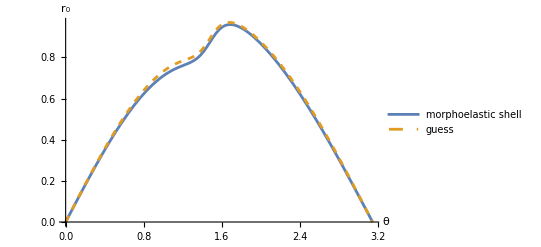

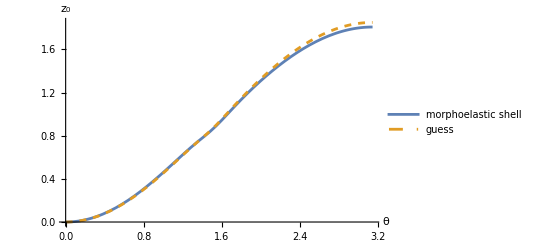

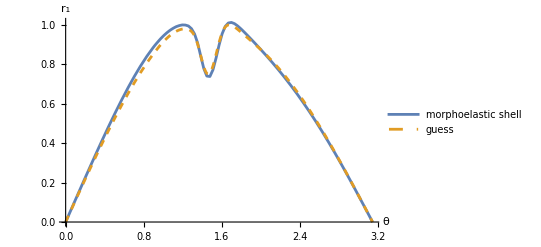

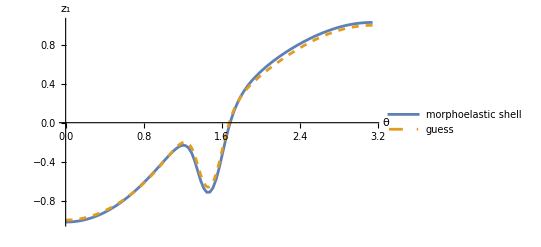

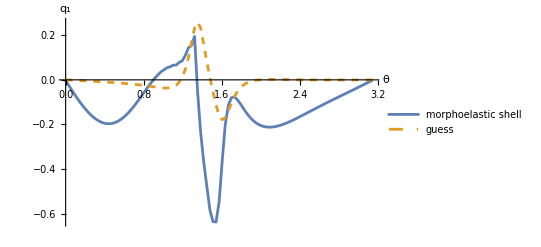

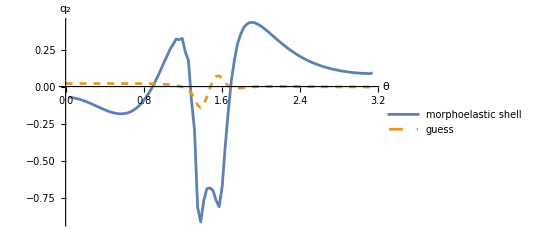

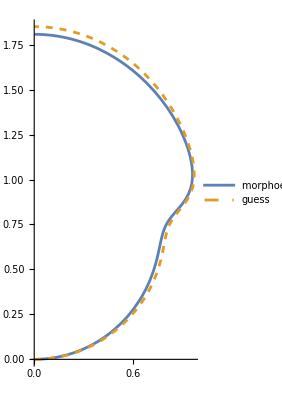

```mathematica
DateList[]
r0intp[θ_]=Piecewise[Table[{((h+h j-θ) r0[j]+(-h j+θ) r0[1+j])/h/.sub,j h<=θ<(j+1)h},{j,0,n-1}]];
z0pintp[θ_]=Piecewise[Table[{((h+h j-θ) z0p[j]+(-h j+θ) z0p[1+j])/h/.sub,j h<=θ<(j+1)h},{j,0,n-1}]];
z0[0]=0;
Table[z0[j]=Sum[h/2(z0p[i]+z0p[i+1])/.sub,{i,0,j-1}],{j,1,n}];
z0intp[θ_]=Piecewise[Table[{z0[j]+(-((h j-θ) ((h (2+j)-θ) z0p[j]+(-h j+θ) z0p[1+j]))/(2 h)/.sub),j h<=θ<(j+1)h},{j,0,n-1}]];
r1intp[θ_]=Piecewise[Table[{((h+h j-θ) r1[j]+(-h j+θ) r1[1+j])/h/.sub,j h<=θ<(j+1)h},{j,0,n-1}]];
z1intp[θ_]=Piecewise[Table[{((h+h j-θ) z1[j]+(-h j+θ) z1[1+j])/h/.sub,j h<=θ<(j+1)h},{j,0,n-1}]];
Plot[{r0intp[θ],r0g[θ]},{θ,0,π},PlotStyle->{Full,Dashed},PlotLegends->{"morphoelastic shell","guess"},AxesLabel->{HoldForm[θ],HoldForm[Subscript[r, 0]]}]
Plot[{z0intp[θ],z0g[θ]},{θ,0,π},PlotStyle->{Full,Dashed},PlotLegends->{"morphoelastic shell","guess"},AxesLabel->{HoldForm[θ],HoldForm[Subscript[z, 0]]}]
Plot[{r1intp[θ],r1g[θ]},{θ,0,π},PlotStyle->{Full,Dashed},PlotLegends->{"morphoelastic shell","guess"},AxesLabel->{HoldForm[θ],HoldForm[Subscript[r, 1]]}]
Plot[{z1intp[θ],z1g[θ]},{θ,0,π},PlotStyle->{Full,Dashed},PlotLegends->{"morphoelastic shell","guess"},AxesLabel->{HoldForm[θ],HoldForm[Subscript[z, 1]]}]
ListPlot[{Table[{j h,q1[j]/.sub//Chop},{j,0,n}],Table[{j h,guess[[4n+1+j,2]]},{j,0,n}]},Joined->True,PlotStyle->{Full,Dashed},PlotLegends->{"morphoelastic shell","guess"},AxesLabel->{HoldForm[θ],HoldForm[Subscript[q, 1]]},PlotRange->Full]
ListPlot[{Table[{j h,q2[j]/.sub//Chop},{j,1,n}],Table[{j h,guess[[5n+2+j,2]]},{j,0,n}]},Joined->True,PlotStyle->{Full,Dashed},PlotLegends->{"morphoelastic shell","guess"},AxesLabel->{HoldForm[θ],HoldForm[Subscript[q, 2]]},PlotRange->Full]
ParametricPlot[{{r0intp[θ],z0intp[θ]},{r0g[θ],z0g[θ]}},{θ,0,π-0.001},PlotStyle->{Full,Dashed},PlotLegends->{"morphoelastic shell","guess"}]
```

Aspect ratio

```mathematica
(z0[n]//Re)/(Table[r0[j]/.sub,{j,1,n-1}]//Chop//Max)
```

1.88362

#### 13 Stress distribution

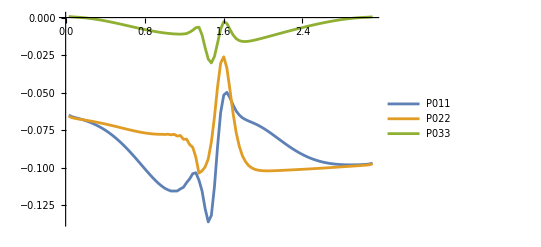

{{{-0.0650543,0,0},{0,-0.0657358,-0.000589471},{0,-0.000405446,0.000740021}},{{-0.066063,0,0},{0,-0.066756,-0.00117728},{0,-0.000798725,0.000503435}},{{-0.066675,0,0},{0,-0.06723,-0.00175574},{0,-0.00117718,0.00035052}},{{-0.0672184,0,0},{0,-0.0675908,-0.00232794},{0,-0.00154245,0.000224551}},{{-0.0677997,0,0},{0,-0.0679372,-0.00288957},{0,-0.00188725,0.000060151}},{{-0.0684365,0,0},{0,-0.0682791,-0.0034385},{0,-0.00220776,-0.000134817}},{{-0.0691454,0,0},{0,-0.0686291,-0.00397195},{0,-0.00249914,-0.000361216}},{{-0.0699373,0,0},{0,-0.0689929,-0.00448743},{0,-0.00275694,-0.000618362}},{{-0.0708208,0,0},{0,-0.0693736,-0.00498244},{0,-0.00297672,-0.000904914}},{{-0.071803,0,0},{0,-0.0697729,-0.00545454},{0,-0.00315415,-0.00121939}},{{-0.0728901,0,0},{0,-0.0701913,-0.00590137},{0,-0.00328507,-0.00156003}},{{-0.0740874,0,0},{0,-0.0706284,-0.00632068},{0,-0.00336549,-0.00192491}},{{-0.0753992,0,0},{0,-0.0710834,-0.00671029},{0,-0.00339165,-0.0023119}},{{-0.0768289,0,0},{0,-0.0715545,-0.00706818},{0,-0.00336006,-0.00271873}},{{-0.0783786,0,0},{0,-0.0720396,-0.00739247},{0,-0.00326758,-0.00314298}},{{-0.0800491,0,0},{0,-0.072536,-0.00768144},{0,-0.00311141,-0.00358211}},{{-0.0818394,0,0},{0,-0.0730403,-0.00793358},{0,-0.00288924,-0.00403346}},{{-0.0837467,0,0},{0,-0.0735485,-0.00814757},{0,-0.00259922,-0.00449429}},{{-0.0857657,0,0},{0,-0.0740561,-0.00832235},{0,-0.00224007,-0.00496178}},{{-0.0878887,0,0},{0,-0.0745578,-0.00845706},{0,-0.00181112,-0.00543304}},{{-0.0901053,0,0},{0,-0.0750479,-0.00855112},{0,-0.0013124,-0.00590517}},{{-0.0924014,0,0},{0,-0.0755199,-0.0086042},{0,-0.000744628,-0.00637519}},{{-0.0947598,0,0},{0,-0.0759669,-0.00861618},{0,-0.00010931,-0.00684006}},{{-0.097159,0,0},{0,-0.0763813,-0.00858732},{0,0.000591024,-0.00729697}},{{-0.099574,0,0},{0,-0.0767568,-0.00851762},{0,0.0013535,-0.00774237}},{{-0.101974,0,0},{0,-0.0770833,-0.00840815},{0,0.00217285,-0.00817408}},{{-0.104327,0,0},{0,-0.0773598,-0.00825835},{0,0.00304524,-0.00858765}},{{-0.10659,0,0},{0,-0.0775739,-0.00806968},{0,0.00396172,-0.00898112}},{{-0.108722,0,0},{0,-0.0777277,-0.00784181},{0,0.00491457,-0.00935118}},{{-0.11068,0,0},{0,-0.0778391,-0.00757125},{0,0.00589784,-0.00969134}},{{-0.112385,0,0},{0,-0.0778451,-0.00726579},{0,0.00687683,-0.0100078}},{{-0.113856,0,0},{0,-0.0779598,-0.00689915},{0,0.00788633,-0.0102785}},{{-0.114868,0,0},{0,-0.0777874,-0.00650747},{0,0.00878472,-0.0105323}},{{-0.115679,0,0},{0,-0.0781925,-0.00600855},{0,0.00974698,-0.010721}},{{-0.115668,0,0},{0,-0.0778412,-0.00549356},{0,0.0103513,-0.0109022}},{{-0.115653,0,0},{0,-0.0790415,-0.00478819},{0,0.0110519,-0.0109917}},{{-0.114253,0,0},{0,-0.0786432,-0.00405635},{0,0.0109021,-0.0110671}},{{-0.113155,0,0},{0,-0.081158,-0.00302251},{0,0.0106145,-0.0109352}},{{-0.110095,0,0},{0,-0.0810504,-0.00195839},{0,0.0085737,-0.0106754}},{{-0.107564,0,0},{0,-0.0846843,-0.000645946},{0,0.00513891,-0.00972174}},{{-0.104102,0,0},{0,-0.086494,0.000316963},{0,-0.00159962,-0.008472}},{{-0.103471,0,0},{0,-0.0931262,0.000518573},{0,-0.0130289,-0.00674773}},{{-0.108431,0,0},{0,-0.103754,0.000212383},{0,-0.0311168,-0.00639971}},{{-0.115632,0,0},{0,-0.1022,-0.000129174},{0,-0.0518905,-0.0116013}},{{-0.127476,0,0},{0,-0.099575,0.00074298},{0,-0.0729321,-0.0201065}},{{-0.136256,0,0},{0,-0.0942499,0.00183485},{0,-0.0869417,-0.0276948}},{{-0.131957,0,0},{0,-0.083034,0.00120669},{0,-0.0855776,-0.030268}},{{-0.112765,0,0},{0,-0.0664031,-0.00126218},{0,-0.0684464,-0.0259398}},{{-0.0860153,0,0},{0,-0.0462357,-0.00363049},{0,-0.0435283,-0.0169637}},{{-0.0633562,0,0},{0,-0.030362,-0.00389223},{0,-0.023125,-0.00758141}},{{-0.0516732,0,0},{0,-0.0261515,-0.001739},{0,-0.0127008,-0.00277737}},{{-0.0498606,0,0},{0,-0.0335262,0.00131043},{0,-0.00844389,-0.00394443}},{{-0.0534769,0,0},{0,-0.048185,0.0035274},{0,-0.00556416,-0.00787632}},{{-0.0582664,0,0},{0,-0.0637503,0.00456352},{0,-0.00193939,-0.0115646}},{{-0.0622785,0,0},{0,-0.0766617,0.00491307},{0,0.00224467,-0.0140392}},{{-0.0649745,0,0},{0,-0.0857648,0.00503578},{0,0.00632181,-0.0153605}},{{-0.066816,0,0},{0,-0.0920877,0.00512447},{0,0.00984027,-0.0159171}},{{-0.0680004,0,0},{0,-0.0960255,0.00527108},{0,0.0126941,-0.0159994}},{{-0.0689744,0,0},{0,-0.0986619,0.00545589},{0,0.0149172,-0.0158017}},{{-0.0698209,0,0},{0,-0.100199,0.00568789},{0,0.0166077,-0.0154521}},{{-0.0707366,0,0},{0,-0.101196,0.00593304},{0,0.0178667,-0.0150049}},{{-0.07173,0,0},{0,-0.101736,0.00618986},{0,0.0187821,-0.0145118}},{{-0.0728522,0,0},{0,-0.102049,0.00643995},{0,0.0194245,-0.0139845}},{{-0.0740876,0,0},{0,-0.102186,0.00668034},{0,0.0198491,-0.0134427}},{{-0.0754288,0,0},{0,-0.102228,0.00690361},{0,0.0200976,-0.0128895}},{{-0.0768522,0,0},{0,-0.102206,0.00710718},{0,0.0202025,-0.0123314}},{{-0.0783345,0,0},{0,-0.102146,0.00728838},{0,0.0201887,-0.0117707}},{{-0.0798513,0,0},{0,-0.102065,0.00744564},{0,0.0200756,-0.0112095}},{{-0.0813791,0,0},{0,-0.101972,0.00757791},{0,0.0198788,-0.0106493}},{{-0.0828966,0,0},{0,-0.101872,0.00768445},{0,0.0196105,-0.0100914}},{{-0.0843847,0,0},{0,-0.101768,0.0077648},{0,0.0192809,-0.00953691}},{{-0.0858271,0,0},{0,-0.101663,0.00781865},{0,0.0188984,-0.00898698}},{{-0.08721,0,0},{0,-0.101557,0.00784584},{0,0.0184698,-0.00844263}},{{-0.0885223,0,0},{0,-0.10145,0.00784629},{0,0.0180011,-0.0079049}},{{-0.0897552,0,0},{0,-0.101341,0.00782002},{0,0.0174972,-0.00737484}},{{-0.0909024,0,0},{0,-0.101231,0.0077671},{0,0.0169625,-0.00685348}},{{-0.0919597,0,0},{0,-0.101117,0.00768766},{0,0.0164006,-0.0063419}},{{-0.0929245,0,0},{0,-0.101002,0.00758193},{0,0.0158147,-0.00584117}},{{-0.0937962,0,0},{0,-0.100883,0.00745018},{0,0.0152075,-0.00535237}},{{-0.0945756,0,0},{0,-0.10076,0.00729273},{0,0.0145814,-0.00487658}},{{-0.0952648,0,0},{0,-0.100635,0.00711001},{0,0.0139384,-0.00441492}},{{-0.0958669,0,0},{0,-0.100506,0.00690251},{0,0.0132803,-0.00396848}},{{-0.096386,0,0},{0,-0.100375,0.00667079},{0,0.0126086,-0.00353836}},{{-0.0968269,0,0},{0,-0.100241,0.0064155},{0,0.0119246,-0.00312565}},{{-0.0971949,0,0},{0,-0.100105,0.00613739},{0,0.0112296,-0.00273143}},{{-0.0974957,0,0},{0,-0.0999676,0.00583728},{0,0.0105244,-0.00235678}},{{-0.0977353,0,0},{0,-0.0998292,0.00551608},{0,0.00980997,-0.00200271}},{{-0.0979196,0,0},{0,-0.0996904,0.00517483},{0,0.00908717,-0.00167024}},{{-0.0980546,0,0},{0,-0.0995516,0.00481462},{0,0.00835668,-0.00136034}},{{-0.0981458,0,0},{0,-0.0994131,0.00443665},{0,0.00761919,-0.0010739}},{{-0.0981984,0,0},{0,-0.0992751,0.00404221},{0,0.00687534,-0.000811798}},{{-0.098217,0,0},{0,-0.0991371,0.00363267},{0,0.00612574,-0.000574809}},{{-0.0982052,0,0},{0,-0.0989984,0.00320951},{0,0.00537101,-0.000363582}},{{-0.0981654,0,0},{0,-0.0988574,0.00277425},{0,0.00461178,-0.000178827}},{{-0.0980979,0,0},{0,-0.0987111,0.00232848},{0,0.00384866,-0.0000206301}},{{-0.0979981,0,0},{0,-0.0985516,0.00187401},{0,0.00308244,0.000111695}},{{-0.0978644,0,0},{0,-0.0983777,0.00141213},{0,0.00231358,0.000210274}},{{-0.0976299,0,0},{0,-0.0981289,0.000946184},{0,0.00154392,0.000324906}},{{-0.0970718,0,0},{0,-0.0975086,0.000473976},{0,0.000770266,0.000484584}}}

```mathematica
subj={𝓇0->r0[j],𝓇0p->1/(2h)(r0[j+1]-r0[j-1]),𝓏0p->z0p[j],𝓇1->r1[j],𝓏1->z1[j],θ-> j h};
dataPK0=Table[(PK0dis/.subj)/.sub,{j,1,n-1}];
ListPlot[{Table[{j h,dataPK0[[j,1,1]]},{j,1,n-1}],Table[{j h,dataPK0[[j,2,2]]},{j,1,n-1}],Table[{j h,dataPK0[[j,3,3]]},{j,1,n-1}]},Joined->True,PlotRange->Full,PlotLegends->{"P011","P022","P033"}]
dataPK0//Chop
```

#### 13 Comparison with Hohn et al. BMC 2011

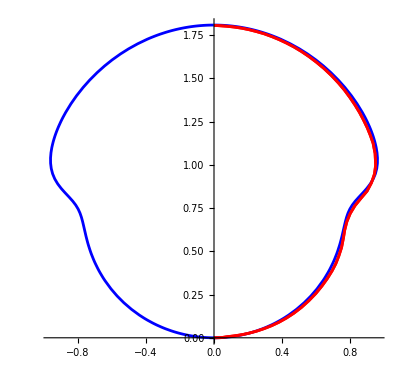

```mathematica
data={{0,1.805758},{0.00107852491929594,1.80569786718377},{0.0322108763785889,1.8038563392853},{0.075944222898086,1.8007834920455699},{0.119681167224884,1.79608011853726},{0.163422109115349,1.78956504917495},{0.207168247838581,1.78069477520246},{0.250919183638214,1.76965046620519},{0.294673317488781,1.75715680052472},{0.338434646953949,1.74140208230707},{0.382200373739151,1.72365449865004},{0.425971697113486,1.70337054079742},{0.46974821732059,1.6807313783346098},{0.513531933142294,1.65483116333463},{0.5573228445786,1.62566989579747},{0.601121351385872,1.59306640613772},{0.644927053807747,1.5572018639407998},{0.688743549651522,1.51644574293811},{0.730578772990545,1.4728350576621798},{0.766447492641499,1.4309420535379098},{0.798342354177769,1.38846702013395},{0.828252401558238,1.34474249871215},{0.85418392128894,1.3025521813105698},{0.878133191967193,1.25794987105152},{0.900095460299438,1.2130897605766},{0.918080279372304,1.1692751275975},{0.934079928315842,1.12437233380279},{0.945737883323857,1.06543725204773},{0.949066654589559,0.9980657359147401},{0.942420545090243,0.9474738653529},{0.924645698048998,0.896129173601251},{0.898913460674311,0.848004727256867},{0.863228329134774,0.806695599286706},{0.827547155183269,0.7635928924210971},{0.799821319482522,0.718199944019936},{0.780049502836524,0.671114613715042},{0.767240109577619,0.6213444263747511},{0.759983652057589,0.577132099771774},{0.748975401084592,0.521774765542742},{0.732786007781588,0.472516250361601},{0.714996429718229,0.42784765783190104},{0.69322441876612,0.38648312362931203},{0.665495468297017,0.34250178824771804},{0.633789691522206,0.29928360775801705},{0.598108627503701,0.25613107925642303},{0.556462968633778,0.213831147136211},{0.512821965834994,0.1750538201488},{0.469167771076108,0.14225508947954998},{0.425503182651687,0.114166768030671},{0.381829799587198,0.090064177460567},{0.338148021639008,0.0697661481838397},{0.29445864831985,0.0529103410296908},{0.250763678411559,0.0385909080711258},{0.207062712157766,0.026989018893544305},{0.163356549071206,0.017742334326147698},{0.119644389639145,0.0112131935397336},{0.0759294319125172,0.005952239851112399},{0.0414080201198674,0.0008429355499445009},{0.00476726259404847,0.0000830101038208006},{0,0.}};
FigH=ListPlot[{Table[{ data[[i,1]], data[[i,2]]},{i,1,Length[data]}],Table[{data[[i,1]], data[[i,2]]},{i,1,Length[data]}]},Joined->True,AspectRatio->Automatic,PlotStyle->{Red,Red}];
Figmy=ParametricPlot[{{r0intp[θ],z0intp[θ]},{-r0intp[θ],z0intp[θ]}},{θ,0,π-0.001},PlotStyle->{Blue,Blue}];
Show[Figmy,FigH]
```